```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

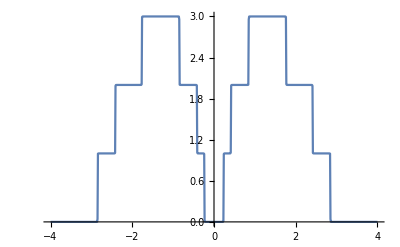

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m1=Table[{ω,ψ[ω,0.001,1,0,0.5]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000493136},{0.01,0.000294004},{0.02,0.000147938},{0.03,0.0000488575},{0.04,7.13536×10^-6},{0.05,0.0000220184},{0.06,4.04147×10^-6},{0.07,0.0000727197},{0.08,0.000187716},{0.09,0.000355119},{0.1,0.000584011},{0.11,0.000887421},{0.12,0.0012838},{0.13,0.00179934},{0.14,0.00247168},{0.15,0.00335597},{0.16,0.00453545},{0.17,0.00614046},{0.18,0.00838543},{0.19,0.0116471},{0.2,0.0166513},{0.21,0.025003},{0.22,0.0411917},{0.23,0.0866392},{0.24,0.0271482},{0.25,0.315744},{0.26,0.484353},{0.27,0.591886},{0.28,0.664824},{0.29,0.716185},{0.3,0.753024},{0.31,0.779443},{0.32,0.79793},{0.33,0.810008},{0.34,0.816547},{0.35,0.817894},{0.36,0.813857},{0.37,0.803497},{0.38,0.784507},{0.39,0.751387},{0.4,0.68855},{0.41,0.52236},{0.42,0.41708},{0.43,0.69315},{0.44,0.898429},{0.45,1.05808},{0.46,1.18565},{0.47,1.2892},{0.48,1.37407},{0.49,1.44406},{0.5,1.50199},{0.51,1.55006},{0.52,1.58999},{0.53,1.6232},{0.54,1.65084},{0.55,1.67384},{0.56,1.69302},{0.57,1.70902},{0.58,1.72241},{0.59,1.73367},{0.6,1.74318},{0.61,1.7513},{0.62,1.75832},{0.63,1.76447},{0.64,1.76997},{0.65,1.77499},{0.66,1.7797},{0.67,1.7842},{0.68,1.78862},{0.69,1.79303},{0.7,1.7975},{0.71,1.80209},{0.72,1.80682},{0.73,1.8117},{0.74,1.81673},{0.75,1.82188},{0.76,1.82707},{0.77,1.8322},{0.78,1.83707},{0.79,1.84134},{0.8,1.84443},{0.81,1.84514},{0.82,1.84074},{0.83,1.82336},{0.84,1.7579},{0.85,1.43765},{0.86,1.8567},{0.87,2.11482},{0.88,2.28209},{0.89,2.39855},{0.9,2.48397},{0.91,2.54916},{0.92,2.60051},{0.93,2.64204},{0.94,2.67639},{0.95,2.70543},{0.96,2.73056},{0.97,2.75285},{0.98,2.77312},{0.99,2.79173},{1.,2.80786},{1.01,2.81693},{1.02,2.80197},{1.03,2.70598},{1.04,2.39233},{1.05,1.87913},{1.06,1.34262},{1.07,1.03788},{1.08,1.26903},{1.09,1.81045},{1.1,2.08622},{1.11,2.19998},{1.12,2.25558},{1.13,2.28743},{1.14,2.30787},{1.15,2.3222},{1.16,2.3331},{1.17,2.3421},{1.18,2.35014},{1.19,2.35785},{1.2,2.36563},{1.21,2.37378},{1.22,2.3825},{1.23,2.39191},{1.24,2.40207},{1.25,2.41302},{1.26,2.42473},{1.27,2.43716},{1.28,2.45021},{1.29,2.46377},{1.3,2.47771},{1.31,2.49185},{1.32,2.50603},{1.33,2.52003},{1.34,2.53368},{1.35,2.54677},{1.36,2.5591},{1.37,2.57049},{1.38,2.58077},{1.39,2.58981},{1.4,2.59747},{1.41,2.60366},{1.42,2.60832},{1.43,2.61141},{1.44,2.61293},{1.45,2.61289},{1.46,2.61135},{1.47,2.60841},{1.48,2.60418},{1.49,2.59882},{1.5,2.59254},{1.51,2.58555},{1.52,2.57814},{1.53,2.57061},{1.54,2.56331},{1.55,2.55663},{1.56,2.55097},{1.57,2.54676},{1.58,2.54444},{1.59,2.54444},{1.6,2.54714},{1.61,2.55282},{1.62,2.56161},{1.63,2.57335},{1.64,2.58744},{1.65,2.6026},{1.66,2.61663},{1.67,2.62612},{1.68,2.62635},{1.69,2.61155},{1.7,2.57562},{1.71,2.5132},{1.72,2.42027},{1.73,2.29255},{1.74,2.11861},{1.75,1.85322},{1.76,1.21339},{1.77,0.819781},{1.78,0.634456},{1.79,0.0509031},{1.8,2.30248},{1.81,1.3573},{1.82,0.560813},{1.83,1.25591},{1.84,1.52921},{1.85,1.65606},{1.86,1.72195},{1.87,1.75857},{1.88,1.77962},{1.89,1.7918},{1.9,1.79868},{1.91,1.80232},{1.92,1.80394},{1.93,1.80436},{1.94,1.80405},{1.95,1.80335},{1.96,1.80246},{1.97,1.80147},{1.98,1.80043},{1.99,1.79932},{2.,1.79808},{2.01,1.79661},{2.02,1.79479},{2.03,1.7925},{2.04,1.78959},{2.05,1.78592},{2.06,1.78139},{2.07,1.77591},{2.08,1.76941},{2.09,1.7619},{2.1,1.75343},{2.11,1.74409},{2.12,1.73405},{2.13,1.72351},{2.14,1.71274},{2.15,1.70202},{2.16,1.69166},{2.17,1.682},{2.18,1.67336},{2.19,1.66606},{2.2,1.6604},{2.21,1.65664},{2.22,1.65496},{2.23,1.65548},{2.24,1.65823},{2.25,1.66305},{2.26,1.66961},{2.27,1.67733},{2.28,1.68529},{2.29,1.69225},{2.3,1.69656},{2.31,1.69636},{2.32,1.68966},{2.33,1.67474},{2.34,1.6504},{2.35,1.6163},{2.36,1.57283},{2.37,1.52072},{2.38,1.45995},{2.39,1.38748},{2.4,1.29023},{2.41,1.10391},{2.42,6.11298},{2.43,0.176187},{2.44,0.123821},{2.45,0.534862},{2.46,1.07116},{2.47,1.06749},{2.48,0.479396},{2.49,0.0609132},{2.5,0.398528},{2.51,0.599923},{2.52,0.724776},{2.53,0.806266},{2.54,0.861912},{2.55,0.901236},{2.56,0.929647},{2.57,0.950364},{2.58,0.965383},{2.59,0.975987},{2.6,0.98302},{2.61,0.98705},{2.62,0.988459},{2.63,0.987502},{2.64,0.984338},{2.65,0.979061},{2.66,0.971715},{2.67,0.962317},{2.68,0.950872},{2.69,0.937397},{2.7,0.921944},{2.71,0.904626},{2.72,0.885648},{2.73,0.865329},{2.74,0.84413},{2.75,0.822677},{2.76,0.801786},{2.77,0.782489},{2.78,0.766089},{2.79,0.754261},{2.8,0.74926},{2.81,0.754345},{2.82,0.774711},{2.83,0.819553},{2.84,0.904163},{2.85,0.0225868},{2.86,0.000704504},{2.87,0.00627615},{2.88,0.00188462},{2.89,0.000696845},{2.9,0.000523999},{2.91,0.000380647},{2.92,0.000283981},{2.93,0.00021739},{2.94,0.000169948},{2.95,0.000135135},{2.96,0.000108958},{2.97,0.0000888756},{2.98,0.0000732071},{2.99,0.000060808},{3.,0.0000508761},{3.01,0.0000428366},{3.02,0.0000362686},{3.03,0.0000308591},{3.04,0.0000263714},{3.05,0.0000226244},{3.06,0.0000194773},{3.07,0.0000168203},{3.08,0.0000145661},{3.09,0.0000126452},{3.1,0.0000110018},{3.11,9.59055×10^-6},{3.12,8.37449×10^-6},{3.13,7.32331×10^-6},{3.14,6.41199×10^-6},{3.15,5.61977×10^-6},{3.16,4.92935×10^-6},{3.17,4.32623×10^-6},{3.18,3.79823×10^-6},{3.19,3.33506×10^-6},{3.2,2.92799×10^-6},{3.21,2.56959×10^-6},{3.22,2.25354×10^-6},{3.23,1.97442×10^-6},{3.24,1.72757×10^-6},{3.25,1.50899×10^-6},{3.26,1.3152×10^-6},{3.27,1.14322×10^-6},{3.28,9.90447×10^-7},{3.29,8.5462×10^-7},{3.3,7.33768×10^-7},{3.31,6.26172×10^-7},{3.32,5.30324×10^-7},{3.33,4.44903×10^-7},{3.34,3.68751×10^-7},{3.35,3.00846×10^-7},{3.36,2.40288×10^-7},{3.37,1.86282×10^-7},{3.38,1.38126×10^-7},{3.39,9.51976×10^-8},{3.4,5.69455×10^-8},{3.41,2.28795×10^-8},{3.42,7.43594×10^-9},{3.43,3.43886×10^-8},{3.44,5.83242×10^-8},{3.45,7.95512×10^-8},{3.46,9.8345×10^-8},{3.47,1.14952×10^-7},{3.48,1.29593×10^-7},{3.49,1.42466×10^-7},{3.5,1.53747×10^-7},{3.51,1.63596×10^-7},{3.52,1.72156×10^-7},{3.53,1.79555×10^-7},{3.54,1.85909×10^-7},{3.55,1.91322×10^-7},{3.56,1.95888×10^-7},{3.57,1.99691×10^-7},{3.58,2.02809×10^-7},{3.59,2.05308×10^-7},{3.6,2.07253×10^-7},{3.61,2.08699×10^-7},{3.62,2.09697×10^-7},{3.63,2.10292×10^-7},{3.64,2.10527×10^-7},{3.65,2.1044×10^-7},{3.66,2.10063×10^-7},{3.67,2.09429×10^-7},{3.68,2.08565×10^-7},{3.69,2.07496×10^-7},{3.7,2.06246×10^-7},{3.71,2.04835×10^-7},{3.72,2.03282×10^-7},{3.73,2.01604×10^-7},{3.74,1.99817×10^-7},{3.75,1.97934×10^-7},{3.76,1.95969×10^-7},{3.77,1.93933×10^-7},{3.78,1.91837×10^-7},{3.79,1.89689×10^-7},{3.8,1.87499×10^-7},{3.81,1.85274×10^-7},{3.82,1.83021×10^-7},{3.83,1.80746×10^-7},{3.84,1.78456×10^-7},{3.85,1.76155×10^-7},{3.86,1.73848×10^-7},{3.87,1.71539×10^-7},{3.88,1.69231×10^-7},{3.89,1.66929×10^-7},{3.9,1.64636×10^-7},{3.91,1.62353×10^-7},{3.92,1.60083×10^-7},{3.93,1.57829×10^-7},{3.94,1.55592×10^-7},{3.95,1.53374×10^-7},{3.96,1.51177×10^-7},{3.97,1.49001×10^-7},{3.98,1.46848×10^-7},{3.99,1.4472×10^-7},{4.,1.42615×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281642},{0.01,0.0000118378},{0.02,0.0000357694},{0.03,0.00011435},{0.04,0.0002249},{0.05,0.000369754},{0.06,0.000552714},{0.07,0.000779297},{0.08,0.00105713},{0.09,0.00139656},{0.1,0.0018115},{0.11,0.00232077},{0.12,0.00295001},{0.13,0.00373474},{0.14,0.00472508},{0.15,0.00599346},{0.16,0.00764782},{0.17,0.00985517},{0.18,0.0128866},{0.19,0.0172109},{0.2,0.0237119},{0.21,0.0342869},{0.22,0.054004},{0.23,0.105121},{0.24,0.138437},{0.25,0.00446443},{0.26,0.109698},{0.27,0.208041},{0.28,0.294426},{0.29,0.3713},{0.3,0.440137},{0.31,0.501766},{0.32,0.556604},{0.33,0.6048},{0.34,0.64633},{0.35,0.681039},{0.36,0.708611},{0.37,0.728436},{0.38,0.739225},{0.39,0.7379},{0.4,0.715451},{0.41,0.628462},{0.42,0.766179},{0.43,1.12482},{0.44,1.36738},{0.45,1.53638},{0.46,1.6517},{0.47,1.72627},{0.48,1.77016},{0.49,1.79164},{0.5,1.79745},{0.51,1.79295},{0.52,1.78218},{0.53,1.76814},{0.54,1.75292},{0.55,1.73797},{0.56,1.72421},{0.57,1.71222},{0.58,1.70232},{0.59,1.69466},{0.6,1.68928},{0.61,1.68614},{0.62,1.68513},{0.63,1.68614},{0.64,1.68902},{0.65,1.69359},{0.66,1.69969},{0.67,1.70714},{0.68,1.71575},{0.69,1.72531},{0.7,1.73564},{0.71,1.74654},{0.72,1.7578},{0.73,1.76922},{0.74,1.78063},{0.75,1.79182},{0.76,1.80263},{0.77,1.81287},{0.78,1.82236},{0.79,1.83085},{0.8,1.83799},{0.81,1.84303},{0.82,1.84414},{0.83,1.83525},{0.84,1.7826},{0.85,1.50585},{0.86,2.23036},{0.87,2.46356},{0.88,2.58122},{0.89,2.65425},{0.9,2.70518},{0.91,2.74351},{0.92,2.77401},{0.93,2.79932},{0.94,2.82105},{0.95,2.84018},{0.96,2.85728},{0.97,2.87258},{0.98,2.88589},{0.99,2.89631},{1.,2.9014},{1.01,2.8945},{1.02,2.85513},{1.03,2.71181},{1.04,2.29331},{1.05,1.81762},{1.06,1.25754},{1.07,0.774252},{1.08,1.39542},{1.09,1.94368},{1.1,2.16613},{1.11,2.28624},{1.12,2.36217},{1.13,2.41189},{1.14,2.4443},{1.15,2.46474},{1.16,2.47667},{1.17,2.48243},{1.18,2.48365},{1.19,2.48153},{1.2,2.47695},{1.21,2.47058},{1.22,2.46295},{1.23,2.45445},{1.24,2.44541},{1.25,2.43607},{1.26,2.42664},{1.27,2.4173},{1.28,2.40818},{1.29,2.3994},{1.3,2.39107},{1.31,2.38329},{1.32,2.37617},{1.33,2.3698},{1.34,2.36429},{1.35,2.35975},{1.36,2.3563},{1.37,2.35406},{1.38,2.35319},{1.39,2.35382},{1.4,2.35612},{1.41,2.36026},{1.42,2.3664},{1.43,2.37471},{1.44,2.38535},{1.45,2.39844},{1.46,2.41408},{1.47,2.43228},{1.48,2.45296},{1.49,2.47588},{1.5,2.50061},{1.51,2.52647},{1.52,2.55246},{1.53,2.57726},{1.54,2.59929},{1.55,2.61677},{1.56,2.62799},{1.57,2.63153},{1.58,2.62659},{1.59,2.61308},{1.6,2.59169},{1.61,2.56369},{1.62,2.53059},{1.63,2.49387},{1.64,2.45467},{1.65,2.41362},{1.66,2.37082},{1.67,2.32576},{1.68,2.27742},{1.69,2.22439},{1.7,2.16506},{1.71,2.09805},{1.72,2.02297},{1.73,1.94124},{1.74,1.85584},{1.75,1.76551},{1.76,1.62473},{1.77,1.2974},{1.78,2.88396},{1.79,1.84517},{1.8,1.00611},{1.81,1.22264},{1.82,0.897527},{1.83,1.45776},{1.84,1.59905},{1.85,1.66235},{1.86,1.70127},{1.87,1.72898},{1.88,1.75015},{1.89,1.76693},{1.9,1.78053},{1.91,1.79174},{1.92,1.80111},{1.93,1.80908},{1.94,1.81599},{1.95,1.82213},{1.96,1.82774},{1.97,1.83301},{1.98,1.8381},{1.99,1.84313},{2.,1.84816},{2.01,1.85325},{2.02,1.85839},{2.03,1.86352},{2.04,1.86858},{2.05,1.87342},{2.06,1.87788},{2.07,1.88177},{2.08,1.88489},{2.09,1.88701},{2.1,1.88793},{2.11,1.88748},{2.12,1.88556},{2.13,1.88212},{2.14,1.87724},{2.15,1.87106},{2.16,1.86387},{2.17,1.85603},{2.18,1.84799},{2.19,1.84027},{2.2,1.83343},{2.21,1.82805},{2.22,1.8247},{2.23,1.82391},{2.24,1.82615},{2.25,1.83175},{2.26,1.84089},{2.27,1.85342},{2.28,1.86872},{2.29,1.88545},{2.3,1.90125},{2.31,1.91246},{2.32,1.91419},{2.33,1.90096},{2.34,1.86825},{2.35,1.81461},{2.36,1.74297},{2.37,1.66001},{2.38,1.57326},{2.39,1.48691},{2.4,1.3934},{2.41,1.20995},{2.42,3},{2.43,0.439431},{2.44,0.460577},{2.45,0.149221},{2.46,0.331156},{2.47,0.726796},{2.48,0.848691},{2.49,0.897962},{2.5,0.922333},{2.51,0.935833},{2.52,0.943722},{2.53,0.948367},{2.54,0.950999},{2.55,0.952342},{2.56,0.952869},{2.57,0.95292},{2.58,0.952756},{2.59,0.952587},{2.6,0.95258},{2.61,0.95287},{2.62,0.95355},{2.63,0.954671},{2.64,0.956234},{2.65,0.958181},{2.66,0.960389},{2.67,0.962657},{2.68,0.964706},{2.69,0.966179},{2.7,0.966652},{2.71,0.965665},{2.72,0.962759},{2.73,0.957552},{2.74,0.949817},{2.75,0.939584},{2.76,0.927236},{2.77,0.91359},{2.78,0.899946},{2.79,0.8881},{2.8,0.880267},{2.81,0.87874},{2.82,0.884186},{2.83,0.885848},{2.84,0.783328},{2.85,0.0162478},{2.86,0.0460297},{2.87,0.00443891},{2.88,0.00209742},{2.89,0.00122325},{2.9,0.000792628},{2.91,0.000547683},{2.92,0.000395415},{2.93,0.000294817},{2.94,0.000225319},{2.95,0.000175628},{2.96,0.000139117},{2.97,0.000111683},{2.98,0.0000906833},{2.99,0.0000743535},{3.,0.0000614817},{3.01,0.0000512156},{3.02,0.0000429424},{3.03,0.0000362139},{3.04,0.0000306969},{3.05,0.0000261399},{3.06,0.0000223509},{3.07,0.0000191814},{3.08,0.0000165157},{3.09,0.0000142624},{3.1,0.000012349},{3.11,0.0000107174},{3.12,9.32052×10^-6},{3.13,8.1204×10^-6},{3.14,7.08586×10^-6},{3.15,6.1913×10^-6},{3.16,5.41556×10^-6},{3.17,4.74106×10^-6},{3.18,4.15314×10^-6},{3.19,3.6395×10^-6},{3.2,3.1898×10^-6},{3.21,2.79529×10^-6},{3.22,2.44856×10^-6},{3.23,2.14331×10^-6},{3.24,1.87414×10^-6},{3.25,1.63645×10^-6},{3.26,1.42627×10^-6},{3.27,1.24019×10^-6},{3.28,1.07527×10^-6},{3.29,9.28947×10^-7},{3.3,7.99012×10^-7},{3.31,6.83538×10^-7},{3.32,5.80847×10^-7},{3.33,4.8947×10^-7},{3.34,4.08124×10^-7},{3.35,3.35682×10^-7},{3.36,2.71154×10^-7},{3.37,2.1367×10^-7},{3.38,1.62461×10^-7},{3.39,1.16849×10^-7},{3.4,7.62346×10^-8},{3.41,4.00857×10^-8},{3.42,7.93138×10^-9},{3.43,2.06471×10^-8},{3.44,4.60219×10^-8},{3.45,6.85246×10^-8},{3.46,8.84508×10^-8},{3.47,1.06064×10^-7},{3.48,1.216×10^-7},{3.49,1.3527×10^-7},{3.5,1.47263×10^-7},{3.51,1.57747×10^-7},{3.52,1.66874×10^-7},{3.53,1.74781×10^-7},{3.54,1.8159×10^-7},{3.55,1.87411×10^-7},{3.56,1.92343×10^-7},{3.57,1.96475×10^-7},{3.58,1.99888×10^-7},{3.59,2.02654×10^-7},{3.6,2.04839×10^-7},{3.61,2.06501×10^-7},{3.62,2.07694×10^-7},{3.63,2.08466×10^-7},{3.64,2.08861×10^-7},{3.65,2.08918×10^-7},{3.66,2.08672×10^-7},{3.67,2.08156×10^-7},{3.68,2.074×10^-7},{3.69,2.06429×10^-7},{3.7,2.05267×10^-7},{3.71,2.03937×10^-7},{3.72,2.02458×10^-7},{3.73,2.00847×10^-7},{3.74,1.99121×10^-7},{3.75,1.97294×10^-7},{3.76,1.9538×10^-7},{3.77,1.9339×10^-7},{3.78,1.91336×10^-7},{3.79,1.89227×10^-7},{3.8,1.87073×10^-7},{3.81,1.8488×10^-7},{3.82,1.82657×10^-7},{3.83,1.8041×10^-7},{3.84,1.78145×10^-7},{3.85,1.75867×10^-7},{3.86,1.73581×10^-7},{3.87,1.71291×10^-7},{3.88,1.69002×10^-7},{3.89,1.66716×10^-7},{3.9,1.64438×10^-7},{3.91,1.62169×10^-7},{3.92,1.59912×10^-7},{3.93,1.5767×10^-7},{3.94,1.55444×10^-7},{3.95,1.53237×10^-7},{3.96,1.51049×10^-7},{3.97,1.48882×10^-7},{3.98,1.46737×10^-7},{3.99,1.44616×10^-7},{4.,1.42519×10^-7}}

```mathematica
ListPlot[%185,Joined->True,PlotStyle->Red]
```

ListPlot::lpn: %185 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[%185,Joined→True,PlotStyle→RGBColor[1, 0, 0]]

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000216316},{0.01,0.0000265043},{0.02,0.000027729},{0.03,0.0000254215},{0.04,0.0000195301},{0.05,9.8324×10^-6},{0.06,4.08136×10^-6},{0.07,0.0000228407},{0.08,0.0000473471},{0.09,0.0000788541},{0.1,0.000119086},{0.11,0.000170416},{0.12,0.000236135},{0.13,0.000320869},{0.14,0.000431238},{0.15,0.000576934},{0.16,0.000772564},{0.17,0.00104094},{0.18,0.00141938},{0.19,0.00197263},{0.2,0.00282275},{0.21,0.00422942},{0.22,0.00686683},{0.23,0.0133193},{0.24,0.0878858},{0.25,0.247627},{0.26,0.36473},{0.27,0.454006},{0.28,0.524014},{0.29,0.58008},{0.3,0.625678},{0.31,0.663142},{0.32,0.694052},{0.33,0.719445},{0.34,0.739922},{0.35,0.755669},{0.36,0.766356},{0.37,0.770835},{0.38,0.766293},{0.39,0.745582},{0.4,0.685978},{0.41,0.452515},{0.42,0.326604},{0.43,0.868453},{0.44,1.1408},{0.45,1.30895},{0.46,1.42603},{0.47,1.51394},{0.48,1.58338},{0.49,1.64017},{0.5,1.68775},{0.51,1.72828},{0.52,1.76319},{0.53,1.79343},{0.54,1.81971},{0.55,1.84253},{0.56,1.86228},{0.57,1.87925},{0.58,1.89372},{0.59,1.9059},{0.6,1.91598},{0.61,1.92415},{0.62,1.93058},{0.63,1.93544},{0.64,1.93889},{0.65,1.94106},{0.66,1.94211},{0.67,1.94216},{0.68,1.94134},{0.69,1.93977},{0.7,1.93753},{0.71,1.9347},{0.72,1.93135},{0.73,1.9275},{0.74,1.92315},{0.75,1.91826},{0.76,1.91273},{0.77,1.90636},{0.78,1.89884},{0.79,1.88958},{0.8,1.87761},{0.81,1.86105},{0.82,1.836},{0.83,1.79262},{0.84,1.6952},{0.85,1.41716},{0.86,1.63459},{0.87,1.7957},{0.88,1.9251},{0.89,2.03543},{0.9,2.13296},{0.91,2.22124},{0.92,2.30244},{0.93,2.37792},{0.94,2.44854},{0.95,2.51478},{0.96,2.57685},{0.97,2.63468},{0.98,2.68781},{0.99,2.73513},{1.,2.77411},{1.01,2.79901},{1.02,2.7961},{1.03,2.73137},{1.04,2.52301},{1.05,2.02372},{1.06,1.27966},{1.07,1.24045},{1.08,1.69179},{1.09,2.01336},{1.1,2.21109},{1.11,2.33787},{1.12,2.42356},{1.13,2.48412},{1.14,2.52848},{1.15,2.56194},{1.16,2.58781},{1.17,2.60825},{1.18,2.62468},{1.19,2.6381},{1.2,2.64918},{1.21,2.65837},{1.22,2.66595},{1.23,2.6721},{1.24,2.67688},{1.25,2.68031},{1.26,2.68233},{1.27,2.68286},{1.28,2.68178},{1.29,2.67899},{1.3,2.67437},{1.31,2.66783},{1.32,2.65932},{1.33,2.64883},{1.34,2.63637},{1.35,2.62203},{1.36,2.60594},{1.37,2.58827},{1.38,2.56921},{1.39,2.54901},{1.4,2.52789},{1.41,2.50612},{1.42,2.48393},{1.43,2.46154},{1.44,2.43916},{1.45,2.41697},{1.46,2.39513},{1.47,2.37375},{1.48,2.35296},{1.49,2.33281},{1.5,2.31337},{1.51,2.29468},{1.52,2.27676},{1.53,2.25964},{1.54,2.24331},{1.55,2.22778},{1.56,2.21303},{1.57,2.19905},{1.58,2.1858},{1.59,2.17323},{1.6,2.16122},{1.61,2.14962},{1.62,2.13811},{1.63,2.12626},{1.64,2.11331},{1.65,2.09814},{1.66,2.07909},{1.67,2.05376},{1.68,2.01885},{1.69,1.97002},{1.7,1.90172},{1.71,1.80689},{1.72,1.67584},{1.73,1.49266},{1.74,1.22417},{1.75,0.778112},{1.76,0.28228},{1.77,1.52757},{1.78,0.541383},{1.79,1.12016},{1.8,1.33071},{1.81,1.40042},{1.82,1.34028},{1.83,0.588957},{1.84,1.43577},{1.85,1.67744},{1.86,1.69972},{1.87,1.70628},{1.88,1.71086},{1.89,1.71563},{1.9,1.72114},{1.91,1.72759},{1.92,1.73505},{1.93,1.74352},{1.94,1.75296},{1.95,1.76328},{1.96,1.77433},{1.97,1.78589},{1.98,1.79772},{1.99,1.80949},{2.,1.82083},{2.01,1.83133},{2.02,1.84054},{2.03,1.84802},{2.04,1.85335},{2.05,1.85614},{2.06,1.85612},{2.07,1.85312},{2.08,1.8471},{2.09,1.83819},{2.1,1.82664},{2.11,1.81284},{2.12,1.79728},{2.13,1.78051},{2.14,1.7631},{2.15,1.74561},{2.16,1.72856},{2.17,1.71241},{2.18,1.69752},{2.19,1.68417},{2.2,1.67251},{2.21,1.66256},{2.22,1.65423},{2.23,1.64721},{2.24,1.64102},{2.25,1.63494},{2.26,1.62799},{2.27,1.61895},{2.28,1.60635},{2.29,1.58865},{2.3,1.56441},{2.31,1.53252},{2.32,1.49246},{2.33,1.44433},{2.34,1.3887},{2.35,1.32599},{2.36,1.25551},{2.37,1.17376},{2.38,1.07075},{2.39,0.918973},{2.4,0.624413},{2.41,0.47328},{2.42,1.06054},{2.43,0.48525},{2.44,2.55489},{2.45,0.378159},{2.46,0.732823},{2.47,0.839853},{2.48,0.891004},{2.49,0.92143},{2.5,0.94157},{2.51,0.955468},{2.52,0.965006},{2.53,0.971207},{2.54,0.974731},{2.55,0.976077},{2.56,0.975677},{2.57,0.973938},{2.58,0.971259},{2.59,0.968029},{2.6,0.964626},{2.61,0.961406},{2.62,0.958697},{2.63,0.956782},{2.64,0.955891},{2.65,0.956189},{2.66,0.957756},{2.67,0.960576},{2.68,0.964507},{2.69,0.969265},{2.7,0.974397},{2.71,0.979265},{2.72,0.983037},{2.73,0.984713},{2.74,0.983183},{2.75,0.977338},{2.76,0.966227},{2.77,0.949255},{2.78,0.926353},{2.79,0.898092},{2.8,0.865635},{2.81,0.830476},{2.82,0.793652},{2.83,0.752914},{2.84,0.683142},{2.85,0.163418},{2.86,0.00108691},{2.87,0.000675502},{2.88,0.00112742},{2.89,0.00122826},{2.9,0.0227685},{2.91,0.00174431},{2.92,0.000677061},{2.93,0.000355472},{2.94,0.000212134},{2.95,0.000135922},{2.96,0.000091102},{2.97,0.0000629597},{2.98,0.0000444555},{2.99,0.0000318652},{3.,0.0000230699},{3.01,0.0000167964},{3.02,0.0000122462},{3.03,8.90086×10^-6},{3.04,6.41412×10^-6},{3.05,4.54917×10^-6},{3.06,3.14074×10^-6},{3.07,2.07146×10^-6},{3.08,1.25673×10^-6},{3.09,6.34715×10^-7},{3.1,1.59732×10^-7},{3.11,2.02345×10^-7},{3.12,4.77237×10^-7},{3.13,6.84492×10^-7},{3.14,8.39078×10^-7},{3.15,9.5253×10^-7},{3.16,1.03379×10^-6},{3.17,1.08982×10^-6},{3.18,1.12609×10^-6},{3.19,1.14688×10^-6},{3.2,1.15558×10^-6},{3.21,1.15486×10^-6},{3.22,1.14686×10^-6},{3.23,1.13325×10^-6},{3.24,1.1154×10^-6},{3.25,1.09435×10^-6},{3.26,1.07099×10^-6},{3.27,1.04597×10^-6},{3.28,1.01985×10^-6},{3.29,9.93056×10^-7},{3.3,9.65928×10^-7},{3.31,9.38734×10^-7},{3.32,9.11685×10^-7},{3.33,8.84945×10^-7},{3.34,8.58639×10^-7},{3.35,8.32864×10^-7},{3.36,8.07689×10^-7},{3.37,7.83165×10^-7},{3.38,7.59327×10^-7},{3.39,7.36197×10^-7},{3.4,7.13788×10^-7},{3.41,6.92103×10^-7},{3.42,6.71139×10^-7},{3.43,6.50889×10^-7},{3.44,6.31341×10^-7},{3.45,6.12481×10^-7},{3.46,5.94292×10^-7},{3.47,5.76756×10^-7},{3.48,5.59853×10^-7},{3.49,5.43563×10^-7},{3.5,5.27865×10^-7},{3.51,5.12739×10^-7},{3.52,4.98164×10^-7},{3.53,4.84119×10^-7},{3.54,4.70584×10^-7},{3.55,4.57539×10^-7},{3.56,4.44965×10^-7},{3.57,4.32844×10^-7},{3.58,4.21156×10^-7},{3.59,4.09885×10^-7},{3.6,3.99013×10^-7},{3.61,3.88524×10^-7},{3.62,3.78403×10^-7},{3.63,3.68634×10^-7},{3.64,3.59203×10^-7},{3.65,3.50095×10^-7},{3.66,3.41299×10^-7},{3.67,3.328×10^-7},{3.68,3.24587×10^-7},{3.69,3.16648×10^-7},{3.7,3.08973×10^-7},{3.71,3.01549×10^-7},{3.72,2.94368×10^-7},{3.73,2.8742×10^-7},{3.74,2.80695×10^-7},{3.75,2.74184×10^-7},{3.76,2.67879×10^-7},{3.77,2.61772×10^-7},{3.78,2.55855×10^-7},{3.79,2.5012×10^-7},{3.8,2.44562×10^-7},{3.81,2.39172×10^-7},{3.82,2.33945×10^-7},{3.83,2.28875×10^-7},{3.84,2.23955×10^-7},{3.85,2.19179×10^-7},{3.86,2.14544×10^-7},{3.87,2.10042×10^-7},{3.88,2.05671×10^-7},{3.89,2.01424×10^-7},{3.9,1.97297×10^-7},{3.91,1.93286×10^-7},{3.92,1.89387×10^-7},{3.93,1.85596×10^-7},{3.94,1.81909×10^-7},{3.95,1.78322×10^-7},{3.96,1.74832×10^-7},{3.97,1.71436×10^-7},{3.98,1.68131×10^-7},{3.99,1.64912×10^-7},{4.,1.61779×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000493455},{0.01,0.0000177905},{0.02,2.94266×10^-6},{0.03,0.0000138055},{0.04,0.0000153975},{0.05,8.00497×10^-6},{0.06,8.38214×10^-6},{0.07,0.0000340726},{0.08,0.0000696967},{0.09,0.000116254},{0.1,0.000175188},{0.11,0.000248514},{0.12,0.000338994},{0.13,0.00045043},{0.14,0.000588101},{0.15,0.000759487},{0.16,0.000975476},{0.17,0.00125251},{0.18,0.00161665},{0.19,0.00211191},{0.2,0.00281958},{0.21,0.00391026},{0.22,0.0058242},{0.23,0.0101662},{0.24,0.148542},{0.25,0.378676},{0.26,0.53321},{0.27,0.640754},{0.28,0.717261},{0.29,0.772166},{0.3,0.81144},{0.31,0.839079},{0.32,0.857881},{0.33,0.869868},{0.34,0.876529},{0.35,0.87895},{0.36,0.877875},{0.37,0.873695},{0.38,0.866318},{0.39,0.85472},{0.4,0.835222},{0.41,0.789812},{0.42,0.775955},{0.43,0.899804},{0.44,1.029},{0.45,1.1599},{0.46,1.28858},{0.47,1.41064},{0.48,1.52191},{0.49,1.61909},{0.5,1.70018},{0.51,1.7646},{0.52,1.813},{0.53,1.84696},{0.54,1.86854},{0.55,1.87998},{0.56,1.88344},{0.57,1.88082},{0.58,1.87374},{0.59,1.86349},{0.6,1.85109},{0.61,1.83728},{0.62,1.82266},{0.63,1.80763},{0.64,1.79252},{0.65,1.77757},{0.66,1.76296},{0.67,1.74884},{0.68,1.73534},{0.69,1.72257},{0.7,1.71062},{0.71,1.69956},{0.72,1.68944},{0.73,1.68027},{0.74,1.672},{0.75,1.66451},{0.76,1.65757},{0.77,1.65075},{0.78,1.64335},{0.79,1.63412},{0.8,1.6208},{0.81,1.59897},{0.82,1.5587},{0.83,1.47243},{0.84,1.22267},{0.85,0.206864},{0.86,1.15237},{0.87,1.67475},{0.88,2.0067},{0.89,2.23592},{0.9,2.4012},{0.91,2.523},{0.92,2.61348},{0.93,2.68046},{0.94,2.72937},{0.95,2.76418},{0.96,2.78796},{0.97,2.80322},{0.98,2.81205},{0.99,2.81627},{1.,2.81739},{1.01,2.81655},{1.02,2.81407},{1.03,2.80727},{1.04,2.77396},{1.05,2.46713},{1.06,1.80188},{1.07,1.59128},{1.08,1.60543},{1.09,1.78043},{1.1,1.94212},{1.11,2.05493},{1.12,2.13129},{1.13,2.18493},{1.14,2.22489},{1.15,2.25675},{1.16,2.28397},{1.17,2.30877},{1.18,2.33263},{1.19,2.35651},{1.2,2.38105},{1.21,2.40661},{1.22,2.43333},{1.23,2.46108},{1.24,2.48952},{1.25,2.51804},{1.26,2.54576},{1.27,2.57157},{1.28,2.59417},{1.29,2.61216},{1.3,2.62426},{1.31,2.62943},{1.32,2.62708},{1.33,2.61717},{1.34,2.60026},{1.35,2.57746},{1.36,2.55023},{1.37,2.52025},{1.38,2.48921},{1.39,2.45867},{1.4,2.42998},{1.41,2.40422},{1.42,2.38226},{1.43,2.36473},{1.44,2.35211},{1.45,2.34475},{1.46,2.34292},{1.47,2.34683},{1.48,2.35663},{1.49,2.37244},{1.5,2.3943},{1.51,2.42212},{1.52,2.45563},{1.53,2.49422},{1.54,2.53682},{1.55,2.58172},{1.56,2.62641},{1.57,2.66757},{1.58,2.70113},{1.59,2.72268},{1.6,2.72796},{1.61,2.71342},{1.62,2.67643},{1.63,2.61522},{1.64,2.52858},{1.65,2.41572},{1.66,2.27651},{1.67,2.11232},{1.68,1.92682},{1.69,1.72651},{1.7,1.52003},{1.71,1.31619},{1.72,1.12102},{1.73,0.934052},{1.74,0.742693},{1.75,0.505921},{1.76,0.0552856},{1.77,2.35142},{1.78,1.7551},{1.79,0.444605},{1.8,1.01566},{1.81,0.360635},{1.82,3},{1.83,1.17903},{1.84,0.750175},{1.85,1.21431},{1.86,1.39213},{1.87,1.47861},{1.88,1.52722},{1.89,1.55776},{1.9,1.57908},{1.91,1.59572},{1.92,1.61021},{1.93,1.62407},{1.94,1.63826},{1.95,1.65341},{1.96,1.66991},{1.97,1.68801},{1.98,1.70783},{1.99,1.72937},{2.,1.75255},{2.01,1.77717},{2.02,1.8029},{2.03,1.82929},{2.04,1.85574},{2.05,1.88149},{2.06,1.90566},{2.07,1.92722},{2.08,1.94509},{2.09,1.95814},{2.1,1.96538},{2.11,1.96597},{2.12,1.95937},{2.13,1.94538},{2.14,1.92421},{2.15,1.8964},{2.16,1.86279},{2.17,1.82441},{2.18,1.78238},{2.19,1.73781},{2.2,1.6917},{2.21,1.64496},{2.22,1.59835},{2.23,1.5525},{2.24,1.50791},{2.25,1.46502},{2.26,1.42415},{2.27,1.3856},{2.28,1.34963},{2.29,1.31641},{2.3,1.28604},{2.31,1.25846},{2.32,1.23338},{2.33,1.2102},{2.34,1.18798},{2.35,1.16552},{2.36,1.14141},{2.37,1.11416},{2.38,1.0819},{2.39,1.04151},{2.4,0.985652},{2.41,0.888392},{2.42,0.682234},{2.43,0.324284},{2.44,1.4809},{2.45,0.67277},{2.46,0.0130725},{2.47,0.0345079},{2.48,0.650751},{2.49,0.840187},{2.5,0.907804},{2.51,0.938122},{2.52,0.953752},{2.53,0.962647},{2.54,0.968186},{2.55,0.972011},{2.56,0.975002},{2.57,0.977659},{2.58,0.980267},{2.59,0.982968},{2.6,0.985798},{2.61,0.988698},{2.62,0.991513},{2.63,0.993991},{2.64,0.995777},{2.65,0.996413},{2.66,0.995345},{2.67,0.991944},{2.68,0.985546},{2.69,0.975512},{2.7,0.961312},{2.71,0.94262},{2.72,0.919412},{2.73,0.892044},{2.74,0.861286},{2.75,0.828319},{2.76,0.794679},{2.77,0.762193},{2.78,0.732933},{2.79,0.709271},{2.8,0.694102},{2.81,0.691448},{2.82,0.707933},{2.83,0.756757},{2.84,0.870636},{2.85,0.0479456},{2.86,0.00955462},{2.87,0.0187328},{2.88,0.000628589},{2.89,0.000513382},{2.9,0.000360817},{2.91,0.00026169},{2.92,0.000196376},{2.93,0.000151449},{2.94,0.000119336},{2.95,0.0000956524},{2.96,0.000077738},{2.97,0.0000639041},{2.98,0.0000530363},{2.99,0.0000443748},{3.,0.0000373866},{3.01,0.0000316885},{3.02,0.0000269996},{3.03,0.0000231101},{3.04,0.0000198605},{3.05,0.0000171285},{3.06,0.0000148185},{3.07,0.0000128554},{3.08,0.0000111793},{3.09,9.74232×10^-6},{3.1,8.5056×10^-6},{3.11,7.43751×10^-6},{3.12,6.51211×10^-6},{3.13,5.70797×10^-6},{3.14,5.0073×10^-6},{3.15,4.39526×10^-6},{3.16,3.85941×10^-6},{3.17,3.38927×10^-6},{3.18,2.97597×10^-6},{3.19,2.61197×10^-6},{3.2,2.29087×10^-6},{3.21,2.00717×10^-6},{3.22,1.75615×10^-6},{3.23,1.53378×10^-6},{3.24,1.33655×10^-6},{3.25,1.16143×10^-6},{3.26,1.00579×10^-6},{3.27,8.67353×10^-7},{3.28,7.44126×10^-7},{3.29,6.34367×10^-7},{3.3,5.36553×10^-7},{3.31,4.49348×10^-7},{3.32,3.71576×10^-7},{3.33,3.02205×10^-7},{3.34,2.4032×10^-7},{3.35,1.85118×10^-7},{3.36,1.35885×10^-7},{3.37,9.19882×10^-8},{3.38,5.28684×10^-8},{3.39,1.80271×10^-8},{3.4,1.29791×10^-8},{3.41,4.05448×10^-8},{3.42,6.50223×10^-8},{3.43,8.67259×10^-8},{3.44,1.05937×10^-7},{3.45,1.22906×10^-7},{3.46,1.3786×10^-7},{3.47,1.51×10^-7},{3.48,1.62507×10^-7},{3.49,1.72544×10^-7},{3.5,1.81258×10^-7},{3.51,1.88779×10^-7},{3.52,1.95227×10^-7},{3.53,2.00709×10^-7},{3.54,2.0532×10^-7},{3.55,2.09148×10^-7},{3.56,2.12271×10^-7},{3.57,2.14759×10^-7},{3.58,2.16677×10^-7},{3.59,2.18082×10^-7},{3.6,2.19027×10^-7},{3.61,2.19558×10^-7},{3.62,2.1972×10^-7},{3.63,2.1955×10^-7},{3.64,2.19084×10^-7},{3.65,2.18354×10^-7},{3.66,2.17388×10^-7},{3.67,2.16212×10^-7},{3.68,2.1485×10^-7},{3.69,2.13324×10^-7},{3.7,2.11653×10^-7},{3.71,2.09855×10^-7},{3.72,2.07945×10^-7},{3.73,2.05938×10^-7},{3.74,2.03848×10^-7},{3.75,2.01685×10^-7},{3.76,1.99462×10^-7},{3.77,1.97187×10^-7},{3.78,1.9487×10^-7},{3.79,1.92518×10^-7},{3.8,1.90138×10^-7},{3.81,1.87738×10^-7},{3.82,1.85323×10^-7},{3.83,1.82898×10^-7},{3.84,1.80468×10^-7},{3.85,1.78037×10^-7},{3.86,1.75609×10^-7},{3.87,1.73189×10^-7},{3.88,1.70777×10^-7},{3.89,1.68379×10^-7},{3.9,1.65995×10^-7},{3.91,1.63628×10^-7},{3.92,1.6128×10^-7},{3.93,1.58953×10^-7},{3.94,1.56649×10^-7},{3.95,1.54367×10^-7},{3.96,1.52111×10^-7},{3.97,1.4988×10^-7},{3.98,1.47676×10^-7},{3.99,1.45499×10^-7},{4.,1.4335×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000226618},{0.01,0.0000276244},{0.02,0.0000124062},{0.03,0.0000221057},{0.04,0.0000760634},{0.05,0.000150633},{0.06,0.000248059},{0.07,0.000371821},{0.08,0.000526915},{0.09,0.000720283},{0.1,0.000961468},{0.11,0.00126361},{0.12,0.00164498},{0.13,0.00213131},{0.14,0.00275962},{0.15,0.00358452},{0.16,0.00468912},{0.17,0.00620502},{0.18,0.00835124},{0.19,0.0115175},{0.2,0.0164636},{0.21,0.0248903},{0.22,0.0416074},{0.23,0.0898398},{0.24,0.0293893},{0.25,0.202338},{0.26,0.33748},{0.27,0.423748},{0.28,0.482467},{0.29,0.524006},{0.3,0.553888},{0.31,0.575219},{0.32,0.589749},{0.33,0.598366},{0.34,0.601299},{0.35,0.598144},{0.36,0.587695},{0.37,0.567477},{0.38,0.532561},{0.39,0.472286},{0.4,0.358464},{0.41,0.068986},{0.42,0.109267},{0.43,0.221322},{0.44,0.461998},{0.45,0.654307},{0.46,0.815086},{0.47,0.952914},{0.48,1.07282},{0.49,1.17803},{0.5,1.27077},{0.51,1.35268},{0.52,1.42499},{0.53,1.4887},{0.54,1.54466},{0.55,1.5936},{0.56,1.63615},{0.57,1.67291},{0.58,1.70442},{0.59,1.73119},{0.6,1.75368},{0.61,1.77236},{0.62,1.78762},{0.63,1.79985},{0.64,1.80941},{0.65,1.81663},{0.66,1.82181},{0.67,1.82522},{0.68,1.8271},{0.69,1.82767},{0.7,1.8271},{0.71,1.82554},{0.72,1.8231},{0.73,1.81986},{0.74,1.81585},{0.75,1.81101},{0.76,1.8052},{0.77,1.79815},{0.78,1.78935},{0.79,1.77787},{0.8,1.76201},{0.81,1.73838},{0.82,1.6994},{0.83,1.62442},{0.84,1.42957},{0.85,0.885935},{0.86,1.51694},{0.87,1.82265},{0.88,2.01684},{0.89,2.15691},{0.9,2.26581},{0.91,2.35499},{0.92,2.43097},{0.93,2.49788},{0.94,2.55853},{0.95,2.61499},{0.96,2.66885},{0.97,2.72139},{0.98,2.77348},{0.99,2.82532},{1.,2.87521},{1.01,2.9161},{1.02,2.9252},{1.03,2.83709},{1.04,2.52008},{1.05,1.95467},{1.06,1.38624},{1.07,1.20257},{1.08,1.56078},{1.09,1.86215},{1.1,2.05166},{1.11,2.17764},{1.12,2.26741},{1.13,2.33486},{1.14,2.38757},{1.15,2.42996},{1.16,2.46481},{1.17,2.49393},{1.18,2.51855},{1.19,2.53957},{1.2,2.55761},{1.21,2.57314},{1.22,2.58654},{1.23,2.5981},{1.24,2.60802},{1.25,2.61652},{1.26,2.62374},{1.27,2.62981},{1.28,2.63486},{1.29,2.639},{1.3,2.64232},{1.31,2.64491},{1.32,2.64685},{1.33,2.64824},{1.34,2.64914},{1.35,2.64964},{1.36,2.6498},{1.37,2.64971},{1.38,2.64942},{1.39,2.64902},{1.4,2.64856},{1.41,2.64811},{1.42,2.64774},{1.43,2.6475},{1.44,2.64746},{1.45,2.64767},{1.46,2.64818},{1.47,2.64904},{1.48,2.6503},{1.49,2.652},{1.5,2.65417},{1.51,2.65685},{1.52,2.66006},{1.53,2.66381},{1.54,2.66811},{1.55,2.67295},{1.56,2.67831},{1.57,2.68414},{1.58,2.69039},{1.59,2.69698},{1.6,2.70378},{1.61,2.71067},{1.62,2.71747},{1.63,2.72396},{1.64,2.72992},{1.65,2.73503},{1.66,2.73898},{1.67,2.74137},{1.68,2.74171},{1.69,2.73937},{1.7,2.73341},{1.71,2.72227},{1.72,2.7029},{1.73,2.66856},{1.74,2.60152},{1.75,2.44074},{1.76,1.80638},{1.77,0.988064},{1.78,1.42432},{1.79,1.41733},{1.8,1.14614},{1.81,0.468929},{1.82,1.12594},{1.83,1.5904},{1.84,1.7082},{1.85,1.74378},{1.86,1.75471},{1.87,1.75633},{1.88,1.75389},{1.89,1.74954},{1.9,1.74433},{1.91,1.73882},{1.92,1.73334},{1.93,1.7281},{1.94,1.72326},{1.95,1.71892},{1.96,1.7152},{1.97,1.71215},{1.98,1.70984},{1.99,1.70834},{2.,1.7077},{2.01,1.70796},{2.02,1.70918},{2.03,1.7114},{2.04,1.71466},{2.05,1.719},{2.06,1.72447},{2.07,1.73108},{2.08,1.73887},{2.09,1.74786},{2.1,1.75804},{2.11,1.76942},{2.12,1.78195},{2.13,1.79558},{2.14,1.81021},{2.15,1.82572},{2.16,1.8419},{2.17,1.85851},{2.18,1.87523},{2.19,1.89166},{2.2,1.90731},{2.21,1.92163},{2.22,1.93398},{2.23,1.94369},{2.24,1.95008},{2.25,1.9525},{2.26,1.95038},{2.27,1.94331},{2.28,1.93108},{2.29,1.9137},{2.3,1.8914},{2.31,1.86465},{2.32,1.83407},{2.33,1.80033},{2.34,1.76405},{2.35,1.72563},{2.36,1.68494},{2.37,1.64079},{2.38,1.58947},{2.39,1.52024},{2.4,1.39515},{2.41,0.953661},{2.42,1.46407},{2.43,0.178724},{2.44,0.466732},{2.45,0.479014},{2.46,0.252247},{2.47,0.309983},{2.48,0.268061},{2.49,0.727204},{2.5,0.858521},{2.51,0.908013},{2.52,0.932458},{2.53,0.947062},{2.54,0.956945},{2.55,0.964142},{2.56,0.969552},{2.57,0.973596},{2.58,0.976477},{2.59,0.978288},{2.6,0.979069},{2.61,0.978839},{2.62,0.977611},{2.63,0.975407},{2.64,0.972265},{2.65,0.968248},{2.66,0.963445},{2.67,0.957978},{2.68,0.952004},{2.69,0.945719},{2.7,0.939357},{2.71,0.933193},{2.72,0.927543},{2.73,0.922769},{2.74,0.919277},{2.75,0.917515},{2.76,0.917975},{2.77,0.921164},{2.78,0.927547},{2.79,0.937377},{2.8,0.950223},{2.81,0.963595},{2.82,0.968526},{2.83,0.9329},{2.84,0.719679},{2.85,0.0125247},{2.86,0.00228395},{2.87,0.00296368},{2.88,0.00664888},{2.89,0.000982745},{2.9,0.000344474},{2.91,0.000154428},{2.92,0.0000769296},{2.93,0.0000399527},{2.94,0.0000206054},{2.95,9.88081×10^-6},{2.96,3.72023×10^-6},{2.97,1.14764×10^-7},{2.98,2.00075×10^-6},{2.99,3.2213×10^-6},{3.,3.89299×10^-6},{3.01,4.22366×10^-6},{3.02,4.34132×10^-6},{3.03,4.32639×10^-6},{3.04,4.23011×10^-6},{3.05,4.08553×10^-6},{3.06,3.91404×10^-6},{3.07,3.72956×10^-6},{3.08,3.54105×10^-6},{3.09,3.35426×10^-6},{3.1,3.17277×10^-6},{3.11,2.99871×10^-6},{3.12,2.83328×10^-6},{3.13,2.67701×10^-6},{3.14,2.53004×10^-6},{3.15,2.39222×10^-6},{3.16,2.26325×10^-6},{3.17,2.14272×10^-6},{3.18,2.03015×10^-6},{3.19,1.92506×10^-6},{3.2,1.82695×10^-6},{3.21,1.73534×10^-6},{3.22,1.64977×10^-6},{3.23,1.5698×10^-6},{3.24,1.49501×10^-6},{3.25,1.42502×10^-6},{3.26,1.35947×10^-6},{3.27,1.29802×10^-6},{3.28,1.24037×10^-6},{3.29,1.18625×10^-6},{3.3,1.13538×10^-6},{3.31,1.08752×10^-6},{3.32,1.04247×10^-6},{3.33,1.00001×10^-6},{3.34,9.59966×10^-7},{3.35,9.22161×10^-7},{3.36,8.86439×10^-7},{3.37,8.52659×10^-7},{3.38,8.20685×10^-7},{3.39,7.90397×10^-7},{3.4,7.61683×10^-7},{3.41,7.34438×10^-7},{3.42,7.08567×10^-7},{3.43,6.83982×10^-7},{3.44,6.60601×10^-7},{3.45,6.38349×10^-7},{3.46,6.17156×10^-7},{3.47,5.96958×10^-7},{3.48,5.77694×10^-7},{3.49,5.5931×10^-7},{3.5,5.41753×10^-7},{3.51,5.24975×10^-7},{3.52,5.08932×10^-7},{3.53,4.93583×10^-7},{3.54,4.78888×10^-7},{3.55,4.64811×10^-7},{3.56,4.5132×10^-7},{3.57,4.38382×10^-7},{3.58,4.25968×10^-7},{3.59,4.1405×10^-7},{3.6,4.02604×10^-7},{3.61,3.91604×10^-7},{3.62,3.81028×10^-7},{3.63,3.70854×10^-7},{3.64,3.61064×10^-7},{3.65,3.51638×10^-7},{3.66,3.42559×10^-7},{3.67,3.33809×10^-7},{3.68,3.25374×10^-7},{3.69,3.17239×10^-7},{3.7,3.0939×10^-7},{3.71,3.01813×10^-7},{3.72,2.94498×10^-7},{3.73,2.87431×10^-7},{3.74,2.80601×10^-7},{3.75,2.74×10^-7},{3.76,2.67616×10^-7},{3.77,2.6144×10^-7},{3.78,2.55464×10^-7},{3.79,2.49679×10^-7},{3.8,2.44077×10^-7},{3.81,2.3865×10^-7},{3.82,2.33392×10^-7},{3.83,2.28296×10^-7},{3.84,2.23355×10^-7},{3.85,2.18563×10^-7},{3.86,2.13914×10^-7},{3.87,2.09403×10^-7},{3.88,2.05024×10^-7},{3.89,2.00773×10^-7},{3.9,1.96644×10^-7},{3.91,1.92633×10^-7},{3.92,1.88736×10^-7},{3.93,1.84948×10^-7},{3.94,1.81265×10^-7},{3.95,1.77684×10^-7},{3.96,1.74201×10^-7},{3.97,1.70813×10^-7},{3.98,1.67516×10^-7},{3.99,1.64307×10^-7},{4.,1.61182×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000231313},{0.01,0.000027813},{0.02,0.0000245478},{0.03,0.0000134048},{0.04,5.83486×10^-6},{0.05,0.0000336927},{0.06,0.0000710299},{0.07,0.00011911},{0.08,0.000179696},{0.09,0.000255197},{0.1,0.000348886},{0.11,0.000465218},{0.12,0.000610329},{0.13,0.00079279},{0.14,0.00102484},{0.15,0.0013244},{0.16,0.00171863},{0.17,0.00225039},{0.18,0.00299104},{0.19,0.00406793},{0.2,0.00573157},{0.21,0.00855072},{0.22,0.0141688},{0.23,0.0305268},{0.24,0.266063},{0.25,0.569929},{0.26,0.708303},{0.27,0.785872},{0.28,0.834766},{0.29,0.867857},{0.3,0.89125},{0.31,0.908179},{0.32,0.920479},{0.33,0.929225},{0.34,0.935018},{0.35,0.93811},{0.36,0.938408},{0.37,0.935341},{0.38,0.927425},{0.39,0.91089},{0.4,0.874085},{0.41,0.753192},{0.42,0.716049},{0.43,1.06896},{0.44,1.29411},{0.45,1.44532},{0.46,1.55136},{0.47,1.62804},{0.48,1.68476},{0.49,1.72742},{0.5,1.75989},{0.51,1.78483},{0.52,1.80409},{0.53,1.81902},{0.54,1.83059},{0.55,1.83953},{0.56,1.84639},{0.57,1.85161},{0.58,1.8555},{0.59,1.85835},{0.6,1.86034},{0.61,1.86165},{0.62,1.86241},{0.63,1.86273},{0.64,1.86271},{0.65,1.86242},{0.66,1.86192},{0.67,1.86128},{0.68,1.86053},{0.69,1.85972},{0.7,1.85888},{0.71,1.85803},{0.72,1.85719},{0.73,1.85638},{0.74,1.8556},{0.75,1.85485},{0.76,1.85413},{0.77,1.85339},{0.78,1.85258},{0.79,1.85162},{0.8,1.85033},{0.81,1.8484},{0.82,1.84518},{0.83,1.83909},{0.84,1.82461},{0.85,1.80482},{0.86,1.95249},{0.87,2.10831},{0.88,2.25612},{0.89,2.38456},{0.9,2.48838},{0.91,2.56798},{0.92,2.62708},{0.93,2.6704},{0.94,2.70235},{0.95,2.72644},{0.96,2.74521},{0.97,2.76029},{0.98,2.77251},{0.99,2.78187},{1.,2.78731},{1.01,2.78599},{1.02,2.77141},{1.03,2.72839},{1.04,2.61979},{1.05,2.36557},{1.06,1.9771},{1.07,1.96157},{1.08,2.20685},{1.09,2.30781},{1.1,2.24941},{1.11,2.08734},{1.12,1.91207},{1.13,1.81878},{1.14,1.82974},{1.15,1.90335},{1.16,1.99573},{1.17,2.08391},{1.18,2.1601},{1.19,2.22336},{1.2,2.2751},{1.21,2.3173},{1.22,2.3518},{1.23,2.38016},{1.24,2.40367},{1.25,2.42336},{1.26,2.44008},{1.27,2.45449},{1.28,2.46718},{1.29,2.4786},{1.3,2.48913},{1.31,2.49908},{1.32,2.5087},{1.33,2.5182},{1.34,2.52773},{1.35,2.53741},{1.36,2.5473},{1.37,2.55745},{1.38,2.56784},{1.39,2.57843},{1.4,2.58915},{1.41,2.59988},{1.42,2.61047},{1.43,2.62075},{1.44,2.6305},{1.45,2.63947},{1.46,2.64739},{1.47,2.65399},{1.48,2.65894},{1.49,2.66195},{1.5,2.6627},{1.51,2.66093},{1.52,2.65635},{1.53,2.64875},{1.54,2.63795},{1.55,2.62382},{1.56,2.6063},{1.57,2.58541},{1.58,2.56121},{1.59,2.53385},{1.6,2.50356},{1.61,2.47063},{1.62,2.43541},{1.63,2.39833},{1.64,2.35984},{1.65,2.32044},{1.66,2.28061},{1.67,2.24074},{1.68,2.20102},{1.69,2.16123},{1.7,2.12038},{1.71,2.07593},{1.72,2.02227},{1.73,1.9469},{1.74,1.81983},{1.75,1.55635},{1.76,0.839064},{1.77,0.792923},{1.78,0.910768},{1.79,0.102212},{1.8,0.783627},{1.81,1.42052},{1.82,1.53295},{1.83,1.5791},{1.84,1.60857},{1.85,1.6319},{1.86,1.65239},{1.87,1.67136},{1.88,1.68939},{1.89,1.70676},{1.9,1.72356},{1.91,1.73978},{1.92,1.75533},{1.93,1.77008},{1.94,1.78388},{1.95,1.79651},{1.96,1.80777},{1.97,1.81745},{1.98,1.82535},{1.99,1.83128},{2.,1.8351},{2.01,1.83672},{2.02,1.83612},{2.03,1.83331},{2.04,1.82841},{2.05,1.82158},{2.06,1.81305},{2.07,1.8031},{2.08,1.79205},{2.09,1.78024},{2.1,1.76802},{2.11,1.75575},{2.12,1.74379},{2.13,1.73245},{2.14,1.72205},{2.15,1.71285},{2.16,1.70511},{2.17,1.69904},{2.18,1.69478},{2.19,1.69247},{2.2,1.69213},{2.21,1.69374},{2.22,1.69713},{2.23,1.70196},{2.24,1.70768},{2.25,1.7134},{2.26,1.71785},{2.27,1.71927},{2.28,1.71543},{2.29,1.70367},{2.3,1.68118},{2.31,1.64545},{2.32,1.59476},{2.33,1.52859},{2.34,1.44759},{2.35,1.35283},{2.36,1.24446},{2.37,1.11926},{2.38,0.966008},{2.39,0.752075},{2.4,0.364821},{2.41,0.982731},{2.42,1.46168},{2.43,0.014757},{2.44,0.111232},{2.45,1.55243},{2.46,0.642152},{2.47,0.915116},{2.48,0.935118},{2.49,0.936755},{2.5,0.933341},{2.51,0.926853},{2.52,0.918009},{2.53,0.907366},{2.54,0.895481},{2.55,0.882927},{2.56,0.870284},{2.57,0.858124},{2.58,0.847002},{2.59,0.837445},{2.6,0.829948},{2.61,0.824969},{2.62,0.82293},{2.63,0.824207},{2.64,0.829119},{2.65,0.837901},{2.66,0.85065},{2.67,0.867243},{2.68,0.887198},{2.69,0.909482},{2.7,0.932254},{2.71,0.952607},{2.72,0.966431},{2.73,0.968629},{2.74,0.953964},{2.75,0.918579},{2.76,0.861711},{2.77,0.786571},{2.78,0.699589},{2.79,0.608278},{2.8,0.518891},{2.81,0.434819},{2.82,0.355477},{2.83,0.27326},{2.84,0.153669},{2.85,0.578177},{2.86,0.458451},{2.87,0.0617631},{2.88,0.0219763},{2.89,0.0104077},{2.9,0.00534502},{2.91,0.00154836},{2.92,0.00590638},{2.93,0.00282528},{2.94,0.00187727},{2.95,0.00135189},{2.96,0.00101351},{2.97,0.000780162},{2.98,0.00061243},{2.99,0.000488296},{3.,0.00039435},{3.01,0.000321958},{3.02,0.00026533},{3.03,0.000220462},{3.04,0.000184514},{3.05,0.000155431},{3.06,0.000131696},{3.07,0.000112174},{3.08,0.0000960053},{3.09,0.0000825273},{3.1,0.000071227},{3.11,0.0000617018},{3.12,0.0000536333},{3.13,0.0000467675},{3.14,0.0000409005},{3.15,0.0000358672},{3.16,0.0000315334},{3.17,0.000027789},{3.18,0.0000245435},{3.19,0.0000217219},{3.2,0.0000192618},{3.21,0.0000171112},{3.22,0.0000152264},{3.23,0.0000135706},{3.24,0.0000121126},{3.25,0.0000108261},{3.26,9.68857×10^-6},{3.27,8.68083×10^-6},{3.28,7.78641×10^-6},{3.29,6.99119×10^-6},{3.3,6.28298×10^-6},{3.31,5.65127×10^-6},{3.32,5.08693×10^-6},{3.33,4.58205×10^-6},{3.34,4.12975×10^-6},{3.35,3.72402×10^-6},{3.36,3.35961×10^-6},{3.37,3.03193×10^-6},{3.38,2.73693×10^-6},{3.39,2.47106×10^-6},{3.4,2.23121×10^-6},{3.41,2.01462×10^-6},{3.42,1.81885×10^-6},{3.43,1.64174×10^-6},{3.44,1.48137×10^-6},{3.45,1.33606×10^-6},{3.46,1.20428×10^-6},{3.47,1.0847×10^-6},{3.48,9.76108×10^-7},{3.49,8.77437×10^-7},{3.5,7.87727×10^-7},{3.51,7.06123×10^-7},{3.52,6.31853×10^-7},{3.53,5.64228×10^-7},{3.54,5.02629×10^-7},{3.55,4.46497×10^-7},{3.56,3.95331×10^-7},{3.57,3.48678×10^-7},{3.58,3.06129×10^-7},{3.59,2.67317×10^-7},{3.6,2.31908×10^-7},{3.61,1.99601×10^-7},{3.62,1.70122×10^-7},{3.63,1.43225×10^-7},{3.64,1.18685×10^-7},{3.65,9.62974×10^-8},{3.66,7.58785×10^-8},{3.67,5.72596×10^-8},{3.68,4.02875×10^-8},{3.69,2.48229×10^-8},{3.7,1.07389×10^-8},{3.71,2.08043×10^-9},{3.72,1.37407×10^-8},{3.73,2.43383×10^-8},{3.74,3.39614×10^-8},{3.75,4.26905×10^-8},{3.76,5.05993×10^-8},{3.77,5.77551×10^-8},{3.78,6.42197×10^-8},{3.79,7.00496×10^-8},{3.8,7.52967×10^-8},{3.81,8.00084×10^-8},{3.82,8.42284×10^-8},{3.83,8.79966×10^-8},{3.84,9.13499×10^-8},{3.85,9.43219×10^-8},{3.86,9.69436×10^-8},{3.87,9.92437×10^-8},{3.88,1.01248×10^-7},{3.89,1.02981×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06766×10^-7},{3.93,1.07619×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000286257},{0.01,0.0000240136},{0.02,7.02204×10^-6},{0.03,0.0000221064},{0.04,0.000063495},{0.05,0.000117631},{0.06,0.000185387},{0.07,0.000268063},{0.08,0.000367468},{0.09,0.000486027},{0.1,0.000626952},{0.11,0.000794488},{0.12,0.000994266},{0.13,0.00123385},{0.14,0.00152354},{0.15,0.0018777},{0.16,0.00231688},{0.17,0.00287153},{0.18,0.00358874},{0.19,0.00454567},{0.2,0.005879},{0.21,0.00786026},{0.22,0.0111398},{0.23,0.017983},{0.24,0.0408073},{0.25,0.187324},{0.26,0.351954},{0.27,0.51922},{0.28,0.670916},{0.29,0.793143},{0.3,0.88053},{0.31,0.935539},{0.32,0.964922},{0.33,0.97631},{0.34,0.976291},{0.35,0.969792},{0.36,0.960171},{0.37,0.949542},{0.38,0.939092},{0.39,0.929256},{0.4,0.919512},{0.41,0.90581},{0.42,1.08207},{0.43,1.29734},{0.44,1.42726},{0.45,1.51477},{0.46,1.57842},{0.47,1.6273},{0.48,1.66635},{0.49,1.69839},{0.5,1.72513},{0.51,1.74763},{0.52,1.76661},{0.53,1.78256},{0.54,1.79585},{0.55,1.80677},{0.56,1.8156},{0.57,1.82259},{0.58,1.82797},{0.59,1.83199},{0.6,1.83487},{0.61,1.83682},{0.62,1.83804},{0.63,1.83871},{0.64,1.83896},{0.65,1.83891},{0.66,1.83862},{0.67,1.83815},{0.68,1.83748},{0.69,1.83659},{0.7,1.83543},{0.71,1.83389},{0.72,1.83189},{0.73,1.82928},{0.74,1.82592},{0.75,1.82167},{0.76,1.81632},{0.77,1.80965},{0.78,1.80133},{0.79,1.79082},{0.8,1.77715},{0.81,1.75834},{0.82,1.72982},{0.83,1.67871},{0.84,1.55157},{0.85,1.12233},{0.86,1.54811},{0.87,1.81844},{0.88,2.00554},{0.89,2.14174},{0.9,2.24366},{0.91,2.32159},{0.92,2.38267},{0.93,2.43223},{0.94,2.47439},{0.95,2.51243},{0.96,2.54899},{0.97,2.58615},{0.98,2.6253},{0.99,2.6666},{1.,2.70737},{1.01,2.73799},{1.02,2.73204},{1.03,2.63114},{1.04,2.35921},{1.05,1.92078},{1.06,1.23647},{1.07,1.2647},{1.08,1.58527},{1.09,1.77747},{1.1,1.92243},{1.11,2.04388},{1.12,2.1509},{1.13,2.24806},{1.14,2.3377},{1.15,2.42072},{1.16,2.49703},{1.17,2.56585},{1.18,2.62606},{1.19,2.67649},{1.2,2.71621},{1.21,2.74477},{1.22,2.76229},{1.23,2.76954},{1.24,2.76775},{1.25,2.75848},{1.26,2.74343},{1.27,2.72428},{1.28,2.70254},{1.29,2.67952},{1.3,2.65626},{1.31,2.63359},{1.32,2.61209},{1.33,2.59218},{1.34,2.57411},{1.35,2.558},{1.36,2.54391},{1.37,2.53178},{1.38,2.52153},{1.39,2.51302},{1.4,2.50611},{1.41,2.50063},{1.42,2.49643},{1.43,2.49337},{1.44,2.49136},{1.45,2.49032},{1.46,2.4902},{1.47,2.49096},{1.48,2.49258},{1.49,2.495},{1.5,2.49811},{1.51,2.50169},{1.52,2.50533},{1.53,2.50834},{1.54,2.50966},{1.55,2.50771},{1.56,2.50028},{1.57,2.48456},{1.58,2.45737},{1.59,2.41574},{1.6,2.35784},{1.61,2.28395},{1.62,2.19686},{1.63,2.10121},{1.64,2.00208},{1.65,1.90336},{1.66,1.80685},{1.67,1.71214},{1.68,1.61691},{1.69,1.51736},{1.7,1.4084},{1.71,1.28361},{1.72,1.13487},{1.73,0.9518},{1.74,0.720196},{1.75,0.414758},{1.76,0.0519427},{1.77,0.810287},{1.78,1.83695},{1.79,0.296239},{1.8,0.64418},{1.81,0.518166},{1.82,0.293401},{1.83,1.95984},{1.84,0.447247},{1.85,1.36581},{1.86,1.57797},{1.87,1.64586},{1.88,1.67277},{1.89,1.68475},{1.9,1.69033},{1.91,1.69292},{1.92,1.69409},{1.93,1.69467},{1.94,1.69514},{1.95,1.69578},{1.96,1.69679},{1.97,1.69831},{1.98,1.70043},{1.99,1.7032},{2.,1.70665},{2.01,1.71077},{2.02,1.71555},{2.03,1.72094},{2.04,1.72685},{2.05,1.7332},{2.06,1.73986},{2.07,1.74668},{2.08,1.75349},{2.09,1.7601},{2.1,1.76629},{2.11,1.77184},{2.12,1.7765},{2.13,1.78005},{2.14,1.78225},{2.15,1.78289},{2.16,1.78178},{2.17,1.77879},{2.18,1.7738},{2.19,1.76676},{2.2,1.75766},{2.21,1.74656},{2.22,1.73354},{2.23,1.71873},{2.24,1.70228},{2.25,1.68433},{2.26,1.66503},{2.27,1.64451},{2.28,1.62284},{2.29,1.60002},{2.3,1.57599},{2.31,1.55054},{2.32,1.52332},{2.33,1.49374},{2.34,1.46083},{2.35,1.42301},{2.36,1.3776},{2.37,1.31969},{2.38,1.23931},{2.39,1.11272},{2.4,0.865496},{2.41,0.0629436},{2.42,0.42857},{2.43,0.835252},{2.44,0.883162},{2.45,0.512096},{2.46,2.43592},{2.47,3},{2.48,1.88172},{2.49,0.430914},{2.5,0.125894},{2.51,0.411229},{2.52,0.584636},{2.53,0.700752},{2.54,0.782271},{2.55,0.839981},{2.56,0.879649},{2.57,0.904815},{2.58,0.91804},{2.59,0.921488},{2.6,0.917179},{2.61,0.907064},{2.62,0.893019},{2.63,0.876801},{2.64,0.860004},{2.65,0.844024},{2.66,0.830046},{2.67,0.819024},{2.68,0.81167},{2.69,0.808414},{2.7,0.809316},{2.71,0.813939},{2.72,0.82114},{2.73,0.828861},{2.74,0.833988},{2.75,0.832523},{2.76,0.820275},{2.77,0.794082},{2.78,0.7531},{2.79,0.699287},{2.8,0.636526},{2.81,0.568553},{2.82,0.495824},{2.83,0.407733},{2.84,0.231429},{2.85,3},{2.86,0.0951514},{2.87,0.61662},{2.88,0.270138},{2.89,0.0865682},{2.9,0.0459639},{2.91,0.029029},{2.92,0.0200656},{2.93,0.0146734},{2.94,0.0111558},{2.95,0.00872825},{2.96,0.00698193},{2.97,0.0056847},{2.98,0.00469613},{2.99,0.00392688},{3.,0.00331777},{3.01,0.00282829},{3.02,0.00242991},{3.03,0.00210208},{3.04,0.00182967},{3.05,0.00160136},{3.06,0.00140852},{3.07,0.00124452},{3.08,0.00110416},{3.09,0.000983359},{3.1,0.000878837},{3.11,0.00078797},{3.12,0.000708624},{3.13,0.000639053},{3.14,0.000577823},{3.15,0.000523741},{3.16,0.000475815},{3.17,0.000433213},{3.18,0.000395232},{3.19,0.00036128},{3.2,0.000330849},{3.21,0.000303509},{3.22,0.000278888},{3.23,0.000256668},{3.24,0.000236572},{3.25,0.000218362},{3.26,0.000201829},{3.27,0.000186792},{3.28,0.000173092},{3.29,0.00016059},{3.3,0.000149162},{3.31,0.000138702},{3.32,0.000129113},{3.33,0.00012031},{3.34,0.000112218},{3.35,0.00010477},{3.36,0.000097907},{3.37,0.0000915746},{3.38,0.0000857254},{3.39,0.0000803164},{3.4,0.0000753093},{3.41,0.0000706692},{3.42,0.0000663651},{3.43,0.0000623687},{3.44,0.0000586545},{3.45,0.0000551995},{3.46,0.0000519827},{3.47,0.0000489852},{3.48,0.0000461896},{3.49,0.0000435804},{3.5,0.000041143},{3.51,0.0000388646},{3.52,0.000036733},{3.53,0.0000347376},{3.54,0.0000328681},{3.55,0.0000311156},{3.56,0.0000294715},{3.57,0.0000279282},{3.58,0.0000264785},{3.59,0.000025116},{3.6,0.0000238347},{3.61,0.0000226289},{3.62,0.0000214937},{3.63,0.0000204242},{3.64,0.0000194161},{3.65,0.0000184654},{3.66,0.0000175683},{3.67,0.0000167215},{3.68,0.0000159216},{3.69,0.0000151657},{3.7,0.000014451},{3.71,0.000013775},{3.72,0.0000131353},{3.73,0.0000125297},{3.74,0.0000119561},{3.75,0.0000114126},{3.76,0.0000108973},{3.77,0.0000104087},{3.78,9.94507×10^-6},{3.79,9.50506×10^-6},{3.8,9.08728×10^-6},{3.81,8.69045×10^-6},{3.82,8.31337×10^-6},{3.83,7.95495×10^-6},{3.84,7.61412×10^-6},{3.85,7.28991×10^-6},{3.86,6.9814×10^-6},{3.87,6.68773×10^-6},{3.88,6.4081×10^-6},{3.89,6.14174×10^-6},{3.9,5.88794×10^-6},{3.91,5.64603×10^-6},{3.92,5.41538×10^-6},{3.93,5.19541×10^-6},{3.94,4.98555×10^-6},{3.95,4.78528×10^-6},{3.96,4.5941×10^-6},{3.97,4.41155×10^-6},{3.98,4.23719×10^-6},{3.99,4.0706×10^-6},{4.,3.9114×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028086},{0.01,0.0000275302},{0.02,0.0000250326},{0.03,0.0000206033},{0.04,0.0000141881},{0.05,5.66489×10^-6},{0.06,5.16448×10^-6},{0.07,0.0000185901},{0.08,0.0000350183},{0.09,0.000055009},{0.1,0.0000793316},{0.11,0.000109052},{0.12,0.000145664},{0.13,0.000191307},{0.14,0.000249111},{0.15,0.000323795},{0.16,0.000422728},{0.17,0.000557922},{0.18,0.000750034},{0.19,0.00103712},{0.2,0.00149609},{0.21,0.00230479},{0.22,0.0039721},{0.23,0.00854931},{0.24,0.251207},{0.25,0.528916},{0.26,0.673603},{0.27,0.761316},{0.28,0.819515},{0.29,0.860321},{0.3,0.889872},{0.31,0.911594},{0.32,0.927525},{0.33,0.938932},{0.34,0.946598},{0.35,0.950961},{0.36,0.952146},{0.37,0.949897},{0.38,0.943308},{0.39,0.930009},{0.4,0.903072},{0.41,0.829384},{0.42,0.795366},{0.43,0.98713},{0.44,1.14319},{0.45,1.26973},{0.46,1.3737},{0.47,1.4602},{0.48,1.53297},{0.49,1.59473},{0.5,1.64754},{0.51,1.69298},{0.52,1.73223},{0.53,1.76625},{0.54,1.79576},{0.55,1.82134},{0.56,1.84344},{0.57,1.86243},{0.58,1.8786},{0.59,1.89218},{0.6,1.90337},{0.61,1.91233},{0.62,1.91922},{0.63,1.92416},{0.64,1.92728},{0.65,1.92869},{0.66,1.92853},{0.67,1.9269},{0.68,1.92395},{0.69,1.91979},{0.7,1.91455},{0.71,1.90838},{0.72,1.90139},{0.73,1.89371},{0.74,1.88545},{0.75,1.8767},{0.76,1.86751},{0.77,1.85791},{0.78,1.8478},{0.79,1.83699},{0.8,1.82496},{0.81,1.81066},{0.82,1.79164},{0.83,1.76132},{0.84,1.69435},{0.85,1.53847},{0.86,1.81023},{0.87,2.0061},{0.88,2.16161},{0.89,2.28955},{0.9,2.39629},{0.91,2.486},{0.92,2.56193},{0.93,2.62678},{0.94,2.68286},{0.95,2.73214},{0.96,2.77626},{0.97,2.81651},{0.98,2.85376},{0.99,2.88821},{1.,2.91871},{1.01,2.94086},{1.02,2.94098},{1.03,2.87543},{1.04,2.5933},{1.05,1.71859},{1.06,0.884159},{1.07,0.999143},{1.08,1.73239},{1.09,2.08586},{1.1,2.23958},{1.11,2.32788},{1.12,2.38237},{1.13,2.41555},{1.14,2.43412},{1.15,2.44224},{1.16,2.44274},{1.17,2.43769},{1.18,2.42868},{1.19,2.41701},{1.2,2.40371},{1.21,2.38966},{1.22,2.37558},{1.23,2.36207},{1.24,2.34963},{1.25,2.33864},{1.26,2.32943},{1.27,2.32226},{1.28,2.31731},{1.29,2.31476},{1.3,2.3147},{1.31,2.31724},{1.32,2.32244},{1.33,2.33034},{1.34,2.341},{1.35,2.35442},{1.36,2.37061},{1.37,2.38957},{1.38,2.41126},{1.39,2.43558},{1.4,2.4624},{1.41,2.49148},{1.42,2.52247},{1.43,2.55486},{1.44,2.58792},{1.45,2.62068},{1.46,2.65191},{1.47,2.68011},{1.48,2.7036},{1.49,2.72064},{1.5,2.72964},{1.51,2.72941},{1.52,2.71934},{1.53,2.6996},{1.54,2.67107},{1.55,2.63526},{1.56,2.59401},{1.57,2.54929},{1.58,2.50294},{1.59,2.45652},{1.6,2.41128},{1.61,2.36813},{1.62,2.32777},{1.63,2.29069},{1.64,2.25731},{1.65,2.22804},{1.66,2.20339},{1.67,2.18393},{1.68,2.17032},{1.69,2.16297},{1.7,2.16118},{1.71,2.16115},{1.72,2.15155},{1.73,2.10544},{1.74,1.96504},{1.75,1.59183},{1.76,0.322428},{1.77,0.111285},{1.78,0.221033},{1.79,1.36901},{1.8,2.07502},{1.81,0.136751},{1.82,1.14983},{1.83,1.53212},{1.84,1.70181},{1.85,1.78678},{1.86,1.83181},{1.87,1.8554},{1.88,1.86635},{1.89,1.86934},{1.9,1.86711},{1.91,1.8614},{1.92,1.85338},{1.93,1.84389},{1.94,1.83357},{1.95,1.82288},{1.96,1.81219},{1.97,1.80178},{1.98,1.79184},{1.99,1.78253},{2.,1.77394},{2.01,1.76611},{2.02,1.75905},{2.03,1.75272},{2.04,1.74706},{2.05,1.74195},{2.06,1.73729},{2.07,1.73292},{2.08,1.72869},{2.09,1.72444},{2.1,1.72003},{2.11,1.71535},{2.12,1.71032},{2.13,1.70491},{2.14,1.69915},{2.15,1.69317},{2.16,1.68715},{2.17,1.68136},{2.18,1.67615},{2.19,1.67193},{2.2,1.66919},{2.21,1.66849},{2.22,1.67042},{2.23,1.67565},{2.24,1.68488},{2.25,1.6988},{2.26,1.71807},{2.27,1.74312},{2.28,1.7739},{2.29,1.80939},{2.3,1.84677},{2.31,1.88038},{2.32,1.90086},{2.33,1.89557},{2.34,1.85193},{2.35,1.76314},{2.36,1.63234},{2.37,1.46985},{2.38,1.28389},{2.39,1.06799},{2.4,0.775376},{2.41,0.133457},{2.42,3},{2.43,0.2095},{2.44,0.031213},{2.45,0.380212},{2.46,1.45793},{2.47,1.78771},{2.48,0.456187},{2.49,0.294673},{2.5,0.598004},{2.51,0.729676},{2.52,0.790101},{2.53,0.816728},{2.54,0.825517},{2.55,0.82423},{2.56,0.817125},{2.57,0.806797},{2.58,0.794991},{2.59,0.782964},{2.6,0.771684},{2.61,0.76193},{2.62,0.754354},{2.63,0.749521},{2.64,0.747933},{2.65,0.750052},{2.66,0.756298},{2.67,0.767043},{2.68,0.782579},{2.69,0.803046},{2.7,0.828311},{2.71,0.857774},{2.72,0.890086},{2.73,0.922809},{2.74,0.952126},{2.75,0.972839},{2.76,0.979005},{2.77,0.96545},{2.78,0.929803},{2.79,0.873975},{2.8,0.803929},{2.81,0.727663},{2.82,0.652547},{2.83,0.582713},{2.84,0.510706},{2.85,0.00469827},{2.86,0.00221581},{2.87,0.0121149},{2.88,0.0794275},{2.89,3},{2.9,0.11862},{2.91,0.0296188},{2.92,0.0129829},{2.93,0.00710814},{2.94,0.00438491},{2.95,0.00291455},{2.96,0.00203911},{2.97,0.00148116},{2.98,0.00110725},{2.99,0.000846827},{3.,0.000659803},{3.01,0.0005221},{3.02,0.00041859},{3.03,0.000339408},{3.04,0.000277918},{3.05,0.000229541},{3.06,0.000191043},{3.07,0.000160093},{3.08,0.000134987},{3.09,0.000114455},{3.1,0.0000975392},{3.11,0.0000835098},{3.12,0.0000718031},{3.13,0.0000619796},{3.14,0.0000536938},{3.15,0.0000466716},{3.16,0.0000406939},{3.17,0.0000355842},{3.18,0.0000311999},{3.19,0.0000274243},{3.2,0.000024162},{3.21,0.0000213342},{3.22,0.0000188759},{3.23,0.0000167326},{3.24,0.0000148591},{3.25,0.0000132174},{3.26,0.0000117752},{3.27,0.0000105056},{3.28,9.38548×10^-6},{3.29,8.39522×10^-6},{3.3,7.51811×10^-6},{3.31,6.73978×10^-6},{3.32,6.0479×10^-6},{3.33,5.43186×10^-6},{3.34,4.88247×10^-6},{3.35,4.39178×10^-6},{3.36,3.95289×10^-6},{3.37,3.55979×10^-6},{3.38,3.20725×10^-6},{3.39,2.89069×10^-6},{3.4,2.6061×10^-6},{3.41,2.34996×10^-6},{3.42,2.11917×10^-6},{3.43,1.91103×10^-6},{3.44,1.72312×10^-6},{3.45,1.55331×10^-6},{3.46,1.39974×10^-6},{3.47,1.26073×10^-6},{3.48,1.13481×10^-6},{3.49,1.02066×10^-6},{3.5,9.17102×10^-7},{3.51,8.23099×10^-7},{3.52,7.37716×10^-7},{3.53,6.6012×10^-7},{3.54,5.89563×10^-7},{3.55,5.25378×10^-7},{3.56,4.66963×10^-7},{3.57,4.13779×10^-7},{3.58,3.65342×10^-7},{3.59,3.21215×10^-7},{3.6,2.81005×10^-7},{3.61,2.44357×10^-7},{3.62,2.1095×10^-7},{3.63,1.80495×10^-7},{3.64,1.5273×10^-7},{3.65,1.27418×10^-7},{3.66,1.04344×10^-7},{3.67,8.33123×10^-8},{3.68,6.4147×10^-8},{3.69,4.6687×10^-8},{3.7,3.07862×10^-8},{3.71,1.63117×10^-8},{3.72,3.14234×10^-9},{3.73,8.832×10^-9},{3.74,1.97119×10^-8},{3.75,2.95891×10^-8},{3.76,3.85472×10^-8},{3.77,4.66628×10^-8},{3.78,5.40057×10^-8},{3.79,6.06398×10^-8},{3.8,6.66238×10^-8},{3.81,7.20109×10^-8},{3.82,7.68504×10^-8},{3.83,8.11872×10^-8},{3.84,8.50625×10^-8},{3.85,8.85141×10^-8},{3.86,9.15766×10^-8},{3.87,9.4282×10^-8},{3.88,9.66595×10^-8},{3.89,9.8736×10^-8},{3.9,1.00536×10^-7},{3.91,1.02083×10^-7},{3.92,1.03397×10^-7},{3.93,1.04497×10^-7},{3.94,1.05402×10^-7},{3.95,1.06128×10^-7},{3.96,1.06689×10^-7},{3.97,1.071×10^-7},{3.98,1.07372×10^-7},{3.99,1.07519×10^-7},{4.,1.07551×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000803359},{0.01,0.000584082},{0.02,0.000406457},{0.03,0.00026449},{0.04,0.000153771},{0.05,0.0000711976},{0.06,0.0000148048},{0.07,0.000016327},{0.08,0.0000220829},{0.09,1.2461×10^-6},{0.1,0.0000486667},{0.11,0.000131694},{0.12,0.0002539},{0.13,0.000424114},{0.14,0.000655119},{0.15,0.000965574},{0.16,0.00138325},{0.17,0.00195077},{0.18,0.0027363},{0.19,0.00385528},{0.2,0.00551966},{0.21,0.00816807},{0.22,0.0129114},{0.23,0.0240948},{0.24,0.0465964},{0.25,0.208719},{0.26,0.353248},{0.27,0.477652},{0.28,0.581307},{0.29,0.664851},{0.3,0.729854},{0.31,0.778448},{0.32,0.812998},{0.33,0.835828},{0.34,0.84904},{0.35,0.85438},{0.36,0.85313},{0.37,0.845942},{0.38,0.832463},{0.39,0.810189},{0.4,0.769807},{0.41,0.659048},{0.42,0.728593},{0.43,1.07887},{0.44,1.28668},{0.45,1.42435},{0.46,1.52223},{0.47,1.59512},{0.48,1.65109},{0.49,1.69494},{0.5,1.72971},{0.51,1.7574},{0.52,1.77939},{0.53,1.79666},{0.54,1.80996},{0.55,1.81983},{0.56,1.82673},{0.57,1.83101},{0.58,1.83302},{0.59,1.83302},{0.6,1.83129},{0.61,1.82809},{0.62,1.82365},{0.63,1.81821},{0.64,1.81201},{0.65,1.80526},{0.66,1.79816},{0.67,1.79092},{0.68,1.7837},{0.69,1.77667},{0.7,1.76996},{0.71,1.76367},{0.72,1.75788},{0.73,1.75264},{0.74,1.74793},{0.75,1.7437},{0.76,1.73978},{0.77,1.73592},{0.78,1.73167},{0.79,1.72625},{0.8,1.71835},{0.81,1.70548},{0.82,1.68253},{0.83,1.63667},{0.84,1.52106},{0.85,1.14954},{0.86,1.43993},{0.87,1.65733},{0.88,1.82891},{0.89,1.97141},{0.9,2.09329},{0.91,2.1992},{0.92,2.29178},{0.93,2.37248},{0.94,2.44205},{0.95,2.5008},{0.96,2.5489},{0.97,2.58652},{0.98,2.61397},{0.99,2.63179},{1.,2.64065},{1.01,2.64122},{1.02,2.63332},{1.03,2.61351},{1.04,2.56422},{1.05,2.40061},{1.06,1.9237},{1.07,1.91114},{1.08,2.1402},{1.09,2.24094},{1.1,2.28177},{1.11,2.29813},{1.12,2.30376},{1.13,2.30461},{1.14,2.30358},{1.15,2.30222},{1.16,2.3014},{1.17,2.30167},{1.18,2.30338},{1.19,2.30677},{1.2,2.31201},{1.21,2.31926},{1.22,2.32866},{1.23,2.34033},{1.24,2.35443},{1.25,2.37109},{1.26,2.39045},{1.27,2.41265},{1.28,2.4378},{1.29,2.46598},{1.3,2.49717},{1.31,2.53128},{1.32,2.56803},{1.33,2.60695},{1.34,2.6473},{1.35,2.68808},{1.36,2.72801},{1.37,2.76556},{1.38,2.79914},{1.39,2.82723},{1.4,2.84858},{1.41,2.8624},{1.42,2.8685},{1.43,2.86723},{1.44,2.85944},{1.45,2.84628},{1.46,2.82899},{1.47,2.80876},{1.48,2.78655},{1.49,2.76302},{1.5,2.73847},{1.51,2.71283},{1.52,2.68563},{1.53,2.65605},{1.54,2.62294},{1.55,2.58493},{1.56,2.54058},{1.57,2.48855},{1.58,2.42791},{1.59,2.35825},{1.6,2.27986},{1.61,2.1936},{1.62,2.10067},{1.63,2.0023},{1.64,1.89938},{1.65,1.79228},{1.66,1.68073},{1.67,1.56389},{1.68,1.44047},{1.69,1.30902},{1.7,1.16838},{1.71,1.01832},{1.72,0.860328},{1.73,0.698156},{1.74,0.536368},{1.75,0.371547},{1.76,0.146874},{1.77,1.49222},{1.78,3},{1.79,1.06026},{1.8,0.106879},{1.81,0.0867395},{1.82,2.99746},{1.83,0.208934},{1.84,1.15872},{1.85,1.40117},{1.86,1.47734},{1.87,1.50704},{1.88,1.51876},{1.89,1.5224},{1.9,1.52232},{1.91,1.52077},{1.92,1.51906},{1.93,1.518},{1.94,1.51816},{1.95,1.51993},{1.96,1.5236},{1.97,1.52937},{1.98,1.53741},{1.99,1.54783},{2.,1.56068},{2.01,1.57597},{2.02,1.59363},{2.03,1.61351},{2.04,1.63534},{2.05,1.6587},{2.06,1.68306},{2.07,1.70766},{2.08,1.73162},{2.09,1.7539},{2.1,1.77337},{2.11,1.78896},{2.12,1.79971},{2.13,1.80496},{2.14,1.80445},{2.15,1.79838},{2.16,1.7874},{2.17,1.77253},{2.18,1.75507},{2.19,1.7364},{2.2,1.7179},{2.21,1.70083},{2.22,1.68626},{2.23,1.67506},{2.24,1.66788},{2.25,1.66509},{2.26,1.66682},{2.27,1.67279},{2.28,1.68216},{2.29,1.69332},{2.3,1.70356},{2.31,1.70896},{2.32,1.70461},{2.33,1.68575},{2.34,1.64959},{2.35,1.59713},{2.36,1.53339},{2.37,1.46547},{2.38,1.39952},{2.39,1.33784},{2.4,1.27321},{2.41,1.1134},{2.42,0.716669},{2.43,0.743596},{2.44,0.546319},{2.45,0.0840756},{2.46,0.0111762},{2.47,0.53034},{2.48,0.711344},{2.49,0.779882},{2.5,0.812133},{2.51,0.830068},{2.52,0.841539},{2.53,0.849879},{2.54,0.856697},{2.55,0.862851},{2.56,0.868835},{2.57,0.874948},{2.58,0.88138},{2.59,0.888248},{2.6,0.895625},{2.61,0.903542},{2.62,0.911999},{2.63,0.92096},{2.64,0.930351},{2.65,0.940058},{2.66,0.949917},{2.67,0.959709},{2.68,0.969155},{2.69,0.977913},{2.7,0.98558},{2.71,0.991705},{2.72,0.995809},{2.73,0.997421},{2.74,0.996134},{2.75,0.991665},{2.76,0.983938},{2.77,0.973158},{2.78,0.959896},{2.79,0.945149},{2.8,0.930411},{2.81,0.91775},{2.82,0.909949},{2.83,0.910649},{2.84,0.922059},{2.85,0.0192053},{2.86,0.000625398},{2.87,0.000258646},{2.88,0.00111061},{2.89,0.00482333},{2.9,0.00168102},{2.91,0.000878731},{2.92,0.000527068},{2.93,0.000355112},{2.94,0.000255177},{2.95,0.000191037},{2.96,0.000147176},{2.97,0.000115831},{2.98,0.0000926899},{2.99,0.0000751717},{3.,0.0000616413},{3.01,0.0000510177},{3.02,0.0000425608},{3.03,0.0000357492},{3.04,0.0000302069},{3.05,0.0000256574},{3.06,0.0000218934},{3.07,0.0000187577},{3.08,0.0000161291},{3.09,0.0000139132},{3.1,0.0000120356},{3.11,0.0000104374},{3.12,9.0712×10^-6},{3.13,7.89882×10^-6},{3.14,6.88916×10^-6},{3.15,6.01681×10^-6},{3.16,5.2608×10^-6},{3.17,4.60379×10^-6},{3.18,4.03134×10^-6},{3.19,3.53137×10^-6},{3.2,3.09373×10^-6},{3.21,2.70988×10^-6},{3.22,2.37256×10^-6},{3.23,2.07562×10^-6},{3.24,1.8138×10^-6},{3.25,1.5826×10^-6},{3.26,1.37817×10^-6},{3.27,1.19717×10^-6},{3.28,1.03676×10^-6},{3.29,8.94438×10^-7},{3.3,7.68056×10^-7},{3.31,6.5574×10^-7},{3.32,5.55859×10^-7},{3.33,4.66985×10^-7},{3.34,3.87871×10^-7},{3.35,3.17421×10^-7},{3.36,2.54673×10^-7},{3.37,1.9878×10^-7},{3.38,1.48996×10^-7},{3.39,1.04662×10^-7},{3.4,6.51926×10^-8},{3.41,3.00724×10^-8},{3.42,1.15728×10^-9},{3.43,2.89038×10^-8},{3.44,5.35295×10^-8},{3.45,7.53569×10^-8},{3.46,9.46738×10^-8},{3.47,1.11737×10^-7},{3.48,1.26776×10^-7},{3.49,1.39996×10^-7},{3.5,1.51581×10^-7},{3.51,1.61696×10^-7},{3.52,1.70489×10^-7},{3.53,1.78092×10^-7},{3.54,1.84624×10^-7},{3.55,1.90194×10^-7},{3.56,1.94898×10^-7},{3.57,1.98822×10^-7},{3.58,2.02045×10^-7},{3.59,2.04639×10^-7},{3.6,2.06665×10^-7},{3.61,2.08183×10^-7},{3.62,2.09245×10^-7},{3.63,2.09896×10^-7},{3.64,2.10181×10^-7},{3.65,2.10137×10^-7},{3.66,2.09798×10^-7},{3.67,2.09198×10^-7},{3.68,2.08363×10^-7},{3.69,2.07321×10^-7},{3.7,2.06093×10^-7},{3.71,2.04703×10^-7},{3.72,2.03168×10^-7},{3.73,2.01505×10^-7},{3.74,1.99732×10^-7},{3.75,1.97862×10^-7},{3.76,1.95908×10^-7},{3.77,1.93881×10^-7},{3.78,1.91793×10^-7},{3.79,1.89652×10^-7},{3.8,1.87469×10^-7},{3.81,1.85249×10^-7},{3.82,1.83001×10^-7},{3.83,1.80731×10^-7},{3.84,1.78444×10^-7},{3.85,1.76146×10^-7},{3.86,1.73842×10^-7},{3.87,1.71535×10^-7},{3.88,1.6923×10^-7},{3.89,1.6693×10^-7},{3.9,1.64637×10^-7},{3.91,1.62356×10^-7},{3.92,1.60087×10^-7},{3.93,1.57834×10^-7},{3.94,1.55598×10^-7},{3.95,1.53381×10^-7},{3.96,1.51184×10^-7},{3.97,1.49009×10^-7},{3.98,1.46856×10^-7},{3.99,1.44728×10^-7},{4.,1.42624×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000289657},{0.01,0.0000208631},{0.02,2.03626×10^-6},{0.03,0.0000395636},{0.04,0.0000919882},{0.05,0.000160022},{0.06,0.00024485},{0.07,0.000348194},{0.08,0.000472405},{0.09,0.000620612},{0.1,0.000796928},{0.11,0.00100675},{0.12,0.00125722},{0.13,0.00155784},{0.14,0.00192153},{0.15,0.00236615},{0.16,0.00291716},{0.17,0.00361206},{0.18,0.00450867},{0.19,0.00570172},{0.2,0.00736},{0.21,0.00982478},{0.22,0.0139469},{0.23,0.0228939},{0.24,0.202231},{0.25,0.459167},{0.26,0.595461},{0.27,0.679704},{0.28,0.736928},{0.29,0.778189},{0.3,0.809066},{0.31,0.832638},{0.32,0.850694},{0.33,0.864283},{0.34,0.87396},{0.35,0.879887},{0.36,0.881799},{0.37,0.878805},{0.38,0.868812},{0.39,0.846785},{0.4,0.797969},{0.41,0.648126},{0.42,0.582531},{0.43,0.906986},{0.44,1.13365},{0.45,1.30346},{0.46,1.43647},{0.47,1.54357},{0.48,1.6313},{0.49,1.7038},{0.5,1.7639},{0.51,1.81361},{0.52,1.85441},{0.53,1.88747},{0.54,1.91375},{0.55,1.93405},{0.56,1.9491},{0.57,1.95956},{0.58,1.96601},{0.59,1.96903},{0.6,1.96913},{0.61,1.9668},{0.62,1.96248},{0.63,1.95658},{0.64,1.94949},{0.65,1.94151},{0.66,1.93296},{0.67,1.92407},{0.68,1.91506},{0.69,1.90611},{0.7,1.89734},{0.71,1.88886},{0.72,1.88073},{0.73,1.87295},{0.74,1.86551},{0.75,1.85831},{0.76,1.85122},{0.77,1.84398},{0.78,1.8362},{0.79,1.82726},{0.8,1.81611},{0.81,1.80081},{0.82,1.77744},{0.83,1.73627},{0.84,1.64208},{0.85,1.29226},{0.86,1.4061},{0.87,1.54704},{0.88,1.68226},{0.89,1.80702},{0.9,1.91948},{0.91,2.01916},{0.92,2.10642},{0.93,2.18197},{0.94,2.24667},{0.95,2.30124},{0.96,2.34614},{0.97,2.38141},{0.98,2.40646},{0.99,2.41973},{1.,2.41797},{1.01,2.3948},{1.02,2.33738},{1.03,2.21887},{1.04,1.98146},{1.05,1.52012},{1.06,1.0037},{1.07,1.46655},{1.08,1.88064},{1.09,2.14369},{1.1,2.30582},{1.11,2.40071},{1.12,2.45599},{1.13,2.48806},{1.14,2.50608},{1.15,2.51531},{1.16,2.51891},{1.17,2.51886},{1.18,2.51649},{1.19,2.51271},{1.2,2.50816},{1.21,2.5033},{1.22,2.49847},{1.23,2.49392},{1.24,2.48981},{1.25,2.48625},{1.26,2.48329},{1.27,2.48094},{1.28,2.4792},{1.29,2.478},{1.3,2.47727},{1.31,2.47691},{1.32,2.47682},{1.33,2.4769},{1.34,2.47702},{1.35,2.4771},{1.36,2.47705},{1.37,2.47681},{1.38,2.47637},{1.39,2.4757},{1.4,2.47484},{1.41,2.47386},{1.42,2.47284},{1.43,2.47191},{1.44,2.47119},{1.45,2.47085},{1.46,2.47107},{1.47,2.47202},{1.48,2.47391},{1.49,2.47692},{1.5,2.48124},{1.51,2.48705},{1.52,2.49452},{1.53,2.50378},{1.54,2.51493},{1.55,2.528},{1.56,2.54297},{1.57,2.55969},{1.58,2.57792},{1.59,2.5973},{1.6,2.6173},{1.61,2.63733},{1.62,2.65667},{1.63,2.67458},{1.64,2.69033},{1.65,2.70325},{1.66,2.71273},{1.67,2.71819},{1.68,2.719},{1.69,2.71431},{1.7,2.70293},{1.71,2.68311},{1.72,2.65237},{1.73,2.60717},{1.74,2.54196},{1.75,2.44437},{1.76,2.24424},{1.77,0.977348},{1.78,0.774521},{1.79,3},{1.8,1.08707},{1.81,0.294287},{1.82,0.856792},{1.83,1.12269},{1.84,1.26762},{1.85,1.35507},{1.86,1.41182},{1.87,1.45076},{1.88,1.4787},{1.89,1.49959},{1.9,1.51584},{1.91,1.52901},{1.92,1.54017},{1.93,1.55004},{1.94,1.55916},{1.95,1.56791},{1.96,1.57656},{1.97,1.58534},{1.98,1.59437},{1.99,1.60375},{2.,1.61354},{2.01,1.62375},{2.02,1.63437},{2.03,1.64533},{2.04,1.65657},{2.05,1.66796},{2.06,1.67936},{2.07,1.69059},{2.08,1.70145},{2.09,1.71169},{2.1,1.72106},{2.11,1.72926},{2.12,1.73601},{2.13,1.74098},{2.14,1.74385},{2.15,1.74429},{2.16,1.74198},{2.17,1.73657},{2.18,1.72772},{2.19,1.71511},{2.2,1.69836},{2.21,1.67714},{2.22,1.65106},{2.23,1.61979},{2.24,1.583},{2.25,1.54042},{2.26,1.49185},{2.27,1.43722},{2.28,1.37658},{2.29,1.31015},{2.3,1.23826},{2.31,1.16133},{2.32,1.07977},{2.33,0.993724},{2.34,0.90283},{2.35,0.80564},{2.36,0.698711},{2.37,0.574719},{2.38,0.417987},{2.39,0.191306},{2.4,0.217787},{2.41,1.45469},{2.42,3},{2.43,3},{2.44,2.04396},{2.45,1.48989},{2.46,3},{2.47,0.464267},{2.48,0.448525},{2.49,0.492716},{2.5,0.547799},{2.51,0.601593},{2.52,0.651614},{2.53,0.697577},{2.54,0.73962},{2.55,0.777866},{2.56,0.812333},{2.57,0.842957},{2.58,0.869635},{2.59,0.892291},{2.6,0.910917},{2.61,0.92562},{2.62,0.936635},{2.63,0.944338},{2.64,0.949223},{2.65,0.951879},{2.66,0.952943},{2.67,0.953057},{2.68,0.952811},{2.69,0.952689},{2.7,0.953006},{2.71,0.953844},{2.72,0.954971},{2.73,0.955771},{2.74,0.955174},{2.75,0.951636},{2.76,0.943197},{2.77,0.927668},{2.78,0.902952},{2.79,0.867394},{2.8,0.819917},{2.81,0.759469},{2.82,0.682714},{2.83,0.575555},{2.84,0.364492},{2.85,2.14452},{2.86,0.483927},{2.87,0.0817809},{2.88,0.0179824},{2.89,0.00104768},{2.9,0.60355},{2.91,0.0637121},{2.92,0.0308561},{2.93,0.0194788},{2.94,0.0136933},{2.95,0.0102125},{2.96,0.00791215},{2.97,0.00629765},{2.98,0.00511574},{2.99,0.00422292},{3.,0.00353181},{3.01,0.00298622},{3.02,0.00254846},{3.03,0.00219238},{3.04,0.00189935},{3.05,0.00165572},{3.06,0.00145136},{3.07,0.00127858},{3.08,0.00113147},{3.09,0.0010054},{3.1,0.000896751},{3.11,0.000802617},{3.12,0.000720666},{3.13,0.000649005},{3.14,0.000586087},{3.15,0.000530633},{3.16,0.000481588},{3.17,0.000438066},{3.18,0.000399328},{3.19,0.000364748},{3.2,0.000333795},{3.21,0.000306019},{3.22,0.000281033},{3.23,0.000258505},{3.24,0.000238151},{3.25,0.000219721},{3.26,0.000203003},{3.27,0.000187808},{3.28,0.000173973},{3.29,0.000161355},{3.3,0.000149829},{3.31,0.000139283},{3.32,0.000129621},{3.33,0.000120755},{3.34,0.000112608},{3.35,0.000105113},{3.36,0.0000982083},{3.37,0.0000918401},{3.38,0.0000859596},{3.39,0.0000805234},{3.4,0.0000754924},{3.41,0.0000708315},{3.42,0.000066509},{3.43,0.0000624966},{3.44,0.0000587682},{3.45,0.0000553007},{3.46,0.000052073},{3.47,0.0000490657},{3.48,0.0000462616},{3.49,0.0000436447},{3.5,0.0000412006},{3.51,0.0000389162},{3.52,0.0000367793},{3.53,0.0000347791},{3.54,0.0000329054},{3.55,0.0000311491},{3.56,0.0000295017},{3.57,0.0000279554},{3.58,0.0000265031},{3.59,0.0000251382},{3.6,0.0000238547},{3.61,0.000022647},{3.62,0.00002151},{3.63,0.000020439},{3.64,0.0000194295},{3.65,0.0000184776},{3.66,0.0000175794},{3.67,0.0000167315},{3.68,0.0000159307},{3.69,0.0000151739},{3.7,0.0000144585},{3.71,0.0000137819},{3.72,0.0000131416},{3.73,0.0000125354},{3.74,0.0000119613},{3.75,0.0000114173},{3.76,0.0000109016},{3.77,0.0000104126},{3.78,9.94866×10^-6},{3.79,9.50834×10^-6},{3.8,9.09028×10^-6},{3.81,8.69319×10^-6},{3.82,8.31589×10^-6},{3.83,7.95725×10^-6},{3.84,7.61623×10^-6},{3.85,7.29184×10^-6},{3.86,6.98317×10^-6},{3.87,6.68936×10^-6},{3.88,6.40959×10^-6},{3.89,6.14311×10^-6},{3.9,5.8892×10^-6},{3.91,5.64719×10^-6},{3.92,5.41645×10^-6},{3.93,5.19639×10^-6},{3.94,4.98645×10^-6},{3.95,4.78611×10^-6},{3.96,4.59486×10^-6},{3.97,4.41225×10^-6},{3.98,4.23784×10^-6},{3.99,4.0712×10^-6},{4.,3.91195×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000261523},{0.01,0.0000277104},{0.02,0.0000205996},{0.03,4.96366×10^-6},{0.04,0.0000192774},{0.05,0.0000524319},{0.06,0.0000950537},{0.07,0.000147974},{0.08,0.000212355},{0.09,0.000289763},{0.1,0.000382286},{0.11,0.000492697},{0.12,0.000624703},{0.13,0.000783324},{0.14,0.000975487},{0.15,0.00121099},{0.16,0.00150416},{0.17,0.00187682},{0.18,0.00236409},{0.19,0.00302666},{0.2,0.00398047},{0.21,0.00548171},{0.22,0.00824519},{0.23,0.0149892},{0.24,0.588191},{0.25,0.843984},{0.26,0.917454},{0.27,0.950397},{0.28,0.968017},{0.29,0.978197},{0.3,0.984191},{0.31,0.987581},{0.32,0.98923},{0.33,0.989638},{0.34,0.989099},{0.35,0.98777},{0.36,0.985681},{0.37,0.982707},{0.38,0.978451},{0.39,0.97185},{0.4,0.959651},{0.41,0.924879},{0.42,1.00339},{0.43,1.22968},{0.44,1.3947},{0.45,1.5187},{0.46,1.61443},{0.47,1.6897},{0.48,1.74958},{0.49,1.7975},{0.5,1.83589},{0.51,1.86655},{0.52,1.89085},{0.53,1.90986},{0.54,1.92447},{0.55,1.9354},{0.56,1.94325},{0.57,1.94855},{0.58,1.95174},{0.59,1.95324},{0.6,1.95336},{0.61,1.95242},{0.62,1.95068},{0.63,1.94836},{0.64,1.94566},{0.65,1.94275},{0.66,1.93977},{0.67,1.93683},{0.68,1.93402},{0.69,1.93142},{0.7,1.92907},{0.71,1.92701},{0.72,1.92523},{0.73,1.92372},{0.74,1.92244},{0.75,1.92131},{0.76,1.92024},{0.77,1.91907},{0.78,1.9176},{0.79,1.91551},{0.8,1.91234},{0.81,1.90732},{0.82,1.89902},{0.83,1.88424},{0.84,1.85279},{0.85,1.78382},{0.86,1.87588},{0.87,1.97138},{0.88,2.07187},{0.89,2.1767},{0.9,2.28321},{0.91,2.38777},{0.92,2.48659},{0.93,2.5763},{0.94,2.65445},{0.95,2.71953},{0.96,2.77082},{0.97,2.80802},{0.98,2.83077},{0.99,2.83798},{1.,2.82699},{1.01,2.79212},{1.02,2.72231},{1.03,2.59764},{1.04,2.39083},{1.05,2.10573},{1.06,1.85214},{1.07,1.73307},{1.08,2.00154},{1.09,1.87972},{1.1,1.7416},{1.11,1.90372},{1.12,2.15204},{1.13,2.34743},{1.14,2.4818},{1.15,2.57303},{1.16,2.63606},{1.17,2.68061},{1.18,2.71275},{1.19,2.73637},{1.2,2.75397},{1.21,2.76725},{1.22,2.77735},{1.23,2.78507},{1.24,2.79095},{1.25,2.79536},{1.26,2.79852},{1.27,2.80059},{1.28,2.80161},{1.29,2.80158},{1.3,2.80046},{1.31,2.79819},{1.32,2.79467},{1.33,2.78981},{1.34,2.78354},{1.35,2.77578},{1.36,2.76651},{1.37,2.75572},{1.38,2.74345},{1.39,2.72979},{1.4,2.71487},{1.41,2.69884},{1.42,2.68192},{1.43,2.66435},{1.44,2.64639},{1.45,2.62835},{1.46,2.61053},{1.47,2.59325},{1.48,2.57684},{1.49,2.56164},{1.5,2.54796},{1.51,2.53612},{1.52,2.52642},{1.53,2.51913},{1.54,2.51448},{1.55,2.51268},{1.56,2.51387},{1.57,2.51813},{1.58,2.52547},{1.59,2.53577},{1.6,2.54879},{1.61,2.56407},{1.62,2.58085},{1.63,2.59793},{1.64,2.61347},{1.65,2.62473},{1.66,2.6279},{1.67,2.61796},{1.68,2.58893},{1.69,2.53438},{1.7,2.44808},{1.71,2.32401},{1.72,2.15429},{1.73,1.92284},{1.74,1.58822},{1.75,1.02338},{1.76,0.36109},{1.77,3},{1.78,3},{1.79,2.79455},{1.8,0.168221},{1.81,0.735161},{1.82,1.14608},{1.83,1.36866},{1.84,1.50342},{1.85,1.59131},{1.86,1.65161},{1.87,1.69443},{1.88,1.72555},{1.89,1.74844},{1.9,1.76535},{1.91,1.77777},{1.92,1.78675},{1.93,1.79304},{1.94,1.79719},{1.95,1.79963},{1.96,1.80069},{1.97,1.80064},{1.98,1.79968},{1.99,1.79798},{2.,1.79568},{2.01,1.79291},{2.02,1.78975},{2.03,1.78628},{2.04,1.78256},{2.05,1.77865},{2.06,1.77458},{2.07,1.7704},{2.08,1.76613},{2.09,1.7618},{2.1,1.75741},{2.11,1.75299},{2.12,1.74855},{2.13,1.74409},{2.14,1.73963},{2.15,1.73515},{2.16,1.73065},{2.17,1.72611},{2.18,1.72149},{2.19,1.71672},{2.2,1.7117},{2.21,1.70629},{2.22,1.70028},{2.23,1.69336},{2.24,1.68513},{2.25,1.67505},{2.26,1.66242},{2.27,1.64636},{2.28,1.62582},{2.29,1.5996},{2.3,1.56643},{2.31,1.52511},{2.32,1.47463},{2.33,1.41429},{2.34,1.3438},{2.35,1.26297},{2.36,1.17127},{2.37,1.06666},{2.38,0.943254},{2.39,0.785121},{2.4,0.54145},{2.41,0.0923436},{2.42,0.736694},{2.43,0.497053},{2.44,3},{2.45,3},{2.46,3},{2.47,1.17913},{2.48,0.230539},{2.49,0.226989},{2.5,0.468702},{2.51,0.604362},{2.52,0.682184},{2.53,0.725743},{2.54,0.747721},{2.55,0.755541},{2.56,0.753879},{2.57,0.74587},{2.58,0.73373},{2.59,0.719088},{2.6,0.703175},{2.61,0.686943},{2.62,0.671134},{2.63,0.656334},{2.64,0.643008},{2.65,0.631524},{2.66,0.622171},{2.67,0.615169},{2.68,0.61067},{2.69,0.608742},{2.7,0.609342},{2.71,0.612268},{2.72,0.617078},{2.73,0.622986},{2.74,0.62873},{2.75,0.632441},{2.76,0.631578},{2.77,0.623011},{2.78,0.603329},{2.79,0.569349},{2.8,0.518505},{2.81,0.448488},{2.82,0.354976},{2.83,0.224429},{2.84,0.00569979},{2.85,0.722287},{2.86,3},{2.87,1.00012},{2.88,0.200203},{2.89,0.0596572},{2.9,0.00418064},{2.91,2.11673},{2.92,0.0901318},{2.93,0.0416774},{2.94,0.0258153},{2.95,0.0178468},{2.96,0.0130951},{2.97,0.00998681},{2.98,0.00783032},{2.99,0.00627101},{3.,0.00510794},{3.01,0.00421896},{3.02,0.00352582},{3.03,0.00297635},{3.04,0.00253458},{3.05,0.00217505},{3.06,0.00187932},{3.07,0.00163375},{3.08,0.00142813},{3.09,0.00125466},{3.1,0.00110729},{3.11,0.000981339},{3.12,0.000873068},{3.13,0.000779513},{3.14,0.000698284},{3.15,0.000627444},{3.16,0.000565409},{3.17,0.000510875},{3.18,0.000462764},{3.19,0.000420175},{3.2,0.000382357},{3.21,0.000348674},{3.22,0.000318592},{3.23,0.000291654},{3.24,0.000267471},{3.25,0.00024571},{3.26,0.000226084},{3.27,0.000208347},{3.28,0.000192284},{3.29,0.000177708},{3.3,0.000164458},{3.31,0.000152392},{3.32,0.000141385},{3.33,0.000131328},{3.34,0.000122125},{3.35,0.000113691},{3.36,0.000105951},{3.37,0.0000988377},{3.38,0.0000922917},{3.39,0.0000862604},{3.4,0.0000806963},{3.41,0.0000755572},{3.42,0.0000708054},{3.43,0.0000664067},{3.44,0.0000623306},{3.45,0.0000585496},{3.46,0.0000550388},{3.47,0.0000517758},{3.48,0.0000487402},{3.49,0.0000459137},{3.5,0.0000432796},{3.51,0.0000408227},{3.52,0.0000385292},{3.53,0.0000363865},{3.54,0.0000343831},{3.55,0.0000325086},{3.56,0.0000307534},{3.57,0.0000291087},{3.58,0.0000275665},{3.59,0.0000261194},{3.6,0.0000247607},{3.61,0.0000234841},{3.62,0.000022284},{3.63,0.0000211551},{3.64,0.0000200925},{3.65,0.0000190917},{3.66,0.0000181486},{3.67,0.0000172594},{3.68,0.0000164206},{3.69,0.0000156288},{3.7,0.0000148812},{3.71,0.0000141747},{3.72,0.000013507},{3.73,0.0000128754},{3.74,0.0000122778},{3.75,0.0000117122},{3.76,0.0000111764},{3.77,0.0000106688},{3.78,0.0000101877},{3.79,9.73145×10^-6},{3.8,9.2986×10^-6},{3.81,8.88781×10^-6},{3.82,8.49777×10^-6},{3.83,8.12731×10^-6},{3.84,7.77531×10^-6},{3.85,7.44071×10^-6},{3.86,7.12254×10^-6},{3.87,6.81989×10^-6},{3.88,6.53189×10^-6},{3.89,6.25775×10^-6},{3.9,5.99669×10^-6},{3.91,5.74803×10^-6},{3.92,5.51108×10^-6},{3.93,5.28523×10^-6},{3.94,5.06988×10^-6},{3.95,4.86448×10^-6},{3.96,4.66852×10^-6},{3.97,4.4815×10^-6},{3.98,4.30296×10^-6},{3.99,4.13247×10^-6},{4.,3.96961×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000205387},{0.01,0.0000274891},{0.02,0.0000178405},{0.03,7.88111×10^-6},{0.04,0.0000497552},{0.05,0.000108461},{0.06,0.000185311},{0.07,0.000282333},{0.08,0.000402409},{0.09,0.000549478},{0.1,0.000728854},{0.11,0.000947681},{0.12,0.00121563},{0.13,0.00154592},{0.14,0.001957},{0.15,0.00247515},{0.16,0.00313894},{0.17,0.00400709},{0.18,0.00517343},{0.19,0.00679746},{0.2,0.00917512},{0.21,0.0129313},{0.22,0.0197062},{0.23,0.0364211},{0.24,0.0609286},{0.25,0.25726},{0.26,0.403636},{0.27,0.5166},{0.28,0.606018},{0.29,0.677866},{0.3,0.735956},{0.31,0.782851},{0.32,0.820357},{0.33,0.849802},{0.34,0.872185},{0.35,0.888249},{0.36,0.89848},{0.37,0.903019},{0.38,0.9014},{0.39,0.89177},{0.4,0.867932},{0.41,0.798698},{0.42,0.794514},{0.43,0.985292},{0.44,1.13667},{0.45,1.2601},{0.46,1.3627},{0.47,1.44893},{0.48,1.52181},{0.49,1.5834},{0.5,1.63522},{0.51,1.67841},{0.52,1.71387},{0.53,1.74234},{0.54,1.76448},{0.55,1.7809},{0.56,1.79217},{0.57,1.79887},{0.58,1.80159},{0.59,1.8009},{0.6,1.79736},{0.61,1.79155},{0.62,1.784},{0.63,1.77523},{0.64,1.76571},{0.65,1.75588},{0.66,1.74614},{0.67,1.73681},{0.68,1.72821},{0.69,1.72057},{0.7,1.71409},{0.71,1.70893},{0.72,1.70521},{0.73,1.703},{0.74,1.70233},{0.75,1.7032},{0.76,1.70554},{0.77,1.70922},{0.78,1.71399},{0.79,1.71941},{0.8,1.72469},{0.81,1.72823},{0.82,1.72637},{0.83,1.7085},{0.84,1.62667},{0.85,1.1884},{0.86,1.7313},{0.87,2.03219},{0.88,2.22444},{0.89,2.36108},{0.9,2.4645},{0.91,2.54572},{0.92,2.61079},{0.93,2.66332},{0.94,2.7056},{0.95,2.73929},{0.96,2.76566},{0.97,2.78583},{0.98,2.80078},{0.99,2.81132},{1.,2.81775},{1.01,2.81876},{1.02,2.80783},{1.03,2.76053},{1.04,2.59167},{1.05,2.12112},{1.06,1.47511},{1.07,1.20934},{1.08,1.78122},{1.09,2.04274},{1.1,2.16297},{1.11,2.2289},{1.12,2.26932},{1.13,2.29625},{1.14,2.31564},{1.15,2.33077},{1.16,2.34356},{1.17,2.35526},{1.18,2.36664},{1.19,2.37824},{1.2,2.39036},{1.21,2.40319},{1.22,2.41675},{1.23,2.43095},{1.24,2.44557},{1.25,2.46024},{1.26,2.47447},{1.27,2.48763},{1.28,2.49895},{1.29,2.50763},{1.3,2.51288},{1.31,2.51397},{1.32,2.51042},{1.33,2.50201},{1.34,2.48888},{1.35,2.47152},{1.36,2.45074},{1.37,2.42754},{1.38,2.40303},{1.39,2.37834},{1.4,2.35449},{1.41,2.33236},{1.42,2.31269},{1.43,2.29607},{1.44,2.28297},{1.45,2.27376},{1.46,2.26876},{1.47,2.26827},{1.48,2.27255},{1.49,2.28188},{1.5,2.29648},{1.51,2.31651},{1.52,2.34194},{1.53,2.37245},{1.54,2.40715},{1.55,2.4444},{1.56,2.48149},{1.57,2.51452},{1.58,2.5387},{1.59,2.54895},{1.6,2.54114},{1.61,2.51323},{1.62,2.46593},{1.63,2.40233},{1.64,2.32686},{1.65,2.24404},{1.66,2.15761},{1.67,2.07028},{1.68,1.98391},{1.69,1.90019},{1.7,1.82137},{1.71,1.75101},{1.72,1.69382},{1.73,1.65286},{1.74,1.62176},{1.75,1.57041},{1.76,1.39044},{1.77,0.422022},{1.78,0.539926},{1.79,0.61893},{1.8,3},{1.81,1.143},{1.82,0.543008},{1.83,1.15471},{1.84,1.44293},{1.85,1.60075},{1.86,1.69373},{1.87,1.74986},{1.88,1.7832},{1.89,1.80171},{1.9,1.81032},{1.91,1.81232},{1.92,1.81003},{1.93,1.80513},{1.94,1.79889},{1.95,1.79228},{1.96,1.78602},{1.97,1.78065},{1.98,1.77659},{1.99,1.77414},{2.,1.77347},{2.01,1.7747},{2.02,1.77785},{2.03,1.78286},{2.04,1.78959},{2.05,1.79779},{2.06,1.80713},{2.07,1.81715},{2.08,1.82729},{2.09,1.83685},{2.1,1.84507},{2.11,1.85111},{2.12,1.85413},{2.13,1.85339},{2.14,1.84826},{2.15,1.83842},{2.16,1.82383},{2.17,1.80479},{2.18,1.78193},{2.19,1.75614},{2.2,1.72848},{2.21,1.70006},{2.22,1.67198},{2.23,1.64523},{2.24,1.62066},{2.25,1.59896},{2.26,1.58071},{2.27,1.56633},{2.28,1.55614},{2.29,1.55035},{2.3,1.54905},{2.31,1.55215},{2.32,1.55923},{2.33,1.56933},{2.34,1.58059},{2.35,1.58978},{2.36,1.59185},{2.37,1.57969},{2.38,1.54409},{2.39,1.47201},{2.4,1.33163},{2.41,0.917973},{2.42,1.61109},{2.43,0.714289},{2.44,0.778232},{2.45,0.731211},{2.46,0.593352},{2.47,0.26692},{2.48,0.245421},{2.49,0.108283},{2.5,0.643576},{2.51,0.849194},{2.52,0.927065},{2.53,0.95993},{2.54,0.974403},{2.55,0.980238},{2.56,0.981568},{2.57,0.980387},{2.58,0.977781},{2.59,0.974414},{2.6,0.970742},{2.61,0.967107},{2.62,0.963784},{2.63,0.961001},{2.64,0.958948},{2.65,0.957777},{2.66,0.957603},{2.67,0.958495},{2.68,0.96047},{2.69,0.963485},{2.7,0.967428},{2.71,0.972108},{2.72,0.977258},{2.73,0.982533},{2.74,0.987528},{2.75,0.99181},{2.76,0.994967},{2.77,0.996668},{2.78,0.996719},{2.79,0.995052},{2.8,0.991496},{2.81,0.98489},{2.82,0.969843},{2.83,0.9232},{2.84,0.725998},{2.85,0.00277793},{2.86,0.00153838},{2.87,0.038481},{2.88,0.00168956},{2.89,0.00107612},{2.9,0.000699656},{2.91,0.000486235},{2.92,0.000353722},{2.93,0.000265843},{2.94,0.000204749},{2.95,0.000160747},{2.96,0.000128171},{2.97,0.000103514},{2.98,0.0000845081},{2.99,0.0000696314},{3.,0.0000578336},{3.01,0.0000483709},{3.02,0.0000407055},{3.03,0.0000344415},{3.04,0.0000292827},{3.05,0.0000250042},{3.06,0.0000214333},{3.07,0.0000184361},{3.08,0.0000159071},{3.09,0.0000137631},{3.1,0.0000119375},{3.11,0.0000103768},{3.12,9.03751×10^-6},{3.13,7.88436×10^-6},{3.14,6.8883×10^-6},{3.15,6.02539×10^-6},{3.16,5.27578×10^-6},{3.17,4.62294×10^-6},{3.18,4.05304×10^-6},{3.19,3.55443×10^-6},{3.2,3.11732×10^-6},{3.21,2.73338×10^-6},{3.22,2.39555×10^-6},{3.23,2.09782×10^-6},{3.24,1.83501×10^-6},{3.25,1.60272×10^-6},{3.26,1.39714×10^-6},{3.27,1.21498×10^-6},{3.28,1.05341×10^-6},{3.29,9.0996×10^-7},{3.3,7.8249×10^-7},{3.31,6.69136×10^-7},{3.32,5.68272×10^-7},{3.33,4.78473×10^-7},{3.34,3.98492×10^-7},{3.35,3.27233×10^-7},{3.36,2.63732×10^-7},{3.37,2.07141×10^-7},{3.38,1.56709×10^-7},{3.39,1.11776×10^-7},{3.4,7.17532×10^-8},{3.41,3.61225×10^-8},{3.42,4.42216×10^-9},{3.43,2.3758×10^-8},{3.44,4.8783×10^-8},{3.45,7.0978×10^-8},{3.46,9.06331×10^-8},{3.47,1.08007×10^-7},{3.48,1.23333×10^-7},{3.49,1.36816×10^-7},{3.5,1.48644×10^-7},{3.51,1.58981×10^-7},{3.52,1.67979×10^-7},{3.53,1.75771×10^-7},{3.54,1.82478×10^-7},{3.55,1.88207×10^-7},{3.56,1.93058×10^-7},{3.57,1.97118×10^-7},{3.58,2.00467×10^-7},{3.59,2.03175×10^-7},{3.6,2.05308×10^-7},{3.61,2.06924×10^-7},{3.62,2.08076×10^-7},{3.63,2.08811×10^-7},{3.64,2.09173×10^-7},{3.65,2.092×10^-7},{3.66,2.08928×10^-7},{3.67,2.08388×10^-7},{3.68,2.0761×10^-7},{3.69,2.06619×10^-7},{3.7,2.0544×10^-7},{3.71,2.04094×10^-7},{3.72,2.026×10^-7},{3.73,2.00977×10^-7},{3.74,1.99239×10^-7},{3.75,1.97402×10^-7},{3.76,1.95478×10^-7},{3.77,1.9348×10^-7},{3.78,1.91418×10^-7},{3.79,1.89302×10^-7},{3.8,1.87141×10^-7},{3.81,1.84942×10^-7},{3.82,1.82714×10^-7},{3.83,1.80462×10^-7},{3.84,1.78192×10^-7},{3.85,1.7591×10^-7},{3.86,1.73621×10^-7},{3.87,1.71328×10^-7},{3.88,1.69035×10^-7},{3.89,1.66747×10^-7},{3.9,1.64466×10^-7},{3.91,1.62195×10^-7},{3.92,1.59936×10^-7},{3.93,1.57692×10^-7},{3.94,1.55464×10^-7},{3.95,1.53255×10^-7},{3.96,1.51066×10^-7},{3.97,1.48897×10^-7},{3.98,1.46752×10^-7},{3.99,1.44629×10^-7},{4.,1.42531×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000164843},{0.01,0.0000210719},{0.02,0.0000203541},{0.03,0.00001458},{0.04,3.86836×10^-6},{0.05,0.0000117844},{0.06,0.0000325043},{0.07,0.0000585472},{0.08,0.0000903165},{0.09,0.000128391},{0.1,0.000173569},{0.11,0.000226935},{0.12,0.000289961},{0.13,0.000364662},{0.14,0.000453839},{0.15,0.000561476},{0.16,0.000693409},{0.17,0.000858507},{0.18,0.0010709},{0.19,0.00135449},{0.2,0.001753},{0.21,0.00235581},{0.22,0.0033777},{0.23,0.00541714},{0.24,0.0766902},{0.25,0.255145},{0.26,0.447612},{0.27,0.627682},{0.28,0.772656},{0.29,0.873397},{0.3,0.933787},{0.31,0.964047},{0.32,0.974835},{0.33,0.974518},{0.34,0.968742},{0.35,0.96092},{0.36,0.952844},{0.37,0.945149},{0.38,0.937477},{0.39,0.928157},{0.4,0.912137},{0.41,0.864571},{0.42,1.1805},{0.43,1.51026},{0.44,1.65968},{0.45,1.7438},{0.46,1.7966},{0.47,1.83132},{0.48,1.85416},{0.49,1.86843},{0.5,1.87611},{0.51,1.87857},{0.52,1.87688},{0.53,1.87192},{0.54,1.86446},{0.55,1.85523},{0.56,1.84486},{0.57,1.8339},{0.58,1.82285},{0.59,1.81212},{0.6,1.80206},{0.61,1.79293},{0.62,1.78495},{0.63,1.77827},{0.64,1.77299},{0.65,1.76918},{0.66,1.76684},{0.67,1.76597},{0.68,1.7665},{0.69,1.76834},{0.7,1.77136},{0.71,1.77539},{0.72,1.78023},{0.73,1.78562},{0.74,1.79126},{0.75,1.79682},{0.76,1.8019},{0.77,1.80603},{0.78,1.80869},{0.79,1.8092},{0.8,1.80665},{0.81,1.79958},{0.82,1.78521},{0.83,1.7568},{0.84,1.68996},{0.85,1.45502},{0.86,1.57736},{0.87,1.71641},{0.88,1.8503},{0.89,1.97667},{0.9,2.09451},{0.91,2.20328},{0.92,2.30269},{0.93,2.39261},{0.94,2.47303},{0.95,2.54396},{0.96,2.60538},{0.97,2.65727},{0.98,2.6995},{0.99,2.7319},{1.,2.75425},{1.01,2.76626},{1.02,2.76765},{1.03,2.75811},{1.04,2.73732},{1.05,2.70481},{1.06,2.65976},{1.07,2.60052},{1.08,2.52358},{1.09,2.42156},{1.1,2.27922},{1.11,2.06804},{1.12,1.76181},{1.13,1.49096},{1.14,1.61479},{1.15,1.93295},{1.16,2.13124},{1.17,2.22285},{1.18,2.26227},{1.19,2.27857},{1.2,2.2852},{1.21,2.28854},{1.22,2.29178},{1.23,2.29658},{1.24,2.30388},{1.25,2.31423},{1.26,2.32796},{1.27,2.34529},{1.28,2.36633},{1.29,2.3911},{1.3,2.41944},{1.31,2.45099},{1.32,2.485},{1.33,2.52029},{1.34,2.55507},{1.35,2.58693},{1.36,2.61299},{1.37,2.63019},{1.38,2.6359},{1.39,2.62857},{1.4,2.60817},{1.41,2.57632},{1.42,2.53584},{1.43,2.49012},{1.44,2.44244},{1.45,2.39551},{1.46,2.35132},{1.47,2.31116},{1.48,2.27578},{1.49,2.24559},{1.5,2.22077},{1.51,2.20148},{1.52,2.18789},{1.53,2.18025},{1.54,2.17889},{1.55,2.18412},{1.56,2.19605},{1.57,2.21417},{1.58,2.2368},{1.59,2.2605},{1.6,2.27997},{1.61,2.28892},{1.62,2.28214},{1.63,2.25746},{1.64,2.21618},{1.65,2.16171},{1.66,2.09754},{1.67,2.0258},{1.68,1.94666},{1.69,1.8583},{1.7,1.75702},{1.71,1.63775},{1.72,1.49659},{1.73,1.3399},{1.74,1.20353},{1.75,1.13737},{1.76,1.01948},{1.77,1.32889},{1.78,3},{1.79,3},{1.8,0.212603},{1.81,0.046247},{1.82,0.631554},{1.83,1.04698},{1.84,1.28273},{1.85,1.42541},{1.86,1.51657},{1.87,1.57698},{1.88,1.61789},{1.89,1.64584},{1.9,1.66489},{1.91,1.67771},{1.92,1.68612},{1.93,1.6914},{1.94,1.69449},{1.95,1.69612},{1.96,1.69682},{1.97,1.69703},{1.98,1.69706},{1.99,1.6972},{2.,1.69762},{2.01,1.69851},{2.02,1.69998},{2.03,1.70212},{2.04,1.70498},{2.05,1.7086},{2.06,1.71298},{2.07,1.71811},{2.08,1.72394},{2.09,1.73039},{2.1,1.73739},{2.11,1.7448},{2.12,1.75247},{2.13,1.76025},{2.14,1.76793},{2.15,1.7753},{2.16,1.78213},{2.17,1.78817},{2.18,1.79318},{2.19,1.79691},{2.2,1.79914},{2.21,1.79966},{2.22,1.7983},{2.23,1.7949},{2.24,1.78937},{2.25,1.78163},{2.26,1.77163},{2.27,1.75933},{2.28,1.7447},{2.29,1.72767},{2.3,1.70812},{2.31,1.68584},{2.32,1.66045},{2.33,1.63139},{2.34,1.5978},{2.35,1.55838},{2.36,1.51116},{2.37,1.4532},{2.38,1.37996},{2.39,1.2841},{2.4,1.15319},{2.41,0.96422},{2.42,0.858989},{2.43,0.864982},{2.44,0.862009},{2.45,0.773862},{2.46,0.746114},{2.47,0.585822},{2.48,0.819917},{2.49,0.889867},{2.5,0.927652},{2.51,0.952328},{2.52,0.967934},{2.53,0.975006},{2.54,0.973197},{2.55,0.962205},{2.56,0.942204},{2.57,0.914016},{2.58,0.879078},{2.59,0.839261},{2.6,0.796625},{2.61,0.753167},{2.62,0.710648},{2.63,0.670493},{2.64,0.63378},{2.65,0.60128},{2.66,0.573537},{2.67,0.550945},{2.68,0.533842},{2.69,0.522587},{2.7,0.517638},{2.71,0.519625},{2.72,0.529418},{2.73,0.548175},{2.74,0.577328},{2.75,0.61841},{2.76,0.672458},{2.77,0.738558},{2.78,0.810938},{2.79,0.874897},{2.8,0.905205},{2.81,0.874373},{2.82,0.769553},{2.83,0.59309},{2.84,0.304432},{2.85,1.215},{2.86,1.36126},{2.87,0.13519},{2.88,0.00470293},{2.89,3},{2.9,0.15644},{2.91,0.0666818},{2.92,0.0400256},{2.93,0.0273027},{2.94,0.0199459},{2.95,0.0152226},{2.96,0.0119809},{2.97,0.00964977},{2.98,0.00791413},{2.99,0.00658639},{3.,0.00554834},{3.01,0.00472209},{3.02,0.00405441},{3.03,0.00350789},{3.04,0.00305552},{3.05,0.00267741},{3.06,0.00235864},{3.07,0.00208783},{3.08,0.00185617},{3.09,0.00165677},{3.1,0.00148417},{3.11,0.00133399},{3.12,0.00120271},{3.13,0.00108745},{3.14,0.000985842},{3.15,0.000895945},{3.16,0.000816131},{3.17,0.000745043},{3.18,0.000681535},{3.19,0.00062464},{3.2,0.000573533},{3.21,0.000527512},{3.22,0.000485973},{3.23,0.000448396},{3.24,0.000414332},{3.25,0.000383391},{3.26,0.000355234},{3.27,0.000329563},{3.28,0.00030612},{3.29,0.000284676},{3.3,0.000265029},{3.31,0.000247003},{3.32,0.000230439},{3.33,0.000215199},{3.34,0.000201158},{3.35,0.000188206},{3.36,0.000176243},{3.37,0.000165182},{3.38,0.000154942},{3.39,0.000145453},{3.4,0.00013665},{3.41,0.000128475},{3.42,0.000120876},{3.43,0.000113807},{3.44,0.000107223},{3.45,0.000101087},{3.46,0.0000953627},{3.47,0.0000900183},{3.48,0.0000850246},{3.49,0.000080355},{3.5,0.0000759851},{3.51,0.0000718927},{3.52,0.0000680574},{3.53,0.0000644606},{3.54,0.0000610852},{3.55,0.0000579155},{3.56,0.000054937},{3.57,0.0000521364},{3.58,0.0000495016},{3.59,0.0000470212},{3.6,0.0000446849},{3.61,0.0000424831},{3.62,0.0000404068},{3.63,0.0000384479},{3.64,0.0000365987},{3.65,0.0000348523},{3.66,0.000033202},{3.67,0.0000316419},{3.68,0.0000301662},{3.69,0.0000287699},{3.7,0.0000274479},{3.71,0.0000261958},{3.72,0.0000250094},{3.73,0.0000238848},{3.74,0.0000228182},{3.75,0.0000218062},{3.76,0.0000208458},{3.77,0.0000199338},{3.78,0.0000190676},{3.79,0.0000182444},{3.8,0.0000174619},{3.81,0.0000167178},{3.82,0.00001601},{3.83,0.0000153363},{3.84,0.0000146951},{3.85,0.0000140844},{3.86,0.0000135027},{3.87,0.0000129484},{3.88,0.00001242},{3.89,0.0000119162},{3.9,0.0000114357},{3.91,0.0000109772},{3.92,0.0000105396},{3.93,0.0000101218},{3.94,9.72283×10^-6},{3.95,9.34174×10^-6},{3.96,8.97759×10^-6},{3.97,8.62955×10^-6},{3.98,8.29682×10^-6},{3.99,7.97862×10^-6},{4.,7.67425×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000478824},{0.01,0.000329662},{0.02,0.000210786},{0.03,0.000118524},{0.04,0.0000502583},{0.05,4.28966×10^-6},{0.06,0.000020248},{0.07,0.000023409},{0.08,4.40044×10^-6},{0.09,0.0000385191},{0.1,0.000108225},{0.11,0.000209027},{0.12,0.00034714},{0.13,0.000531414},{0.14,0.000774497},{0.15,0.00109472},{0.16,0.00151926},{0.17,0.00208981},{0.18,0.00287317},{0.19,0.00398308},{0.2,0.00563017},{0.21,0.00825682},{0.22,0.0130098},{0.23,0.0245438},{0.24,0.0859933},{0.25,0.292506},{0.26,0.449787},{0.27,0.571055},{0.28,0.66554},{0.29,0.739527},{0.3,0.797433},{0.31,0.842463},{0.32,0.877009},{0.33,0.902902},{0.34,0.921563},{0.35,0.934101},{0.36,0.941354},{0.37,0.943887},{0.38,0.941874},{0.39,0.934691},{0.4,0.919075},{0.41,0.873302},{0.42,1.23537},{0.43,1.58288},{0.44,1.71639},{0.45,1.78019},{0.46,1.81362},{0.47,1.83153},{0.48,1.84074},{0.49,1.8448},{0.5,1.84573},{0.51,1.84476},{0.52,1.84266},{0.53,1.83995},{0.54,1.83699},{0.55,1.83402},{0.56,1.8312},{0.57,1.82868},{0.58,1.82653},{0.59,1.82482},{0.6,1.82358},{0.61,1.82285},{0.62,1.82263},{0.63,1.82293},{0.64,1.82372},{0.65,1.825},{0.66,1.82671},{0.67,1.82882},{0.68,1.83125},{0.69,1.83392},{0.7,1.83673},{0.71,1.83955},{0.72,1.84221},{0.73,1.84452},{0.74,1.84621},{0.75,1.84696},{0.76,1.84634},{0.77,1.84378},{0.78,1.83845},{0.79,1.82914},{0.8,1.81392},{0.81,1.78943},{0.82,1.74898},{0.83,1.67655},{0.84,1.51636},{0.85,1.05703},{0.86,1.31633},{0.87,1.5306},{0.88,1.7142},{0.89,1.87742},{0.9,2.0248},{0.91,2.15852},{0.92,2.27971},{0.93,2.38898},{0.94,2.48681},{0.95,2.5736},{0.96,2.64985},{0.97,2.71608},{0.98,2.77282},{0.99,2.82037},{1.,2.85825},{1.01,2.88378},{1.02,2.88797},{1.03,2.8412},{1.04,2.62555},{1.05,1.83524},{1.06,1.29941},{1.07,1.22308},{1.08,1.37325},{1.09,1.68004},{1.1,1.91732},{1.11,2.06826},{1.12,2.16475},{1.13,2.2289},{1.14,2.27334},{1.15,2.30538},{1.16,2.32943},{1.17,2.34829},{1.18,2.36381},{1.19,2.37724},{1.2,2.38944},{1.21,2.40104},{1.22,2.41245},{1.23,2.42394},{1.24,2.43569},{1.25,2.44778},{1.26,2.46021},{1.27,2.4729},{1.28,2.48573},{1.29,2.4985},{1.3,2.51097},{1.31,2.52286},{1.32,2.53387},{1.33,2.54369},{1.34,2.55199},{1.35,2.5585},{1.36,2.56298},{1.37,2.56528},{1.38,2.5653},{1.39,2.56307},{1.4,2.55869},{1.41,2.55238},{1.42,2.54444},{1.43,2.53522},{1.44,2.52515},{1.45,2.51466},{1.46,2.50423},{1.47,2.4943},{1.48,2.48532},{1.49,2.47772},{1.5,2.47189},{1.51,2.46821},{1.52,2.46704},{1.53,2.46869},{1.54,2.47349},{1.55,2.48171},{1.56,2.49357},{1.57,2.50921},{1.58,2.52865},{1.59,2.55167},{1.6,2.57773},{1.61,2.60575},{1.62,2.63395},{1.63,2.65965},{1.64,2.67921},{1.65,2.68823},{1.66,2.68216},{1.67,2.65733},{1.68,2.61204},{1.69,2.54716},{1.7,2.46575},{1.71,2.3717},{1.72,2.26785},{1.73,2.15386},{1.74,2.02319},{1.75,1.85458},{1.76,1.56676},{1.77,0.0314111},{1.78,1.29295},{1.79,0.607165},{1.8,3},{1.81,3},{1.82,1.42726},{1.83,0.204113},{1.84,0.826501},{1.85,1.11425},{1.86,1.2695},{1.87,1.36325},{1.88,1.42501},{1.89,1.46876},{1.9,1.50181},{1.91,1.52829},{1.92,1.55067},{1.93,1.57052},{1.94,1.58883},{1.95,1.60627},{1.96,1.62327},{1.97,1.64009},{1.98,1.6569},{1.99,1.67374},{2.,1.6906},{2.01,1.70738},{2.02,1.72394},{2.03,1.74007},{2.04,1.75555},{2.05,1.77012},{2.06,1.7835},{2.07,1.79546},{2.08,1.80575},{2.09,1.81422},{2.1,1.82076},{2.11,1.82537},{2.12,1.82814},{2.13,1.82923},{2.14,1.82893},{2.15,1.82757},{2.16,1.82556},{2.17,1.82332},{2.18,1.82132},{2.19,1.81999},{2.2,1.81974},{2.21,1.82094},{2.22,1.82384},{2.23,1.82863},{2.24,1.83529},{2.25,1.84359},{2.26,1.85299},{2.27,1.86255},{2.28,1.8708},{2.29,1.8757},{2.3,1.87468},{2.31,1.86481},{2.32,1.84327},{2.33,1.80782},{2.34,1.75733},{2.35,1.69182},{2.36,1.61169},{2.37,1.51596},{2.38,1.39842},{2.39,1.2374},{2.4,0.9542},{2.41,0.090395},{2.42,0.948144},{2.43,3},{2.44,0.949791},{2.45,0.285173},{2.46,0.607705},{2.47,0.736035},{2.48,0.801597},{2.49,0.840979},{2.5,0.867491},{2.51,0.886888},{2.52,0.901956},{2.53,0.914148},{2.54,0.924249},{2.55,0.932679},{2.56,0.939647},{2.57,0.945231},{2.58,0.949423},{2.59,0.95216},{2.6,0.953345},{2.61,0.952854},{2.62,0.950554},{2.63,0.94631},{2.64,0.939994},{2.65,0.931494},{2.66,0.920721},{2.67,0.90762},{2.68,0.892173},{2.69,0.87441},{2.7,0.854413},{2.71,0.83232},{2.72,0.808326},{2.73,0.78268},{2.74,0.755685},{2.75,0.727681},{2.76,0.699031},{2.77,0.670098},{2.78,0.641198},{2.79,0.612525},{2.8,0.583984},{2.81,0.554791},{2.82,0.522306},{2.83,0.477721},{2.84,0.381723},{2.85,0.0590531},{2.86,0.00219674},{2.87,0.000759881},{2.88,0.0000163786},{2.89,0.000643447},{2.9,0.00327666},{2.91,0.0011757},{2.92,0.000481454},{2.93,0.000345181},{2.94,0.000249091},{2.95,0.000186414},{2.96,0.000143583},{2.97,0.000113038},{2.98,0.0000905187},{2.99,0.0000734797},{3.,0.0000603175},{3.01,0.0000499771},{3.02,0.0000417385},{3.03,0.000035096},{3.04,0.0000296854},{3.05,0.0000252388},{3.06,0.0000215559},{3.07,0.0000184842},{3.08,0.0000159065},{3.09,0.0000137312},{3.1,0.0000118863},{3.11,0.0000103143},{3.12,8.96941×10^-6},{3.13,7.81433×10^-6},{3.14,6.8188×10^-6},{3.15,5.95802×10^-6},{3.16,5.21153×10^-6},{3.17,4.56237×10^-6},{3.18,3.99642×10^-6},{3.19,3.50185×10^-6},{3.2,3.06871×10^-6},{3.21,2.68862×10^-6},{3.22,2.35445×10^-6},{3.23,2.06016×10^-6},{3.24,1.80056×10^-6},{3.25,1.57125×10^-6},{3.26,1.36841×10^-6},{3.27,1.18877×10^-6},{3.28,1.02951×10^-6},{3.29,8.88167×10^-7},{3.3,7.62623×10^-7},{3.31,6.51025×10^-7},{3.32,5.5176×10^-7},{3.33,4.63415×10^-7},{3.34,3.84757×10^-7},{3.35,3.147×10^-7},{3.36,2.52292×10^-7},{3.37,1.96694×10^-7},{3.38,1.47165×10^-7},{3.39,1.03052×10^-7},{3.4,6.37752×10^-8},{3.41,2.8823×10^-8},{3.42,2.26013×10^-9},{3.43,2.98786×10^-8},{3.44,5.43922×10^-8},{3.45,7.61214×10^-8},{3.46,9.5352×10^-8},{3.47,1.12339×10^-7},{3.48,1.27312×10^-7},{3.49,1.40473×10^-7},{3.5,1.52006×10^-7},{3.51,1.62075×10^-7},{3.52,1.70827×10^-7},{3.53,1.78395×10^-7},{3.54,1.84896×10^-7},{3.55,1.90437×10^-7},{3.56,1.95116×10^-7},{3.57,1.99018×10^-7},{3.58,2.02221×10^-7},{3.59,2.04797×10^-7},{3.6,2.06808×10^-7},{3.61,2.08312×10^-7},{3.62,2.09361×10^-7},{3.63,2.10001×10^-7},{3.64,2.10275×10^-7},{3.65,2.10222×10^-7},{3.66,2.09876×10^-7},{3.67,2.09268×10^-7},{3.68,2.08427×10^-7},{3.69,2.07378×10^-7},{3.7,2.06146×10^-7},{3.71,2.0475×10^-7},{3.72,2.03211×10^-7},{3.73,2.01545×10^-7},{3.74,1.99768×10^-7},{3.75,1.97895×10^-7},{3.76,1.95938×10^-7},{3.77,1.93908×10^-7},{3.78,1.91818×10^-7},{3.79,1.89675×10^-7},{3.8,1.87489×10^-7},{3.81,1.85268×10^-7},{3.82,1.83018×10^-7},{3.83,1.80747×10^-7},{3.84,1.78458×10^-7},{3.85,1.76159×10^-7},{3.86,1.73854×10^-7},{3.87,1.71546×10^-7},{3.88,1.6924×10^-7},{3.89,1.66939×10^-7},{3.9,1.64646×10^-7},{3.91,1.62364×10^-7},{3.92,1.60095×10^-7},{3.93,1.57841×10^-7},{3.94,1.55604×10^-7},{3.95,1.53386×10^-7},{3.96,1.51189×10^-7},{3.97,1.49014×10^-7},{3.98,1.46861×10^-7},{3.99,1.44732×10^-7},{4.,1.42628×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000229642},{0.01,0.0000242533},{0.02,0.0000177515},{0.03,3.60928×10^-6},{0.04,0.0000181816},{0.05,0.0000477877},{0.06,0.0000855403},{0.07,0.000131949},{0.08,0.000187727},{0.09,0.000253826},{0.1,0.000331488},{0.11,0.00042232},{0.12,0.000528403},{0.13,0.000652449},{0.14,0.000798042},{0.15,0.000970002},{0.16,0.00117499},{0.17,0.00142252},{0.18,0.00172681},{0.19,0.00211034},{0.2,0.00261159},{0.21,0.00330398},{0.22,0.00434909},{0.23,0.00598573},{0.24,0.163247},{0.25,0.395212},{0.26,0.550345},{0.27,0.659825},{0.28,0.740121},{0.29,0.800534},{0.3,0.846689},{0.31,0.882183},{0.32,0.909411},{0.33,0.930011},{0.34,0.945101},{0.35,0.955394},{0.36,0.961215},{0.37,0.962385},{0.38,0.95783},{0.39,0.944313},{0.4,0.911325},{0.41,0.801575},{0.42,0.70598},{0.43,0.951229},{0.44,1.12711},{0.45,1.25969},{0.46,1.36399},{0.47,1.44852},{0.48,1.51847},{0.49,1.5772},{0.5,1.62699},{0.51,1.66944},{0.52,1.70574},{0.53,1.73678},{0.54,1.76327},{0.55,1.78578},{0.56,1.80477},{0.57,1.82066},{0.58,1.83379},{0.59,1.84449},{0.6,1.85304},{0.61,1.8597},{0.62,1.86472},{0.63,1.86832},{0.64,1.8707},{0.65,1.87205},{0.66,1.87254},{0.67,1.87233},{0.68,1.87156},{0.69,1.87033},{0.7,1.86874},{0.71,1.86688},{0.72,1.86479},{0.73,1.86249},{0.74,1.85999},{0.75,1.85725},{0.76,1.85418},{0.77,1.85064},{0.78,1.8464},{0.79,1.84107},{0.8,1.83398},{0.81,1.82389},{0.82,1.8082},{0.83,1.78023},{0.84,1.71449},{0.85,1.46737},{0.86,1.64437},{0.87,1.81553},{0.88,1.96144},{0.89,2.08458},{0.9,2.18819},{0.91,2.27525},{0.92,2.34836},{0.93,2.40968},{0.94,2.46097},{0.95,2.5037},{0.96,2.53901},{0.97,2.5678},{0.98,2.59065},{0.99,2.6077},{1.,2.61813},{1.01,2.61899},{1.02,2.60143},{1.03,2.53933},{1.04,2.35719},{1.05,1.92428},{1.06,1.37222},{1.07,1.21742},{1.08,1.68399},{1.09,1.98664},{1.1,2.13743},{1.11,2.22049},{1.12,2.27111},{1.13,2.3046},{1.14,2.32843},{1.15,2.34665},{1.16,2.36164},{1.17,2.3749},{1.18,2.3874},{1.19,2.39984},{1.2,2.41269},{1.21,2.42631},{1.22,2.44094},{1.23,2.45676},{1.24,2.47389},{1.25,2.49236},{1.26,2.51216},{1.27,2.53322},{1.28,2.55535},{1.29,2.57833},{1.3,2.60181},{1.31,2.62536},{1.32,2.64845},{1.33,2.67046},{1.34,2.69073},{1.35,2.70856},{1.36,2.72326},{1.37,2.73426},{1.38,2.74108},{1.39,2.74344},{1.4,2.74127},{1.41,2.73472},{1.42,2.72414},{1.43,2.71005},{1.44,2.69312},{1.45,2.67404},{1.46,2.65357},{1.47,2.63241},{1.48,2.61121},{1.49,2.59056},{1.5,2.57093},{1.51,2.55273},{1.52,2.53625},{1.53,2.5217},{1.54,2.50918},{1.55,2.4987},{1.56,2.49013},{1.57,2.48325},{1.58,2.47764},{1.59,2.47275},{1.6,2.46778},{1.61,2.46177},{1.62,2.45351},{1.63,2.44162},{1.64,2.42458},{1.65,2.40075},{1.66,2.36849},{1.67,2.32609},{1.68,2.2718},{1.69,2.2035},{1.7,2.11831},{1.71,2.01155},{1.72,1.87456},{1.73,1.68926},{1.74,1.41158},{1.75,0.901245},{1.76,0.688881},{1.77,3},{1.78,0.580542},{1.79,0.176381},{1.8,0.362317},{1.81,0.934597},{1.82,0.907022},{1.83,0.308155},{1.84,1.07128},{1.85,1.36798},{1.86,1.48356},{1.87,1.52981},{1.88,1.54663},{1.89,1.54981},{1.9,1.54637},{1.91,1.53978},{1.92,1.53193},{1.93,1.52393},{1.94,1.51647},{1.95,1.51002},{1.96,1.50492},{1.97,1.50141},{1.98,1.49968},{1.99,1.49988},{2.,1.50214},{2.01,1.50657},{2.02,1.51327},{2.03,1.52232},{2.04,1.53379},{2.05,1.54774},{2.06,1.56421},{2.07,1.5832},{2.08,1.60466},{2.09,1.62851},{2.1,1.65456},{2.11,1.68256},{2.12,1.71212},{2.13,1.74272},{2.14,1.77374},{2.15,1.80438},{2.16,1.83378},{2.17,1.86098},{2.18,1.88506},{2.19,1.90512},{2.2,1.92041},{2.21,1.93035},{2.22,1.93448},{2.23,1.93248},{2.24,1.92405},{2.25,1.90879},{2.26,1.88613},{2.27,1.85522},{2.28,1.81499},{2.29,1.76424},{2.3,1.70191},{2.31,1.62744},{2.32,1.54112},{2.33,1.44426},{2.34,1.33908},{2.35,1.22803},{2.36,1.1128},{2.37,0.992829},{2.38,0.862845},{2.39,0.706969},{2.4,0.475528},{2.41,0.106653},{2.42,2.1295},{2.43,0.423704},{2.44,0.761251},{2.45,3},{2.46,3},{2.47,1.69106},{2.48,0.319288},{2.49,0.230054},{2.5,0.509753},{2.51,0.67106},{2.52,0.769405},{2.53,0.829486},{2.54,0.864041},{2.55,0.880508},{2.56,0.883746},{2.57,0.877252},{2.58,0.863732},{2.59,0.845381},{2.6,0.824019},{2.61,0.801166},{2.62,0.778086},{2.63,0.755824},{2.64,0.735242},{2.65,0.717048},{2.66,0.701831},{2.67,0.69009},{2.68,0.682252},{2.69,0.67869},{2.7,0.679721},{2.71,0.68558},{2.72,0.696368},{2.73,0.711954},{2.74,0.731825},{2.75,0.754884},{2.76,0.779244},{2.77,0.802098},{2.78,0.819841},{2.79,0.828576},{2.8,0.824967},{2.81,0.806934},{2.82,0.773022},{2.83,0.716802},{2.84,0.58455},{2.85,3},{2.86,0.0939717},{2.87,0.0106115},{2.88,0.0109893},{2.89,0.736759},{2.9,0.0811725},{2.91,0.0377702},{2.92,0.0232426},{2.93,0.0160666},{2.94,0.0118414},{2.95,0.00909342},{2.96,0.00718809},{2.97,0.00580644},{2.98,0.00477063},{2.99,0.00397382},{3.,0.00334807},{3.01,0.00284825},{3.02,0.00244329},{3.03,0.00211118},{3.04,0.00183594},{3.05,0.00160573},{3.06,0.0014116},{3.07,0.0012467},{3.08,0.00110572},{3.09,0.000984478},{3.1,0.000879645},{3.11,0.000788555},{3.12,0.000709048},{3.13,0.000639362},{3.14,0.000578047},{3.15,0.000523904},{3.16,0.000475933},{3.17,0.000433298},{3.18,0.000395293},{3.19,0.000361322},{3.2,0.000330879},{3.21,0.000303529},{3.22,0.000278901},{3.23,0.000256675},{3.24,0.000236576},{3.25,0.000218363},{3.26,0.000201828},{3.27,0.00018679},{3.28,0.000173089},{3.29,0.000160587},{3.3,0.000149159},{3.31,0.000138698},{3.32,0.000129109},{3.33,0.000120306},{3.34,0.000112215},{3.35,0.000104767},{3.36,0.000097904},{3.37,0.0000915718},{3.38,0.0000857227},{3.39,0.000080314},{3.4,0.000075307},{3.41,0.0000706671},{3.42,0.0000663632},{3.43,0.0000623669},{3.44,0.0000586529},{3.45,0.000055198},{3.46,0.0000519814},{3.47,0.000048984},{3.48,0.0000461885},{3.49,0.0000435793},{3.5,0.0000411421},{3.51,0.0000388637},{3.52,0.0000367323},{3.53,0.0000347369},{3.54,0.0000328675},{3.55,0.000031115},{3.56,0.0000294709},{3.57,0.0000279277},{3.58,0.0000264781},{3.59,0.0000251156},{3.6,0.0000238343},{3.61,0.0000226286},{3.62,0.0000214934},{3.63,0.0000204239},{3.64,0.0000194159},{3.65,0.0000184652},{3.66,0.0000175681},{3.67,0.0000167213},{3.68,0.0000159214},{3.69,0.0000151655},{3.7,0.0000144509},{3.71,0.0000137749},{3.72,0.0000131352},{3.73,0.0000125296},{3.74,0.000011956},{3.75,0.0000114125},{3.76,0.0000108972},{3.77,0.0000104086},{3.78,9.945×10^-6},{3.79,9.50499×10^-6},{3.8,9.08722×10^-6},{3.81,8.69039×10^-6},{3.82,8.31332×10^-6},{3.83,7.9549×10^-6},{3.84,7.61407×10^-6},{3.85,7.28987×10^-6},{3.86,6.98136×10^-6},{3.87,6.6877×10^-6},{3.88,6.40807×10^-6},{3.89,6.14171×10^-6},{3.9,5.88791×10^-6},{3.91,5.64601×10^-6},{3.92,5.41536×10^-6},{3.93,5.19539×10^-6},{3.94,4.98553×10^-6},{3.95,4.78526×10^-6},{3.96,4.59408×10^-6},{3.97,4.41153×10^-6},{3.98,4.23717×10^-6},{3.99,4.07059×10^-6},{4.,3.91139×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000206615},{0.01,0.0000377663},{0.02,0.0000628835},{0.03,0.0000962187},{0.04,0.000138132},{0.05,0.000189149},{0.06,0.000249987},{0.07,0.000321576},{0.08,0.000405107},{0.09,0.000502084},{0.1,0.0006144},{0.11,0.000744447},{0.12,0.000895261},{0.13,0.00107074},{0.14,0.00127597},{0.15,0.00151769},{0.16,0.00180507},{0.17,0.00215101},{0.18,0.00257438},{0.19,0.00310434},{0.2,0.00378945},{0.21,0.00471882},{0.22,0.00607334},{0.23,0.00774332},{0.24,0.359957},{0.25,0.643094},{0.26,0.761242},{0.27,0.825464},{0.28,0.865539},{0.29,0.892636},{0.3,0.911847},{0.31,0.925806},{0.32,0.935983},{0.33,0.94323},{0.34,0.94802},{0.35,0.950548},{0.36,0.950741},{0.37,0.948158},{0.38,0.941687},{0.39,0.928607},{0.4,0.900897},{0.41,0.817869},{0.42,0.843759},{0.43,1.13634},{0.44,1.33856},{0.45,1.48379},{0.46,1.59132},{0.47,1.67239},{0.48,1.73404},{0.49,1.78092},{0.5,1.81628},{0.51,1.84249},{0.52,1.86135},{0.53,1.87425},{0.54,1.88232},{0.55,1.88648},{0.56,1.88751},{0.57,1.88605},{0.58,1.88266},{0.59,1.87782},{0.6,1.87194},{0.61,1.86536},{0.62,1.8584},{0.63,1.85131},{0.64,1.84431},{0.65,1.83759},{0.66,1.83131},{0.67,1.82559},{0.68,1.82054},{0.69,1.81625},{0.7,1.81277},{0.71,1.81016},{0.72,1.80844},{0.73,1.80762},{0.74,1.8077},{0.75,1.80863},{0.76,1.81038},{0.77,1.81286},{0.78,1.81594},{0.79,1.81944},{0.8,1.82305},{0.81,1.82627},{0.82,1.82807},{0.83,1.82603},{0.84,1.8113},{0.85,1.78445},{0.86,2.03376},{0.87,2.24908},{0.88,2.4213},{0.89,2.55293},{0.9,2.65025},{0.91,2.72058},{0.92,2.77059},{0.93,2.80569},{0.94,2.82997},{0.95,2.84637},{0.96,2.85692},{0.97,2.86299},{0.98,2.86534},{0.99,2.86418},{1.,2.85884},{1.01,2.8468},{1.02,2.82052},{1.03,2.75731},{1.04,2.58437},{1.05,2.08717},{1.06,1.23195},{1.07,1.49276},{1.08,1.81902},{1.09,1.94446},{1.1,1.96066},{1.11,1.89948},{1.12,1.7851},{1.13,1.67933},{1.14,1.67354},{1.15,1.7757},{1.16,1.90812},{1.17,2.01899},{1.18,2.09959},{1.19,2.15646},{1.2,2.19729},{1.21,2.22781},{1.22,2.25186},{1.23,2.27193},{1.24,2.28968},{1.25,2.30617},{1.26,2.3221},{1.27,2.33792},{1.28,2.35388},{1.29,2.37013},{1.3,2.38667},{1.31,2.40344},{1.32,2.42034},{1.33,2.43717},{1.34,2.45374},{1.35,2.46982},{1.36,2.48519},{1.37,2.49962},{1.38,2.51291},{1.39,2.52492},{1.4,2.53551},{1.41,2.54463},{1.42,2.55225},{1.43,2.55838},{1.44,2.56308},{1.45,2.56642},{1.46,2.5685},{1.47,2.5694},{1.48,2.56918},{1.49,2.56788},{1.5,2.56552},{1.51,2.56204},{1.52,2.55736},{1.53,2.55136},{1.54,2.54387},{1.55,2.53471},{1.56,2.52371},{1.57,2.5107},{1.58,2.49559},{1.59,2.47833},{1.6,2.45895},{1.61,2.43756},{1.62,2.41434},{1.63,2.38949},{1.64,2.36322},{1.65,2.3357},{1.66,2.307},{1.67,2.27706},{1.68,2.24558},{1.69,2.21185},{1.7,2.17455},{1.71,2.13113},{1.72,2.07663},{1.73,2.0004},{1.74,1.87613},{1.75,1.61869},{1.76,0.71635},{1.77,0.0616623},{1.78,0.583302},{1.79,0.165175},{1.8,0.181778},{1.81,1.07605},{1.82,1.46891},{1.83,1.60473},{1.84,1.66273},{1.85,1.68996},{1.86,1.70256},{1.87,1.70738},{1.88,1.70783},{1.89,1.70584},{1.9,1.7026},{1.91,1.69889},{1.92,1.69524},{1.93,1.69205},{1.94,1.68959},{1.95,1.68807},{1.96,1.68763},{1.97,1.68837},{1.98,1.69035},{1.99,1.69361},{2.,1.69815},{2.01,1.70393},{2.02,1.71089},{2.03,1.71893},{2.04,1.7279},{2.05,1.7376},{2.06,1.74777},{2.07,1.75811},{2.08,1.76824},{2.09,1.77771},{2.1,1.78604},{2.11,1.79271},{2.12,1.79719},{2.13,1.79902},{2.14,1.7978},{2.15,1.79327},{2.16,1.78535},{2.17,1.7741},{2.18,1.7598},{2.19,1.74285},{2.2,1.72376},{2.21,1.70311},{2.22,1.68147},{2.23,1.65937},{2.24,1.63727},{2.25,1.61548},{2.26,1.5942},{2.27,1.57343},{2.28,1.55296},{2.29,1.53228},{2.3,1.51055},{2.31,1.48647},{2.32,1.4583},{2.33,1.42382},{2.34,1.38059},{2.35,1.32623},{2.36,1.25876},{2.37,1.1762},{2.38,1.07457},{2.39,0.941589},{2.4,0.733012},{2.41,0.174159},{2.42,0.971359},{2.43,0.237926},{2.44,3},{2.45,3},{2.46,1.71661},{2.47,0.662012},{2.48,0.19125},{2.49,0.0811038},{2.5,0.264169},{2.51,0.399576},{2.52,0.50622},{2.53,0.593597},{2.54,0.666745},{2.55,0.728394},{2.56,0.780028},{2.57,0.822485},{2.58,0.856326},{2.59,0.882064},{2.6,0.900309},{2.61,0.911836},{2.62,0.917597},{2.63,0.918687},{2.64,0.916289},{2.65,0.911606},{2.66,0.905791},{2.67,0.899898},{2.68,0.894827},{2.69,0.891291},{2.7,0.889766},{2.71,0.89045},{2.72,0.893189},{2.73,0.8974},{2.74,0.901987},{2.75,0.905289},{2.76,0.905113},{2.77,0.898927},{2.78,0.884228},{2.79,0.85902},{2.8,0.822112},{2.81,0.772729},{2.82,0.708313},{2.83,0.615779},{2.84,0.413856},{2.85,3},{2.86,0.268436},{2.87,0.0524892},{2.88,0.00160519},{2.89,2.28121},{2.9,0.0876593},{2.91,0.0382013},{2.92,0.0233775},{2.93,0.016173},{2.94,0.0119342},{2.95,0.00917209},{2.96,0.00725309},{2.97,0.00585946},{2.98,0.00481366},{2.99,0.00400872},{3.,0.00337642},{3.01,0.00287136},{3.02,0.0024622},{3.03,0.00212672},{3.04,0.00184877},{3.05,0.00161635},{3.06,0.00142044},{3.07,0.00125409},{3.08,0.00111192},{3.09,0.000989702},{3.1,0.000884061},{3.11,0.000792301},{3.12,0.000712237},{3.13,0.000642085},{3.14,0.000580379},{3.15,0.000525906},{3.16,0.000477658},{3.17,0.000434787},{3.18,0.000396582},{3.19,0.000362441},{3.2,0.000331852},{3.21,0.000304377},{3.22,0.000279642},{3.23,0.000257324},{3.24,0.000237145},{3.25,0.000218863},{3.26,0.000202269},{3.27,0.000187179},{3.28,0.000173433},{3.29,0.000160891},{3.3,0.000149428},{3.31,0.000138938},{3.32,0.000129322},{3.33,0.000120496},{3.34,0.000112384},{3.35,0.000104918},{3.36,0.0000980388},{3.37,0.0000916924},{3.38,0.0000858309},{3.39,0.000080411},{3.4,0.0000753942},{3.41,0.0000707456},{3.42,0.0000664338},{3.43,0.0000624306},{3.44,0.0000587104},{3.45,0.0000552499},{3.46,0.0000520283},{3.47,0.0000490264},{3.48,0.000046227},{3.49,0.0000436142},{3.5,0.0000411738},{3.51,0.0000388925},{3.52,0.0000367584},{3.53,0.0000347607},{3.54,0.0000328892},{3.55,0.0000311347},{3.56,0.000029489},{3.57,0.0000279441},{3.58,0.0000264931},{3.59,0.0000251294},{3.6,0.0000238469},{3.61,0.0000226401},{3.62,0.0000215039},{3.63,0.0000204336},{3.64,0.0000194247},{3.65,0.0000184733},{3.66,0.0000175756},{3.67,0.0000167282},{3.68,0.0000159277},{3.69,0.0000151714},{3.7,0.0000144562},{3.71,0.0000137799},{3.72,0.0000131398},{3.73,0.0000125338},{3.74,0.0000119599},{3.75,0.0000114161},{3.76,0.0000109005},{3.77,0.0000104117},{3.78,9.94784×10^-6},{3.79,9.50763×10^-6},{3.8,9.08965×10^-6},{3.81,8.69265×10^-6},{3.82,8.31542×10^-6},{3.83,7.95684×10^-6},{3.84,7.61588×10^-6},{3.85,7.29154×10^-6},{3.86,6.98292×10^-6},{3.87,6.68914×10^-6},{3.88,6.40941×10^-6},{3.89,6.14296×10^-6},{3.9,5.88907×10^-6},{3.91,5.64709×10^-6},{3.92,5.41637×10^-6},{3.93,5.19633×10^-6},{3.94,4.98641×10^-6},{3.95,4.78607×10^-6},{3.96,4.59484×10^-6},{3.97,4.41224×10^-6},{3.98,4.23784×10^-6},{3.99,4.07121×10^-6},{4.,3.91197×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000021621},{0.01,0.0000224945},{0.02,0.0000204837},{0.03,0.000015613},{0.04,7.83947×10^-6},{0.05,2.94847×10^-6},{0.06,0.0000169361},{0.07,0.0000343914},{0.08,0.0000556789},{0.09,0.0000812796},{0.1,0.00011182},{0.11,0.000148112},{0.12,0.000191214},{0.13,0.000242515},{0.14,0.000303864},{0.15,0.000377773},{0.16,0.000467735},{0.17,0.000578766},{0.18,0.000718358},{0.19,0.000898278},{0.2,0.00113821},{0.21,0.00147354},{0.22,0.00196823},{0.23,0.00244677},{0.24,0.133497},{0.25,0.337664},{0.26,0.4958},{0.27,0.619249},{0.28,0.715609},{0.29,0.790342},{0.3,0.847563},{0.31,0.890476},{0.32,0.921643},{0.33,0.943136},{0.34,0.956643},{0.35,0.963517},{0.36,0.964794},{0.37,0.96115},{0.38,0.952717},{0.39,0.93847},{0.4,0.91354},{0.41,0.845775},{0.42,1.28548},{0.43,1.61032},{0.44,1.71919},{0.45,1.76983},{0.46,1.79701},{0.47,1.81265},{0.48,1.82198},{0.49,1.82764},{0.5,1.83112},{0.51,1.83331},{0.52,1.8348},{0.53,1.83597},{0.54,1.83706},{0.55,1.83827},{0.56,1.83971},{0.57,1.84147},{0.58,1.8436},{0.59,1.84614},{0.6,1.8491},{0.61,1.85249},{0.62,1.85629},{0.63,1.86048},{0.64,1.86502},{0.65,1.86988},{0.66,1.87499},{0.67,1.88029},{0.68,1.8857},{0.69,1.89112},{0.7,1.89645},{0.71,1.90155},{0.72,1.90626},{0.73,1.9104},{0.74,1.91374},{0.75,1.91597},{0.76,1.91674},{0.77,1.91553},{0.78,1.91166},{0.79,1.9041},{0.8,1.8912},{0.81,1.87014},{0.82,1.8354},{0.83,1.77394},{0.84,1.64227},{0.85,1.3083},{0.86,1.48148},{0.87,1.62388},{0.88,1.75477},{0.89,1.8811},{0.9,2.0042},{0.91,2.12291},{0.92,2.23484},{0.93,2.33715},{0.94,2.42724},{0.95,2.50328},{0.96,2.5645},{0.97,2.6113},{0.98,2.64504},{0.99,2.66777},{1.,2.68179},{1.01,2.68916},{1.02,2.69057},{1.03,2.68187},{1.04,2.63937},{1.05,2.45886},{1.06,2.0016},{1.07,1.90351},{1.08,2.05698},{1.09,2.13512},{1.1,2.12537},{1.11,2.01393},{1.12,1.78804},{1.13,1.61277},{1.14,1.70623},{1.15,1.90399},{1.16,2.06321},{1.17,2.1755},{1.18,2.25778},{1.19,2.32275},{1.2,2.37788},{1.21,2.42738},{1.22,2.47362},{1.23,2.51783},{1.24,2.56051},{1.25,2.60162},{1.26,2.64069},{1.27,2.67696},{1.28,2.70939},{1.29,2.73686},{1.3,2.75823},{1.31,2.77256},{1.32,2.77922},{1.33,2.77803},{1.34,2.76929},{1.35,2.75381},{1.36,2.73276},{1.37,2.70756},{1.38,2.67973},{1.39,2.65075},{1.4,2.62194},{1.41,2.59444},{1.42,2.56916},{1.43,2.54681},{1.44,2.52793},{1.45,2.5129},{1.46,2.502},{1.47,2.49541},{1.48,2.49326},{1.49,2.49561},{1.5,2.50245},{1.51,2.51368},{1.52,2.52905},{1.53,2.54812},{1.54,2.57016},{1.55,2.59407},{1.56,2.61834},{1.57,2.64099},{1.58,2.65968},{1.59,2.67197},{1.6,2.67567},{1.61,2.66928},{1.62,2.65238},{1.63,2.62572},{1.64,2.59114},{1.65,2.5511},{1.66,2.50826},{1.67,2.46499},{1.68,2.4231},{1.69,2.38368},{1.7,2.34695},{1.71,2.31213},{1.72,2.27705},{1.73,2.23745},{1.74,2.18522},{1.75,2.10234},{1.76,1.92637},{1.77,0.992794},{1.78,0.346057},{1.79,0.926492},{1.8,0.481003},{1.81,0.422794},{1.82,0.895938},{1.83,1.20329},{1.84,1.36686},{1.85,1.46014},{1.86,1.51802},{1.87,1.55654},{1.88,1.58364},{1.89,1.60365},{1.9,1.61908},{1.91,1.63146},{1.92,1.64182},{1.93,1.65085},{1.94,1.65901},{1.95,1.66667},{1.96,1.67407},{1.97,1.68141},{1.98,1.68882},{1.99,1.69642},{2.,1.70428},{2.01,1.71244},{2.02,1.72095},{2.03,1.72981},{2.04,1.73902},{2.05,1.74856},{2.06,1.75839},{2.07,1.76847},{2.08,1.77874},{2.09,1.78911},{2.1,1.79952},{2.11,1.80987},{2.12,1.82005},{2.13,1.82997},{2.14,1.83952},{2.15,1.8486},{2.16,1.85711},{2.17,1.86498},{2.18,1.87213},{2.19,1.87851},{2.2,1.88407},{2.21,1.8888},{2.22,1.89269},{2.23,1.89575},{2.24,1.89802},{2.25,1.89951},{2.26,1.90025},{2.27,1.90025},{2.28,1.89948},{2.29,1.89786},{2.3,1.89524},{2.31,1.89134},{2.32,1.88572},{2.33,1.87764},{2.34,1.86598},{2.35,1.84896},{2.36,1.82372},{2.37,1.7855},{2.38,1.72598},{2.39,1.62929},{2.4,1.46089},{2.41,1.12248},{2.42,0.52926},{2.43,1.42676},{2.44,3},{2.45,0.251843},{2.46,0.493589},{2.47,0.732578},{2.48,0.839851},{2.49,0.895903},{2.5,0.925493},{2.51,0.938106},{2.52,0.938064},{2.53,0.9278},{2.54,0.909094},{2.55,0.883563},{2.56,0.852828},{2.57,0.818518},{2.58,0.782206},{2.59,0.74534},{2.6,0.709172},{2.61,0.674733},{2.62,0.642833},{2.63,0.614076},{2.64,0.588906},{2.65,0.567644},{2.66,0.550539},{2.67,0.537809},{2.68,0.529683},{2.69,0.526438},{2.7,0.528432},{2.71,0.536132},{2.72,0.550137},{2.73,0.571174},{2.74,0.600052},{2.75,0.637507},{2.76,0.683863},{2.77,0.738316},{2.78,0.797722},{2.79,0.854906},{2.8,0.89735},{2.81,0.908207},{2.82,0.870884},{2.83,0.771365},{2.84,0.567706},{2.85,0.0712739},{2.86,0.0557127},{2.87,0.0081759},{2.88,0.000670316},{2.89,0.00172784},{2.9,0.103348},{2.91,0.0212909},{2.92,0.00670118},{2.93,0.00356883},{2.94,0.0022596},{2.95,0.00155872},{2.96,0.00113231},{2.97,0.00085189},{2.98,0.000657545},{2.99,0.000517649},{3.,0.000414001},{3.01,0.000335439},{3.02,0.000274777},{3.03,0.000227206},{3.04,0.000189409},{3.05,0.000159036},{3.06,0.000134387},{3.07,0.000114207},{3.08,0.0000975572},{3.09,0.0000837242},{3.1,0.0000721584},{3.11,0.0000624327},{3.12,0.0000542113},{3.13,0.0000472279},{3.14,0.0000412696},{3.15,0.000036165},{3.16,0.000031775},{3.17,0.0000279861},{3.18,0.0000247051},{3.19,0.000021855},{3.2,0.0000193719},{3.21,0.0000172027},{3.22,0.0000153027},{3.23,0.0000136344},{3.24,0.0000121663},{3.25,0.0000108713},{3.26,9.7268×10^-6},{3.27,8.71324×10^-6},{3.28,7.81398×10^-6},{3.29,7.0147×10^-6},{3.3,6.30308×10^-6},{3.31,5.66849×10^-6},{3.32,5.10172×10^-6},{3.33,4.59478×10^-6},{3.34,4.14074×10^-6},{3.35,3.73352×10^-6},{3.36,3.36784×10^-6},{3.37,3.03906×10^-6},{3.38,2.74313×10^-6},{3.39,2.47647×10^-6},{3.4,2.23593×10^-6},{3.41,2.01874×10^-6},{3.42,1.82245×10^-6},{3.43,1.64489×10^-6},{3.44,1.48414×10^-6},{3.45,1.33849×10^-6},{3.46,1.20643×10^-6},{3.47,1.08659×10^-6},{3.48,9.77772×10^-7},{3.49,8.78907×10^-7},{3.5,7.89027×10^-7},{3.51,7.07273×10^-7},{3.52,6.32872×10^-7},{3.53,5.65132×10^-7},{3.54,5.03432×10^-7},{3.55,4.47211×10^-7},{3.56,3.95966×10^-7},{3.57,3.49243×10^-7},{3.58,3.06633×10^-7},{3.59,2.67766×10^-7},{3.6,2.32309×10^-7},{3.61,1.99959×10^-7},{3.62,1.70442×10^-7},{3.63,1.43511×10^-7},{3.64,1.18941×10^-7},{3.65,9.65272×10^-8},{3.66,7.60845×10^-8},{3.67,5.74444×10^-8},{3.68,4.04534×10^-8},{3.69,2.4972×10^-8},{3.7,1.08728×10^-8},{3.71,1.95997×10^-9},{3.72,1.36323×10^-8},{3.73,2.42407×10^-8},{3.74,3.38735×10^-8},{3.75,4.26113×10^-8},{3.76,5.05278×10^-8},{3.77,5.76907×10^-8},{3.78,6.41616×10^-8},{3.79,6.99972×10^-8},{3.8,7.52493×10^-8},{3.81,7.99656×10^-8},{3.82,8.41897×10^-8},{3.83,8.79617×10^-8},{3.84,9.13182×10^-8},{3.85,9.42932×10^-8},{3.86,9.69177×10^-8},{3.87,9.92202×10^-8},{3.88,1.01227×10^-7},{3.89,1.02962×10^-7},{3.9,1.04448×10^-7},{3.91,1.05705×10^-7},{3.92,1.06752×10^-7},{3.93,1.07607×10^-7},{3.94,1.08284×10^-7},{3.95,1.088×10^-7},{3.96,1.09168×10^-7},{3.97,1.09399×10^-7},{3.98,1.09507×10^-7},{3.99,1.09501×10^-7},{4.,1.09391×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,1.72698×10^-6},{0.01,0.0000207352},{0.02,0.000050913},{0.03,0.0000892147},{0.04,0.000136317},{0.05,0.000193196},{0.06,0.000261187},{0.07,0.000342058},{0.08,0.000438127},{0.09,0.000552429},{0.1,0.000688951},{0.11,0.000852979},{0.12,0.00105161},{0.13,0.00129456},{0.14,0.00159538},{0.15,0.00197348},{0.16,0.00245768},{0.17,0.0030924},{0.18,0.00394994},{0.19,0.00515644},{0.2,0.00695439},{0.21,0.00988254},{0.22,0.0154665},{0.23,0.0308299},{0.24,0.390995},{0.25,0.695136},{0.26,0.806986},{0.27,0.8632},{0.28,0.896043},{0.29,0.916856},{0.3,0.930603},{0.31,0.93977},{0.32,0.945704},{0.33,0.949154},{0.34,0.950504},{0.35,0.949869},{0.36,0.947086},{0.37,0.941607},{0.38,0.932161},{0.39,0.915724},{0.4,0.883517},{0.41,0.791636},{0.42,0.87918},{0.43,1.21761},{0.44,1.42554},{0.45,1.55978},{0.46,1.6494},{0.47,1.71052},{0.48,1.75277},{0.49,1.78221},{0.5,1.80283},{0.51,1.81733},{0.52,1.82756},{0.53,1.83485},{0.54,1.84013},{0.55,1.84409},{0.56,1.84721},{0.57,1.84986},{0.58,1.85231},{0.59,1.85473},{0.6,1.85727},{0.61,1.86001},{0.62,1.86302},{0.63,1.86634},{0.64,1.86997},{0.65,1.87392},{0.66,1.87818},{0.67,1.88271},{0.68,1.88749},{0.69,1.89247},{0.7,1.89761},{0.71,1.90286},{0.72,1.90814},{0.73,1.9134},{0.74,1.91858},{0.75,1.92358},{0.76,1.92834},{0.77,1.93276},{0.78,1.93674},{0.79,1.94014},{0.8,1.94278},{0.81,1.94436},{0.82,1.94432},{0.83,1.94132},{0.84,1.93068},{0.85,1.95829},{0.86,2.24445},{0.87,2.48892},{0.88,2.67077},{0.89,2.78995},{0.9,2.86045},{0.91,2.89891},{0.92,2.91875},{0.93,2.92903},{0.94,2.93534},{0.95,2.94083},{0.96,2.94707},{0.97,2.95448},{0.98,2.96255},{0.99,2.96962},{1.,2.97234},{1.01,2.96414},{1.02,2.93167},{1.03,2.84553},{1.04,2.63506},{1.05,2.13573},{1.06,1.43443},{1.07,1.25391},{1.08,1.62266},{1.09,1.91847},{1.1,1.95995},{1.11,1.88987},{1.12,1.81089},{1.13,1.77235},{1.14,1.78709},{1.15,1.8476},{1.16,1.93935},{1.17,2.04829},{1.18,2.16342},{1.19,2.27682},{1.2,2.38305},{1.21,2.47846},{1.22,2.56081},{1.23,2.62895},{1.24,2.68266},{1.25,2.7225},{1.26,2.74963},{1.27,2.76562},{1.28,2.77225},{1.29,2.77138},{1.3,2.7648},{1.31,2.75414},{1.32,2.74086},{1.33,2.72614},{1.34,2.711},{1.35,2.69621},{1.36,2.68238},{1.37,2.66996},{1.38,2.65929},{1.39,2.65058},{1.4,2.64396},{1.41,2.63947},{1.42,2.6371},{1.43,2.63678},{1.44,2.63837},{1.45,2.64166},{1.46,2.6464},{1.47,2.65226},{1.48,2.65885},{1.49,2.6657},{1.5,2.67232},{1.51,2.67811},{1.52,2.68249},{1.53,2.68484},{1.54,2.68461},{1.55,2.68126},{1.56,2.67441},{1.57,2.66379},{1.58,2.64929},{1.59,2.63099},{1.6,2.60913},{1.61,2.58406},{1.62,2.55627},{1.63,2.52628},{1.64,2.49463},{1.65,2.46182},{1.66,2.42831},{1.67,2.39444},{1.68,2.36041},{1.69,2.32618},{1.7,2.29131},{1.71,2.2546},{1.72,2.21312},{1.73,2.15992},{1.74,2.07695},{1.75,1.90908},{1.76,1.4334},{1.77,1.08557},{1.78,0.359034},{1.79,1.79349},{1.8,1.45145},{1.81,1.61211},{1.82,1.62823},{1.83,1.62268},{1.84,1.61246},{1.85,1.60162},{1.86,1.59147},{1.87,1.58257},{1.88,1.57517},{1.89,1.56946},{1.9,1.56554},{1.91,1.5635},{1.92,1.56341},{1.93,1.56534},{1.94,1.56933},{1.95,1.57541},{1.96,1.58357},{1.97,1.59379},{1.98,1.60599},{1.99,1.62005},{2.,1.63577},{2.01,1.65285},{2.02,1.67091},{2.03,1.68944},{2.04,1.70784},{2.05,1.7254},{2.06,1.74132},{2.07,1.7548},{2.08,1.76508},{2.09,1.77148},{2.1,1.77354},{2.11,1.77104},{2.12,1.76405},{2.13,1.75293},{2.14,1.73832},{2.15,1.72104},{2.16,1.70205},{2.17,1.68236},{2.18,1.66297},{2.19,1.64483},{2.2,1.6288},{2.21,1.61563},{2.22,1.606},{2.23,1.6005},{2.24,1.59963},{2.25,1.60383},{2.26,1.61339},{2.27,1.62845},{2.28,1.64884},{2.29,1.6739},{2.3,1.70223},{2.31,1.73134},{2.32,1.75746},{2.33,1.77566},{2.34,1.78058},{2.35,1.768},{2.36,1.73653},{2.37,1.68849},{2.38,1.62895},{2.39,1.56258},{2.4,1.48572},{2.41,1.30637},{2.42,0.134486},{2.43,0.30147},{2.44,1.40312},{2.45,2.10063},{2.46,0.463325},{2.47,0.420997},{2.48,0.726664},{2.49,0.83825},{2.5,0.876731},{2.51,0.88303},{2.52,0.873568},{2.53,0.856055},{2.54,0.83463},{2.55,0.811768},{2.56,0.789076},{2.57,0.767662},{2.58,0.748325},{2.59,0.731666},{2.6,0.718158},{2.61,0.708197},{2.62,0.702139},{2.63,0.70033},{2.64,0.703123},{2.65,0.710888},{2.66,0.724008},{2.67,0.742841},{2.68,0.767651},{2.69,0.798453},{2.7,0.834765},{2.71,0.875191},{2.72,0.916868},{2.73,0.954878},{2.74,0.982018},{2.75,0.989621},{2.76,0.969995},{2.77,0.919941},{2.78,0.843118},{2.79,0.749011},{2.8,0.648879},{2.81,0.551488},{2.82,0.460485},{2.83,0.371855},{2.84,0.25985},{2.85,0.0243589},{2.86,0.00378787},{2.87,0.002039},{2.88,0.000462578},{2.89,0.0113107},{2.9,0.43355},{2.91,0.0146463},{2.92,0.00495983},{2.93,0.00255213},{2.94,0.00156235},{2.95,0.00105126},{2.96,0.000750639},{2.97,0.000558305},{2.98,0.000427824},{2.99,0.0003354},{3.,0.00026773},{3.01,0.000216871},{3.02,0.000177824},{3.03,0.000147316},{3.04,0.000123123},{3.05,0.000103694},{3.06,0.0000879183},{3.07,0.0000749868},{3.08,0.0000642965},{3.09,0.0000553925},{3.1,0.0000479262},{3.11,0.0000416274},{3.12,0.0000362844},{3.13,0.0000317293},{3.14,0.0000278281},{3.15,0.0000244728},{3.16,0.0000215759},{3.17,0.0000190657},{3.18,0.0000168833},{3.19,0.00001498},{3.2,0.0000133153},{3.21,0.0000118554},{3.22,0.0000105717},{3.23,9.44041×10^-6},{3.24,8.44111×10^-6},{3.25,7.55654×10^-6},{3.26,6.77199×10^-6},{3.27,6.07483×10^-6},{3.28,5.45423×10^-6},{3.29,4.90086×10^-6},{3.3,4.40664×10^-6},{3.31,3.9646×10^-6},{3.32,3.56866×10^-6},{3.33,3.21354×10^-6},{3.34,2.89461×10^-6},{3.35,2.60785×10^-6},{3.36,2.34972×10^-6},{3.37,2.11711×10^-6},{3.38,1.90727×10^-6},{3.39,1.7178×10^-6},{3.4,1.54656×10^-6},{3.41,1.39167×10^-6},{3.42,1.25144×10^-6},{3.43,1.12441×10^-6},{3.44,1.00924×10^-6},{3.45,9.04759×10^-7},{3.46,8.09915×10^-7},{3.47,7.23772×10^-7},{3.48,6.45491×10^-7},{3.49,5.74321×10^-7},{3.5,5.09589×10^-7},{3.51,4.50691×10^-7},{3.52,3.97083×10^-7},{3.53,3.48278×10^-7},{3.54,3.03834×10^-7},{3.55,2.63354×10^-7},{3.56,2.26482×10^-7},{3.57,1.92893×10^-7},{3.58,1.62295×10^-7},{3.59,1.34423×10^-7},{3.6,1.09037×10^-7},{3.61,8.59195×10^-8},{3.62,6.48735×10^-8},{3.63,4.57196×10^-8},{3.64,2.8295×10^-8},{3.65,1.24516×10^-8},{3.66,1.9456×10^-9},{3.67,1.50192×10^-8},{3.68,2.68813×10^-8},{3.69,3.76339×10^-8},{3.7,4.73701×10^-8},{3.71,5.61751×10^-8},{3.72,6.41265×10^-8},{3.73,7.12955×10^-8},{3.74,7.77471×10^-8},{3.75,8.35407×10^-8},{3.76,8.87308×10^-8},{3.77,9.33675×10^-8},{3.78,9.74963×10^-8},{3.79,1.01159×10^-7},{3.8,1.04395×10^-7},{3.81,1.07239×10^-7},{3.82,1.09723×10^-7},{3.83,1.11878×10^-7},{3.84,1.1373×10^-7},{3.85,1.15305×10^-7},{3.86,1.16626×10^-7},{3.87,1.17714×10^-7},{3.88,1.18589×10^-7},{3.89,1.19269×10^-7},{3.9,1.19771×10^-7},{3.91,1.20109×10^-7},{3.92,1.20298×10^-7},{3.93,1.20351×10^-7},{3.94,1.2028×10^-7},{3.95,1.20096×10^-7},{3.96,1.19808×10^-7},{3.97,1.19426×10^-7},{3.98,1.1896×10^-7},{3.99,1.18416×10^-7},{4.,1.17803×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000124195},{0.01,0.0000213161},{0.02,0.0000268073},{0.03,5.42783×10^-6},{0.04,0.0000425999},{0.05,0.000118174},{0.06,0.000223364},{0.07,0.000361561},{0.08,0.000537728},{0.09,0.000758803},{0.1,0.00103431},{0.11,0.00137725},{0.12,0.00180552},{0.13,0.00234396},{0.14,0.00302779},{0.15,0.003908},{0.16,0.00506073},{0.17,0.00660405},{0.18,0.00873},{0.19,0.0117717},{0.2,0.0163601},{0.21,0.0238599},{0.22,0.0379609},{0.23,0.0752004},{0.24,0.0171329},{0.25,0.193037},{0.26,0.34252},{0.27,0.452913},{0.28,0.537129},{0.29,0.602734},{0.3,0.65437},{0.31,0.694988},{0.32,0.726483},{0.33,0.75003},{0.34,0.766221},{0.35,0.77507},{0.36,0.775838},{0.37,0.766533},{0.38,0.742592},{0.39,0.692935},{0.4,0.584194},{0.41,0.238197},{0.42,0.00479153},{0.43,0.586115},{0.44,0.928714},{0.45,1.15722},{0.46,1.32298},{0.47,1.44974},{0.48,1.55009},{0.49,1.63129},{0.5,1.69783},{0.51,1.75262},{0.52,1.79762},{0.53,1.8342},{0.54,1.86338},{0.55,1.88595},{0.56,1.90256},{0.57,1.9138},{0.58,1.92022},{0.59,1.92236},{0.6,1.92075},{0.61,1.91594},{0.62,1.90845},{0.63,1.89882},{0.64,1.88755},{0.65,1.87512},{0.66,1.86199},{0.67,1.84856},{0.68,1.83519},{0.69,1.82221},{0.7,1.80988},{0.71,1.79845},{0.72,1.7881},{0.73,1.77898},{0.74,1.77121},{0.75,1.76486},{0.76,1.75999},{0.77,1.7566},{0.78,1.75465},{0.79,1.75402},{0.8,1.75447},{0.81,1.7555},{0.82,1.756},{0.83,1.75291},{0.84,1.7334},{0.85,1.65621},{0.86,1.93312},{0.87,2.13637},{0.88,2.28537},{0.89,2.39811},{0.9,2.48555},{0.91,2.55467},{0.92,2.61006},{0.93,2.65484},{0.94,2.69119},{0.95,2.72067},{0.96,2.74441},{0.97,2.76328},{0.98,2.77787},{0.99,2.78847},{1.,2.7948},{1.01,2.79525},{1.02,2.78476},{1.03,2.74714},{1.04,2.60203},{1.05,1.80907},{1.06,0.985863},{1.07,1.04176},{1.08,1.63684},{1.09,2.07401},{1.1,2.20688},{1.11,2.26543},{1.12,2.30128},{1.13,2.32614},{1.14,2.34464},{1.15,2.35934},{1.16,2.37188},{1.17,2.38339},{1.18,2.39467},{1.19,2.40629},{1.2,2.41868},{1.21,2.43214},{1.22,2.44687},{1.23,2.46296},{1.24,2.48042},{1.25,2.49911},{1.26,2.51879},{1.27,2.53903},{1.28,2.55925},{1.29,2.57869},{1.3,2.59643},{1.31,2.61145},{1.32,2.62268},{1.33,2.62917},{1.34,2.63017},{1.35,2.62527},{1.36,2.61451},{1.37,2.59838},{1.38,2.57776},{1.39,2.5538},{1.4,2.52783},{1.41,2.50116},{1.42,2.47499},{1.43,2.45037},{1.44,2.42813},{1.45,2.40891},{1.46,2.39319},{1.47,2.38131},{1.48,2.3735},{1.49,2.36994},{1.5,2.3707},{1.51,2.37579},{1.52,2.38514},{1.53,2.39851},{1.54,2.41546},{1.55,2.43522},{1.56,2.45665},{1.57,2.47811},{1.58,2.49753},{1.59,2.51252},{1.6,2.52066},{1.61,2.51989},{1.62,2.50884},{1.63,2.4871},{1.64,2.45501},{1.65,2.41345},{1.66,2.36329},{1.67,2.30498},{1.68,2.23827},{1.69,2.16216},{1.7,2.07504},{1.71,1.97531},{1.72,1.8621},{1.73,1.73482},{1.74,1.58817},{1.75,1.39233},{1.76,0.993509},{1.77,2.01651},{1.78,3},{1.79,1.79438},{1.8,0.487896},{1.81,0.793459},{1.82,0.984365},{1.83,1.18101},{1.84,1.32333},{1.85,1.41625},{1.86,1.4764},{1.87,1.51596},{1.88,1.54262},{1.89,1.56114},{1.9,1.57457},{1.91,1.58495},{1.92,1.59365},{1.93,1.60166},{1.94,1.6097},{1.95,1.61832},{1.96,1.62792},{1.97,1.63884},{1.98,1.65134},{1.99,1.6656},{2.,1.68177},{2.01,1.69993},{2.02,1.72006},{2.03,1.74208},{2.04,1.76575},{2.05,1.7907},{2.06,1.81637},{2.07,1.842},{2.08,1.86659},{2.09,1.88898},{2.1,1.90784},{2.11,1.92187},{2.12,1.92986},{2.13,1.93096},{2.14,1.92475},{2.15,1.91141},{2.16,1.89166},{2.17,1.86668},{2.18,1.83796},{2.19,1.80713},{2.2,1.77574},{2.21,1.74522},{2.22,1.71673},{2.23,1.69124},{2.24,1.66949},{2.25,1.65204},{2.26,1.6393},{2.27,1.63157},{2.28,1.629},{2.29,1.63152},{2.3,1.63873},{2.31,1.64963},{2.32,1.66233},{2.33,1.67368},{2.34,1.67924},{2.35,1.6738},{2.36,1.65299},{2.37,1.61542},{2.38,1.5637},{2.39,1.50228},{2.4,1.42661},{2.41,1.21081},{2.42,0.356809},{2.43,0.071957},{2.44,1.93819},{2.45,0.798857},{2.46,0.944894},{2.47,0.955116},{2.48,0.952098},{2.49,0.947308},{2.5,0.942451},{2.51,0.937742},{2.52,0.93313},{2.53,0.928529},{2.54,0.923877},{2.55,0.919133},{2.56,0.914288},{2.57,0.909351},{2.58,0.90435},{2.59,0.899332},{2.6,0.894352},{2.61,0.889476},{2.62,0.884772},{2.63,0.88031},{2.64,0.876157},{2.65,0.872368},{2.66,0.868992},{2.67,0.866056},{2.68,0.863571},{2.69,0.861527},{2.7,0.859889},{2.71,0.858605},{2.72,0.857608},{2.73,0.856828},{2.74,0.856214},{2.75,0.855761},{2.76,0.855554},{2.77,0.855824},{2.78,0.857029},{2.79,0.859954},{2.8,0.865847},{2.81,0.876583},{2.82,0.894751},{2.83,0.922571},{2.84,0.942324},{2.85,0.00597306},{2.86,0.0028084},{2.87,0.000386741},{2.88,0.00221328},{2.89,0.00113822},{2.9,0.00107564},{2.91,0.000652935},{2.92,0.00044144},{2.93,0.000317018},{2.94,0.000236686},{2.95,0.000181653},{2.96,0.000142357},{2.97,0.000113415},{2.98,0.0000915787},{2.99,0.0000747777},{3.,0.0000616404},{3.01,0.0000512264},{3.02,0.0000428738},{3.03,0.0000361058},{3.04,0.0000305725},{3.05,0.0000260125},{3.06,0.0000222279},{3.07,0.0000190667},{3.08,0.0000164109},{3.09,0.000014168},{3.1,0.0000122648},{3.11,0.0000106427},{3.12,9.25465×10^-6},{3.13,8.06247×10^-6},{3.14,7.03503×10^-6},{3.15,6.14675×10^-6},{3.16,5.37655×10^-6},{3.17,4.70691×10^-6},{3.18,4.12325×10^-6},{3.19,3.61333×10^-6},{3.2,3.16688×10^-6},{3.21,2.77521×10^-6},{3.22,2.43096×10^-6},{3.23,2.12786×10^-6},{3.24,1.86058×10^-6},{3.25,1.62453×10^-6},{3.26,1.41578×10^-6},{3.27,1.23096×10^-6},{3.28,1.06713×10^-6},{3.29,9.21768×10^-7},{3.3,7.92673×10^-7},{3.31,6.77936×10^-7},{3.32,5.75891×10^-7},{3.33,4.85081×10^-7},{3.34,4.04234×10^-7},{3.35,3.32231×10^-7},{3.36,2.6809×10^-7},{3.37,2.10947×10^-7},{3.38,1.60038×10^-7},{3.39,1.14692×10^-7},{3.4,7.43123×10^-8},{3.41,3.83712×10^-8},{3.42,6.40084×10^-9},{3.43,2.20145×10^-8},{3.44,4.72446×10^-8},{3.45,6.96188×10^-8},{3.46,8.94307×10^-8},{3.47,1.06942×10^-7},{3.48,1.22388×10^-7},{3.49,1.35977×10^-7},{3.5,1.47898×10^-7},{3.51,1.58318×10^-7},{3.52,1.67388×10^-7},{3.53,1.75243×10^-7},{3.54,1.82006×10^-7},{3.55,1.87786×10^-7},{3.56,1.92682×10^-7},{3.57,1.96781×10^-7},{3.58,2.00164×10^-7},{3.59,2.02904×10^-7},{3.6,2.05064×10^-7},{3.61,2.06705×10^-7},{3.62,2.07879×10^-7},{3.63,2.08633×10^-7},{3.64,2.09012×10^-7},{3.65,2.09055×10^-7},{3.66,2.08797×10^-7},{3.67,2.0827×10^-7},{3.68,2.07503×10^-7},{3.69,2.06522×10^-7},{3.7,2.05352×10^-7},{3.71,2.04014×10^-7},{3.72,2.02528×10^-7},{3.73,2.00911×10^-7},{3.74,1.99179×10^-7},{3.75,1.97347×10^-7},{3.76,1.95428×10^-7},{3.77,1.93435×10^-7},{3.78,1.91377×10^-7},{3.79,1.89264×10^-7},{3.8,1.87106×10^-7},{3.81,1.84911×10^-7},{3.82,1.82685×10^-7},{3.83,1.80436×10^-7},{3.84,1.78168×10^-7},{3.85,1.75888×10^-7},{3.86,1.736×10^-7},{3.87,1.71309×10^-7},{3.88,1.69018×10^-7},{3.89,1.66731×10^-7},{3.9,1.64452×10^-7},{3.91,1.62182×10^-7},{3.92,1.59924×10^-7},{3.93,1.57681×10^-7},{3.94,1.55454×10^-7},{3.95,1.53246×10^-7},{3.96,1.51057×10^-7},{3.97,1.48889×10^-7},{3.98,1.46744×10^-7},{3.99,1.44622×10^-7},{4.,1.42524×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000265858},{0.01,0.0000265426},{0.02,0.0000264881},{0.03,0.0000264348},{0.04,0.0000263867},{0.05,0.0000263404},{0.06,0.0000262847},{0.07,0.0000261996},{0.08,0.0000260537},{0.09,0.0000257996},{0.1,0.0000253667},{0.11,0.0000246496},{0.12,0.0000234893},{0.13,0.0000216431},{0.14,0.0000187328},{0.15,0.0000141566},{0.16,6.93006×10^-6},{0.17,4.61184×10^-6},{0.18,0.0000234029},{0.19,0.0000548883},{0.2,0.00010987},{0.21,0.000211661},{0.22,0.000414405},{0.23,0.000697215},{0.24,0.100274},{0.25,0.257915},{0.26,0.384333},{0.27,0.487518},{0.28,0.572826},{0.29,0.643943},{0.3,0.70348},{0.31,0.753329},{0.32,0.79488},{0.33,0.829144},{0.34,0.856815},{0.35,0.878274},{0.36,0.893493},{0.37,0.901747},{0.38,0.900801},{0.39,0.884265},{0.4,0.829929},{0.41,0.594408},{0.42,0.469677},{0.43,0.984136},{0.44,1.2339},{0.45,1.38303},{0.46,1.48224},{0.47,1.55255},{0.48,1.60444},{0.49,1.6438},{0.5,1.67422},{0.51,1.6981},{0.52,1.71708},{0.53,1.73235},{0.54,1.74478},{0.55,1.75506},{0.56,1.7637},{0.57,1.77112},{0.58,1.77766},{0.59,1.78356},{0.6,1.78906},{0.61,1.7943},{0.62,1.79941},{0.63,1.80451},{0.64,1.80965},{0.65,1.81489},{0.66,1.82023},{0.67,1.82568},{0.68,1.83121},{0.69,1.83676},{0.7,1.84226},{0.71,1.84759},{0.72,1.85262},{0.73,1.85715},{0.74,1.86094},{0.75,1.86368},{0.76,1.86497},{0.77,1.86423},{0.78,1.86068},{0.79,1.85309},{0.8,1.83951},{0.81,1.81642},{0.82,1.77662},{0.83,1.70215},{0.84,1.52697},{0.85,0.982562},{0.86,1.3722},{0.87,1.63114},{0.88,1.81192},{0.89,1.94427},{0.9,2.04344},{0.91,2.11846},{0.92,2.17521},{0.93,2.21789},{0.94,2.24967},{0.95,2.27307},{0.96,2.29021},{0.97,2.30298},{0.98,2.31311},{0.99,2.32237},{1.,2.33268},{1.01,2.34608},{1.02,2.36355},{1.03,2.3751},{1.04,2.29315},{1.05,1.84635},{1.06,1.47786},{1.07,1.43689},{1.08,1.80255},{1.09,2.01048},{1.1,2.06164},{1.11,2.07787},{1.12,2.08494},{1.13,2.08896},{1.14,2.09187},{1.15,2.09448},{1.16,2.09722},{1.17,2.10035},{1.18,2.10404},{1.19,2.10843},{1.2,2.11363},{1.21,2.11974},{1.22,2.12686},{1.23,2.13507},{1.24,2.14447},{1.25,2.15515},{1.26,2.16719},{1.27,2.1807},{1.28,2.19578},{1.29,2.2125},{1.3,2.23096},{1.31,2.25124},{1.32,2.27339},{1.33,2.29743},{1.34,2.32336},{1.35,2.35113},{1.36,2.38059},{1.37,2.41155},{1.38,2.44371},{1.39,2.47665},{1.4,2.50986},{1.41,2.54271},{1.42,2.57447},{1.43,2.60434},{1.44,2.6315},{1.45,2.65514},{1.46,2.67451},{1.47,2.68902},{1.48,2.69823},{1.49,2.70189},{1.5,2.69999},{1.51,2.69269},{1.52,2.68033},{1.53,2.66335},{1.54,2.64228},{1.55,2.61771},{1.56,2.59018},{1.57,2.56023},{1.58,2.52835},{1.59,2.495},{1.6,2.4606},{1.61,2.42554},{1.62,2.39024},{1.63,2.35512},{1.64,2.32067},{1.65,2.28741},{1.66,2.25589},{1.67,2.22664},{1.68,2.20011},{1.69,2.17652},{1.7,2.15581},{1.71,2.13746},{1.72,2.12023},{1.73,2.10152},{1.74,2.07551},{1.75,2.0258},{1.76,1.87844},{1.77,0.192491},{1.78,0.439439},{1.79,1.0408},{1.8,1.18291},{1.81,0.377075},{1.82,1.17455},{1.83,1.60024},{1.84,1.70831},{1.85,1.75242},{1.86,1.77557},{1.87,1.78941},{1.88,1.79829},{1.89,1.8042},{1.9,1.80816},{1.91,1.8108},{1.92,1.81248},{1.93,1.81345},{1.94,1.81387},{1.95,1.81388},{1.96,1.81355},{1.97,1.81296},{1.98,1.81214},{1.99,1.81113},{2.,1.80996},{2.01,1.80866},{2.02,1.80723},{2.03,1.80569},{2.04,1.80404},{2.05,1.8023},{2.06,1.80046},{2.07,1.79853},{2.08,1.7965},{2.09,1.79438},{2.1,1.79217},{2.11,1.78985},{2.12,1.78742},{2.13,1.78487},{2.14,1.78218},{2.15,1.77934},{2.16,1.77634},{2.17,1.77314},{2.18,1.76971},{2.19,1.76602},{2.2,1.76202},{2.21,1.75766},{2.22,1.75288},{2.23,1.74759},{2.24,1.74172},{2.25,1.73515},{2.26,1.72777},{2.27,1.71941},{2.28,1.70991},{2.29,1.69901},{2.3,1.68644},{2.31,1.6718},{2.32,1.65456},{2.33,1.63399},{2.34,1.60905},{2.35,1.57817},{2.36,1.53901},{2.37,1.48789},{2.38,1.41889},{2.39,1.32201},{2.4,1.17973},{2.41,0.96164},{2.42,0.895026},{2.43,0.888011},{2.44,0.838582},{2.45,0.632108},{2.46,0.163166},{2.47,0.937751},{2.48,0.989413},{2.49,0.992572},{2.5,0.990331},{2.51,0.987594},{2.52,0.985176},{2.53,0.983202},{2.54,0.981655},{2.55,0.980494},{2.56,0.979677},{2.57,0.979169},{2.58,0.978936},{2.59,0.978949},{2.6,0.979178},{2.61,0.979595},{2.62,0.980172},{2.63,0.980878},{2.64,0.981686},{2.65,0.982565},{2.66,0.983488},{2.67,0.984429},{2.68,0.985364},{2.69,0.986276},{2.7,0.987152},{2.71,0.987985},{2.72,0.988773},{2.73,0.989518},{2.74,0.990216},{2.75,0.990844},{2.76,0.991331},{2.77,0.991495},{2.78,0.990929},{2.79,0.988748},{2.8,0.983033},{2.81,0.969467},{2.82,0.937533},{2.83,0.857651},{2.84,0.621348},{2.85,0.0085124},{2.86,0.000867621},{2.87,0.000394329},{2.88,0.000284167},{2.89,0.000299221},{2.9,0.000529991},{2.91,0.00340814},{2.92,0.00312404},{2.93,0.00033415},{2.94,0.000120635},{2.95,0.0000636208},{2.96,0.0000403402},{2.97,0.0000284411},{2.98,0.0000214487},{2.99,0.0000169328},{3.,0.0000138129},{3.01,0.000011547},{3.02,9.83687×10^-6},{3.03,8.50688×10^-6},{3.04,7.4472×10^-6},{3.05,6.58602×10^-6},{3.06,5.87455×10^-6},{3.07,5.27853×10^-6},{3.08,4.77325×10^-6},{3.09,4.34046×10^-6},{3.1,3.96642×10^-6},{3.11,3.64058×10^-6},{3.12,3.35471×10^-6},{3.13,3.10231×10^-6},{3.14,2.87821×10^-6},{3.15,2.6782×10^-6},{3.16,2.49884×10^-6},{3.17,2.33731×10^-6},{3.18,2.19127×10^-6},{3.19,2.05874×10^-6},{3.2,1.93808×10^-6},{3.21,1.82786×10^-6},{3.22,1.7269×10^-6},{3.23,1.63417×10^-6},{3.24,1.54877×10^-6},{3.25,1.46994×10^-6},{3.26,1.397×10^-6},{3.27,1.32938×10^-6},{3.28,1.26657×10^-6},{3.29,1.2081×10^-6},{3.3,1.15358×10^-6},{3.31,1.10266×10^-6},{3.32,1.05503×10^-6},{3.33,1.0104×10^-6},{3.34,9.68518×10^-7},{3.35,9.29167×10^-7},{3.36,8.92142×10^-7},{3.37,8.57262×10^-7},{3.38,8.24361×10^-7},{3.39,7.93292×10^-7},{3.4,7.6392×10^-7},{3.41,7.36122×10^-7},{3.42,7.09787×10^-7},{3.43,6.84814×10^-7},{3.44,6.61108×10^-7},{3.45,6.38586×10^-7},{3.46,6.17169×10^-7},{3.47,5.96785×10^-7},{3.48,5.7737×10^-7},{3.49,5.58862×10^-7},{3.5,5.41205×10^-7},{3.51,5.24349×10^-7},{3.52,5.08244×10^-7},{3.53,4.92847×10^-7},{3.54,4.78117×10^-7},{3.55,4.64016×10^-7},{3.56,4.50509×10^-7},{3.57,4.37562×10^-7},{3.58,4.25145×10^-7},{3.59,4.1323×10^-7},{3.6,4.0179×10^-7},{3.61,3.908×10^-7},{3.62,3.80237×10^-7},{3.63,3.70078×10^-7},{3.64,3.60305×10^-7},{3.65,3.50897×10^-7},{3.66,3.41837×10^-7},{3.67,3.33107×10^-7},{3.68,3.24692×10^-7},{3.69,3.16578×10^-7},{3.7,3.08749×10^-7},{3.71,3.01194×10^-7},{3.72,2.93899×10^-7},{3.73,2.86852×10^-7},{3.74,2.80043×10^-7},{3.75,2.73461×10^-7},{3.76,2.67097×10^-7},{3.77,2.6094×10^-7},{3.78,2.54982×10^-7},{3.79,2.49215×10^-7},{3.8,2.4363×10^-7},{3.81,2.38221×10^-7},{3.82,2.32979×10^-7},{3.83,2.27899×10^-7},{3.84,2.22973×10^-7},{3.85,2.18196×10^-7},{3.86,2.13561×10^-7},{3.87,2.09064×10^-7},{3.88,2.04698×10^-7},{3.89,2.0046×10^-7},{3.9,1.96343×10^-7},{3.91,1.92344×10^-7},{3.92,1.88458×10^-7},{3.93,1.84681×10^-7},{3.94,1.81009×10^-7},{3.95,1.77438×10^-7},{3.96,1.73964×10^-7},{3.97,1.70585×10^-7},{3.98,1.67297×10^-7},{3.99,1.64096×10^-7},{4.,1.6098×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000019143},{0.01,0.0000202432},{0.02,0.0000172564},{0.03,0.0000103001},{0.04,6.63421×10^-7},{0.05,0.0000158246},{0.06,0.0000355353},{0.07,0.000060329},{0.08,0.0000909527},{0.09,0.000128418},{0.1,0.000174073},{0.11,0.000229712},{0.12,0.000297726},{0.13,0.000381341},{0.14,0.000484969},{0.15,0.000614759},{0.16,0.000779504},{0.17,0.000992169},{0.18,0.00127266},{0.19,0.00165323},{0.2,0.00219003},{0.21,0.00299171},{0.22,0.00430448},{0.23,0.00671957},{0.24,0.13728},{0.25,0.34085},{0.26,0.480513},{0.27,0.581565},{0.28,0.657652},{0.29,0.716572},{0.3,0.763055},{0.31,0.80011},{0.32,0.829707},{0.33,0.853146},{0.34,0.871251},{0.35,0.884448},{0.36,0.892748},{0.37,0.895566},{0.38,0.891167},{0.39,0.874923},{0.4,0.83204},{0.41,0.677571},{0.42,0.593883},{0.43,0.989861},{0.44,1.21551},{0.45,1.36102},{0.46,1.46315},{0.47,1.53903},{0.48,1.5977},{0.49,1.6444},{0.5,1.6824},{0.51,1.71381},{0.52,1.74012},{0.53,1.76235},{0.54,1.78126},{0.55,1.79744},{0.56,1.81131},{0.57,1.82322},{0.58,1.83346},{0.59,1.84225},{0.6,1.84977},{0.61,1.85618},{0.62,1.86162},{0.63,1.86621},{0.64,1.87004},{0.65,1.8732},{0.66,1.87578},{0.67,1.87786},{0.68,1.87948},{0.69,1.88073},{0.7,1.88165},{0.71,1.88228},{0.72,1.88266},{0.73,1.88282},{0.74,1.88277},{0.75,1.88249},{0.76,1.88194},{0.77,1.88099},{0.78,1.87943},{0.79,1.87683},{0.8,1.87237},{0.81,1.86431},{0.82,1.84857},{0.83,1.8135},{0.84,1.70875},{0.85,1.19108},{0.86,1.53007},{0.87,1.7804},{0.88,1.95909},{0.89,2.09279},{0.9,2.19686},{0.91,2.28066},{0.92,2.35024},{0.93,2.40961},{0.94,2.46146},{0.95,2.50755},{0.96,2.54892},{0.97,2.58586},{0.98,2.61783},{0.99,2.64297},{1.,2.65703},{1.01,2.65077},{1.02,2.60312},{1.03,2.46248},{1.04,2.11365},{1.05,1.57936},{1.06,1.5147},{1.07,0.840381},{1.08,0.916387},{1.09,1.29656},{1.1,1.62566},{1.11,1.8702},{1.12,2.04497},{1.13,2.16962},{1.14,2.25907},{1.15,2.32338},{1.16,2.36926},{1.17,2.4013},{1.18,2.42273},{1.19,2.43592},{1.2,2.44271},{1.21,2.44452},{1.22,2.44251},{1.23,2.43764},{1.24,2.43071},{1.25,2.42239},{1.26,2.41323},{1.27,2.4037},{1.28,2.39418},{1.29,2.38501},{1.3,2.37644},{1.31,2.36869},{1.32,2.36195},{1.33,2.35636},{1.34,2.35206},{1.35,2.34914},{1.36,2.3477},{1.37,2.34781},{1.38,2.34952},{1.39,2.3529},{1.4,2.35797},{1.41,2.36474},{1.42,2.37321},{1.43,2.38332},{1.44,2.39499},{1.45,2.40804},{1.46,2.42225},{1.47,2.43726},{1.48,2.45264},{1.49,2.4678},{1.5,2.48205},{1.51,2.4946},{1.52,2.50457},{1.53,2.51112},{1.54,2.51346},{1.55,2.51098},{1.56,2.5033},{1.57,2.49033},{1.58,2.47223},{1.59,2.44945},{1.6,2.42256},{1.61,2.39222},{1.62,2.35909},{1.63,2.32372},{1.64,2.2865},{1.65,2.24761},{1.66,2.207},{1.67,2.16429},{1.68,2.11874},{1.69,2.06904},{1.7,2.01303},{1.71,1.94703},{1.72,1.86431},{1.73,1.75134},{1.74,1.57597},{1.75,1.23795},{1.76,0.147713},{1.77,3},{1.78,0.513319},{1.79,0.637293},{1.8,0.950973},{1.81,0.968214},{1.82,0.760371},{1.83,0.413781},{1.84,0.559443},{1.85,1.17515},{1.86,1.55606},{1.87,1.73212},{1.88,1.81797},{1.89,1.86422},{1.9,1.89131},{1.91,1.90809},{1.92,1.91875},{1.93,1.92541},{1.94,1.92922},{1.95,1.93081},{1.96,1.93052},{1.97,1.92855},{1.98,1.92501},{1.99,1.91996},{2.,1.91343},{2.01,1.90544},{2.02,1.89603},{2.03,1.88524},{2.04,1.87313},{2.05,1.85978},{2.06,1.8453},{2.07,1.82981},{2.08,1.81345},{2.09,1.79639},{2.1,1.77879},{2.11,1.76083},{2.12,1.74269},{2.13,1.72454},{2.14,1.70654},{2.15,1.68883},{2.16,1.67156},{2.17,1.65484},{2.18,1.63875},{2.19,1.62336},{2.2,1.60871},{2.21,1.59482},{2.22,1.58166},{2.23,1.5692},{2.24,1.55736},{2.25,1.54604},{2.26,1.53509},{2.27,1.52436},{2.28,1.51363},{2.29,1.5027},{2.3,1.49131},{2.31,1.47918},{2.32,1.46605},{2.33,1.45159},{2.34,1.43544},{2.35,1.41708},{2.36,1.39559},{2.37,1.36898},{2.38,1.33238},{2.39,1.27166},{2.4,1.13293},{2.41,0.500597},{2.42,0.638183},{2.43,0.843398},{2.44,0.849517},{2.45,0.614614},{2.46,0.887034},{2.47,0.947291},{2.48,0.933641},{2.49,0.919471},{2.5,0.905803},{2.51,0.892487},{2.52,0.879464},{2.53,0.866757},{2.54,0.854431},{2.55,0.842568},{2.56,0.831256},{2.57,0.82058},{2.58,0.810617},{2.59,0.801439},{2.6,0.793106},{2.61,0.785668},{2.62,0.779163},{2.63,0.773619},{2.64,0.769053},{2.65,0.765471},{2.66,0.762869},{2.67,0.761235},{2.68,0.760551},{2.69,0.760794},{2.7,0.761943},{2.71,0.763986},{2.72,0.766922},{2.73,0.770784},{2.74,0.775643},{2.75,0.781642},{2.76,0.789013},{2.77,0.798119},{2.78,0.809493},{2.79,0.823879},{2.8,0.842241},{2.81,0.86561},{2.82,0.894141},{2.83,0.921702},{2.84,0.88695},{2.85,0.0151488},{2.86,0.00112981},{2.87,0.000805201},{2.88,0.00169565},{2.89,0.0366038},{2.9,0.000385943},{2.91,0.0000755521},{2.92,0.0000292354},{2.93,0.0000166753},{2.94,0.0000120065},{2.95,9.8042×10^-6},{2.96,8.52894×10^-6},{2.97,7.6563×10^-6},{2.98,6.98381×10^-6},{2.99,6.42536×10^-6},{3.,5.94106×10^-6},{3.01,5.51077×10^-6},{3.02,5.12326×10^-6},{3.03,4.7716×10^-6},{3.04,4.45103×10^-6},{3.05,4.15794×10^-6},{3.06,3.88945×10^-6},{3.07,3.64311×10^-6},{3.08,3.41678×10^-6},{3.09,3.20858×10^-6},{3.1,3.01682×10^-6},{3.11,2.84×10^-6},{3.12,2.67676×10^-6},{3.13,2.52588×10^-6},{3.14,2.38624×10^-6},{3.15,2.25687×10^-6},{3.16,2.13685×10^-6},{3.17,2.02538×10^-6},{3.18,1.92172×10^-6},{3.19,1.82522×10^-6},{3.2,1.73527×10^-6},{3.21,1.65133×10^-6},{3.22,1.57291×10^-6},{3.23,1.49957×10^-6},{3.24,1.43089×10^-6},{3.25,1.36653×10^-6},{3.26,1.30613×10^-6},{3.27,1.24941×10^-6},{3.28,1.19607×10^-6},{3.29,1.14587×10^-6},{3.3,1.09859×10^-6},{3.31,1.05399×10^-6},{3.32,1.01191×10^-6},{3.33,9.72153×10^-7},{3.34,9.34563×10^-7},{3.35,8.98991×10^-7},{3.36,8.65302×10^-7},{3.37,8.33368×10^-7},{3.38,8.03075×10^-7},{3.39,7.74316×10^-7},{3.4,7.46992×10^-7},{3.41,7.21014×10^-7},{3.42,6.96295×10^-7},{3.43,6.7276×10^-7},{3.44,6.50336×10^-7},{3.45,6.28956×10^-7},{3.46,6.08558×10^-7},{3.47,5.89085×10^-7},{3.48,5.70484×10^-7},{3.49,5.52703×10^-7},{3.5,5.35698×10^-7},{3.51,5.19424×10^-7},{3.52,5.03842×10^-7},{3.53,4.88914×10^-7},{3.54,4.74605×10^-7},{3.55,4.60881×10^-7},{3.56,4.47713×10^-7},{3.57,4.35071×10^-7},{3.58,4.22928×10^-7},{3.59,4.11259×10^-7},{3.6,4.0004×10^-7},{3.61,3.89249×10^-7},{3.62,3.78864×10^-7},{3.63,3.68867×10^-7},{3.64,3.59239×10^-7},{3.65,3.49961×10^-7},{3.66,3.41018×10^-7},{3.67,3.32394×10^-7},{3.68,3.24074×10^-7},{3.69,3.16045×10^-7},{3.7,3.08293×10^-7},{3.71,3.00807×10^-7},{3.72,2.93573×10^-7},{3.73,2.86583×10^-7},{3.74,2.79823×10^-7},{3.75,2.73286×10^-7},{3.76,2.66962×10^-7},{3.77,2.60841×10^-7},{3.78,2.54915×10^-7},{3.79,2.49176×10^-7},{3.8,2.43617×10^-7},{3.81,2.3823×10^-7},{3.82,2.33009×10^-7},{3.83,2.27946×10^-7},{3.84,2.23036×10^-7},{3.85,2.18273×10^-7},{3.86,2.1365×10^-7},{3.87,2.09163×10^-7},{3.88,2.04807×10^-7},{3.89,2.00576×10^-7},{3.9,1.96467×10^-7},{3.91,1.92473×10^-7},{3.92,1.88592×10^-7},{3.93,1.84819×10^-7},{3.94,1.8115×10^-7},{3.95,1.77582×10^-7},{3.96,1.74111×10^-7},{3.97,1.70733×10^-7},{3.98,1.67446×10^-7},{3.99,1.64246×10^-7},{4.,1.6113×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000730076},{0.01,0.000027044},{0.02,4.45279×10^-6},{0.03,0.0000225687},{0.04,0.000027874},{0.05,0.0000204534},{0.06,9.87372×10^-8},{0.07,0.0000347205},{0.08,0.0000849669},{0.09,0.000153151},{0.1,0.000242562},{0.11,0.000357801},{0.12,0.000505292},{0.13,0.000694081},{0.14,0.000937109},{0.15,0.00125332},{0.16,0.0016713},{0.17,0.00223584},{0.18,0.00302076},{0.19,0.00415586},{0.2,0.00589085},{0.21,0.0087741},{0.22,0.0143074},{0.23,0.0291433},{0.24,0.0563521},{0.25,0.253468},{0.26,0.414794},{0.27,0.544725},{0.28,0.648012},{0.29,0.728955},{0.3,0.791374},{0.31,0.838626},{0.32,0.873614},{0.33,0.898808},{0.34,0.916273},{0.35,0.927695},{0.36,0.934392},{0.37,0.937303},{0.38,0.936878},{0.39,0.932705},{0.4,0.921954},{0.41,0.888544},{0.42,0.948061},{0.43,1.09883},{0.44,1.2076},{0.45,1.28992},{0.46,1.35362},{0.47,1.40359},{0.48,1.44323},{0.49,1.47506},{0.5,1.50099},{0.51,1.52251},{0.52,1.54077},{0.53,1.5567},{0.54,1.57101},{0.55,1.58426},{0.56,1.59689},{0.57,1.60925},{0.58,1.62161},{0.59,1.63414},{0.6,1.647},{0.61,1.66028},{0.62,1.67403},{0.63,1.68827},{0.64,1.70299},{0.65,1.71814},{0.66,1.73367},{0.67,1.74948},{0.68,1.76546},{0.69,1.7815},{0.7,1.79743},{0.71,1.8131},{0.72,1.82834},{0.73,1.84295},{0.74,1.85674},{0.75,1.86949},{0.76,1.88094},{0.77,1.89081},{0.78,1.89868},{0.79,1.90399},{0.8,1.9058},{0.81,1.90239},{0.82,1.89008},{0.83,1.85937},{0.84,1.77422},{0.85,1.53308},{0.86,1.81873},{0.87,2.0031},{0.88,2.14038},{0.89,2.25016},{0.9,2.34141},{0.91,2.41909},{0.92,2.48626},{0.93,2.54501},{0.94,2.59682},{0.95,2.64287},{0.96,2.68407},{0.97,2.72121},{0.98,2.75494},{0.99,2.78573},{1.,2.81378},{1.01,2.83852},{1.02,2.85715},{1.03,2.85934},{1.04,2.80649},{1.05,2.56249},{1.06,2.03818},{1.07,2.00603},{1.08,2.25497},{1.09,2.42111},{1.1,2.51728},{1.11,2.57524},{1.12,2.61157},{1.13,2.63457},{1.14,2.64861},{1.15,2.65612},{1.16,2.65856},{1.17,2.65678},{1.18,2.65134},{1.19,2.6426},{1.2,2.6308},{1.21,2.61613},{1.22,2.59875},{1.23,2.57884},{1.24,2.55657},{1.25,2.53218},{1.26,2.50594},{1.27,2.47816},{1.28,2.44921},{1.29,2.41949},{1.3,2.38942},{1.31,2.35945},{1.32,2.33002},{1.33,2.30156},{1.34,2.27449},{1.35,2.24918},{1.36,2.22598},{1.37,2.20519},{1.38,2.18709},{1.39,2.17191},{1.4,2.15985},{1.41,2.15109},{1.42,2.14575},{1.43,2.14398},{1.44,2.14583},{1.45,2.15137},{1.46,2.16057},{1.47,2.17335},{1.48,2.1895},{1.49,2.20866},{1.5,2.23026},{1.51,2.25351},{1.52,2.27735},{1.53,2.3005},{1.54,2.32154},{1.55,2.33911},{1.56,2.3521},{1.57,2.35994},{1.58,2.36266},{1.59,2.361},{1.6,2.35624},{1.61,2.34996},{1.62,2.34378},{1.63,2.33911},{1.64,2.33692},{1.65,2.33752},{1.66,2.34033},{1.67,2.34341},{1.68,2.34301},{1.69,2.3332},{1.7,2.3062},{1.71,2.25457},{1.72,2.17489},{1.73,2.07002},{1.74,1.94467},{1.75,1.78855},{1.76,1.49801},{1.77,3},{1.78,0.384867},{1.79,0.578188},{1.8,3},{1.81,0.409218},{1.82,1.08187},{1.83,1.26668},{1.84,1.35058},{1.85,1.40017},{1.86,1.43489},{1.87,1.46222},{1.88,1.48558},{1.89,1.50672},{1.9,1.52662},{1.91,1.54584},{1.92,1.56472},{1.93,1.58344},{1.94,1.60211},{1.95,1.62075},{1.96,1.63936},{1.97,1.6579},{1.98,1.67627},{1.99,1.69438},{2.,1.71212},{2.01,1.72934},{2.02,1.74591},{2.03,1.76167},{2.04,1.77646},{2.05,1.79013},{2.06,1.80253},{2.07,1.81351},{2.08,1.82296},{2.09,1.83075},{2.1,1.83681},{2.11,1.8411},{2.12,1.8436},{2.13,1.84434},{2.14,1.84341},{2.15,1.84093},{2.16,1.83709},{2.17,1.83212},{2.18,1.82629},{2.19,1.8199},{2.2,1.81329},{2.21,1.80682},{2.22,1.80082},{2.23,1.79564},{2.24,1.79157},{2.25,1.78887},{2.26,1.78767},{2.27,1.78803},{2.28,1.78978},{2.29,1.79254},{2.3,1.79555},{2.31,1.79766},{2.32,1.79713},{2.33,1.7917},{2.34,1.77859},{2.35,1.75479},{2.36,1.71752},{2.37,1.66459},{2.38,1.59416},{2.39,1.50239},{2.4,1.37406},{2.41,1.1308},{2.42,0.65456},{2.43,0.872075},{2.44,0.925257},{2.45,0.930999},{2.46,0.930265},{2.47,0.477865},{2.48,0.906847},{2.49,0.923914},{2.5,0.928291},{2.51,0.930745},{2.52,0.932728},{2.53,0.934643},{2.54,0.93665},{2.55,0.938824},{2.56,0.941208},{2.57,0.943832},{2.58,0.946713},{2.59,0.949866},{2.6,0.953298},{2.61,0.957009},{2.62,0.960988},{2.63,0.965209},{2.64,0.969625},{2.65,0.974166},{2.66,0.978729},{2.67,0.983175},{2.68,0.987324},{2.69,0.990957},{2.7,0.993815},{2.71,0.995614},{2.72,0.996065},{2.73,0.994907},{2.74,0.991955},{2.75,0.987158},{2.76,0.980672},{2.77,0.972939},{2.78,0.964774},{2.79,0.957442},{2.8,0.952738},{2.81,0.952983},{2.82,0.960574},{2.83,0.974166},{2.84,0.94572},{2.85,0.00112647},{2.86,0.000682269},{2.87,0.00307746},{2.88,0.0724923},{2.89,0.00442399},{2.9,0.00185303},{2.91,0.00104969},{2.92,0.000674159},{2.93,0.00046465},{2.94,0.000335378},{2.95,0.00025019},{2.96,0.000191365},{2.97,0.000149285},{2.98,0.000118339},{2.99,0.0000950653},{3.,0.0000772333},{3.01,0.0000633545},{3.02,0.0000524061},{3.03,0.0000436676},{3.04,0.0000366211},{3.05,0.000030887},{3.06,0.0000261829},{3.07,0.0000222956},{3.08,0.0000190621},{3.09,0.0000163563},{3.1,0.0000140798},{3.11,0.000012155},{3.12,0.0000105199},{3.13,9.12531×10^-6},{3.14,7.93111×10^-6},{3.15,6.90488×10^-6},{3.16,6.02007×10^-6},{3.17,5.25484×10^-6},{3.18,4.59116×10^-6},{3.19,4.01402×10^-6},{3.2,3.51092×10^-6},{3.21,3.07135×10^-6},{3.22,2.68648×10^-6},{3.23,2.34884×10^-6},{3.24,2.0521×10^-6},{3.25,1.79088×10^-6},{3.26,1.56055×10^-6},{3.27,1.35719×10^-6},{3.28,1.17741×10^-6},{3.29,1.01827×10^-6},{3.3,8.77272×10^-7},{3.31,7.52221×10^-7},{3.32,6.41222×10^-7},{3.33,5.42627×10^-7},{3.34,4.54997×10^-7},{3.35,3.77074×10^-7},{3.36,3.07759×10^-7},{3.37,2.46085×10^-7},{3.38,1.91204×10^-7},{3.39,1.42368×10^-7},{3.4,9.89197×10^-8},{3.41,6.02759×10^-8},{3.42,2.59219×10^-8},{3.43,4.59847×10^-9},{3.44,3.16899×10^-8},{3.45,5.57121×10^-8},{3.46,7.69848×10^-8},{3.47,9.57929×10^-8},{3.48,1.1239×10^-7},{3.49,1.27004×10^-7},{3.5,1.39837×10^-7},{3.51,1.5107×10^-7},{3.52,1.60866×10^-7},{3.53,1.69369×10^-7},{3.54,1.76712×10^-7},{3.55,1.8301×10^-7},{3.56,1.8837×10^-7},{3.57,1.92885×10^-7},{3.58,1.96642×10^-7},{3.59,1.99717×10^-7},{3.6,2.02179×10^-7},{3.61,2.04091×10^-7},{3.62,2.05509×10^-7},{3.63,2.06484×10^-7},{3.64,2.07061×10^-7},{3.65,2.07283×10^-7},{3.66,2.07186×10^-7},{3.67,2.06805×10^-7},{3.68,2.0617×10^-7},{3.69,2.05309×10^-7},{3.7,2.04248×10^-7},{3.71,2.03008×10^-7},{3.72,2.0161×10^-7},{3.73,2.00074×10^-7},{3.74,1.98415×10^-7},{3.75,1.96649×10^-7},{3.76,1.94791×10^-7},{3.77,1.92852×10^-7},{3.78,1.90844×10^-7},{3.79,1.88777×10^-7},{3.8,1.86661×10^-7},{3.81,1.84503×10^-7},{3.82,1.82312×10^-7},{3.83,1.80093×10^-7},{3.84,1.77855×10^-7},{3.85,1.75601×10^-7},{3.86,1.73337×10^-7},{3.87,1.71068×10^-7},{3.88,1.68797×10^-7},{3.89,1.66528×10^-7},{3.9,1.64265×10^-7},{3.91,1.6201×10^-7},{3.92,1.59766×10^-7},{3.93,1.57536×10^-7},{3.94,1.55321×10^-7},{3.95,1.53123×10^-7},{3.96,1.50944×10^-7},{3.97,1.48786×10^-7},{3.98,1.46649×10^-7},{3.99,1.44535×10^-7},{4.,1.42444×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000217515},{0.01,0.0000238487},{0.02,0.000025615},{0.03,0.0000271275},{0.04,0.00002844},{0.05,0.0000295868},{0.06,0.000030585},{0.07,0.000031434},{0.08,0.0000321135},{0.09,0.0000325783},{0.1,0.0000327496},{0.11,0.0000325002},{0.12,0.0000316306},{0.13,0.0000298297},{0.14,0.0000266077},{0.15,0.0000211811},{0.16,0.0000122652},{0.17,2.31361×10^-6},{0.18,0.0000263883},{0.19,0.0000670761},{0.2,0.000138488},{0.21,0.000270804},{0.22,0.000529204},{0.23,0.000651178},{0.24,0.229455},{0.25,0.470158},{0.26,0.599189},{0.27,0.678436},{0.28,0.731437},{0.29,0.768957},{0.3,0.796585},{0.31,0.817493},{0.32,0.833596},{0.33,0.846096},{0.34,0.855755},{0.35,0.863023},{0.36,0.868086},{0.37,0.870822},{0.38,0.870572},{0.39,0.865367},{0.4,0.84848},{0.41,0.777391},{0.42,1.14173},{0.43,1.50691},{0.44,1.64399},{0.45,1.71499},{0.46,1.75817},{0.47,1.78704},{0.48,1.80758},{0.49,1.82284},{0.5,1.83454},{0.51,1.84372},{0.52,1.85105},{0.53,1.85699},{0.54,1.86185},{0.55,1.86587},{0.56,1.86919},{0.57,1.87197},{0.58,1.8743},{0.59,1.87625},{0.6,1.87788},{0.61,1.87927},{0.62,1.88043},{0.63,1.88141},{0.64,1.88225},{0.65,1.88296},{0.66,1.88357},{0.67,1.8841},{0.68,1.88456},{0.69,1.88497},{0.7,1.88535},{0.71,1.88569},{0.72,1.886},{0.73,1.88629},{0.74,1.88653},{0.75,1.88673},{0.76,1.88685},{0.77,1.88682},{0.78,1.88657},{0.79,1.88592},{0.8,1.88458},{0.81,1.88196},{0.82,1.87679},{0.83,1.86567},{0.84,1.83553},{0.85,1.7519},{0.86,1.91555},{0.87,2.04503},{0.88,2.15335},{0.89,2.24748},{0.9,2.3312},{0.91,2.40687},{0.92,2.47608},{0.93,2.53993},{0.94,2.5992},{0.95,2.6544},{0.96,2.70575},{0.97,2.75316},{0.98,2.79604},{0.99,2.83294},{1.,2.86085},{1.01,2.87362},{1.02,2.85834},{1.03,2.78575},{1.04,2.57614},{1.05,1.98494},{1.06,1.26405},{1.07,1.21039},{1.08,1.51236},{1.09,1.79135},{1.1,2.01251},{1.11,2.18397},{1.12,2.31627},{1.13,2.41917},{1.14,2.50037},{1.15,2.56549},{1.16,2.61852},{1.17,2.66227},{1.18,2.69879},{1.19,2.72954},{1.2,2.75562},{1.21,2.77785},{1.22,2.79686},{1.23,2.81314},{1.24,2.82708},{1.25,2.83899},{1.26,2.84913},{1.27,2.85769},{1.28,2.86485},{1.29,2.87075},{1.3,2.87552},{1.31,2.87924},{1.32,2.882},{1.33,2.88387},{1.34,2.88491},{1.35,2.88518},{1.36,2.8847},{1.37,2.88351},{1.38,2.88165},{1.39,2.87914},{1.4,2.87598},{1.41,2.87221},{1.42,2.86781},{1.43,2.86281},{1.44,2.85719},{1.45,2.85097},{1.46,2.84412},{1.47,2.83665},{1.48,2.82852},{1.49,2.81973},{1.5,2.81023},{1.51,2.79999},{1.52,2.78898},{1.53,2.77712},{1.54,2.76436},{1.55,2.75062},{1.56,2.7358},{1.57,2.71982},{1.58,2.70255},{1.59,2.68386},{1.6,2.66361},{1.61,2.64164},{1.62,2.61776},{1.63,2.59177},{1.64,2.56346},{1.65,2.53255},{1.66,2.49874},{1.67,2.46163},{1.68,2.4207},{1.69,2.37521},{1.7,2.32408},{1.71,2.26561},{1.72,2.19704},{1.73,2.11361},{1.74,2.00681},{1.75,1.86054},{1.76,1.64648},{1.77,1.76294},{1.78,1.83098},{1.79,1.8356},{1.8,1.80494},{1.81,1.7195},{1.82,1.53411},{1.83,1.2351},{1.84,1.03119},{1.85,1.1166},{1.86,1.30658},{1.87,1.46321},{1.88,1.57332},{1.89,1.65066},{1.9,1.70705},{1.91,1.74995},{1.92,1.78391},{1.93,1.81168},{1.94,1.83501},{1.95,1.85501},{1.96,1.87242},{1.97,1.88771},{1.98,1.90121},{1.99,1.91313},{2.,1.92362},{2.01,1.93276},{2.02,1.94059},{2.03,1.94715},{2.04,1.95244},{2.05,1.95645},{2.06,1.9592},{2.07,1.96067},{2.08,1.96086},{2.09,1.95978},{2.1,1.95745},{2.11,1.9539},{2.12,1.94916},{2.13,1.94328},{2.14,1.93633},{2.15,1.9284},{2.16,1.91956},{2.17,1.90991},{2.18,1.89957},{2.19,1.88865},{2.2,1.87726},{2.21,1.86554},{2.22,1.85361},{2.23,1.84159},{2.24,1.82964},{2.25,1.81787},{2.26,1.80645},{2.27,1.79551},{2.28,1.78521},{2.29,1.77574},{2.3,1.76729},{2.31,1.76007},{2.32,1.75433},{2.33,1.75033},{2.34,1.74832},{2.35,1.74846},{2.36,1.75059},{2.37,1.75368},{2.38,1.7541},{2.39,1.73985},{2.4,1.666},{2.41,1.28313},{2.42,0.329653},{2.43,0.978527},{2.44,0.801505},{2.45,0.911614},{2.46,0.930096},{2.47,0.935023},{2.48,0.936498},{2.49,0.936714},{2.5,0.936269},{2.51,0.935337},{2.52,0.933952},{2.53,0.932104},{2.54,0.929768},{2.55,0.926917},{2.56,0.923525},{2.57,0.919574},{2.58,0.915053},{2.59,0.909959},{2.6,0.9043},{2.61,0.898093},{2.62,0.891367},{2.63,0.884162},{2.64,0.876531},{2.65,0.868536},{2.66,0.860256},{2.67,0.851782},{2.68,0.84322},{2.69,0.834691},{2.7,0.826336},{2.71,0.818318},{2.72,0.810823},{2.73,0.804071},{2.74,0.798319},{2.75,0.793873},{2.76,0.791102},{2.77,0.790459},{2.78,0.792499},{2.79,0.797916},{2.8,0.807567},{2.81,0.822454},{2.82,0.843445},{2.83,0.869123},{2.84,0.870586},{2.85,0.0263162},{2.86,0.00158154},{2.87,0.000507587},{2.88,0.000247099},{2.89,0.00014883},{2.9,0.000105453},{2.91,0.0000931781},{2.92,0.000153435},{2.93,0.00864698},{2.94,0.000103819},{2.95,0.0000401001},{2.96,0.0000257752},{2.97,0.0000193545},{2.98,0.0000155349},{2.99,0.0000129267},{3.,0.0000110053},{3.01,9.52238×10^-6},{3.02,8.34154×10^-6},{3.03,7.37967×10^-6},{3.04,6.58246×10^-6},{3.05,5.91247×10^-6},{3.06,5.34286×10^-6},{3.07,4.85385×10^-6},{3.08,4.43047×10^-6},{3.09,4.06118×10^-6},{3.1,3.73694×10^-6},{3.11,3.45056×10^-6},{3.12,3.19626×10^-6},{3.13,2.96936×10^-6},{3.14,2.76599×10^-6},{3.15,2.58296×10^-6},{3.16,2.41761×10^-6},{3.17,2.26771×10^-6},{3.18,2.13137×10^-6},{3.19,2.00699×10^-6},{3.2,1.89319×10^-6},{3.21,1.7888×10^-6},{3.22,1.69279×10^-6},{3.23,1.60429×10^-6},{3.24,1.52252×10^-6},{3.25,1.44681×10^-6},{3.26,1.37657×10^-6},{3.27,1.31129×10^-6},{3.28,1.25051×10^-6},{3.29,1.19381×10^-6},{3.3,1.14084×10^-6},{3.31,1.09128×10^-6},{3.32,1.04484×10^-6},{3.33,1.00126×10^-6},{3.34,9.60308×10^-7},{3.35,9.21778×10^-7},{3.36,8.8548×10^-7},{3.37,8.51246×10^-7},{3.38,8.18921×10^-7},{3.39,7.88365×10^-7},{3.4,7.59451×10^-7},{3.41,7.32063×10^-7},{3.42,7.06095×10^-7},{3.43,6.81451×10^-7},{3.44,6.58043×10^-7},{3.45,6.35787×10^-7},{3.46,6.14611×10^-7},{3.47,5.94445×10^-7},{3.48,5.75227×10^-7},{3.49,5.56897×10^-7},{3.5,5.39402×10^-7},{3.51,5.22691×10^-7},{3.52,5.0672×10^-7},{3.53,4.91444×10^-7},{3.54,4.76825×10^-7},{3.55,4.62824×10^-7},{3.56,4.49409×10^-7},{3.57,4.36546×10^-7},{3.58,4.24206×10^-7},{3.59,4.12361×10^-7},{3.6,4.00985×10^-7},{3.61,3.90054×10^-7},{3.62,3.79545×10^-7},{3.63,3.69436×10^-7},{3.64,3.59709×10^-7},{3.65,3.50343×10^-7},{3.66,3.41321×10^-7},{3.67,3.32627×10^-7},{3.68,3.24246×10^-7},{3.69,3.16162×10^-7},{3.7,3.08361×10^-7},{3.71,3.00832×10^-7},{3.72,2.93561×10^-7},{3.73,2.86537×10^-7},{3.74,2.79748×10^-7},{3.75,2.73186×10^-7},{3.76,2.66839×10^-7},{3.77,2.60698×10^-7},{3.78,2.54756×10^-7},{3.79,2.49003×10^-7},{3.8,2.43432×10^-7},{3.81,2.38034×10^-7},{3.82,2.32804×10^-7},{3.83,2.27735×10^-7},{3.84,2.22819×10^-7},{3.85,2.18051×10^-7},{3.86,2.13425×10^-7},{3.87,2.08936×10^-7},{3.88,2.04578×10^-7},{3.89,2.00346×10^-7},{3.9,1.96236×10^-7},{3.91,1.92243×10^-7},{3.92,1.88363×10^-7},{3.93,1.84591×10^-7},{3.94,1.80924×10^-7},{3.95,1.77358×10^-7},{3.96,1.73889×10^-7},{3.97,1.70514×10^-7},{3.98,1.6723×10^-7},{3.99,1.64033×10^-7},{4.,1.6092×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000545723},{0.01,5.1595×10^-6},{0.02,0.0000207322},{0.03,0.000024751},{0.04,7.53253×10^-6},{0.05,0.0000312472},{0.06,0.000092896},{0.07,0.000179807},{0.08,0.000295655},{0.09,0.000445712},{0.1,0.000637334},{0.11,0.000880692},{0.12,0.00118989},{0.13,0.00158471},{0.14,0.0020933},{0.15,0.00275674},{0.16,0.00363665},{0.17,0.00482906},{0.18,0.00649094},{0.19,0.00889578},{0.2,0.0125645},{0.21,0.0186308},{0.22,0.0301919},{0.23,0.0614045},{0.24,0.0397176},{0.25,0.253568},{0.26,0.378224},{0.27,0.45847},{0.28,0.513832},{0.29,0.553763},{0.3,0.58328},{0.31,0.605194},{0.32,0.621074},{0.33,0.631691},{0.34,0.637195},{0.35,0.637122},{0.36,0.630207},{0.37,0.613866},{0.38,0.582887},{0.39,0.525656},{0.4,0.409927},{0.41,0.081898},{0.42,0.277755},{0.43,0.162324},{0.44,0.490301},{0.45,0.741259},{0.46,0.938388},{0.47,1.09642},{0.48,1.22529},{0.49,1.33192},{0.5,1.42132},{0.51,1.49714},{0.52,1.56208},{0.53,1.61817},{0.54,1.66693},{0.55,1.70952},{0.56,1.7468},{0.57,1.77945},{0.58,1.80796},{0.59,1.83273},{0.6,1.85407},{0.61,1.87223},{0.62,1.88742},{0.63,1.89984},{0.64,1.90966},{0.65,1.91707},{0.66,1.92224},{0.67,1.92536},{0.68,1.92663},{0.69,1.92625},{0.7,1.92443},{0.71,1.92139},{0.72,1.91732},{0.73,1.91244},{0.74,1.90694},{0.75,1.90102},{0.76,1.89484},{0.77,1.88856},{0.78,1.88228},{0.79,1.8761},{0.8,1.87001},{0.81,1.86389},{0.82,1.85721},{0.83,1.84832},{0.84,1.82973},{0.85,1.79567},{0.86,1.99662},{0.87,2.17023},{0.88,2.30219},{0.89,2.39035},{0.9,2.44114},{0.91,2.46456},{0.92,2.47023},{0.93,2.46568},{0.94,2.45621},{0.95,2.44534},{0.96,2.43533},{0.97,2.42761},{0.98,2.4231},{0.99,2.42235},{1.,2.4255},{1.01,2.43182},{1.02,2.43803},{1.03,2.43198},{1.04,2.36477},{1.05,2.01489},{1.06,1.06269},{1.07,0.931232},{1.08,1.2918},{1.09,1.57851},{1.1,1.76168},{1.11,1.88319},{1.12,1.97047},{1.13,2.03819},{1.14,2.09429},{1.15,2.14328},{1.16,2.18783},{1.17,2.22957},{1.18,2.2695},{1.19,2.30823},{1.2,2.34611},{1.21,2.38327},{1.22,2.41974},{1.23,2.4554},{1.24,2.49008},{1.25,2.52351},{1.26,2.55538},{1.27,2.58536},{1.28,2.61306},{1.29,2.63813},{1.3,2.66021},{1.31,2.67897},{1.32,2.69413},{1.33,2.7055},{1.34,2.71293},{1.35,2.71638},{1.36,2.71589},{1.37,2.71162},{1.38,2.70378},{1.39,2.69268},{1.4,2.67872},{1.41,2.66233},{1.42,2.64398},{1.43,2.62419},{1.44,2.60348},{1.45,2.58236},{1.46,2.56134},{1.47,2.54092},{1.48,2.52154},{1.49,2.50363},{1.5,2.48759},{1.51,2.47375},{1.52,2.46246},{1.53,2.454},{1.54,2.44866},{1.55,2.4467},{1.56,2.44838},{1.57,2.45395},{1.58,2.46366},{1.59,2.47773},{1.6,2.49631},{1.61,2.51937},{1.62,2.54655},{1.63,2.57676},{1.64,2.60776},{1.65,2.63538},{1.66,2.65285},{1.67,2.65068},{1.68,2.61786},{1.69,2.54505},{1.7,2.42799},{1.71,2.26785},{1.72,2.06592},{1.73,1.81278},{1.74,1.46764},{1.75,0.888587},{1.76,0.712896},{1.77,3},{1.78,0.187286},{1.79,0.740291},{1.8,0.873183},{1.81,0.549774},{1.82,0.782313},{1.83,1.24101},{1.84,1.40906},{1.85,1.48055},{1.86,1.51845},{1.87,1.54196},{1.88,1.55829},{1.89,1.57065},{1.9,1.58062},{1.91,1.58904},{1.92,1.59633},{1.93,1.60271},{1.94,1.60823},{1.95,1.61291},{1.96,1.61668},{1.97,1.61949},{1.98,1.62127},{1.99,1.62197},{2.,1.62157},{2.01,1.62012},{2.02,1.61766},{2.03,1.61434},{2.04,1.6103},{2.05,1.60575},{2.06,1.60091},{2.07,1.59601},{2.08,1.59131},{2.09,1.58702},{2.1,1.58336},{2.11,1.5805},{2.12,1.57859},{2.13,1.57773},{2.14,1.57799},{2.15,1.57941},{2.16,1.582},{2.17,1.58576},{2.18,1.59069},{2.19,1.59679},{2.2,1.60411},{2.21,1.61268},{2.22,1.62261},{2.23,1.634},{2.24,1.64695},{2.25,1.66148},{2.26,1.6775},{2.27,1.69457},{2.28,1.71181},{2.29,1.72757},{2.3,1.73927},{2.31,1.74332},{2.32,1.73536},{2.33,1.71117},{2.34,1.66788},{2.35,1.60517},{2.36,1.52566},{2.37,1.4339},{2.38,1.33431},{2.39,1.22852},{2.4,1.11016},{2.41,0.930625},{2.42,0.158206},{2.43,0.131737},{2.44,0.548567},{2.45,1.55198},{2.46,3},{2.47,3},{2.48,0.718664},{2.49,0.288847},{2.5,0.628246},{2.51,0.760256},{2.52,0.817932},{2.53,0.845321},{2.54,0.859456},{2.55,0.867799},{2.56,0.873945},{2.57,0.879751},{2.58,0.886215},{2.59,0.893856},{2.6,0.902896},{2.61,0.913332},{2.62,0.924953},{2.63,0.937337},{2.64,0.949824},{2.65,0.961497},{2.66,0.971162},{2.67,0.977381},{2.68,0.978546},{2.69,0.973036},{2.7,0.959448},{2.71,0.936868},{2.72,0.905122},{2.73,0.864916},{2.74,0.817801},{2.75,0.765952},{2.76,0.711834},{2.77,0.657836},{2.78,0.60599},{2.79,0.557779},{2.8,0.514023},{2.81,0.474666},{2.82,0.437996},{2.83,0.397162},{2.84,0.317931},{2.85,0.11976},{2.86,0.0294863},{2.87,0.00309778},{2.88,0.00267863},{2.89,0.0672116},{2.9,0.0116474},{2.91,0.00528257},{2.92,0.00306897},{2.93,0.00200086},{2.94,0.00139595},{2.95,0.00101888},{2.96,0.000768233},{2.97,0.000593719},{2.98,0.000467871},{2.99,0.000374575},{3.,0.000303848},{3.01,0.000249229},{3.02,0.000206389},{3.03,0.000172335},{3.04,0.000144952},{3.05,0.000122709},{3.06,0.000104481},{3.07,0.0000894218},{3.08,0.0000768928},{3.09,0.0000664013},{3.1,0.0000575646},{3.11,0.0000500817},{3.12,0.0000437143},{3.13,0.0000382718},{3.14,0.0000336003},{3.15,0.0000295752},{3.16,0.0000260947},{3.17,0.0000230751},{3.18,0.000020447},{3.19,0.0000181532},{3.2,0.0000161456},{3.21,0.0000143839},{3.22,0.0000128343},{3.23,0.0000114681},{3.24,0.0000102611},{3.25,9.19245×10^-6},{3.26,8.24452×10^-6},{3.27,7.40211×10^-6},{3.28,6.65217×10^-6},{3.29,5.98346×10^-6},{3.3,5.38624×10^-6},{3.31,4.85206×10^-6},{3.32,4.37361×10^-6},{3.33,3.94447×10^-6},{3.34,3.55909×10^-6},{3.35,3.21257×10^-6},{3.36,2.90063×10^-6},{3.37,2.61951×10^-6},{3.38,2.36589×10^-6},{3.39,2.13687×10^-6},{3.4,1.92986×10^-6},{3.41,1.74257×10^-6},{3.42,1.57298×10^-6},{3.43,1.4193×10^-6},{3.44,1.27992×10^-6},{3.45,1.15343×10^-6},{3.46,1.03855×10^-6},{3.47,9.34163×10^-7},{3.48,8.39243×10^-7},{3.49,7.52888×10^-7},{3.5,6.74285×10^-7},{3.51,6.02706×10^-7},{3.52,5.37496×10^-7},{3.53,4.78065×10^-7},{3.54,4.23884×10^-7},{3.55,3.74474×10^-7},{3.56,3.29404×10^-7},{3.57,2.88285×10^-7},{3.58,2.50764×10^-7},{3.59,2.16524×10^-7},{3.6,1.85276×10^-7},{3.61,1.56758×10^-7},{3.62,1.30734×10^-7},{3.63,1.06988×10^-7},{3.64,8.53242×10^-8},{3.65,6.55653×10^-8},{3.66,4.75492×10^-8},{3.67,3.11288×10^-8},{3.68,1.61696×10^-8},{3.69,2.5492×10^-9},{3.7,9.84404×10^-9},{3.71,2.11122×10^-8},{3.72,3.13483×10^-8},{3.73,4.06378×10^-8},{3.74,4.90584×10^-8},{3.75,5.66814×10^-8},{3.76,6.35723×10^-8},{3.77,6.97907×10^-8},{3.78,7.53916×10^-8},{3.79,8.04252×10^-8},{3.8,8.49376×10^-8},{3.81,8.89712×10^-8},{3.82,9.2565×10^-8},{3.83,9.57545×10^-8},{3.84,9.85728×10^-8},{3.85,1.0105×10^-7},{3.86,1.03214×10^-7},{3.87,1.0509×10^-7},{3.88,1.06701×10^-7},{3.89,1.0807×10^-7},{3.9,1.09217×10^-7},{3.91,1.10159×10^-7},{3.92,1.10913×10^-7},{3.93,1.11496×10^-7},{3.94,1.11922×10^-7},{3.95,1.12203×10^-7},{3.96,1.12352×10^-7},{3.97,1.12381×10^-7},{3.98,1.123×10^-7},{3.99,1.12118×10^-7},{4.,1.11845×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000276656},{0.01,0.0000264979},{0.02,0.0000147416},{0.03,7.48542×10^-6},{0.04,0.0000403178},{0.05,0.0000841472},{0.06,0.000139641},{0.07,0.000207773},{0.08,0.000289882},{0.09,0.000387742},{0.1,0.000503675},{0.11,0.000640714},{0.12,0.000802835},{0.13,0.000995301},{0.14,0.0012252},{0.15,0.00150226},{0.16,0.00184027},{0.17,0.00225943},{0.18,0.00279078},{0.19,0.00348522},{0.2,0.00443364},{0.21,0.00582047},{0.22,0.00810314},{0.23,0.0127613},{0.24,0.238446},{0.25,0.515906},{0.26,0.664203},{0.27,0.755855},{0.28,0.817778},{0.29,0.862031},{0.3,0.894803},{0.31,0.919592},{0.32,0.93852},{0.33,0.952941},{0.34,0.963741},{0.35,0.97148},{0.36,0.976444},{0.37,0.978608},{0.38,0.977439},{0.39,0.971243},{0.4,0.954583},{0.41,0.899309},{0.42,0.872764},{0.43,1.04521},{0.44,1.186},{0.45,1.30083},{0.46,1.39599},{0.47,1.47604},{0.48,1.54422},{0.49,1.60291},{0.5,1.65384},{0.51,1.69834},{0.52,1.73737},{0.53,1.7717},{0.54,1.80191},{0.55,1.82846},{0.56,1.85169},{0.57,1.87189},{0.58,1.8893},{0.59,1.9041},{0.6,1.91645},{0.61,1.9265},{0.62,1.93437},{0.63,1.9402},{0.64,1.94409},{0.65,1.94619},{0.66,1.9466},{0.67,1.94547},{0.68,1.94291},{0.69,1.93907},{0.7,1.93408},{0.71,1.92807},{0.72,1.92117},{0.73,1.91351},{0.74,1.90516},{0.75,1.89622},{0.76,1.8867},{0.77,1.87654},{0.78,1.86558},{0.79,1.8534},{0.8,1.83917},{0.81,1.82107},{0.82,1.79498},{0.83,1.74948},{0.84,1.63858},{0.85,1.25718},{0.86,1.56806},{0.87,1.80266},{0.88,1.99132},{0.89,2.14862},{0.9,2.28156},{0.91,2.39452},{0.92,2.49081},{0.93,2.57318},{0.94,2.64402},{0.95,2.70541},{0.96,2.75909},{0.97,2.80647},{0.98,2.84851},{0.99,2.88543},{1.,2.91604},{1.01,2.93586},{1.02,2.93178},{1.03,2.86512},{1.04,2.61731},{1.05,1.93621},{1.06,1.27296},{1.07,1.19822},{1.08,1.66146},{1.09,2.03505},{1.1,2.22257},{1.11,2.33},{1.12,2.3955},{1.13,2.43549},{1.14,2.45854},{1.15,2.46971},{1.16,2.4723},{1.17,2.46864},{1.18,2.46047},{1.19,2.44917},{1.2,2.43586},{1.21,2.42148},{1.22,2.40681},{1.23,2.39253},{1.24,2.37918},{1.25,2.36723},{1.26,2.35707},{1.27,2.34899},{1.28,2.34324},{1.29,2.34002},{1.3,2.33948},{1.31,2.34171},{1.32,2.34678},{1.33,2.35474},{1.34,2.36559},{1.35,2.37933},{1.36,2.39589},{1.37,2.4152},{1.38,2.43715},{1.39,2.46156},{1.4,2.48819},{1.41,2.51672},{1.42,2.5467},{1.43,2.57751},{1.44,2.60838},{1.45,2.6383},{1.46,2.66603},{1.47,2.69013},{1.48,2.70905},{1.49,2.72122},{1.5,2.7253},{1.51,2.72037},{1.52,2.70614},{1.53,2.68303},{1.54,2.6522},{1.55,2.61532},{1.56,2.57439},{1.57,2.53148},{1.58,2.4885},{1.59,2.44711},{1.6,2.40868},{1.61,2.37428},{1.62,2.34478},{1.63,2.32091},{1.64,2.30336},{1.65,2.29283},{1.66,2.29009},{1.67,2.29595},{1.68,2.31109},{1.69,2.33564},{1.7,2.36794},{1.71,2.40221},{1.72,2.4239},{1.73,2.40229},{1.74,2.27759},{1.75,1.91183},{1.76,0.597818},{1.77,0.161914},{1.78,0.357939},{1.79,1.17753},{1.8,2.03438},{1.81,0.0450894},{1.82,1.05243},{1.83,1.44689},{1.84,1.62816},{1.85,1.7224},{1.86,1.77472},{1.87,1.80407},{1.88,1.81964},{1.89,1.82636},{1.9,1.82717},{1.91,1.82395},{1.92,1.818},{1.93,1.81023},{1.94,1.80136},{1.95,1.79191},{1.96,1.78231},{1.97,1.77286},{1.98,1.76382},{1.99,1.75536},{2.,1.7476},{2.01,1.74061},{2.02,1.73441},{2.03,1.72899},{2.04,1.72428},{2.05,1.72019},{2.06,1.7166},{2.07,1.71336},{2.08,1.7103},{2.09,1.70727},{2.1,1.70409},{2.11,1.70064},{2.12,1.6968},{2.13,1.69253},{2.14,1.68784},{2.15,1.68282},{2.16,1.67763},{2.17,1.67252},{2.18,1.66781},{2.19,1.66392},{2.2,1.66131},{2.21,1.66053},{2.22,1.66217},{2.23,1.66688},{2.24,1.67534},{2.25,1.68823},{2.26,1.70616},{2.27,1.72955},{2.28,1.75833},{2.29,1.79145},{2.3,1.82611},{2.31,1.85672},{2.32,1.87405},{2.33,1.86567},{2.34,1.81906},{2.35,1.72718},{2.36,1.59218},{2.37,1.42238},{2.38,1.2219},{2.39,0.974692},{2.4,0.602278},{2.41,0.385789},{2.42,3},{2.43,2.42009},{2.44,1.33487},{2.45,1.69256},{2.46,3},{2.47,3},{2.48,0.943842},{2.49,0.127533},{2.5,0.539575},{2.51,0.714351},{2.52,0.794428},{2.53,0.830673},{2.54,0.844043},{2.55,0.844443},{2.56,0.837172},{2.57,0.8254},{2.58,0.811216},{2.59,0.796117},{2.6,0.78124},{2.61,0.767498},{2.62,0.755648},{2.63,0.746347},{2.64,0.740179},{2.65,0.73768},{2.66,0.73935},{2.67,0.74565},{2.68,0.756978},{2.69,0.773605},{2.7,0.795566},{2.71,0.822467},{2.72,0.853194},{2.73,0.885546},{2.74,0.915859},{2.75,0.938871},{2.76,0.948179},{2.77,0.937563},{2.78,0.902937},{2.79,0.843829},{2.8,0.762997},{2.81,0.663385},{2.82,0.541393},{2.83,0.366356},{2.84,0.0761483},{2.85,3},{2.86,0.334378},{2.87,0.106078},{2.88,0.0377403},{2.89,0.256225},{2.9,0.0514084},{2.91,0.0286853},{2.92,0.0194983},{2.93,0.0142763},{2.94,0.0109057},{2.95,0.00857477},{2.96,0.00688862},{2.97,0.00562853},{2.98,0.00466292},{2.99,0.0039079},{3.,0.00330763},{3.01,0.00282361},{3.02,0.00242858},{3.03,0.00210276},{3.04,0.0018315},{3.05,0.0016038},{3.06,0.00141124},{3.07,0.0012473},{3.08,0.00110688},{3.09,0.000985941},{3.1,0.000881244},{3.11,0.000790185},{3.12,0.000710644},{3.13,0.000640884},{3.14,0.000579474},{3.15,0.000525225},{3.16,0.000477145},{3.17,0.000434404},{3.18,0.000396297},{3.19,0.000362231},{3.2,0.000331698},{3.21,0.000304267},{3.22,0.000279565},{3.23,0.000257272},{3.24,0.000237112},{3.25,0.000218844},{3.26,0.000202261},{3.27,0.000187178},{3.28,0.000173438},{3.29,0.0001609},{3.3,0.00014944},{3.31,0.000138952},{3.32,0.000129337},{3.33,0.000120511},{3.34,0.000112399},{3.35,0.000104933},{3.36,0.000098054},{3.37,0.0000917071},{3.38,0.0000858449},{3.39,0.0000804244},{3.4,0.0000754069},{3.41,0.0000707575},{3.42,0.000066445},{3.43,0.0000624411},{3.44,0.0000587202},{3.45,0.0000552591},{3.46,0.0000520368},{3.47,0.0000490344},{3.48,0.0000462344},{3.49,0.0000436211},{3.5,0.0000411801},{3.51,0.0000388983},{3.52,0.0000367638},{3.53,0.0000347657},{3.54,0.0000328938},{3.55,0.000031139},{3.56,0.0000294929},{3.57,0.0000279478},{3.58,0.0000264965},{3.59,0.0000251325},{3.6,0.0000238498},{3.61,0.0000226428},{3.62,0.0000215064},{3.63,0.0000204359},{3.64,0.0000194268},{3.65,0.0000184753},{3.66,0.0000175774},{3.67,0.0000167298},{3.68,0.0000159293},{3.69,0.0000151728},{3.7,0.0000144576},{3.71,0.0000137811},{3.72,0.0000131409},{3.73,0.0000125349},{3.74,0.0000119609},{3.75,0.000011417},{3.76,0.0000109014},{3.77,0.0000104124},{3.78,9.94855×10^-6},{3.79,9.50829×10^-6},{3.8,9.09027×10^-6},{3.81,8.69322×10^-6},{3.82,8.31595×10^-6},{3.83,7.95733×10^-6},{3.84,7.61633×10^-6},{3.85,7.29197×10^-6},{3.86,6.98331×10^-6},{3.87,6.68951×10^-6},{3.88,6.40975×10^-6},{3.89,6.14327×10^-6},{3.9,5.88937×10^-6},{3.91,5.64736×10^-6},{3.92,5.41663×10^-6},{3.93,5.19657×10^-6},{3.94,4.98663×10^-6},{3.95,4.78628×10^-6},{3.96,4.59504×10^-6},{3.97,4.41242×10^-6},{3.98,4.238×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000281521},{0.01,0.0000158128},{0.02,0.0000231558},{0.03,0.0000883987},{0.04,0.000180607},{0.05,0.000301536},{0.06,0.000454098},{0.07,0.000642541},{0.08,0.00087274},{0.09,0.00115263},{0.1,0.00149284},{0.11,0.00190766},{0.12,0.0024164},{0.13,0.00304561},{0.14,0.00383237},{0.15,0.00482981},{0.16,0.00611624},{0.17,0.00781157},{0.18,0.0101083},{0.19,0.0133357},{0.2,0.0181085},{0.21,0.0257348},{0.22,0.0396906},{0.23,0.0752394},{0.24,0.0298513},{0.25,0.148185},{0.26,0.273685},{0.27,0.366891},{0.28,0.4394},{0.29,0.497819},{0.3,0.546101},{0.31,0.586701},{0.32,0.621158},{0.33,0.650413},{0.34,0.674964},{0.35,0.694932},{0.36,0.710018},{0.37,0.719322},{0.38,0.720812},{0.39,0.709751},{0.4,0.672565},{0.41,0.541864},{0.42,0.636264},{0.43,1.09045},{0.44,1.36701},{0.45,1.54354},{0.46,1.65885},{0.47,1.7346},{0.48,1.78397},{0.49,1.81539},{0.5,1.83449},{0.51,1.84514},{0.52,1.85},{0.53,1.85098},{0.54,1.84944},{0.55,1.84637},{0.56,1.84246},{0.57,1.83823},{0.58,1.83407},{0.59,1.83023},{0.6,1.82691},{0.61,1.82424},{0.62,1.82233},{0.63,1.82121},{0.64,1.82093},{0.65,1.8215},{0.66,1.82288},{0.67,1.82506},{0.68,1.82799},{0.69,1.83159},{0.7,1.83579},{0.71,1.84048},{0.72,1.84552},{0.73,1.85078},{0.74,1.85606},{0.75,1.86115},{0.76,1.86574},{0.77,1.86947},{0.78,1.87182},{0.79,1.87202},{0.8,1.86879},{0.81,1.85983},{0.82,1.84017},{0.83,1.79674},{0.84,1.67774},{0.85,1.23773},{0.86,1.63114},{0.87,1.90885},{0.88,2.10766},{0.89,2.25411},{0.9,2.36349},{0.91,2.44563},{0.92,2.50731},{0.93,2.5534},{0.94,2.58754},{0.95,2.61252},{0.96,2.63055},{0.97,2.64344},{0.98,2.65274},{0.99,2.65983},{1.,2.66584},{1.01,2.67109},{1.02,2.67172},{1.03,2.64018},{1.04,2.42229},{1.05,1.71654},{1.06,1.1404},{1.07,1.2824},{1.08,1.87076},{1.09,2.27352},{1.1,2.36543},{1.11,2.3947},{1.12,2.40862},{1.13,2.41679},{1.14,2.42239},{1.15,2.42688},{1.16,2.43108},{1.17,2.43547},{1.18,2.44038},{1.19,2.44603},{1.2,2.45257},{1.21,2.46008},{1.22,2.46859},{1.23,2.47809},{1.24,2.4885},{1.25,2.49967},{1.26,2.51142},{1.27,2.52345},{1.28,2.53543},{1.29,2.54694},{1.3,2.55749},{1.31,2.56659},{1.32,2.5737},{1.33,2.57832},{1.34,2.58002},{1.35,2.57845},{1.36,2.57342},{1.37,2.56487},{1.38,2.55293},{1.39,2.53785},{1.4,2.52002},{1.41,2.49992},{1.42,2.47807},{1.43,2.45502},{1.44,2.43127},{1.45,2.40731},{1.46,2.38355},{1.47,2.36033},{1.48,2.33792},{1.49,2.31654},{1.5,2.29632},{1.51,2.27735},{1.52,2.25969},{1.53,2.24332},{1.54,2.22822},{1.55,2.21434},{1.56,2.20158},{1.57,2.18985},{1.58,2.17903},{1.59,2.16897},{1.6,2.15953},{1.61,2.15054},{1.62,2.14182},{1.63,2.13321},{1.64,2.12451},{1.65,2.11558},{1.66,2.10629},{1.67,2.09657},{1.68,2.08646},{1.69,2.07609},{1.7,2.06565},{1.71,2.05531},{1.72,2.04483},{1.73,2.03294},{1.74,2.01542},{1.75,1.97853},{1.76,1.85618},{1.77,0.391099},{1.78,0.218873},{1.79,0.950812},{1.8,0.683598},{1.81,1.28593},{1.82,0.0821058},{1.83,1.36485},{1.84,1.64067},{1.85,1.72518},{1.86,1.75943},{1.87,1.77507},{1.88,1.78209},{1.89,1.78441},{1.9,1.78389},{1.91,1.7815},{1.92,1.77781},{1.93,1.77319},{1.94,1.76788},{1.95,1.76207},{1.96,1.75586},{1.97,1.74936},{1.98,1.74262},{1.99,1.73568},{2.,1.72857},{2.01,1.7213},{2.02,1.71386},{2.03,1.70624},{2.04,1.69844},{2.05,1.69044},{2.06,1.68223},{2.07,1.67381},{2.08,1.66519},{2.09,1.65639},{2.1,1.64745},{2.11,1.63843},{2.12,1.6294},{2.13,1.62047},{2.14,1.61175},{2.15,1.60337},{2.16,1.5955},{2.17,1.58831},{2.18,1.58197},{2.19,1.57669},{2.2,1.57266},{2.21,1.5701},{2.22,1.56923},{2.23,1.57026},{2.24,1.57341},{2.25,1.57888},{2.26,1.58685},{2.27,1.59745},{2.28,1.61074},{2.29,1.62664},{2.3,1.64488},{2.31,1.66491},{2.32,1.68576},{2.33,1.70602},{2.34,1.72371},{2.35,1.73649},{2.36,1.74183},{2.37,1.73749},{2.38,1.72173},{2.39,1.69216},{2.4,1.63685},{2.41,1.41606},{2.42,0.552234},{2.43,0.428557},{2.44,0.328395},{2.45,2.70871},{2.46,0.0895139},{2.47,0.729079},{2.48,0.876987},{2.49,0.930218},{2.5,0.954968},{2.51,0.968357},{2.52,0.976209},{2.53,0.980908},{2.54,0.983577},{2.55,0.98482},{2.56,0.985007},{2.57,0.984401},{2.58,0.983212},{2.59,0.98162},{2.6,0.979794},{2.61,0.977888},{2.62,0.976043},{2.63,0.97438},{2.64,0.973001},{2.65,0.971975},{2.66,0.971336},{2.67,0.971075},{2.68,0.971133},{2.69,0.971394},{2.7,0.971689},{2.71,0.97179},{2.72,0.971423},{2.73,0.970285},{2.74,0.968075},{2.75,0.964531},{2.76,0.95949},{2.77,0.952945},{2.78,0.945094},{2.79,0.936366},{2.8,0.927329},{2.81,0.918302},{2.82,0.907808},{2.83,0.885284},{2.84,0.774473},{2.85,0.0102246},{2.86,0.00365002},{2.87,0.0012605},{2.88,0.00038712},{2.89,0.023351},{2.9,0.000852043},{2.91,0.000580105},{2.92,0.000408122},{2.93,0.000299809},{2.94,0.000227196},{2.95,0.000176207},{2.96,0.000139154},{2.97,0.000111507},{2.98,0.0000904399},{2.99,0.0000741052},{3.,0.0000612542},{3.01,0.0000510172},{3.02,0.0000427741},{3.03,0.0000360732},{3.04,0.0000305802},{3.05,0.0000260436},{3.06,0.0000222716},{3.07,0.0000191162},{3.08,0.000016462},{3.09,0.0000142182},{3.1,0.0000123125},{3.11,0.0000106872},{3.12,9.2955×10^-6},{3.13,8.09963×10^-6},{3.14,7.06858×10^-6},{3.15,6.17689×10^-6},{3.16,5.40351×10^-6},{3.17,4.73096×10^-6},{3.18,4.14466×10^-6},{3.19,3.63236×10^-6},{3.2,3.18378×10^-6},{3.21,2.7902×10^-6},{3.22,2.44425×10^-6},{3.23,2.13965×10^-6},{3.24,1.87103×10^-6},{3.25,1.6338×10^-6},{3.26,1.42401×10^-6},{3.27,1.23826×10^-6},{3.28,1.07361×10^-6},{3.29,9.2752×10^-7},{3.3,7.97785×10^-7},{3.31,6.82481×10^-7},{3.32,5.79934×10^-7},{3.33,4.88681×10^-7},{3.34,4.0744×10^-7},{3.35,3.35089×10^-7},{3.36,2.70639×10^-7},{3.37,2.13222×10^-7},{3.38,1.62071×10^-7},{3.39,1.16509×10^-7},{3.4,7.59371×10^-8},{3.41,3.98254×10^-8},{3.42,7.70329×10^-9},{3.43,2.08472×10^-8},{3.44,4.61977×10^-8},{3.45,6.86792×10^-8},{3.46,8.85869×10^-8},{3.47,1.06184×10^-7},{3.48,1.21706×10^-7},{3.49,1.35364×10^-7},{3.5,1.47346×10^-7},{3.51,1.5782×10^-7},{3.52,1.66939×10^-7},{3.53,1.74839×10^-7},{3.54,1.81641×10^-7},{3.55,1.87457×10^-7},{3.56,1.92384×10^-7},{3.57,1.96511×10^-7},{3.58,1.9992×10^-7},{3.59,2.02683×10^-7},{3.6,2.04865×10^-7},{3.61,2.06524×10^-7},{3.62,2.07715×10^-7},{3.63,2.08485×10^-7},{3.64,2.08877×10^-7},{3.65,2.08933×10^-7},{3.66,2.08685×10^-7},{3.67,2.08168×10^-7},{3.68,2.07411×10^-7},{3.69,2.06439×10^-7},{3.7,2.05276×10^-7},{3.71,2.03945×10^-7},{3.72,2.02465×10^-7},{3.73,2.00853×10^-7},{3.74,1.99127×10^-7},{3.75,1.97299×10^-7},{3.76,1.95385×10^-7},{3.77,1.93395×10^-7},{3.78,1.9134×10^-7},{3.79,1.89231×10^-7},{3.8,1.87076×10^-7},{3.81,1.84883×10^-7},{3.82,1.8266×10^-7},{3.83,1.80412×10^-7},{3.84,1.78147×10^-7},{3.85,1.75869×10^-7},{3.86,1.73583×10^-7},{3.87,1.71293×10^-7},{3.88,1.69003×10^-7},{3.89,1.66718×10^-7},{3.9,1.64439×10^-7},{3.91,1.6217×10^-7},{3.92,1.59913×10^-7},{3.93,1.57671×10^-7},{3.94,1.55445×10^-7},{3.95,1.53237×10^-7},{3.96,1.51049×10^-7},{3.97,1.48882×10^-7},{3.98,1.46738×10^-7},{3.99,1.44616×10^-7},{4.,1.42519×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000276404},{0.01,0.0000264646},{0.02,0.0000190439},{0.03,5.30362×10^-6},{0.04,0.0000150523},{0.05,0.0000425602},{0.06,0.0000780324},{0.07,0.000122616},{0.08,0.00017788},{0.09,0.000245942},{0.1,0.000329664},{0.11,0.000432932},{0.12,0.00056109},{0.13,0.000721614},{0.14,0.000925201},{0.15,0.00118758},{0.16,0.00153269},{0.17,0.00199853},{0.18,0.00264884},{0.19,0.00359835},{0.2,0.00507499},{0.21,0.00760223},{0.22,0.0127117},{0.23,0.0278942},{0.24,0.250219},{0.25,0.544537},{0.26,0.682654},{0.27,0.761429},{0.28,0.811757},{0.29,0.846295},{0.3,0.871142},{0.31,0.889581},{0.32,0.903519},{0.33,0.914128},{0.34,0.922141},{0.35,0.928007},{0.36,0.931956},{0.37,0.933992},{0.38,0.933783},{0.39,0.930263},{0.4,0.919984},{0.41,0.884547},{0.42,1.06848},{0.43,1.3851},{0.44,1.56694},{0.45,1.68009},{0.46,1.7548},{0.47,1.80621},{0.48,1.84265},{0.49,1.86902},{0.5,1.88838},{0.51,1.90271},{0.52,1.91334},{0.53,1.9212},{0.54,1.92693},{0.55,1.93099},{0.56,1.93371},{0.57,1.93535},{0.58,1.93609},{0.59,1.93607},{0.6,1.93541},{0.61,1.93418},{0.62,1.93245},{0.63,1.9303},{0.64,1.92778},{0.65,1.92492},{0.66,1.92179},{0.67,1.91842},{0.68,1.91487},{0.69,1.91118},{0.7,1.90739},{0.71,1.90355},{0.72,1.8997},{0.73,1.8959},{0.74,1.89217},{0.75,1.88854},{0.76,1.88506},{0.77,1.88172},{0.78,1.87853},{0.79,1.87543},{0.8,1.87234},{0.81,1.86903},{0.82,1.86496},{0.83,1.8587},{0.84,1.84459},{0.85,1.8693},{0.86,2.21196},{0.87,2.4743},{0.88,2.6523},{0.89,2.76405},{0.9,2.831},{0.91,2.87035},{0.92,2.89383},{0.93,2.90882},{0.94,2.91972},{0.95,2.92907},{0.96,2.93816},{0.97,2.94748},{0.98,2.95691},{0.99,2.96573},{1.,2.97229},{1.01,2.97299},{1.02,2.95909},{1.03,2.90516},{1.04,2.71279},{1.05,1.90814},{1.06,0.78906},{1.07,0.666857},{1.08,1.332},{1.09,1.57333},{1.1,1.51648},{1.11,1.37315},{1.12,1.22722},{1.13,1.16198},{1.14,1.23656},{1.15,1.43322},{1.16,1.67594},{1.17,1.89849},{1.18,2.07341},{1.19,2.19998},{1.2,2.28734},{1.21,2.34576},{1.22,2.38373},{1.23,2.40758},{1.24,2.42185},{1.25,2.42976},{1.26,2.43358},{1.27,2.43491},{1.28,2.43489},{1.29,2.43431},{1.3,2.43375},{1.31,2.4336},{1.32,2.43415},{1.33,2.43558},{1.34,2.43801},{1.35,2.4415},{1.36,2.44607},{1.37,2.4517},{1.38,2.45835},{1.39,2.46593},{1.4,2.47431},{1.41,2.48333},{1.42,2.49279},{1.43,2.50243},{1.44,2.51199},{1.45,2.52112},{1.46,2.52946},{1.47,2.53665},{1.48,2.5423},{1.49,2.54603},{1.5,2.54754},{1.51,2.54655},{1.52,2.54288},{1.53,2.53643},{1.54,2.52721},{1.55,2.51529},{1.56,2.50082},{1.57,2.48399},{1.58,2.465},{1.59,2.44405},{1.6,2.42128},{1.61,2.39673},{1.62,2.37037},{1.63,2.34199},{1.64,2.31121},{1.65,2.27743},{1.66,2.23974},{1.67,2.19685},{1.68,2.14701},{1.69,2.08777},{1.7,2.01566},{1.71,1.92528},{1.72,1.80724},{1.73,1.64226},{1.74,1.38265},{1.75,0.871722},{1.76,0.871076},{1.77,0.0339194},{1.78,1.50275},{1.79,1.63737},{1.8,1.3896},{1.81,0.986894},{1.82,1.40893},{1.83,1.66394},{1.84,1.76721},{1.85,1.8169},{1.86,1.84465},{1.87,1.86183},{1.88,1.87322},{1.89,1.88111},{1.9,1.88669},{1.91,1.89061},{1.92,1.89326},{1.93,1.89484},{1.94,1.89548},{1.95,1.89525},{1.96,1.89416},{1.97,1.89224},{1.98,1.88949},{1.99,1.8859},{2.,1.88149},{2.01,1.87626},{2.02,1.87025},{2.03,1.8635},{2.04,1.85607},{2.05,1.84803},{2.06,1.83947},{2.07,1.8305},{2.08,1.82124},{2.09,1.8118},{2.1,1.80231},{2.11,1.7929},{2.12,1.78368},{2.13,1.77474},{2.14,1.76617},{2.15,1.75801},{2.16,1.75028},{2.17,1.74295},{2.18,1.73593},{2.19,1.72911},{2.2,1.72226},{2.21,1.71514},{2.22,1.70739},{2.23,1.69861},{2.24,1.6883},{2.25,1.67593},{2.26,1.66093},{2.27,1.64272},{2.28,1.62083},{2.29,1.59487},{2.3,1.56472},{2.31,1.53053},{2.32,1.49282},{2.33,1.45245},{2.34,1.4106},{2.35,1.36856},{2.36,1.32744},{2.37,1.28771},{2.38,1.24793},{2.39,1.20072},{2.4,1.11167},{2.41,0.634649},{2.42,0.50496},{2.43,0.289845},{2.44,0.0241328},{2.45,0.199122},{2.46,0.866808},{2.47,0.958598},{2.48,0.965472},{2.49,0.952823},{2.5,0.932576},{2.51,0.908337},{2.52,0.881843},{2.53,0.854266},{2.54,0.826548},{2.55,0.799486},{2.56,0.773757},{2.57,0.749938},{2.58,0.728506},{2.59,0.709864},{2.6,0.694351},{2.61,0.682263},{2.62,0.673874},{2.63,0.669448},{2.64,0.669256},{2.65,0.673583},{2.66,0.682723},{2.67,0.696962},{2.68,0.716528},{2.69,0.741508},{2.7,0.771684},{2.71,0.806296},{2.72,0.84369},{2.73,0.880926},{2.74,0.913485},{2.75,0.93542},{2.76,0.940363},{2.77,0.923487},{2.78,0.883676},{2.79,0.824495},{2.8,0.752975},{2.81,0.676759},{2.82,0.600812},{2.83,0.5224},{2.84,0.404988},{2.85,0.519448},{2.86,0.0202831},{2.87,0.00446694},{2.88,0.26231},{2.89,0.060915},{2.9,0.0159043},{2.91,0.00757552},{2.92,0.00442673},{2.93,0.00287127},{2.94,0.0019858},{2.95,0.00143506},{2.96,0.00107101},{2.97,0.000819373},{2.98,0.000639368},{2.99,0.000507047},{3.,0.000407593},{3.01,0.000331444},{3.02,0.000272216},{3.03,0.000225523},{3.04,0.000188276},{3.05,0.000158257},{3.06,0.000133839},{3.07,0.000113814},{3.08,0.0000972699},{3.09,0.0000835101},{3.1,0.0000719962},{3.11,0.0000623076},{3.12,0.0000541134},{3.13,0.0000471501},{3.14,0.000041207},{3.15,0.0000361141},{3.16,0.0000317331},{3.17,0.0000279513},{3.18,0.0000246759},{3.19,0.0000218303},{3.2,0.000019351},{3.21,0.0000171848},{3.22,0.0000152873},{3.23,0.0000136212},{3.24,0.0000121547},{3.25,0.0000108613},{3.26,9.71807×10^-6},{3.27,8.7056×10^-6},{3.28,7.80727×10^-6},{3.29,7.0088×10^-6},{3.3,6.29789×10^-6},{3.31,5.66391×10^-6},{3.32,5.09767×10^-6},{3.33,4.5912×10^-6},{3.34,4.13756×10^-6},{3.35,3.7307×10^-6},{3.36,3.36533×10^-6},{3.37,3.03683×10^-6},{3.38,2.74114×10^-6},{3.39,2.47469×10^-6},{3.4,2.23435×10^-6},{3.41,2.01733×10^-6},{3.42,1.82119×10^-6},{3.43,1.64376×10^-6},{3.44,1.48313×10^-6},{3.45,1.33759×10^-6},{3.46,1.20561×10^-6},{3.47,1.08586×10^-6},{3.48,9.77116×10^-7},{3.49,8.78316×10^-7},{3.5,7.88496×10^-7},{3.51,7.06795×10^-7},{3.52,6.32442×10^-7},{3.53,5.64745×10^-7},{3.54,5.03082×10^-7},{3.55,4.46895×10^-7},{3.56,3.95681×10^-7},{3.57,3.48986×10^-7},{3.58,3.06401×10^-7},{3.59,2.67557×10^-7},{3.6,2.3212×10^-7},{3.61,1.99788×10^-7},{3.62,1.70287×10^-7},{3.63,1.43371×10^-7},{3.64,1.18814×10^-7},{3.65,9.64118×10^-8},{3.66,7.59799×10^-8},{3.67,5.73495×10^-8},{3.68,4.03673×10^-8},{3.69,2.48938×10^-8},{3.7,1.08019×10^-8},{3.71,2.02445×10^-9},{3.72,1.36909×10^-8},{3.73,2.4294×10^-8},{3.74,3.39219×10^-8},{3.75,4.26553×10^-8},{3.76,5.05679×10^-8},{3.77,5.77271×10^-8},{3.78,6.41948×10^-8},{3.79,7.00274×10^-8},{3.8,7.52768×10^-8},{3.81,7.99907×10^-8},{3.82,8.42126×10^-8},{3.83,8.79825×10^-8},{3.84,9.13372×10^-8},{3.85,9.43105×10^-8},{3.86,9.69335×10^-8},{3.87,9.92346×10^-8},{3.88,1.0124×10^-7},{3.89,1.02974×10^-7},{3.9,1.04459×10^-7},{3.91,1.05715×10^-7},{3.92,1.06761×10^-7},{3.93,1.07615×10^-7},{3.94,1.08292×10^-7},{3.95,1.08807×10^-7},{3.96,1.09174×10^-7},{3.97,1.09405×10^-7},{3.98,1.09512×10^-7},{3.99,1.09505×10^-7},{4.,1.09395×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000180802},{0.01,0.0000263778},{0.02,0.0000262337},{0.03,0.0000177408},{0.04,6.97319×10^-7},{0.05,0.0000254107},{0.06,0.0000614485},{0.07,0.0001087},{0.08,0.000168972},{0.09,0.000244749},{0.1,0.000339428},{0.11,0.000457671},{0.12,0.000605942},{0.13,0.00079336},{0.14,0.00103308},{0.15,0.00134464},{0.16,0.0017581},{0.17,0.00232186},{0.18,0.00311847},{0.19,0.00429995},{0.2,0.00617738},{0.21,0.00949606},{0.22,0.0165843},{0.23,0.040502},{0.24,0.397049},{0.25,0.717619},{0.26,0.829662},{0.27,0.884577},{0.28,0.916229},{0.29,0.936204},{0.3,0.949502},{0.31,0.958625},{0.32,0.964956},{0.33,0.969319},{0.34,0.972226},{0.35,0.974002},{0.36,0.974836},{0.37,0.974799},{0.38,0.973809},{0.39,0.97148},{0.4,0.96652},{0.41,0.952505},{0.42,1.03277},{0.43,1.19422},{0.44,1.31955},{0.45,1.41803},{0.46,1.49649},{0.47,1.5597},{0.48,1.61111},{0.49,1.65326},{0.5,1.68808},{0.51,1.71705},{0.52,1.74133},{0.53,1.76183},{0.54,1.77928},{0.55,1.79426},{0.56,1.80722},{0.57,1.81855},{0.58,1.82853},{0.59,1.83739},{0.6,1.84532},{0.61,1.85245},{0.62,1.8589},{0.63,1.86474},{0.64,1.87003},{0.65,1.8748},{0.66,1.87907},{0.67,1.88287},{0.68,1.88619},{0.69,1.88902},{0.7,1.89137},{0.71,1.89323},{0.72,1.89458},{0.73,1.89542},{0.74,1.89574},{0.75,1.89553},{0.76,1.89478},{0.77,1.89347},{0.78,1.89155},{0.79,1.88894},{0.8,1.88548},{0.81,1.88084},{0.82,1.87428},{0.83,1.86392},{0.84,1.84317},{0.85,1.81779},{0.86,1.92687},{0.87,2.01976},{0.88,2.10542},{0.89,2.1855},{0.9,2.25978},{0.91,2.32753},{0.92,2.388},{0.93,2.44073},{0.94,2.48559},{0.95,2.52278},{0.96,2.55273},{0.97,2.57598},{0.98,2.593},{0.99,2.60404},{1.,2.60878},{1.01,2.60574},{1.02,2.59082},{1.03,2.55327},{1.04,2.46302},{1.05,2.23243},{1.06,1.75049},{1.07,1.65752},{1.08,1.91725},{1.09,1.83858},{1.1,1.6151},{1.11,1.9465},{1.12,2.26627},{1.13,2.42329},{1.14,2.50597},{1.15,2.55606},{1.16,2.59029},{1.17,2.616},{1.18,2.63682},{1.19,2.65466},{1.2,2.67064},{1.21,2.68539},{1.22,2.6993},{1.23,2.71263},{1.24,2.72547},{1.25,2.7379},{1.26,2.74991},{1.27,2.76145},{1.28,2.77245},{1.29,2.78279},{1.3,2.79234},{1.31,2.80097},{1.32,2.80849},{1.33,2.81474},{1.34,2.81951},{1.35,2.82263},{1.36,2.8239},{1.37,2.82313},{1.38,2.82013},{1.39,2.81474},{1.4,2.80681},{1.41,2.79623},{1.42,2.78292},{1.43,2.76683},{1.44,2.74799},{1.45,2.72649},{1.46,2.70248},{1.47,2.67619},{1.48,2.64795},{1.49,2.61816},{1.5,2.5873},{1.51,2.55592},{1.52,2.52464},{1.53,2.49413},{1.54,2.46512},{1.55,2.43834},{1.56,2.41456},{1.57,2.39458},{1.58,2.37918},{1.59,2.3692},{1.6,2.36546},{1.61,2.36884},{1.62,2.3802},{1.63,2.40039},{1.64,2.43013},{1.65,2.4698},{1.66,2.51902},{1.67,2.57604},{1.68,2.63676},{1.69,2.69382},{1.7,2.73641},{1.71,2.75183},{1.72,2.72876},{1.73,2.65903},{1.74,2.52981},{1.75,2.27979},{1.76,1.42094},{1.77,0.036745},{1.78,0.176148},{1.79,1.11062},{1.8,1.54822},{1.81,1.69164},{1.82,1.74818},{1.83,1.77084},{1.84,1.7773},{1.85,1.77493},{1.86,1.76735},{1.87,1.75665},{1.88,1.74413},{1.89,1.73069},{1.9,1.71701},{1.91,1.70357},{1.92,1.69076},{1.93,1.67891},{1.94,1.66825},{1.95,1.65897},{1.96,1.65125},{1.97,1.6452},{1.98,1.64093},{1.99,1.63852},{2.,1.63803},{2.01,1.63948},{2.02,1.64289},{2.03,1.64823},{2.04,1.65543},{2.05,1.66436},{2.06,1.67481},{2.07,1.68647},{2.08,1.69893},{2.09,1.71162},{2.1,1.72386},{2.11,1.73478},{2.12,1.74345},{2.13,1.74885},{2.14,1.75002},{2.15,1.74613},{2.16,1.73664},{2.17,1.72138},{2.18,1.70059},{2.19,1.67495},{2.2,1.64547},{2.21,1.61336},{2.22,1.57994},{2.23,1.54644},{2.24,1.51397},{2.25,1.48342},{2.26,1.45545},{2.27,1.43048},{2.28,1.40872},{2.29,1.39018},{2.3,1.37464},{2.31,1.36169},{2.32,1.35065},{2.33,1.34057},{2.34,1.3302},{2.35,1.31797},{2.36,1.30208},{2.37,1.28037},{2.38,1.24982},{2.39,1.20383},{2.4,1.11818},{2.41,0.805463},{2.42,0.814791},{2.43,0.325995},{2.44,0.478566},{2.45,0.167057},{2.46,0.399556},{2.47,0.340412},{2.48,0.51775},{2.49,0.599142},{2.5,0.652455},{2.51,0.69404},{2.52,0.729387},{2.53,0.760625},{2.54,0.788552},{2.55,0.813363},{2.56,0.834964},{2.57,0.853155},{2.58,0.867737},{2.59,0.878601},{2.6,0.885784},{2.61,0.889492},{2.62,0.890112},{2.63,0.88819},{2.64,0.884394},{2.65,0.879466},{2.66,0.87417},{2.67,0.869249},{2.68,0.865381},{2.69,0.86314},{2.7,0.862965},{2.71,0.865116},{2.72,0.86962},{2.73,0.876206},{2.74,0.884209},{2.75,0.892471},{2.76,0.899257},{2.77,0.902242},{2.78,0.898663},{2.79,0.885685},{2.8,0.860965},{2.81,0.823139},{2.82,0.771562},{2.83,0.703283},{2.84,0.592321},{2.85,0.242805},{2.86,0.00616162},{2.87,0.0000384221},{2.88,0.000788378},{2.89,0.000958534},{2.9,0.0180376},{2.91,0.91958},{2.92,0.0233203},{2.93,0.0076301},{2.94,0.00387161},{2.95,0.00234893},{2.96,0.0015689},{2.97,0.00111262},{2.98,0.000822078},{2.99,0.000625872},{3.,0.000487535},{3.01,0.000386733},{3.02,0.000311345},{3.03,0.000253761},{3.04,0.000209},{3.05,0.00017369},{3.06,0.000145482},{3.07,0.000122698},{3.08,0.00010412},{3.09,0.0000888403},{3.1,0.0000761788},{3.11,0.0000656151},{3.12,0.0000567472},{3.13,0.0000492612},{3.14,0.0000429092},{3.15,0.0000374942},{3.16,0.0000328579},{3.17,0.0000288724},{3.18,0.0000254337},{3.19,0.0000224563},{3.2,0.0000198702},{3.21,0.0000176171},{3.22,0.0000156485},{3.23,0.0000139239},{3.24,0.0000124094},{3.25,0.0000110761},{3.26,9.89976×10^-6},{3.27,8.85973×10^-6},{3.28,7.93836×10^-6},{3.29,7.12057×10^-6},{3.3,6.39341×10^-6},{3.31,5.74573×10^-6},{3.32,5.16791×10^-6},{3.33,4.65163×10^-6},{3.34,4.18965×10^-6},{3.35,3.77569×10^-6},{3.36,3.40426×10^-6},{3.37,3.07058×10^-6},{3.38,2.77044×10^-6},{3.39,2.50018×10^-6},{3.4,2.25655×10^-6},{3.41,2.0367×10^-6},{3.42,1.83812×10^-6},{3.43,1.65858×10^-6},{3.44,1.49611×10^-6},{3.45,1.34898×10^-6},{3.46,1.21562×10^-6},{3.47,1.09466×10^-6},{3.48,9.84871×10^-7},{3.49,8.85155×10^-7},{3.5,7.94534×10^-7},{3.51,7.12132×10^-7},{3.52,6.37164×10^-7},{3.53,5.68927×10^-7},{3.54,5.06791×10^-7},{3.55,4.50187×10^-7},{3.56,3.98605×10^-7},{3.57,3.51586×10^-7},{3.58,3.08715×10^-7},{3.59,2.69618×10^-7},{3.6,2.33957×10^-7},{3.61,2.01427×10^-7},{3.62,1.71751×10^-7},{3.63,1.44679×10^-7},{3.64,1.19984×10^-7},{3.65,9.7459×10^-8},{3.66,7.69177×10^-8},{3.67,5.819×10^-8},{3.68,4.11211×10^-8},{3.69,2.55703×10^-8},{3.7,1.14093×10^-8},{3.71,1.47863×10^-9},{3.72,1.32002×10^-8},{3.73,2.38525×10^-8},{3.74,3.35246×10^-8},{3.75,4.22975×10^-8},{3.76,5.02455×10^-8},{3.77,5.74365×10^-8},{3.78,6.39327×10^-8},{3.79,6.97909×10^-8},{3.8,7.50634×10^-8},{3.81,7.97979×10^-8},{3.82,8.40384×10^-8},{3.83,8.78251×10^-8},{3.84,9.11949×10^-8},{3.85,9.41818×10^-8},{3.86,9.6817×10^-8},{3.87,9.91292×10^-8},{3.88,1.01145×10^-7},{3.89,1.02888×10^-7},{3.9,1.04381×10^-7},{3.91,1.05644×10^-7},{3.92,1.06697×10^-7},{3.93,1.07557×10^-7},{3.94,1.08239×10^-7},{3.95,1.08759×10^-7},{3.96,1.0913×10^-7},{3.97,1.09366×10^-7},{3.98,1.09476×10^-7},{3.99,1.09473×10^-7},{4.,1.09366×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000111586},{0.01,0.0000580196},{0.02,0.0000373708},{0.03,0.0000477133},{0.04,0.0000882466},{0.05,0.00015923},{0.06,0.000261989},{0.07,0.000398996},{0.08,0.000574036},{0.09,0.000792476},{0.1,0.00106168},{0.11,0.00139162},{0.12,0.00179582},{0.13,0.00229273},{0.14,0.00290794},{0.15,0.00367766},{0.16,0.00465458},{0.17,0.00591816},{0.18,0.00759382},{0.19,0.00989222},{0.2,0.0131986},{0.21,0.0183137},{0.22,0.0273008},{0.23,0.0487123},{0.24,0.0567344},{0.25,0.277896},{0.26,0.436529},{0.27,0.552769},{0.28,0.639696},{0.29,0.705627},{0.3,0.756055},{0.31,0.794731},{0.32,0.824275},{0.33,0.846541},{0.34,0.86282},{0.35,0.873941},{0.36,0.880292},{0.37,0.881696},{0.38,0.877029},{0.39,0.862962},{0.4,0.828963},{0.41,0.71955},{0.42,0.776922},{0.43,1.1322},{0.44,1.36343},{0.45,1.52473},{0.46,1.64138},{0.47,1.72728},{0.48,1.79101},{0.49,1.8383},{0.5,1.87319},{0.51,1.89866},{0.52,1.91692},{0.53,1.92967},{0.54,1.93822},{0.55,1.94356},{0.56,1.94647},{0.57,1.94753},{0.58,1.94719},{0.59,1.9458},{0.6,1.94359},{0.61,1.94074},{0.62,1.93738},{0.63,1.93358},{0.64,1.9294},{0.65,1.92485},{0.66,1.91994},{0.67,1.91465},{0.68,1.90897},{0.69,1.90286},{0.7,1.8963},{0.71,1.88924},{0.72,1.88165},{0.73,1.87346},{0.74,1.8646},{0.75,1.85499},{0.76,1.84448},{0.77,1.83286},{0.78,1.81978},{0.79,1.80468},{0.8,1.78655},{0.81,1.76349},{0.82,1.73148},{0.83,1.6803},{0.84,1.57246},{0.85,1.3043},{0.86,1.65294},{0.87,1.94706},{0.88,2.1878},{0.89,2.37295},{0.9,2.50559},{0.91,2.59435},{0.92,2.65011},{0.93,2.68323},{0.94,2.70223},{0.95,2.71358},{0.96,2.72202},{0.97,2.731},{0.98,2.7431},{0.99,2.7603},{1.,2.78381},{1.01,2.81275},{1.02,2.83771},{1.03,2.81306},{1.04,2.57121},{1.05,1.97631},{1.06,1.24106},{1.07,1.26268},{1.08,1.5037},{1.09,1.69631},{1.1,1.85405},{1.11,1.97242},{1.12,2.06132},{1.13,2.13016},{1.14,2.18537},{1.15,2.23107},{1.16,2.2699},{1.17,2.3036},{1.18,2.33336},{1.19,2.36},{1.2,2.38411},{1.21,2.40616},{1.22,2.42649},{1.23,2.44541},{1.24,2.46317},{1.25,2.47999},{1.26,2.49604},{1.27,2.5115},{1.28,2.52648},{1.29,2.54109},{1.3,2.55539},{1.31,2.56941},{1.32,2.58312},{1.33,2.59645},{1.34,2.60932},{1.35,2.62156},{1.36,2.63301},{1.37,2.64346},{1.38,2.65272},{1.39,2.66056},{1.4,2.66681},{1.41,2.67129},{1.42,2.67389},{1.43,2.67455},{1.44,2.67326},{1.45,2.67006},{1.46,2.66505},{1.47,2.65836},{1.48,2.65018},{1.49,2.64068},{1.5,2.63007},{1.51,2.61851},{1.52,2.60615},{1.53,2.59313},{1.54,2.57949},{1.55,2.56527},{1.56,2.55042},{1.57,2.53484},{1.58,2.51838},{1.59,2.50084},{1.6,2.48196},{1.61,2.46146},{1.62,2.43901},{1.63,2.41423},{1.64,2.38665},{1.65,2.35571},{1.66,2.32059},{1.67,2.28012},{1.68,2.23249},{1.69,2.17485},{1.7,2.10267},{1.71,2.00846},{1.72,1.87956},{1.73,1.69273},{1.74,1.39915},{1.75,0.865016},{1.76,0.578834},{1.77,2.71467},{1.78,0.0399817},{1.79,0.60027},{1.8,0.523374},{1.81,0.109163},{1.82,1.60688},{1.83,2.71113},{1.84,0.959849},{1.85,0.469493},{1.86,1.0895},{1.87,1.36404},{1.88,1.49605},{1.89,1.56308},{1.9,1.59775},{1.91,1.61539},{1.92,1.62391},{1.93,1.62771},{1.94,1.6294},{1.95,1.63062},{1.96,1.63244},{1.97,1.63558},{1.98,1.64056},{1.99,1.64771},{2.,1.65729},{2.01,1.66942},{2.02,1.68414},{2.03,1.70137},{2.04,1.72086},{2.05,1.7422},{2.06,1.76474},{2.07,1.78757},{2.08,1.8095},{2.09,1.82908},{2.1,1.84468},{2.11,1.85461},{2.12,1.85735},{2.13,1.85179},{2.14,1.83744},{2.15,1.81452},{2.16,1.78399},{2.17,1.74737},{2.18,1.70655},{2.19,1.66346},{2.2,1.61994},{2.21,1.57753},{2.22,1.53748},{2.23,1.50069},{2.24,1.46783},{2.25,1.43936},{2.26,1.41563},{2.27,1.39694},{2.28,1.38363},{2.29,1.37608},{2.3,1.37478},{2.31,1.38031},{2.32,1.39328},{2.33,1.41415},{2.34,1.44283},{2.35,1.47803},{2.36,1.51627},{2.37,1.55094},{2.38,1.57164},{2.39,1.56276},{2.4,1.48898},{2.41,1.07744},{2.42,0.312885},{2.43,0.746076},{2.44,2.40182},{2.45,3},{2.46,0.118287},{2.47,0.421792},{2.48,0.614607},{2.49,0.710666},{2.5,0.76708},{2.51,0.803373},{2.52,0.827958},{2.53,0.84508},{2.54,0.857157},{2.55,0.865722},{2.56,0.871846},{2.57,0.876339},{2.58,0.879863},{2.59,0.88298},{2.6,0.886183},{2.61,0.889898},{2.62,0.894478},{2.63,0.900185},{2.64,0.907149},{2.65,0.915323},{2.66,0.924403},{2.67,0.933744},{2.68,0.942256},{2.69,0.948328},{2.7,0.949815},{2.71,0.944177},{2.72,0.928828},{2.73,0.901723},{2.74,0.862022},{2.75,0.81058},{2.76,0.749948},{2.77,0.683812},{2.78,0.616093},{2.79,0.55007},{2.8,0.487784},{2.81,0.429617},{2.82,0.37346},{2.83,0.311039},{2.84,0.203376},{2.85,0.888289},{2.86,0.000479703},{2.87,0.0982209},{2.88,3},{2.89,0.434531},{2.9,0.117641},{2.91,0.0560493},{2.92,0.0330677},{2.93,0.0218313},{2.94,0.0154509},{2.95,0.0114656},{2.96,0.00880632},{2.97,0.00694346},{2.98,0.00558902},{2.99,0.00457478},{3.,0.00379691},{3.01,0.00318839},{3.02,0.00270433},{3.03,0.00231376},{3.04,0.0019947},{3.05,0.00173123},{3.06,0.00151161},{3.07,0.00132696},{3.08,0.00117055},{3.09,0.00103716},{3.1,0.000922681},{3.11,0.00082389},{3.12,0.000738193},{3.13,0.000663504},{3.14,0.000598123},{3.15,0.000540661},{3.16,0.000489967},{3.17,0.000445089},{3.18,0.000405229},{3.19,0.000369719},{3.2,0.000337993},{3.21,0.000309571},{3.22,0.000284044},{3.23,0.000261063},{3.24,0.000240326},{3.25,0.000221575},{3.26,0.000204584},{3.27,0.000189158},{3.28,0.000175127},{3.29,0.000162343},{3.3,0.000150675},{3.31,0.000140008},{3.32,0.000130242},{3.33,0.000121287},{3.34,0.000113065},{3.35,0.000105505},{3.36,0.0000985443},{3.37,0.000092128},{3.38,0.0000862062},{3.39,0.0000807344},{3.4,0.0000756728},{3.41,0.0000709854},{3.42,0.0000666402},{3.43,0.0000626081},{3.44,0.0000588628},{3.45,0.0000553806},{3.46,0.0000521402},{3.47,0.0000491221},{3.48,0.0000463085},{3.49,0.0000436835},{3.5,0.0000412325},{3.51,0.000038942},{3.52,0.0000368},{3.53,0.0000347954},{3.54,0.0000329179},{3.55,0.0000311583},{3.56,0.0000295081},{3.57,0.0000279595},{3.58,0.0000265051},{3.59,0.0000251386},{3.6,0.0000238536},{3.61,0.0000226448},{3.62,0.0000215068},{3.63,0.0000204349},{3.64,0.0000194248},{3.65,0.0000184723},{3.66,0.0000175737},{3.67,0.0000167254},{3.68,0.0000159244},{3.69,0.0000151675},{3.7,0.000014452},{3.71,0.0000137752},{3.72,0.0000131349},{3.73,0.0000125288},{3.74,0.0000119547},{3.75,0.0000114108},{3.76,0.0000108952},{3.77,0.0000104063},{3.78,9.94249×10^-6},{3.79,9.50232×10^-6},{3.8,9.0844×10^-6},{3.81,8.68747×10^-6},{3.82,8.31033×10^-6},{3.83,7.95185×10^-6},{3.84,7.61099×10^-6},{3.85,7.28677×10^-6},{3.86,6.97827×10^-6},{3.87,6.68462×10^-6},{3.88,6.40502×10^-6},{3.89,6.1387×10^-6},{3.9,5.88494×10^-6},{3.91,5.64309×10^-6},{3.92,5.4125×10^-6},{3.93,5.19259×10^-6},{3.94,4.9828×10^-6},{3.95,4.78259×10^-6},{3.96,4.59148×10^-6},{3.97,4.40901×10^-6},{3.98,4.23472×10^-6},{3.99,4.06821×10^-6},{4.,3.90908×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000243329},{0.01,0.0000275465},{0.02,0.0000150681},{0.03,0.000012906},{0.04,0.0000566452},{0.05,0.000116899},{0.06,0.00019494},{0.07,0.000292647},{0.08,0.000412628},{0.09,0.000558406},{0.1,0.000734697},{0.11,0.000947816},{0.12,0.00120628},{0.13,0.00152176},{0.14,0.00191052},{0.15,0.00239584},{0.16,0.00301216},{0.17,0.00381249},{0.18,0.0048829},{0.19,0.00637324},{0.2,0.00857091},{0.21,0.0121123},{0.22,0.0187894},{0.23,0.0370287},{0.24,0.264352},{0.25,0.602105},{0.26,0.759292},{0.27,0.843944},{0.28,0.893229},{0.29,0.923024},{0.3,0.941197},{0.31,0.952068},{0.32,0.958188},{0.33,0.961146},{0.34,0.961961},{0.35,0.961299},{0.36,0.959574},{0.37,0.956992},{0.38,0.953525},{0.39,0.948714},{0.4,0.940821},{0.41,0.920455},{0.42,1.07985},{0.43,1.33122},{0.44,1.49093},{0.45,1.59908},{0.46,1.67589},{0.47,1.73229},{0.48,1.77468},{0.49,1.80705},{0.5,1.83203},{0.51,1.8514},{0.52,1.86645},{0.53,1.8781},{0.54,1.88706},{0.55,1.89385},{0.56,1.89892},{0.57,1.90259},{0.58,1.90515},{0.59,1.90683},{0.6,1.90781},{0.61,1.90827},{0.62,1.90833},{0.63,1.90812},{0.64,1.90774},{0.65,1.90726},{0.66,1.90676},{0.67,1.90629},{0.68,1.90588},{0.69,1.90558},{0.7,1.90538},{0.71,1.90528},{0.72,1.90526},{0.73,1.90528},{0.74,1.90527},{0.75,1.90513},{0.76,1.9047},{0.77,1.90379},{0.78,1.90208},{0.79,1.8991},{0.8,1.8941},{0.81,1.88578},{0.82,1.87159},{0.83,1.84566},{0.84,1.78857},{0.85,1.61696},{0.86,1.66957},{0.87,1.73247},{0.88,1.79895},{0.89,1.86856},{0.9,1.94024},{0.91,2.01241},{0.92,2.08335},{0.93,2.15137},{0.94,2.21501},{0.95,2.27307},{0.96,2.32465},{0.97,2.36901},{0.98,2.4054},{0.99,2.43282},{1.,2.44948},{1.01,2.45201},{1.02,2.43362},{1.03,2.38023},{1.04,2.26243},{1.05,2.02928},{1.06,1.68877},{1.07,1.55593},{1.08,1.68903},{1.09,1.68197},{1.1,1.65666},{1.11,1.94982},{1.12,2.2425},{1.13,2.41384},{1.14,2.51236},{1.15,2.57369},{1.16,2.61512},{1.17,2.64515},{1.18,2.66818},{1.19,2.68669},{1.2,2.70213},{1.21,2.71535},{1.22,2.72687},{1.23,2.73701},{1.24,2.74592},{1.25,2.75367},{1.26,2.76027},{1.27,2.76568},{1.28,2.76986},{1.29,2.77276},{1.3,2.77433},{1.31,2.77456},{1.32,2.77348},{1.33,2.77113},{1.34,2.76761},{1.35,2.76305},{1.36,2.75762},{1.37,2.75151},{1.38,2.74493},{1.39,2.7381},{1.4,2.73123},{1.41,2.72454},{1.42,2.71819},{1.43,2.71234},{1.44,2.70709},{1.45,2.70248},{1.46,2.69849},{1.47,2.69504},{1.48,2.69195},{1.49,2.68897},{1.5,2.68574},{1.51,2.68187},{1.52,2.67688},{1.53,2.67029},{1.54,2.66164},{1.55,2.65052},{1.56,2.63663},{1.57,2.61981},{1.58,2.60005},{1.59,2.57748},{1.6,2.55235},{1.61,2.52498},{1.62,2.4957},{1.63,2.46481},{1.64,2.4325},{1.65,2.39883},{1.66,2.36363},{1.67,2.32645},{1.68,2.28644},{1.69,2.24216},{1.7,2.19112},{1.71,2.12901},{1.72,2.0476},{1.73,1.92935},{1.74,1.72982},{1.75,1.30072},{1.76,0.268826},{1.77,2.81949},{1.78,3},{1.79,3},{1.8,1.07525},{1.81,1.60264},{1.82,1.69032},{1.83,1.71823},{1.84,1.73041},{1.85,1.73613},{1.86,1.73832},{1.87,1.73822},{1.88,1.73652},{1.89,1.73367},{1.9,1.72998},{1.91,1.72571},{1.92,1.72107},{1.93,1.7162},{1.94,1.71125},{1.95,1.70632},{1.96,1.70151},{1.97,1.69687},{1.98,1.69246},{1.99,1.68832},{2.,1.68447},{2.01,1.68092},{2.02,1.67767},{2.03,1.67472},{2.04,1.67204},{2.05,1.66961},{2.06,1.66741},{2.07,1.66543},{2.08,1.66363},{2.09,1.66201},{2.1,1.66058},{2.11,1.65936},{2.12,1.65839},{2.13,1.65774},{2.14,1.65749},{2.15,1.65777},{2.16,1.65871},{2.17,1.66047},{2.18,1.66321},{2.19,1.66709},{2.2,1.67225},{2.21,1.67878},{2.22,1.68667},{2.23,1.69575},{2.24,1.7056},{2.25,1.7154},{2.26,1.72379},{2.27,1.72865},{2.28,1.72704},{2.29,1.71518},{2.3,1.68898},{2.31,1.64495},{2.32,1.5815},{2.33,1.49997},{2.34,1.40446},{2.35,1.30034},{2.36,1.19183},{2.37,1.07965},{2.38,0.958337},{2.39,0.810067},{2.4,0.578634},{2.41,0.0539199},{2.42,3},{2.43,0.372111},{2.44,3},{2.45,1.05268},{2.46,0.0467577},{2.47,0.449374},{2.48,0.637383},{2.49,0.733562},{2.5,0.781967},{2.51,0.80212},{2.52,0.804126},{2.53,0.793932},{2.54,0.775429},{2.55,0.751385},{2.56,0.723877},{2.57,0.694516},{2.58,0.664562},{2.59,0.635},{2.6,0.606598},{2.61,0.579946},{2.62,0.555497},{2.63,0.533603},{2.64,0.514551},{2.65,0.498586},{2.66,0.485946},{2.67,0.476888},{2.68,0.471711},{2.69,0.470788},{2.7,0.474584},{2.71,0.483683},{2.72,0.498799},{2.73,0.520755},{2.74,0.550413},{2.75,0.588475},{2.76,0.635057},{2.77,0.688908},{2.78,0.746177},{2.79,0.798986},{2.8,0.834735},{2.81,0.837573},{2.82,0.791501},{2.83,0.677105},{2.84,0.421042},{2.85,2.00149},{2.86,0.840926},{2.87,0.173413},{2.88,0.0750975},{2.89,0.0406448},{2.9,0.0231514},{2.91,0.00899571},{2.92,0.0592023},{2.93,0.0183553},{2.94,0.0122811},{2.95,0.00919504},{2.96,0.0072113},{2.97,0.00581183},{2.98,0.00477357},{2.99,0.00397778},{3.,0.00335335},{3.01,0.00285439},{3.02,0.0024498},{3.03,0.00211768},{3.04,0.00184218},{3.05,0.00161156},{3.06,0.00141695},{3.07,0.00125156},{3.08,0.00111009},{3.09,0.000988382},{3.1,0.000883118},{3.11,0.000791636},{3.12,0.000711775},{3.13,0.000641772},{3.14,0.000580176},{3.15,0.000525783},{3.16,0.000477592},{3.17,0.000434763},{3.18,0.000396587},{3.19,0.000362466},{3.2,0.00033189},{3.21,0.000304424},{3.22,0.000279694},{3.23,0.000257379},{3.24,0.0002372},{3.25,0.000218918},{3.26,0.000202322},{3.27,0.000187229},{3.28,0.000173481},{3.29,0.000160936},{3.3,0.000149471},{3.31,0.000138977},{3.32,0.000129359},{3.33,0.00012053},{3.34,0.000112415},{3.35,0.000104947},{3.36,0.0000980655},{3.37,0.000091717},{3.38,0.0000858535},{3.39,0.0000804317},{3.4,0.0000754132},{3.41,0.000070763},{3.42,0.0000664498},{3.43,0.0000624452},{3.44,0.0000587238},{3.45,0.0000552622},{3.46,0.0000520395},{3.47,0.0000490367},{3.48,0.0000462364},{3.49,0.0000436229},{3.5,0.0000411817},{3.51,0.0000388997},{3.52,0.0000367651},{3.53,0.0000347668},{3.54,0.0000328947},{3.55,0.0000311399},{3.56,0.0000294937},{3.57,0.0000279485},{3.58,0.0000264971},{3.59,0.000025133},{3.6,0.0000238502},{3.61,0.0000226432},{3.62,0.0000215068},{3.63,0.0000204362},{3.64,0.0000194271},{3.65,0.0000184755},{3.66,0.0000175777},{3.67,0.00001673},{3.68,0.0000159295},{3.69,0.0000151729},{3.7,0.0000144577},{3.71,0.0000137812},{3.72,0.000013141},{3.73,0.000012535},{3.74,0.000011961},{3.75,0.0000114171},{3.76,0.0000109015},{3.77,0.0000104125},{3.78,9.94862×10^-6},{3.79,9.50834×10^-6},{3.8,9.09032×10^-6},{3.81,8.69327×10^-6},{3.82,8.31599×10^-6},{3.83,7.95737×10^-6},{3.84,7.61637×10^-6},{3.85,7.292×10^-6},{3.86,6.98334×10^-6},{3.87,6.68953×10^-6},{3.88,6.40977×10^-6},{3.89,6.1433×10^-6},{3.9,5.88939×10^-6},{3.91,5.64738×10^-6},{3.92,5.41664×10^-6},{3.93,5.19658×10^-6},{3.94,4.98664×10^-6},{3.95,4.78629×10^-6},{3.96,4.59505×10^-6},{3.97,4.41243×10^-6},{3.98,4.23801×10^-6},{3.99,4.07137×10^-6},{4.,3.91212×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000867279},{0.01,0.0000525435},{0.02,0.0000258642},{0.03,5.98411×10^-6},{0.04,7.55085×10^-6},{0.05,0.0000149645},{0.06,0.0000162554},{0.07,0.0000111855},{0.08,7.49523×10^-7},{0.09,0.0000203735},{0.1,0.0000489156},{0.11,0.0000881425},{0.12,0.000140564},{0.13,0.000209753},{0.14,0.00030086},{0.15,0.000421454},{0.16,0.000582986},{0.17,0.000803409},{0.18,0.00111225},{0.19,0.00156118},{0.2,0.0022487},{0.21,0.0033874},{0.22,0.00553852},{0.23,0.0108559},{0.24,0.114266},{0.25,0.334499},{0.26,0.511812},{0.27,0.649932},{0.28,0.754306},{0.29,0.83085},{0.3,0.88521},{0.31,0.922349},{0.32,0.946406},{0.33,0.960699},{0.34,0.967816},{0.35,0.969718},{0.36,0.967843},{0.37,0.963171},{0.38,0.956221},{0.39,0.946865},{0.4,0.933398},{0.41,0.905578},{0.42,1.041},{0.43,1.27085},{0.44,1.42498},{0.45,1.53325},{0.46,1.61178},{0.47,1.67004},{0.48,1.71396},{0.49,1.7475},{0.5,1.77335},{0.51,1.79344},{0.52,1.80917},{0.53,1.82157},{0.54,1.83141},{0.55,1.83927},{0.56,1.84559},{0.57,1.85069},{0.58,1.85482},{0.59,1.85815},{0.6,1.86083},{0.61,1.86292},{0.62,1.86448},{0.63,1.86556},{0.64,1.86616},{0.65,1.8663},{0.66,1.86596},{0.67,1.86516},{0.68,1.86388},{0.69,1.86214},{0.7,1.85994},{0.71,1.8573},{0.72,1.85426},{0.73,1.85084},{0.74,1.84708},{0.75,1.84302},{0.76,1.83869},{0.77,1.83411},{0.78,1.82923},{0.79,1.82396},{0.8,1.81801},{0.81,1.81074},{0.82,1.80062},{0.83,1.78345},{0.84,1.7429},{0.85,1.63265},{0.86,1.82794},{0.87,1.99197},{0.88,2.12826},{0.89,2.24022},{0.9,2.3308},{0.91,2.40324},{0.92,2.46089},{0.93,2.50691},{0.94,2.54413},{0.95,2.57496},{0.96,2.60139},{0.97,2.62507},{0.98,2.64735},{0.99,2.66927},{1.,2.69153},{1.01,2.71389},{1.02,2.73307},{1.03,2.73392},{1.04,2.64533},{1.05,2.14265},{1.06,1.22565},{1.07,1.20106},{1.08,1.52451},{1.09,1.80183},{1.1,1.9777},{1.11,2.08827},{1.12,2.16126},{1.13,2.21198},{1.14,2.24888},{1.15,2.27684},{1.16,2.29884},{1.17,2.31681},{1.18,2.33203},{1.19,2.34542},{1.2,2.35762},{1.21,2.36913},{1.22,2.38031},{1.23,2.39145},{1.24,2.40276},{1.25,2.41443},{1.26,2.4266},{1.27,2.43938},{1.28,2.45286},{1.29,2.46711},{1.3,2.48217},{1.31,2.49807},{1.32,2.51478},{1.33,2.53222},{1.34,2.55027},{1.35,2.56871},{1.36,2.58723},{1.37,2.60539},{1.38,2.62262},{1.39,2.6382},{1.4,2.65131},{1.41,2.661},{1.42,2.66628},{1.43,2.66618},{1.44,2.65986},{1.45,2.6467},{1.46,2.6264},{1.47,2.59903},{1.48,2.56505},{1.49,2.52526},{1.5,2.48077},{1.51,2.43286},{1.52,2.38288},{1.53,2.33217},{1.54,2.28195},{1.55,2.23332},{1.56,2.18721},{1.57,2.1444},{1.58,2.10554},{1.59,2.07117},{1.6,2.04175},{1.61,2.01771},{1.62,1.99944},{1.63,1.98731},{1.64,1.98162},{1.65,1.98252},{1.66,1.98982},{1.67,2.00262},{1.68,2.01876},{1.69,2.03405},{1.7,2.04163},{1.71,2.03178},{1.72,1.99286},{1.73,1.91192},{1.74,1.77011},{1.75,1.51446},{1.76,0.84672},{1.77,3},{1.78,0.328965},{1.79,0.511054},{1.8,0.384083},{1.81,0.0310395},{1.82,0.515379},{1.83,1.3117},{1.84,1.6314},{1.85,1.7435},{1.86,1.78198},{1.87,1.7913},{1.88,1.78784},{1.89,1.77853},{1.9,1.76676},{1.91,1.75436},{1.92,1.74243},{1.93,1.73168},{1.94,1.72257},{1.95,1.71544},{1.96,1.7105},{1.97,1.70792},{1.98,1.70779},{1.99,1.71016},{2.,1.715},{2.01,1.72224},{2.02,1.73173},{2.03,1.74322},{2.04,1.75636},{2.05,1.77065},{2.06,1.78544},{2.07,1.79992},{2.08,1.81313},{2.09,1.82399},{2.1,1.83138},{2.11,1.83423},{2.12,1.83167},{2.13,1.82318},{2.14,1.80863},{2.15,1.78839},{2.16,1.76324},{2.17,1.73434},{2.18,1.70302},{2.19,1.67067},{2.2,1.6386},{2.21,1.60795},{2.22,1.57966},{2.23,1.55449},{2.24,1.53299},{2.25,1.51562},{2.26,1.50273},{2.27,1.49468},{2.28,1.49177},{2.29,1.49438},{2.3,1.50281},{2.31,1.51732},{2.32,1.53779},{2.33,1.5634},{2.34,1.59191},{2.35,1.61875},{2.36,1.63627},{2.37,1.63367},{2.38,1.5976},{2.39,1.50888},{2.4,1.31117},{2.41,0.497523},{2.42,0.436598},{2.43,0.862308},{2.44,0.929873},{2.45,0.824337},{2.46,0.108918},{2.47,0.305661},{2.48,0.216277},{2.49,0.503933},{2.5,0.652983},{2.51,0.742923},{2.52,0.80392},{2.53,0.848522},{2.54,0.882588},{2.55,0.909133},{2.56,0.929852},{2.57,0.945808},{2.58,0.957762},{2.59,0.966345},{2.6,0.972142},{2.61,0.975725},{2.62,0.977663},{2.63,0.978505},{2.64,0.978754},{2.65,0.978834},{2.66,0.979043},{2.67,0.979509},{2.68,0.980133},{2.69,0.980528},{2.7,0.979968},{2.71,0.977342},{2.72,0.971166},{2.73,0.959677},{2.74,0.94105},{2.75,0.913754},{2.76,0.876988},{2.77,0.831061},{2.78,0.777539},{2.79,0.719015},{2.8,0.658552},{2.81,0.598868},{2.82,0.541178},{2.83,0.48215},{2.84,0.39462},{2.85,0.208649},{2.86,0.00393627},{2.87,0.00141124},{2.88,0.0572241},{2.89,0.785438},{2.9,0.0398517},{2.91,0.0133096},{2.92,0.00660814},{2.93,0.00389958},{2.94,0.00253541},{2.95,0.00175437},{2.96,0.00126796},{2.97,0.000946494},{2.98,0.000724401},{2.99,0.0005656},{3.,0.000448894},{3.01,0.000361176},{3.02,0.000293997},{3.03,0.000241724},{3.04,0.00020049},{3.05,0.000167574},{3.06,0.000141023},{3.07,0.000119407},{3.08,0.000101662},{3.09,0.0000869868},{3.1,0.0000747682},{3.11,0.0000645328},{3.12,0.0000559105},{3.13,0.00004861},{3.14,0.0000423992},{3.15,0.0000370925},{3.16,0.0000325399},{3.17,0.0000286194},{3.18,0.0000252315},{3.19,0.0000222941},{3.2,0.0000197396},{3.21,0.0000175115},{3.22,0.0000155628},{3.23,0.0000138543},{3.24,0.0000123525},{3.25,0.0000110296},{3.26,9.86165×10^-6},{3.27,8.8284×10^-6},{3.28,7.91256×10^-6},{3.29,7.09927×10^-6},{3.3,6.3758×10^-6},{3.31,5.73114×10^-6},{3.32,5.15581×10^-6},{3.33,4.64157×10^-6},{3.34,4.18128×10^-6},{3.35,3.76871×10^-6},{3.36,3.39844×10^-6},{3.37,3.06571×10^-6},{3.38,2.76637×10^-6},{3.39,2.49677×10^-6},{3.4,2.25369×10^-6},{3.41,2.0343×10^-6},{3.42,1.8361×10^-6},{3.43,1.65688×10^-6},{3.44,1.49468×10^-6},{3.45,1.34777×10^-6},{3.46,1.2146×10^-6},{3.47,1.0938×10^-6},{3.48,9.84144×10^-7},{3.49,8.84539×10^-7},{3.5,7.94011×10^-7},{3.51,7.11687×10^-7},{3.52,6.36785×10^-7},{3.53,5.68603×10^-7},{3.54,5.06513×10^-7},{3.55,4.49948×10^-7},{3.56,3.98399×10^-7},{3.57,3.51408×10^-7},{3.58,3.0856×10^-7},{3.59,2.69483×10^-7},{3.6,2.33839×10^-7},{3.61,2.01323×10^-7},{3.62,1.71659×10^-7},{3.63,1.44597×10^-7},{3.64,1.1991×10^-7},{3.65,9.7392×10^-8},{3.66,7.68569×10^-8},{3.67,5.81343×10^-8},{3.68,4.10699×10^-8},{3.69,2.55228×10^-8},{3.7,1.13651×10^-8},{3.71,1.52007×10^-9},{3.72,1.32392×10^-8},{3.73,2.38895×10^-8},{3.74,3.35597×10^-8},{3.75,4.2331×10^-8},{3.76,5.02776×10^-8},{3.77,5.74673×10^-8},{3.78,6.39623×10^-8},{3.79,6.98195×10^-8},{3.8,7.5091×10^-8},{3.81,7.98246×10^-8},{3.82,8.40643×10^-8},{3.83,8.78502×10^-8},{3.84,9.12193×10^-8},{3.85,9.42055×10^-8},{3.86,9.68401×10^-8},{3.87,9.91516×10^-8},{3.88,1.01166×10^-7},{3.89,1.02909×10^-7},{3.9,1.04401×10^-7},{3.91,1.05664×10^-7},{3.92,1.06717×10^-7},{3.93,1.07576×10^-7},{3.94,1.08257×10^-7},{3.95,1.08777×10^-7},{3.96,1.09148×10^-7},{3.97,1.09383×10^-7},{3.98,1.09493×10^-7},{3.99,1.09489×10^-7},{4.,1.09381×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000241279},{0.01,0.0000195116},{0.02,9.35226×10^-6},{0.03,6.46999×10^-6},{0.04,0.0000282497},{0.05,0.0000564722},{0.06,0.0000918413},{0.07,0.000135322},{0.08,0.000188206},{0.09,0.0002522},{0.1,0.000329561},{0.11,0.000423285},{0.12,0.000537398},{0.13,0.000677387},{0.14,0.000850879},{0.15,0.00106874},{0.16,0.00134694},{0.17,0.00170984},{0.18,0.0021965},{0.19,0.00287366},{0.2,0.00386587},{0.21,0.00543751},{0.22,0.00828054},{0.23,0.0150611},{0.24,0.144151},{0.25,0.365712},{0.26,0.511202},{0.27,0.613491},{0.28,0.688904},{0.29,0.746403},{0.3,0.791302},{0.31,0.826942},{0.32,0.855517},{0.33,0.878509},{0.34,0.896934},{0.35,0.91147},{0.36,0.922508},{0.37,0.930132},{0.38,0.933965},{0.39,0.932645},{0.4,0.921797},{0.41,0.879841},{0.42,0.96115},{0.43,1.19062},{0.44,1.35082},{0.45,1.4659},{0.46,1.55058},{0.47,1.61409},{0.48,1.66252},{0.49,1.70001},{0.5,1.72946},{0.51,1.75294},{0.52,1.77197},{0.53,1.78765},{0.54,1.80078},{0.55,1.81197},{0.56,1.82166},{0.57,1.83018},{0.58,1.83777},{0.59,1.84459},{0.6,1.85078},{0.61,1.85641},{0.62,1.86154},{0.63,1.86619},{0.64,1.87039},{0.65,1.87413},{0.66,1.87743},{0.67,1.88028},{0.68,1.88269},{0.69,1.88465},{0.7,1.88618},{0.71,1.8873},{0.72,1.88804},{0.73,1.88842},{0.74,1.8885},{0.75,1.88831},{0.76,1.88792},{0.77,1.8874},{0.78,1.88679},{0.79,1.88616},{0.8,1.88554},{0.81,1.88489},{0.82,1.88397},{0.83,1.88169},{0.84,1.87215},{0.85,1.92922},{0.86,2.33177},{0.87,2.55424},{0.88,2.67725},{0.89,2.74374},{0.9,2.77848},{0.91,2.79598},{0.92,2.80479},{0.93,2.80989},{0.94,2.8142},{0.95,2.81934},{0.96,2.8261},{0.97,2.83461},{0.98,2.84433},{0.99,2.85371},{1.,2.8594},{1.01,2.85459},{1.02,2.82525},{1.03,2.74189},{1.04,2.53631},{1.05,2.01431},{1.06,1.31548},{1.07,1.31252},{1.08,1.50808},{1.09,1.62144},{1.1,1.55063},{1.11,1.71158},{1.12,1.92326},{1.13,2.08123},{1.14,2.19745},{1.15,2.28552},{1.16,2.35366},{1.17,2.40674},{1.18,2.44787},{1.19,2.47914},{1.2,2.50207},{1.21,2.51789},{1.22,2.52762},{1.23,2.53218},{1.24,2.53244},{1.25,2.52918},{1.26,2.52315},{1.27,2.51503},{1.28,2.50545},{1.29,2.49493},{1.3,2.48395},{1.31,2.47291},{1.32,2.46213},{1.33,2.45187},{1.34,2.44231},{1.35,2.43361},{1.36,2.42583},{1.37,2.41905},{1.38,2.41325},{1.39,2.40843},{1.4,2.40453},{1.41,2.4015},{1.42,2.39924},{1.43,2.39766},{1.44,2.39665},{1.45,2.3961},{1.46,2.39586},{1.47,2.39581},{1.48,2.3958},{1.49,2.39567},{1.5,2.39527},{1.51,2.39444},{1.52,2.39303},{1.53,2.39088},{1.54,2.38786},{1.55,2.38388},{1.56,2.37888},{1.57,2.37283},{1.58,2.3658},{1.59,2.35788},{1.6,2.34924},{1.61,2.34009},{1.62,2.33071},{1.63,2.32136},{1.64,2.31233},{1.65,2.30387},{1.66,2.29619},{1.67,2.28932},{1.68,2.28309},{1.69,2.27689},{1.7,2.2693},{1.71,2.25736},{1.72,2.23501},{1.73,2.18941},{1.74,2.09055},{1.75,1.85042},{1.76,0.997805},{1.77,0.555365},{1.78,1.45741},{1.79,1.6057},{1.8,1.62718},{1.81,1.55589},{1.82,1.22841},{1.83,1.08965},{1.84,1.56858},{1.85,1.67355},{1.86,1.69565},{1.87,1.69709},{1.88,1.69188},{1.89,1.68452},{1.9,1.67684},{1.91,1.66978},{1.92,1.66388},{1.93,1.65948},{1.94,1.65683},{1.95,1.65609},{1.96,1.6574},{1.97,1.66085},{1.98,1.66649},{1.99,1.67436},{2.,1.68445},{2.01,1.69669},{2.02,1.71097},{2.03,1.72707},{2.04,1.74469},{2.05,1.76338},{2.06,1.78255},{2.07,1.80146},{2.08,1.81922},{2.09,1.83481},{2.1,1.84717},{2.11,1.85527},{2.12,1.85826},{2.13,1.85558},{2.14,1.84709},{2.15,1.83306},{2.16,1.81421},{2.17,1.79161},{2.18,1.76655},{2.19,1.74038},{2.2,1.71442},{2.21,1.68989},{2.22,1.66781},{2.23,1.64909},{2.24,1.63449},{2.25,1.62471},{2.26,1.62042},{2.27,1.62233},{2.28,1.63122},{2.29,1.64797},{2.3,1.67343},{2.31,1.7082},{2.32,1.75204},{2.33,1.80277},{2.34,1.85451},{2.35,1.8959},{2.36,1.91032},{2.37,1.8809},{2.38,1.79835},{2.39,1.66075},{2.4,1.44394},{2.41,0.801679},{2.42,0.299665},{2.43,0.764299},{2.44,0.726469},{2.45,0.468433},{2.46,0.199521},{2.47,0.299628},{2.48,0.454205},{2.49,0.782907},{2.5,0.902626},{2.51,0.948103},{2.52,0.962369},{2.53,0.96123},{2.54,0.951684},{2.55,0.937422},{2.56,0.920714},{2.57,0.903133},{2.58,0.885863},{2.59,0.869835},{2.6,0.855808},{2.61,0.844402},{2.62,0.836131},{2.63,0.831412},{2.64,0.830567},{2.65,0.833814},{2.66,0.841226},{2.67,0.852666},{2.68,0.867677},{2.69,0.885331},{2.7,0.90404},{2.71,0.921378},{2.72,0.934029},{2.73,0.93801},{2.74,0.929364},{2.75,0.905293},{2.76,0.865362},{2.77,0.812119},{2.78,0.750631},{2.79,0.687155},{2.8,0.627714},{2.81,0.5773},{2.82,0.53991},{2.83,0.518689},{2.84,0.506309},{2.85,0.211948},{2.86,0.00911836},{2.87,0.455895},{2.88,0.0453952},{2.89,0.0171651},{2.9,0.00890522},{2.91,0.00534562},{2.92,0.00349497},{2.93,0.00241831},{2.94,0.0017428},{2.95,0.00129525},{2.96,0.000986212},{2.97,0.000765769},{2.98,0.00060433},{2.99,0.000483501},{3.,0.000391395},{3.01,0.000320075},{3.02,0.000264096},{3.03,0.000219634},{3.04,0.000183947},{3.05,0.000155035},{3.06,0.000131415},{3.07,0.000111973},{3.08,0.0000958584},{3.09,0.0000824192},{3.1,0.0000711465},{3.11,0.0000616413},{3.12,0.0000535874},{3.13,0.0000467325},{3.14,0.0000408736},{3.15,0.0000358464},{3.16,0.0000315172},{3.17,0.0000277763},{3.18,0.0000245335},{3.19,0.0000217139},{3.2,0.0000192555},{3.21,0.0000171062},{3.22,0.0000152224},{3.23,0.0000135673},{3.24,0.00001211},{3.25,0.0000108239},{3.26,9.68682×10^-6},{3.27,8.67939×10^-6},{3.28,7.78523×10^-6},{3.29,6.99022×10^-6},{3.3,6.28218×10^-6},{3.31,5.6506×10^-6},{3.32,5.08638×10^-6},{3.33,4.58159×10^-6},{3.34,4.12937×10^-6},{3.35,3.72371×10^-6},{3.36,3.35935×10^-6},{3.37,3.0317×10^-6},{3.38,2.73674×10^-6},{3.39,2.47091×10^-6},{3.4,2.23108×10^-6},{3.41,2.01451×10^-6},{3.42,1.81875×10^-6},{3.43,1.64166×10^-6},{3.44,1.48131×10^-6},{3.45,1.336×10^-6},{3.46,1.20423×10^-6},{3.47,1.08466×10^-6},{3.48,9.76071×10^-7},{3.49,8.77405×10^-7},{3.5,7.87701×10^-7},{3.51,7.061×10^-7},{3.52,6.31833×10^-7},{3.53,5.64212×10^-7},{3.54,5.02615×10^-7},{3.55,4.46485×10^-7},{3.56,3.9532×10^-7},{3.57,3.48668×10^-7},{3.58,3.06121×10^-7},{3.59,2.6731×10^-7},{3.6,2.31902×10^-7},{3.61,1.99596×10^-7},{3.62,1.70118×10^-7},{3.63,1.43221×10^-7},{3.64,1.18681×10^-7},{3.65,9.62945×10^-8},{3.66,7.58759×10^-8},{3.67,5.72573×10^-8},{3.68,4.02855×10^-8},{3.69,2.48212×10^-8},{3.7,1.07374×10^-8},{3.71,2.08175×10^-9},{3.72,1.37418×10^-8},{3.73,2.43393×10^-8},{3.74,3.39623×10^-8},{3.75,4.26913×10^-8},{3.76,5.05999×10^-8},{3.77,5.77557×10^-8},{3.78,6.42202×10^-8},{3.79,7.00501×10^-8},{3.8,7.52971×10^-8},{3.81,8.00088×10^-8},{3.82,8.42287×10^-8},{3.83,8.79969×10^-8},{3.84,9.13501×10^-8},{3.85,9.43221×10^-8},{3.86,9.69438×10^-8},{3.87,9.92438×10^-8},{3.88,1.01248×10^-7},{3.89,1.02982×10^-7},{3.9,1.04466×10^-7},{3.91,1.05721×10^-7},{3.92,1.06767×10^-7},{3.93,1.0762×10^-7},{3.94,1.08296×10^-7},{3.95,1.08811×10^-7},{3.96,1.09177×10^-7},{3.97,1.09408×10^-7},{3.98,1.09515×10^-7},{3.99,1.09508×10^-7},{4.,1.09397×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.2498×10^-6},{0.01,0.0000196167},{0.02,0.0000264322},{0.03,0.0000277665},{0.04,0.0000236419},{0.05,0.0000140271},{0.06,1.16677×10^-6},{0.07,0.000022091},{0.08,0.0000489636},{0.09,0.0000820741},{0.1,0.000121789},{0.11,0.000168559},{0.12,0.000222917},{0.13,0.00028549},{0.14,0.000356986},{0.15,0.000438181},{0.16,0.000529869},{0.17,0.000632743},{0.18,0.000747115},{0.19,0.000872173},{0.2,0.00100386},{0.21,0.00112729},{0.22,0.00117718},{0.23,0.00050126},{0.24,0.105389},{0.25,0.279472},{0.26,0.43123},{0.27,0.557883},{0.28,0.659077},{0.29,0.736685},{0.3,0.793901},{0.31,0.834369},{0.32,0.861593},{0.33,0.878598},{0.34,0.887801},{0.35,0.890973},{0.36,0.889232},{0.37,0.882985},{0.38,0.871691},{0.39,0.853096},{0.4,0.820368},{0.41,0.743674},{0.42,0.725825},{0.43,0.885024},{0.44,1.00697},{0.45,1.10207},{0.46,1.17833},{0.47,1.24116},{0.48,1.29432},{0.49,1.34042},{0.5,1.38135},{0.51,1.41845},{0.52,1.45271},{0.53,1.48483},{0.54,1.51531},{0.55,1.54449},{0.56,1.57261},{0.57,1.59979},{0.58,1.62608},{0.59,1.65147},{0.6,1.6759},{0.61,1.69927},{0.62,1.72144},{0.63,1.74225},{0.64,1.76153},{0.65,1.7791},{0.66,1.7948},{0.67,1.80847},{0.68,1.81996},{0.69,1.82917},{0.7,1.83602},{0.71,1.84047},{0.72,1.84252},{0.73,1.84219},{0.74,1.83954},{0.75,1.83466},{0.76,1.82762},{0.77,1.81849},{0.78,1.80727},{0.79,1.79386},{0.8,1.77789},{0.81,1.75849},{0.82,1.73343},{0.83,1.69641},{0.84,1.62088},{0.85,1.51242},{0.86,2.0868},{0.87,2.32443},{0.88,2.44303},{0.89,2.50811},{0.9,2.54502},{0.91,2.5657},{0.92,2.57657},{0.93,2.5814},{0.94,2.5826},{0.95,2.58175},{0.96,2.5799},{0.97,2.57775},{0.98,2.57567},{0.99,2.57359},{1.,2.57075},{1.01,2.56493},{1.02,2.55037},{1.03,2.51197},{1.04,2.40933},{1.05,2.15599},{1.06,1.78383},{1.07,1.73414},{1.08,1.93019},{1.09,2.08637},{1.1,2.15685},{1.11,2.12367},{1.12,1.94326},{1.13,1.77058},{1.14,1.89039},{1.15,2.08172},{1.16,2.21705},{1.17,2.30665},{1.18,2.36894},{1.19,2.4145},{1.2,2.44891},{1.21,2.47513},{1.22,2.49482},{1.23,2.50895},{1.24,2.51818},{1.25,2.523},{1.26,2.52387},{1.27,2.52128},{1.28,2.51574},{1.29,2.50783},{1.3,2.49817},{1.31,2.48739},{1.32,2.47612},{1.33,2.46497},{1.34,2.45453},{1.35,2.44534},{1.36,2.43788},{1.37,2.43261},{1.38,2.42994},{1.39,2.43025},{1.4,2.43392},{1.41,2.44131},{1.42,2.45279},{1.43,2.46871},{1.44,2.48942},{1.45,2.51519},{1.46,2.54617},{1.47,2.58218},{1.48,2.62258},{1.49,2.66587},{1.5,2.70932},{1.51,2.74863},{1.52,2.77784},{1.53,2.79},{1.54,2.77871},{1.55,2.74033},{1.56,2.67559},{1.57,2.58961},{1.58,2.49},{1.59,2.38432},{1.6,2.27823},{1.61,2.17489},{1.62,2.07524},{1.63,1.97864},{1.64,1.88347},{1.65,1.78767},{1.66,1.68899},{1.67,1.58528},{1.68,1.4748},{1.69,1.3566},{1.7,1.23111},{1.71,1.10083},{1.72,0.970783},{1.73,0.847756},{1.74,0.736325},{1.75,0.627231},{1.76,0.453084},{1.77,0.311407},{1.78,3},{1.79,0.128446},{1.8,1.62074},{1.81,1.72765},{1.82,1.7297},{1.83,0.809976},{1.84,1.6037},{1.85,1.67753},{1.86,1.70505},{1.87,1.72228},{1.88,1.73569},{1.89,1.74717},{1.9,1.75741},{1.91,1.76666},{1.92,1.775},{1.93,1.78243},{1.94,1.78889},{1.95,1.79431},{1.96,1.79858},{1.97,1.80158},{1.98,1.80319},{1.99,1.80329},{2.,1.80175},{2.01,1.79847},{2.02,1.79335},{2.03,1.78634},{2.04,1.7774},{2.05,1.76657},{2.06,1.75393},{2.07,1.7396},{2.08,1.72379},{2.09,1.70675},{2.1,1.68879},{2.11,1.67025},{2.12,1.65153},{2.13,1.63303},{2.14,1.61518},{2.15,1.59841},{2.16,1.58312},{2.17,1.56975},{2.18,1.5587},{2.19,1.55037},{2.2,1.54518},{2.21,1.54354},{2.22,1.54589},{2.23,1.55268},{2.24,1.56434},{2.25,1.58127},{2.26,1.60371},{2.27,1.63155},{2.28,1.66396},{2.29,1.69886},{2.3,1.73225},{2.31,1.75762},{2.32,1.76637},{2.33,1.74995},{2.34,1.70368},{2.35,1.62984},{2.36,1.53679},{2.37,1.43423},{2.38,1.32766},{2.39,1.2137},{2.4,1.07078},{2.41,0.801958},{2.42,1.52432},{2.43,3},{2.44,0.431657},{2.45,0.9146},{2.46,1.77746},{2.47,0.125319},{2.48,0.473433},{2.49,0.648206},{2.5,0.731054},{2.51,0.779977},{2.52,0.812782},{2.53,0.836738},{2.54,0.855371},{2.55,0.870602},{2.56,0.883564},{2.57,0.894968},{2.58,0.905268},{2.59,0.914754},{2.6,0.923593},{2.61,0.931852},{2.62,0.939507},{2.63,0.946441},{2.64,0.952446},{2.65,0.957214},{2.66,0.960345},{2.67,0.961352},{2.68,0.959681},{2.69,0.954751},{2.7,0.946002},{2.71,0.932972},{2.72,0.91537},{2.73,0.89315},{2.74,0.866571},{2.75,0.836212},{2.76,0.802957},{2.77,0.767933},{2.78,0.732423},{2.79,0.697758},{2.8,0.665168},{2.81,0.635429},{2.82,0.607468},{2.83,0.570382},{2.84,0.423577},{2.85,0.168719},{2.86,0.767686},{2.87,0.478949},{2.88,0.130963},{2.89,0.0651652},{2.9,0.0395441},{2.91,0.0265588},{2.92,0.0189904},{2.93,0.0141752},{2.94,0.0109202},{2.95,0.00861972},{2.96,0.00693694},{2.97,0.00567191},{2.98,0.00469945},{2.99,0.00393786},{3.,0.00333191},{3.01,0.00284321},{3.02,0.0024444},{3.03,0.00211554},{3.04,0.00184187},{3.05,0.00161223},{3.06,0.00141813},{3.07,0.00125295},{3.08,0.00111154},{3.09,0.000989788},{3.1,0.000884437},{3.11,0.000792844},{3.12,0.000712867},{3.13,0.000642748},{3.14,0.000581043},{3.15,0.000526549},{3.16,0.000478267},{3.17,0.000435356},{3.18,0.000397108},{3.19,0.000362924},{3.2,0.000332292},{3.21,0.000304776},{3.22,0.000280003},{3.23,0.00025765},{3.24,0.000237439},{3.25,0.000219127},{3.26,0.000202506},{3.27,0.000187392},{3.28,0.000173624},{3.29,0.000161062},{3.3,0.000149583},{3.31,0.000139076},{3.32,0.000129446},{3.33,0.000120607},{3.34,0.000112484},{3.35,0.000105008},{3.36,0.0000981197},{3.37,0.0000917653},{3.38,0.0000858964},{3.39,0.0000804701},{3.4,0.0000754474},{3.41,0.0000707936},{3.42,0.0000664771},{3.43,0.0000624697},{3.44,0.0000587457},{3.45,0.0000552819},{3.46,0.0000520572},{3.47,0.0000490526},{3.48,0.0000462507},{3.49,0.0000436357},{3.5,0.0000411932},{3.51,0.0000389102},{3.52,0.0000367745},{3.53,0.0000347753},{3.54,0.0000329024},{3.55,0.0000311468},{3.56,0.0000295},{3.57,0.0000279542},{3.58,0.0000265023},{3.59,0.0000251377},{3.6,0.0000238545},{3.61,0.0000226471},{3.62,0.0000215103},{3.63,0.0000204394},{3.64,0.00001943},{3.65,0.0000184782},{3.66,0.0000175801},{3.67,0.0000167322},{3.68,0.0000159315},{3.69,0.0000151748},{3.7,0.0000144594},{3.71,0.0000137828},{3.72,0.0000131425},{3.73,0.0000125363},{3.74,0.0000119621},{3.75,0.0000114181},{3.76,0.0000109025},{3.77,0.0000104134},{3.78,9.94946×10^-6},{3.79,9.50912×10^-6},{3.8,9.09103×10^-6},{3.81,8.69392×10^-6},{3.82,8.31659×10^-6},{3.83,7.95792×10^-6},{3.84,7.61688×10^-6},{3.85,7.29247×10^-6},{3.86,6.98377×10^-6},{3.87,6.68993×10^-6},{3.88,6.41014×10^-6},{3.89,6.14364×10^-6},{3.9,5.8897×10^-6},{3.91,5.64767×10^-6},{3.92,5.41691×10^-6},{3.93,5.19683×10^-6},{3.94,4.98687×10^-6},{3.95,4.78651×10^-6},{3.96,4.59524×10^-6},{3.97,4.41262×10^-6},{3.98,4.23818×10^-6},{3.99,4.07153×10^-6},{4.,3.91227×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000380383},{0.01,0.000229674},{0.02,0.000122973},{0.03,0.000056457},{0.04,0.0000278229},{0.05,0.0000361511},{0.06,0.00008187},{0.07,0.000166811},{0.08,0.000294368},{0.09,0.00046978},{0.1,0.000700586},{0.11,0.000997309},{0.12,0.00137451},{0.13,0.00185238},{0.14,0.00245925},{0.15,0.00323564},{0.16,0.00424101},{0.17,0.00556571},{0.18,0.00735346},{0.19,0.00984725},{0.2,0.0134945},{0.21,0.0192313},{0.22,0.0294909},{0.23,0.0545255},{0.24,0.0404523},{0.25,0.256117},{0.26,0.409056},{0.27,0.520961},{0.28,0.605049},{0.29,0.669343},{0.3,0.718971},{0.31,0.75737},{0.32,0.786934},{0.33,0.80936},{0.34,0.825853},{0.35,0.837215},{0.36,0.843855},{0.37,0.845685},{0.38,0.841779},{0.39,0.829308},{0.4,0.799355},{0.41,0.705428},{0.42,0.626948},{0.43,0.894142},{0.44,1.10263},{0.45,1.26401},{0.46,1.3912},{0.47,1.49307},{0.48,1.5757},{0.49,1.6433},{0.5,1.69887},{0.51,1.74459},{0.52,1.78209},{0.53,1.8126},{0.54,1.83706},{0.55,1.85624},{0.56,1.87075},{0.57,1.88113},{0.58,1.88784},{0.59,1.8913},{0.6,1.89192},{0.61,1.89005},{0.62,1.88606},{0.63,1.8803},{0.64,1.87309},{0.65,1.86475},{0.66,1.85555},{0.67,1.84575},{0.68,1.83559},{0.69,1.82525},{0.7,1.81488},{0.71,1.80458},{0.72,1.79437},{0.73,1.78422},{0.74,1.77399},{0.75,1.76343},{0.76,1.75212},{0.77,1.73935},{0.78,1.72404},{0.79,1.70439},{0.8,1.67738},{0.81,1.63748},{0.82,1.57349},{0.83,1.45819},{0.84,1.19802},{0.85,0.554025},{0.86,0.988402},{0.87,1.26207},{0.88,1.47026},{0.89,1.64393},{0.9,1.79633},{0.91,1.93419},{0.92,2.0611},{0.93,2.17892},{0.94,2.28836},{0.95,2.38937},{0.96,2.48138},{0.97,2.56349},{0.98,2.63469},{0.99,2.69405},{1.,2.74087},{1.01,2.77483},{1.02,2.79601},{1.03,2.80486},{1.04,2.80207},{1.05,2.78827},{1.06,2.76368},{1.07,2.72745},{1.08,2.67643},{1.09,2.60264},{1.1,2.48775},{1.11,2.29371},{1.12,1.97976},{1.13,1.70838},{1.14,1.84104},{1.15,2.11886},{1.16,2.29857},{1.17,2.39628},{1.18,2.45125},{1.19,2.48524},{1.2,2.50905},{1.21,2.52814},{1.22,2.54539},{1.23,2.56228},{1.24,2.57948},{1.25,2.59713},{1.26,2.61494},{1.27,2.63228},{1.28,2.64822},{1.29,2.66163},{1.3,2.67125},{1.31,2.67585},{1.32,2.6744},{1.33,2.66621},{1.34,2.6511},{1.35,2.62939},{1.36,2.6019},{1.37,2.56983},{1.38,2.53456},{1.39,2.49754},{1.4,2.4601},{1.41,2.42339},{1.42,2.3883},{1.43,2.35553},{1.44,2.32553},{1.45,2.29859},{1.46,2.27485},{1.47,2.25436},{1.48,2.23709},{1.49,2.22295},{1.5,2.2118},{1.51,2.20343},{1.52,2.19759},{1.53,2.19393},{1.54,2.19197},{1.55,2.19112},{1.56,2.19062},{1.57,2.18956},{1.58,2.1869},{1.59,2.18155},{1.6,2.17241},{1.61,2.15845},{1.62,2.13873},{1.63,2.11235},{1.64,2.07841},{1.65,2.03585},{1.66,1.98333},{1.67,1.91912},{1.68,1.84111},{1.69,1.747},{1.7,1.63488},{1.71,1.50417},{1.72,1.35642},{1.73,1.19354},{1.74,1.00863},{1.75,0.756719},{1.76,0.21457},{1.77,2.99436},{1.78,3},{1.79,0.51949},{1.8,0.3877},{1.81,0.870675},{1.82,1.39933},{1.83,1.58839},{1.84,1.665},{1.85,1.69455},{1.86,1.70171},{1.87,1.69761},{1.88,1.68792},{1.89,1.67578},{1.9,1.66306},{1.91,1.65094},{1.92,1.64016},{1.93,1.63122},{1.94,1.62446},{1.95,1.62008},{1.96,1.61821},{1.97,1.61894},{1.98,1.62226},{1.99,1.62816},{2.,1.63654},{2.01,1.64729},{2.02,1.6602},{2.03,1.67504},{2.04,1.69146},{2.05,1.70908},{2.06,1.72741},{2.07,1.7459},{2.08,1.76393},{2.09,1.78083},{2.1,1.79593},{2.11,1.80859},{2.12,1.81821},{2.13,1.82434},{2.14,1.82662},{2.15,1.82488},{2.16,1.81908},{2.17,1.8093},{2.18,1.79576},{2.19,1.77872},{2.2,1.7585},{2.21,1.73545},{2.22,1.70993},{2.23,1.6823},{2.24,1.65291},{2.25,1.62211},{2.26,1.59021},{2.27,1.55742},{2.28,1.52379},{2.29,1.48915},{2.3,1.45299},{2.31,1.41449},{2.32,1.37261},{2.33,1.32631},{2.34,1.27478},{2.35,1.2175},{2.36,1.15399},{2.37,1.08327},{2.38,1.00291},{2.39,0.906896},{2.4,0.779065},{2.41,0.551931},{2.42,0.295846},{2.43,0.483547},{2.44,1.09073},{2.45,3},{2.46,3},{2.47,3},{2.48,1.84833},{2.49,0.485301},{2.5,0.110222},{2.51,0.410235},{2.52,0.577136},{2.53,0.676104},{2.54,0.73706},{2.55,0.7753},{2.56,0.799366},{2.57,0.814394},{2.58,0.823677},{2.59,0.829444},{2.6,0.833278},{2.61,0.83635},{2.62,0.839549},{2.63,0.843562},{2.64,0.848913},{2.65,0.855987},{2.66,0.865019},{2.67,0.876078},{2.68,0.889025},{2.69,0.903454},{2.7,0.918621},{2.71,0.933384},{2.72,0.946159},{2.73,0.95497},{2.74,0.9576},{2.75,0.95191},{2.76,0.936266},{2.77,0.909967},{2.78,0.873483},{2.79,0.828341},{2.8,0.776542},{2.81,0.719418},{2.82,0.655118},{2.83,0.569617},{2.84,0.369572},{2.85,3},{2.86,0.195422},{2.87,0.0337142},{2.88,0.00210211},{2.89,0.383053},{2.9,0.0656065},{2.91,0.0334699},{2.92,0.0213954},{2.93,0.0150814},{2.94,0.0112419},{2.95,0.00869506},{2.96,0.00690657},{2.97,0.00559845},{2.98,0.00461184},{2.99,0.00384954},{3.,0.00324891},{3.01,0.00276792},{3.02,0.00237741},{3.03,0.0020566},{3.04,0.00179033},{3.05,0.00156734},{3.06,0.00137908},{3.07,0.00121901},{3.08,0.00108202},{3.09,0.000964102},{3.1,0.000862059},{3.11,0.000773322},{3.12,0.00069581},{3.13,0.000627821},{3.14,0.000567958},{3.15,0.000515059},{3.16,0.000468161},{3.17,0.000426451},{3.18,0.000389249},{3.19,0.000355975},{3.2,0.000326139},{3.21,0.000299319},{3.22,0.000275155},{3.23,0.000253337},{3.24,0.000233596},{3.25,0.000215698},{3.26,0.000199442},{3.27,0.00018465},{3.28,0.000171167},{3.29,0.000158857},{3.3,0.000147602},{3.31,0.000137294},{3.32,0.000127841},{3.33,0.00011916},{3.34,0.000111178},{3.35,0.000103828},{3.36,0.0000970519},{3.37,0.0000907981},{3.38,0.0000850196},{3.39,0.0000796743},{3.4,0.0000747244},{3.41,0.0000701361},{3.42,0.0000658787},{3.43,0.0000619245},{3.44,0.0000582486},{3.45,0.0000548281},{3.46,0.0000516427},{3.47,0.0000486737},{3.48,0.000045904},{3.49,0.0000433182},{3.5,0.0000409023},{3.51,0.0000386433},{3.52,0.0000365295},{3.53,0.0000345502},{3.54,0.0000326956},{3.55,0.0000309565},{3.56,0.0000293248},{3.57,0.0000277928},{3.58,0.0000263535},{3.59,0.0000250005},{3.6,0.0000237279},{3.61,0.0000225301},{3.62,0.0000214022},{3.63,0.0000203395},{3.64,0.0000193376},{3.65,0.0000183926},{3.66,0.0000175008},{3.67,0.0000166588},{3.68,0.0000158633},{3.69,0.0000151115},{3.7,0.0000144007},{3.71,0.0000137282},{3.72,0.0000130918},{3.73,0.0000124891},{3.74,0.0000119183},{3.75,0.0000113773},{3.76,0.0000108644},{3.77,0.000010378},{3.78,9.91645×10^-6},{3.79,9.47834×10^-6},{3.8,9.06231×10^-6},{3.81,8.66711×10^-6},{3.82,8.29156×10^-6},{3.83,7.93454×10^-6},{3.84,7.59502×10^-6},{3.85,7.27203×10^-6},{3.86,6.96465×10^-6},{3.87,6.67204×10^-6},{3.88,6.39339×10^-6},{3.89,6.12795×10^-6},{3.9,5.875×10^-6},{3.91,5.63389×10^-6},{3.92,5.40399×10^-6},{3.93,5.18471×10^-6},{3.94,4.9755×10^-6},{3.95,4.77583×10^-6},{3.96,4.58522×10^-6},{3.97,4.4032×10^-6},{3.98,4.22933×10^-6},{3.99,4.06321×10^-6},{4.,3.90444×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000900206},{0.01,0.0000212489},{0.02,0.0000170798},{0.03,0.0000269282},{0.04,9.13467×10^-6},{0.05,0.0000365339},{0.06,0.000111402},{0.07,0.000217987},{0.08,0.000360183},{0.09,0.000543572},{0.1,0.000775887},{0.11,0.00106771},{0.12,0.0014335},{0.13,0.00189322},{0.14,0.00247479},{0.15,0.00321806},{0.16,0.00418155},{0.17,0.0054542},{0.18,0.00717747},{0.19,0.00959057},{0.2,0.0131336},{0.21,0.0187258},{0.22,0.0287485},{0.23,0.0531458},{0.24,0.0406544},{0.25,0.256625},{0.26,0.415397},{0.27,0.533882},{0.28,0.623339},{0.29,0.691085},{0.3,0.742046},{0.31,0.779624},{0.32,0.806179},{0.33,0.823288},{0.34,0.831853},{0.35,0.832062},{0.36,0.823172},{0.37,0.802915},{0.38,0.765983},{0.39,0.699541},{0.4,0.565793},{0.41,0.172537},{0.42,0.181325},{0.43,0.332514},{0.44,0.647379},{0.45,0.866691},{0.46,1.03216},{0.47,1.1639},{0.48,1.27291},{0.49,1.36575},{0.5,1.44654},{0.51,1.51794},{0.52,1.58172},{0.53,1.63905},{0.54,1.69067},{0.55,1.73706},{0.56,1.77847},{0.57,1.81503},{0.58,1.84678},{0.59,1.87374},{0.6,1.89591},{0.61,1.91334},{0.62,1.92615},{0.63,1.93449},{0.64,1.93864},{0.65,1.93892},{0.66,1.93574},{0.67,1.92952},{0.68,1.92076},{0.69,1.90993},{0.7,1.89751},{0.71,1.88392},{0.72,1.86957},{0.73,1.85479},{0.74,1.83983},{0.75,1.82487},{0.76,1.80998},{0.77,1.79511},{0.78,1.78002},{0.79,1.76419},{0.8,1.74663},{0.81,1.72537},{0.82,1.69614},{0.83,1.6479},{0.84,1.53851},{0.85,1.2072},{0.86,1.55378},{0.87,1.79558},{0.88,1.9759},{0.89,2.11815},{0.9,2.23433},{0.91,2.33143},{0.92,2.41383},{0.93,2.48447},{0.94,2.54541},{0.95,2.59818},{0.96,2.64399},{0.97,2.68385},{0.98,2.71871},{0.99,2.7494},{1.,2.77644},{1.01,2.79923},{1.02,2.81265},{1.03,2.79279},{1.04,2.63719},{1.05,2.13395},{1.06,1.68869},{1.07,1.54312},{1.08,1.69596},{1.09,1.93778},{1.1,2.10146},{1.11,2.20168},{1.12,2.26591},{1.13,2.3101},{1.14,2.34288},{1.15,2.36909},{1.16,2.39167},{1.17,2.41246},{1.18,2.43266},{1.19,2.45311},{1.2,2.47437},{1.21,2.49682},{1.22,2.52066},{1.23,2.54596},{1.24,2.57263},{1.25,2.6004},{1.26,2.62881},{1.27,2.6572},{1.28,2.6847},{1.29,2.71022},{1.3,2.73255},{1.31,2.75039},{1.32,2.76256},{1.33,2.76808},{1.34,2.76637},{1.35,2.75734},{1.36,2.74144},{1.37,2.7196},{1.38,2.69314},{1.39,2.66358},{1.4,2.63249},{1.41,2.60135},{1.42,2.57147},{1.43,2.54393},{1.44,2.5196},{1.45,2.49912},{1.46,2.48297},{1.47,2.47147},{1.48,2.46479},{1.49,2.46295},{1.5,2.46579},{1.51,2.47287},{1.52,2.48345},{1.53,2.49626},{1.54,2.50954},{1.55,2.5209},{1.56,2.52746},{1.57,2.52618},{1.58,2.51425},{1.59,2.48967},{1.6,2.45155},{1.61,2.4002},{1.62,2.33678},{1.63,2.26278},{1.64,2.1794},{1.65,2.08717},{1.66,1.98566},{1.67,1.87344},{1.68,1.74817},{1.69,1.60687},{1.7,1.44643},{1.71,1.26442},{1.72,1.05971},{1.73,0.831413},{1.74,0.571601},{1.75,0.236808},{1.76,0.417945},{1.77,3},{1.78,0.779503},{1.79,0.378156},{1.8,3},{1.81,3},{1.82,0.712136},{1.83,0.62108},{1.84,1.1323},{1.85,1.36425},{1.86,1.48301},{1.87,1.54846},{1.88,1.58603},{1.89,1.60799},{1.9,1.62087},{1.91,1.62844},{1.92,1.63298},{1.93,1.63597},{1.94,1.63838},{1.95,1.64088},{1.96,1.64394},{1.97,1.64788},{1.98,1.65291},{1.99,1.65917},{2.,1.66673},{2.01,1.67563},{2.02,1.68582},{2.03,1.6972},{2.04,1.70964},{2.05,1.72293},{2.06,1.7368},{2.07,1.75092},{2.08,1.76491},{2.09,1.77833},{2.1,1.79074},{2.11,1.80168},{2.12,1.81076},{2.13,1.81764},{2.14,1.82213},{2.15,1.82419},{2.16,1.82396},{2.17,1.82175},{2.18,1.81805},{2.19,1.81347},{2.2,1.80872},{2.21,1.80455},{2.22,1.80171},{2.23,1.80088},{2.24,1.80259},{2.25,1.80719},{2.26,1.81466},{2.27,1.82444},{2.28,1.83514},{2.29,1.84425},{2.3,1.84782},{2.31,1.84059},{2.32,1.81676},{2.33,1.77184},{2.34,1.70485},{2.35,1.61942},{2.36,1.5226},{2.37,1.42178},{2.38,1.32145},{2.39,1.22058},{2.4,1.10779},{2.41,0.930909},{2.42,0.602641},{2.43,0.923694},{2.44,1.66579},{2.45,2.33078},{2.46,1.27919},{2.47,0.241849},{2.48,0.274999},{2.49,0.530239},{2.5,0.668481},{2.51,0.750068},{2.52,0.801453},{2.53,0.835301},{2.54,0.858203},{2.55,0.873848},{2.56,0.884437},{2.57,0.891359},{2.58,0.895548},{2.59,0.897663},{2.6,0.898197},{2.61,0.897538},{2.62,0.896004},{2.63,0.893864},{2.64,0.891347},{2.65,0.888653},{2.66,0.88595},{2.67,0.883372},{2.68,0.881024},{2.69,0.878972},{2.7,0.877242},{2.71,0.875821},{2.72,0.874652},{2.73,0.873636},{2.74,0.87264},{2.75,0.871507},{2.76,0.870074},{2.77,0.868202},{2.78,0.865798},{2.79,0.862845},{2.8,0.859371},{2.81,0.855248},{2.82,0.849283},{2.83,0.834726},{2.84,0.761409},{2.85,0.00658738},{2.86,0.000751668},{2.87,0.000258705},{2.88,0.000234366},{2.89,0.0014398},{2.9,0.0759601},{2.91,0.000120099},{2.92,0.000271897},{2.93,0.000222592},{2.94,0.000175346},{2.95,0.000139121},{2.96,0.000111748},{2.97,0.0000908218},{2.98,0.0000745791},{2.99,0.0000617887},{3.,0.0000515874},{3.01,0.0000433594},{3.02,0.0000366578},{3.03,0.0000311522},{3.04,0.0000265944},{3.05,0.0000227956},{3.06,0.0000196099},{3.07,0.0000169238},{3.08,0.0000146474},{3.09,0.0000127096},{3.1,0.000011053},{3.11,9.63155×10^-6},{3.12,8.40747×10^-6},{3.13,7.34997×10^-6},{3.14,6.43364×10^-6},{3.15,5.63742×10^-6},{3.16,4.9438×10^-6},{3.17,4.33811×10^-6},{3.18,3.80803×10^-6},{3.19,3.34316×10^-6},{3.2,2.93471×10^-6},{3.21,2.57519×10^-6},{3.22,2.25822×10^-6},{3.23,1.97833×10^-6},{3.24,1.73085×10^-6},{3.25,1.51175×10^-6},{3.26,1.31753×10^-6},{3.27,1.14519×10^-6},{3.28,9.92114×10^-7},{3.29,8.56035×10^-7},{3.3,7.34972×10^-7},{3.31,6.27197×10^-7},{3.32,5.312×10^-7},{3.33,4.45653×10^-7},{3.34,3.69394×10^-7},{3.35,3.01397×10^-7},{3.36,2.40762×10^-7},{3.37,1.8669×10^-7},{3.38,1.38478×10^-7},{3.39,9.55019×10^-8},{3.4,5.72088×10^-8},{3.41,2.31077×10^-8},{3.42,7.23794×10^-9},{3.43,3.42166×10^-8},{3.44,5.81745×10^-8},{3.45,7.94208×10^-8},{3.46,9.82313×10^-8},{3.47,1.14853×10^-7},{3.48,1.29506×10^-7},{3.49,1.4239×10^-7},{3.5,1.5368×10^-7},{3.51,1.63538×10^-7},{3.52,1.72104×10^-7},{3.53,1.7951×10^-7},{3.54,1.85869×10^-7},{3.55,1.91287×10^-7},{3.56,1.95857×10^-7},{3.57,1.99664×10^-7},{3.58,2.02784×10^-7},{3.59,2.05287×10^-7},{3.6,2.07234×10^-7},{3.61,2.08682×10^-7},{3.62,2.09682×10^-7},{3.63,2.10279×10^-7},{3.64,2.10515×10^-7},{3.65,2.10429×10^-7},{3.66,2.10054×10^-7},{3.67,2.09421×10^-7},{3.68,2.08557×10^-7},{3.69,2.07489×10^-7},{3.7,2.0624×10^-7},{3.71,2.04829×10^-7},{3.72,2.03277×10^-7},{3.73,2.01599×10^-7},{3.74,1.99813×10^-7},{3.75,1.97931×10^-7},{3.76,1.95966×10^-7},{3.77,1.93931×10^-7},{3.78,1.91834×10^-7},{3.79,1.89687×10^-7},{3.8,1.87497×10^-7},{3.81,1.85272×10^-7},{3.82,1.83019×10^-7},{3.83,1.80745×10^-7},{3.84,1.78455×10^-7},{3.85,1.76154×10^-7},{3.86,1.73847×10^-7},{3.87,1.71538×10^-7},{3.88,1.6923×10^-7},{3.89,1.66929×10^-7},{3.9,1.64635×10^-7},{3.91,1.62352×10^-7},{3.92,1.60082×10^-7},{3.93,1.57828×10^-7},{3.94,1.55592×10^-7},{3.95,1.53374×10^-7},{3.96,1.51176×10^-7},{3.97,1.49001×10^-7},{3.98,1.46848×10^-7},{3.99,1.44719×10^-7},{4.,1.42615×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000252199},{0.01,0.0000268081},{0.02,0.0000174346},{0.03,2.66855×10^-6},{0.04,0.0000335217},{0.05,0.0000753944},{0.06,0.000128815},{0.07,0.00019459},{0.08,0.000273844},{0.09,0.000368068},{0.1,0.0004792},{0.11,0.000609727},{0.12,0.00076284},{0.13,0.000942651},{0.14,0.0011545},{0.15,0.00140543},{0.16,0.0017049},{0.17,0.00206596},{0.18,0.00250722},{0.19,0.00305646},{0.2,0.00375779},{0.21,0.00468744},{0.22,0.00599047},{0.23,0.00773822},{0.24,0.1518},{0.25,0.376468},{0.26,0.532813},{0.27,0.646898},{0.28,0.732697},{0.29,0.798179},{0.3,0.848218},{0.31,0.885985},{0.32,0.913641},{0.33,0.932685},{0.34,0.944118},{0.35,0.94846},{0.36,0.945617},{0.37,0.934484},{0.38,0.911866},{0.39,0.869188},{0.4,0.779089},{0.41,0.488655},{0.42,0.151982},{0.43,0.598958},{0.44,0.879282},{0.45,1.07528},{0.46,1.22237},{0.47,1.33801},{0.48,1.43192},{0.49,1.50998},{0.5,1.57601},{0.51,1.63255},{0.52,1.6814},{0.53,1.72387},{0.54,1.7609},{0.55,1.79321},{0.56,1.82136},{0.57,1.84578},{0.58,1.86683},{0.59,1.88481},{0.6,1.89998},{0.61,1.91257},{0.62,1.92279},{0.63,1.93087},{0.64,1.93699},{0.65,1.94138},{0.66,1.94421},{0.67,1.94569},{0.68,1.94599},{0.69,1.94529},{0.7,1.94374},{0.71,1.94145},{0.72,1.93851},{0.73,1.93498},{0.74,1.93084},{0.75,1.92601},{0.76,1.92027},{0.77,1.9133},{0.78,1.90451},{0.79,1.89292},{0.8,1.87687},{0.81,1.85328},{0.82,1.8158},{0.83,1.74852},{0.84,1.59277},{0.85,1.12263},{0.86,1.54274},{0.87,1.8375},{0.88,2.05264},{0.89,2.21436},{0.9,2.33625},{0.91,2.42667},{0.92,2.49152},{0.93,2.53545},{0.94,2.56241},{0.95,2.57589},{0.96,2.57898},{0.97,2.57442},{0.98,2.56454},{0.99,2.55135},{1.,2.53648},{1.01,2.52132},{1.02,2.50709},{1.03,2.4949},{1.04,2.48479},{1.05,2.45945},{1.06,2.22374},{1.07,2.03731},{1.08,2.05414},{1.09,2.00024},{1.1,1.883},{1.11,1.71548},{1.12,1.53722},{1.13,1.42109},{1.14,1.41657},{1.15,1.50187},{1.16,1.62365},{1.17,1.74566},{1.18,1.85437},{1.19,1.94827},{1.2,2.02994},{1.21,2.10268},{1.22,2.16944},{1.23,2.2325},{1.24,2.29356},{1.25,2.35371},{1.26,2.41348},{1.27,2.47282},{1.28,2.53103},{1.29,2.58677},{1.3,2.63804},{1.31,2.68242},{1.32,2.7173},{1.33,2.74042},{1.34,2.75028},{1.35,2.74655},{1.36,2.73018},{1.37,2.7032},{1.38,2.66832},{1.39,2.62844},{1.4,2.58628},{1.41,2.54411},{1.42,2.50371},{1.43,2.46632},{1.44,2.43279},{1.45,2.40363},{1.46,2.37918},{1.47,2.35965},{1.48,2.34518},{1.49,2.33592},{1.5,2.33205},{1.51,2.3338},{1.52,2.3414},{1.53,2.35512},{1.54,2.37514},{1.55,2.40147},{1.56,2.4338},{1.57,2.47122},{1.58,2.51207},{1.59,2.55372},{1.6,2.5927},{1.61,2.62503},{1.62,2.64709},{1.63,2.65644},{1.64,2.65241},{1.65,2.63609},{1.66,2.60959},{1.67,2.57495},{1.68,2.53299},{1.69,2.48236},{1.7,2.41896},{1.71,2.33581},{1.72,2.2236},{1.73,2.07072},{1.74,1.85884},{1.75,1.54135},{1.76,0.919382},{1.77,2.18305},{1.78,0.517819},{1.79,1.79706},{1.8,1.78164},{1.81,0.0874972},{1.82,0.716201},{1.83,1.09322},{1.84,1.29175},{1.85,1.40642},{1.86,1.4772},{1.87,1.52311},{1.88,1.55413},{1.89,1.57597},{1.9,1.5921},{1.91,1.60477},{1.92,1.6155},{1.93,1.62535},{1.94,1.6351},{1.95,1.6453},{1.96,1.65637},{1.97,1.66862},{1.98,1.68226},{1.99,1.6974},{2.,1.71406},{2.01,1.73218},{2.02,1.75155},{2.03,1.77185},{2.04,1.79258},{2.05,1.81306},{2.06,1.83246},{2.07,1.84975},{2.08,1.8638},{2.09,1.87344},{2.1,1.87758},{2.11,1.87535},{2.12,1.86626},{2.13,1.85025},{2.14,1.82778},{2.15,1.79975},{2.16,1.76737},{2.17,1.73205},{2.18,1.69519},{2.19,1.65808},{2.2,1.6218},{2.21,1.58721},{2.22,1.55489},{2.23,1.52524},{2.24,1.49843},{2.25,1.47452},{2.26,1.45339},{2.27,1.43482},{2.28,1.41844},{2.29,1.40372},{2.3,1.38991},{2.31,1.37599},{2.32,1.3606},{2.33,1.34203},{2.34,1.31819},{2.35,1.28673},{2.36,1.24485},{2.37,1.18869},{2.38,1.11096},{2.39,0.993405},{2.4,0.774683},{2.41,0.0648172},{2.42,3},{2.43,0.231672},{2.44,0.385222},{2.45,3},{2.46,0.697723},{2.47,0.0363691},{2.48,0.23907},{2.49,0.389141},{2.5,0.48481},{2.51,0.55253},{2.52,0.604218},{2.53,0.645947},{2.54,0.681074},{2.55,0.711559},{2.56,0.738578},{2.57,0.762836},{2.58,0.784747},{2.59,0.80453},{2.6,0.822279},{2.61,0.838004},{2.62,0.851661},{2.63,0.863181},{2.64,0.872483},{2.65,0.879492},{2.66,0.884149},{2.67,0.886421},{2.68,0.886305},{2.69,0.88383},{2.7,0.879058},{2.71,0.87208},{2.72,0.863016},{2.73,0.852005},{2.74,0.8392},{2.75,0.824759},{2.76,0.808833},{2.77,0.791532},{2.78,0.772876},{2.79,0.752661},{2.8,0.730151},{2.81,0.70321},{2.82,0.665444},{2.83,0.593438},{2.84,0.337303},{2.85,2.78074},{2.86,0.17069},{2.87,0.0488031},{2.88,0.0124789},{2.89,0.00163933},{2.9,2.37117},{2.91,0.0749899},{2.92,0.0325999},{2.93,0.0199538},{2.94,0.0138554},{2.95,0.0102742},{2.96,0.00793671},{2.97,0.0063073},{2.98,0.00511912},{2.99,0.00422366},{3.,0.00353147},{3.01,0.00298549},{3.02,0.00254765},{3.03,0.00219162},{3.04,0.00189868},{3.05,0.00165515},{3.06,0.00145089},{3.07,0.0012782},{3.08,0.00113115},{3.09,0.00100515},{3.1,0.000896545},{3.11,0.000802449},{3.12,0.00072053},{3.13,0.000648895},{3.14,0.000585996},{3.15,0.00053056},{3.16,0.000481527},{3.17,0.000438017},{3.18,0.000399287},{3.19,0.000364714},{3.2,0.000333767},{3.21,0.000305996},{3.22,0.000281014},{3.23,0.00025849},{3.24,0.000238138},{3.25,0.00021971},{3.26,0.000202993},{3.27,0.0001878},{3.28,0.000173966},{3.29,0.00016135},{3.3,0.000149824},{3.31,0.000139279},{3.32,0.000129617},{3.33,0.000120752},{3.34,0.000112606},{3.35,0.000105111},{3.36,0.0000982066},{3.37,0.0000918386},{3.38,0.0000859583},{3.39,0.0000805223},{3.4,0.0000754914},{3.41,0.0000708307},{3.42,0.0000665084},{3.43,0.000062496},{3.44,0.0000587677},{3.45,0.0000553003},{3.46,0.0000520726},{3.47,0.0000490654},{3.48,0.0000462613},{3.49,0.0000436444},{3.5,0.0000412004},{3.51,0.000038916},{3.52,0.0000367792},{3.53,0.000034779},{3.54,0.0000329053},{3.55,0.000031149},{3.56,0.0000295016},{3.57,0.0000279553},{3.58,0.000026503},{3.59,0.0000251381},{3.6,0.0000238546},{3.61,0.000022647},{3.62,0.00002151},{3.63,0.0000204389},{3.64,0.0000194295},{3.65,0.0000184775},{3.66,0.0000175793},{3.67,0.0000167314},{3.68,0.0000159306},{3.69,0.0000151739},{3.7,0.0000144585},{3.71,0.0000137819},{3.72,0.0000131416},{3.73,0.0000125354},{3.74,0.0000119613},{3.75,0.0000114173},{3.76,0.0000109016},{3.77,0.0000104126},{3.78,9.94865×10^-6},{3.79,9.50833×10^-6},{3.8,9.09027×10^-6},{3.81,8.69319×10^-6},{3.82,8.31588×10^-6},{3.83,7.95724×10^-6},{3.84,7.61622×10^-6},{3.85,7.29184×10^-6},{3.86,6.98317×10^-6},{3.87,6.68936×10^-6},{3.88,6.40959×10^-6},{3.89,6.14311×10^-6},{3.9,5.88919×10^-6},{3.91,5.64719×10^-6},{3.92,5.41645×10^-6},{3.93,5.19639×10^-6},{3.94,4.98645×10^-6},{3.95,4.78611×10^-6},{3.96,4.59486×10^-6},{3.97,4.41225×10^-6},{3.98,4.23783×10^-6},{3.99,4.0712×10^-6},{4.,3.91195×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,3.16496×10^-6},{0.01,0.0000257956},{0.02,0.000021397},{0.03,0.0000151225},{0.04,0.0000836831},{0.05,0.000185343},{0.06,0.000322355},{0.07,0.000498313},{0.08,0.000718392},{0.09,0.000989734},{0.1,0.00132201},{0.11,0.00172827},{0.12,0.0022262},{0.13,0.00284003},{0.14,0.00360352},{0.15,0.00456484},{0.16,0.00579461},{0.17,0.0074003},{0.18,0.00955321},{0.19,0.0125437},{0.2,0.0169075},{0.21,0.0237652},{0.22,0.0360113},{0.23,0.065593},{0.24,0.0287446},{0.25,0.149262},{0.26,0.31584},{0.27,0.461341},{0.28,0.581784},{0.29,0.677295},{0.3,0.750543},{0.31,0.805266},{0.32,0.845254},{0.33,0.873805},{0.34,0.893529},{0.35,0.906315},{0.36,0.913358},{0.37,0.915133},{0.38,0.911177},{0.39,0.899213},{0.4,0.871326},{0.41,0.782823},{0.42,0.993611},{0.43,1.35442},{0.44,1.52104},{0.45,1.61422},{0.46,1.67197},{0.47,1.70988},{0.48,1.73556},{0.49,1.75321},{0.5,1.76536},{0.51,1.77366},{0.52,1.77925},{0.53,1.78297},{0.54,1.78545},{0.55,1.7872},{0.56,1.78863},{0.57,1.79006},{0.58,1.79176},{0.59,1.79397},{0.6,1.79684},{0.61,1.80053},{0.62,1.80512},{0.63,1.81069},{0.64,1.81725},{0.65,1.82478},{0.66,1.83324},{0.67,1.84252},{0.68,1.85246},{0.69,1.86288},{0.7,1.87353},{0.71,1.88412},{0.72,1.89429},{0.73,1.90368},{0.74,1.91185},{0.75,1.91838},{0.76,1.92282},{0.77,1.92472},{0.78,1.9236},{0.79,1.91896},{0.8,1.91012},{0.81,1.89605},{0.82,1.87461},{0.83,1.84044},{0.84,1.77387},{0.85,1.6005},{0.86,1.73753},{0.87,1.88189},{0.88,2.02679},{0.89,2.16834},{0.9,2.30097},{0.91,2.41915},{0.92,2.5188},{0.93,2.59798},{0.94,2.65694},{0.95,2.69759},{0.96,2.72278},{0.97,2.73558},{0.98,2.73875},{0.99,2.73434},{1.,2.72317},{1.01,2.70393},{1.02,2.67042},{1.03,2.60295},{1.04,2.43998},{1.05,2.03322},{1.06,1.45813},{1.07,1.37768},{1.08,1.89788},{1.09,2.20083},{1.1,2.32895},{1.11,2.38996},{1.12,2.42156},{1.13,2.4379},{1.14,2.44514},{1.15,2.44637},{1.16,2.44332},{1.17,2.43709},{1.18,2.4285},{1.19,2.41824},{1.2,2.40694},{1.21,2.39517},{1.22,2.3835},{1.23,2.37248},{1.24,2.36262},{1.25,2.35439},{1.26,2.34825},{1.27,2.3446},{1.28,2.34383},{1.29,2.34628},{1.3,2.35225},{1.31,2.36198},{1.32,2.37562},{1.33,2.39322},{1.34,2.41463},{1.35,2.43948},{1.36,2.46708},{1.37,2.49637},{1.38,2.52588},{1.39,2.55374},{1.4,2.57785},{1.41,2.59605},{1.42,2.60645},{1.43,2.60776},{1.44,2.5995},{1.45,2.58212},{1.46,2.55687},{1.47,2.52557},{1.48,2.49034},{1.49,2.45325},{1.5,2.41623},{1.51,2.38087},{1.52,2.34843},{1.53,2.31986},{1.54,2.29582},{1.55,2.27671},{1.56,2.26266},{1.57,2.2535},{1.58,2.24868},{1.59,2.24719},{1.6,2.24752},{1.61,2.24766},{1.62,2.24541},{1.63,2.23884},{1.64,2.22699},{1.65,2.21046},{1.66,2.19174},{1.67,2.17498},{1.68,2.16538},{1.69,2.16783},{1.7,2.18438},{1.71,2.20978},{1.72,2.22629},{1.73,2.20438},{1.74,2.11607},{1.75,1.94953},{1.76,1.70556},{1.77,1.12171},{1.78,2.66037},{1.79,0.791204},{1.8,0.973351},{1.81,1.6746},{1.82,2.1555},{1.83,1.77009},{1.84,0.85365},{1.85,0.0238612},{1.86,0.553297},{1.87,0.929631},{1.88,1.17545},{1.89,1.33921},{1.9,1.45061},{1.91,1.52761},{1.92,1.58135},{1.93,1.61898},{1.94,1.64521},{1.95,1.66329},{1.96,1.67552},{1.97,1.68356},{1.98,1.68869},{1.99,1.69184},{2.,1.69376},{2.01,1.69505},{2.02,1.69616},{2.03,1.69748},{2.04,1.69929},{2.05,1.70185},{2.06,1.70533},{2.07,1.70988},{2.08,1.71561},{2.09,1.72256},{2.1,1.73076},{2.11,1.74019},{2.12,1.75078},{2.13,1.76244},{2.14,1.77499},{2.15,1.78825},{2.16,1.80194},{2.17,1.81578},{2.18,1.8294},{2.19,1.84242},{2.2,1.85442},{2.21,1.86497},{2.22,1.87365},{2.23,1.88004},{2.24,1.8838},{2.25,1.88461},{2.26,1.88224},{2.27,1.87654},{2.28,1.8674},{2.29,1.85479},{2.3,1.83868},{2.31,1.81904},{2.32,1.79578},{2.33,1.76867},{2.34,1.7372},{2.35,1.70038},{2.36,1.65632},{2.37,1.6012},{2.38,1.52701},{2.39,1.41476},{2.4,1.21065},{2.41,0.71192},{2.42,0.0297527},{2.43,1.95794},{2.44,3},{2.45,3},{2.46,2.43697},{2.47,0.916225},{2.48,0.253433},{2.49,0.0882049},{2.5,0.287755},{2.51,0.414971},{2.52,0.501183},{2.53,0.562108},{2.54,0.606354},{2.55,0.638989},{2.56,0.663199},{2.57,0.681122},{2.58,0.694293},{2.59,0.703893},{2.6,0.710893},{2.61,0.716143},{2.62,0.72042},{2.63,0.724462},{2.64,0.728983},{2.65,0.734689},{2.66,0.742277},{2.67,0.752435},{2.68,0.765817},{2.69,0.782999},{2.7,0.804385},{2.71,0.830032},{2.72,0.859351},{2.73,0.890665},{2.74,0.920638},{2.75,0.943797},{2.76,0.952677},{2.77,0.939285},{2.78,0.89809},{2.79,0.829105},{2.8,0.73841},{2.81,0.634873},{2.82,0.524548},{2.83,0.403303},{2.84,0.233917},{2.85,0.245491},{2.86,1.02783},{2.87,0.0214341},{2.88,0.0123936},{2.89,3},{2.9,0.218075},{2.91,0.0703432},{2.92,0.0368866},{2.93,0.0231715},{2.94,0.0159981},{2.95,0.0117107},{2.96,0.00892232},{2.97,0.00699995},{2.98,0.00561655},{2.99,0.00458772},{3.,0.00380236},{3.01,0.00318998},{3.02,0.00270398},{3.03,0.00231248},{3.04,0.00199304},{3.05,0.00172949},{3.06,0.00150991},{3.07,0.0013254},{3.08,0.00116915},{3.09,0.00103591},{3.1,0.000921588},{3.11,0.000822937},{3.12,0.000737367},{3.13,0.000662789},{3.14,0.000597506},{3.15,0.000540127},{3.16,0.000489507},{3.17,0.000444691},{3.18,0.000404886},{3.19,0.000369422},{3.2,0.000337735},{3.21,0.000309347},{3.22,0.00028385},{3.23,0.000260894},{3.24,0.00024018},{3.25,0.000221447},{3.26,0.000204472},{3.27,0.00018906},{3.28,0.000175042},{3.29,0.000162268},{3.3,0.000150609},{3.31,0.000139951},{3.32,0.000130191},{3.33,0.000121243},{3.34,0.000113026},{3.35,0.00010547},{3.36,0.0000985135},{3.37,0.0000921008},{3.38,0.0000861821},{3.39,0.000080713},{3.4,0.0000756537},{3.41,0.0000709685},{3.42,0.0000666251},{3.43,0.0000625946},{3.44,0.0000588507},{3.45,0.0000553699},{3.46,0.0000521306},{3.47,0.0000491135},{3.48,0.0000463008},{3.49,0.0000436766},{3.5,0.0000412263},{3.51,0.0000389364},{3.52,0.000036795},{3.53,0.0000347909},{3.54,0.0000329138},{3.55,0.0000311547},{3.56,0.0000295048},{3.57,0.0000279565},{3.58,0.0000265024},{3.59,0.0000251361},{3.6,0.0000238514},{3.61,0.0000226427},{3.62,0.000021505},{3.63,0.0000204333},{3.64,0.0000194233},{3.65,0.0000184709},{3.66,0.0000175724},{3.67,0.0000167243},{3.68,0.0000159234},{3.69,0.0000151665},{3.7,0.0000144511},{3.71,0.0000137745},{3.72,0.0000131342},{3.73,0.0000125281},{3.74,0.0000119541},{3.75,0.0000114102},{3.76,0.0000108947},{3.77,0.0000104058},{3.78,9.94207×10^-6},{3.79,9.50193×10^-6},{3.8,9.08405×10^-6},{3.81,8.68715×10^-6},{3.82,8.31003×10^-6},{3.83,7.95158×10^-6},{3.84,7.61074×10^-6},{3.85,7.28654×10^-6},{3.86,6.97806×10^-6},{3.87,6.68443×10^-6},{3.88,6.40484×10^-6},{3.89,6.13853×10^-6},{3.9,5.88479×10^-6},{3.91,5.64295×10^-6},{3.92,5.41237×10^-6},{3.93,5.19247×10^-6},{3.94,4.98269×10^-6},{3.95,4.78249×10^-6},{3.96,4.59139×10^-6},{3.97,4.40892×10^-6},{3.98,4.23464×10^-6},{3.99,4.06813×10^-6},{4.,3.90901×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279644},{0.01,0.0000203573},{0.02,5.96109×10^-6},{0.03,0.0000151338},{0.04,0.0000430871},{0.05,0.0000783109},{0.06,0.00012149},{0.07,0.000173625},{0.08,0.000236098},{0.09,0.000310778},{0.1,0.000400176},{0.11,0.000507673},{0.12,0.000637868},{0.13,0.000797121},{0.14,0.000994398},{0.15,0.00124269},{0.16,0.00156142},{0.17,0.00198084},{0.18,0.00255052},{0.19,0.00335726},{0.2,0.00456758},{0.21,0.00654653},{0.22,0.0102924},{0.23,0.0201222},{0.24,0.148007},{0.25,0.409786},{0.26,0.581238},{0.27,0.697814},{0.28,0.779134},{0.29,0.836538},{0.3,0.877},{0.31,0.905024},{0.32,0.92363},{0.33,0.934879},{0.34,0.94017},{0.35,0.940381},{0.36,0.93591},{0.37,0.926558},{0.38,0.911137},{0.39,0.886199},{0.4,0.841041},{0.41,0.720926},{0.42,0.710677},{0.43,1.02074},{0.44,1.23629},{0.45,1.39172},{0.46,1.50647},{0.47,1.59236},{0.48,1.65719},{0.49,1.70635},{0.5,1.74373},{0.51,1.77217},{0.52,1.79383},{0.53,1.81031},{0.54,1.82285},{0.55,1.83241},{0.56,1.83971},{0.57,1.84532},{0.58,1.84968},{0.59,1.85312},{0.6,1.85589},{0.61,1.85818},{0.62,1.86013},{0.63,1.86184},{0.64,1.86338},{0.65,1.86477},{0.66,1.86604},{0.67,1.86716},{0.68,1.86812},{0.69,1.86886},{0.7,1.86931},{0.71,1.86939},{0.72,1.86898},{0.73,1.86795},{0.74,1.86609},{0.75,1.86318},{0.76,1.85886},{0.77,1.85268},{0.78,1.84394},{0.79,1.83159},{0.8,1.81387},{0.81,1.78761},{0.82,1.74641},{0.83,1.67462},{0.84,1.51729},{0.85,1.12324},{0.86,1.51849},{0.87,1.852},{0.88,2.12857},{0.89,2.34468},{0.9,2.50268},{0.91,2.61152},{0.92,2.68287},{0.93,2.72778},{0.94,2.75525},{0.95,2.77189},{0.96,2.78224},{0.97,2.78914},{0.98,2.79392},{0.99,2.7963},{1.,2.79361},{1.01,2.77843},{1.02,2.7328},{1.03,2.61491},{1.04,2.34865},{1.05,1.93361},{1.06,1.66491},{1.07,1.66798},{1.08,2.18592},{1.09,2.44651},{1.1,2.51805},{1.11,2.39798},{1.12,2.0133},{1.13,1.66036},{1.14,1.71892},{1.15,1.94388},{1.16,2.14175},{1.17,2.28643},{1.18,2.38906},{1.19,2.46135},{1.2,2.5114},{1.21,2.54461},{1.22,2.56471},{1.23,2.57452},{1.24,2.57622},{1.25,2.57165},{1.26,2.56237},{1.27,2.5497},{1.28,2.53478},{1.29,2.51859},{1.3,2.50191},{1.31,2.48541},{1.32,2.46962},{1.33,2.45496},{1.34,2.44176},{1.35,2.43028},{1.36,2.4207},{1.37,2.41316},{1.38,2.40775},{1.39,2.40454},{1.4,2.40355},{1.41,2.40476},{1.42,2.40815},{1.43,2.41361},{1.44,2.42103},{1.45,2.43021},{1.46,2.44089},{1.47,2.45275},{1.48,2.46537},{1.49,2.47825},{1.5,2.49081},{1.51,2.50242},{1.52,2.51243},{1.53,2.5202},{1.54,2.52518},{1.55,2.52693},{1.56,2.52518},{1.57,2.51983},{1.58,2.511},{1.59,2.49896},{1.6,2.48408},{1.61,2.46684},{1.62,2.44769},{1.63,2.42708},{1.64,2.40538},{1.65,2.38282},{1.66,2.35956},{1.67,2.33558},{1.68,2.31071},{1.69,2.28461},{1.7,2.25671},{1.71,2.22617},{1.72,2.1917},{1.73,2.15117},{1.74,2.10064},{1.75,2.03074},{1.76,1.90277},{1.77,0.782384},{1.78,0.640673},{1.79,0.0988541},{1.8,1.31003},{1.81,1.54905},{1.82,0.429233},{1.83,0.434503},{1.84,0.888351},{1.85,1.1294},{1.86,1.26721},{1.87,1.35203},{1.88,1.40781},{1.89,1.44681},{1.9,1.47579},{1.91,1.49869},{1.92,1.51794},{1.93,1.53513},{1.94,1.55129},{1.95,1.56717},{1.96,1.58327},{1.97,1.59998},{1.98,1.61756},{1.99,1.63617},{2.,1.65592},{2.01,1.67681},{2.02,1.69878},{2.03,1.72166},{2.04,1.74518},{2.05,1.76898},{2.06,1.79253},{2.07,1.81523},{2.08,1.83634},{2.09,1.85508},{2.1,1.87062},{2.11,1.88218},{2.12,1.88908},{2.13,1.89083},{2.14,1.88719},{2.15,1.87819},{2.16,1.86414},{2.17,1.84558},{2.18,1.82324},{2.19,1.79796},{2.2,1.77063},{2.21,1.74208},{2.22,1.71308},{2.23,1.68428},{2.24,1.65623},{2.25,1.62934},{2.26,1.60389},{2.27,1.58009},{2.28,1.55805},{2.29,1.53778},{2.3,1.51925},{2.31,1.50236},{2.32,1.48694},{2.33,1.47279},{2.34,1.45966},{2.35,1.44728},{2.36,1.43532},{2.37,1.42336},{2.38,1.41062},{2.39,1.39503},{2.4,1.36818},{2.41,1.2541},{2.42,0.863141},{2.43,0.876173},{2.44,0.816082},{2.45,0.333559},{2.46,3},{2.47,0.653928},{2.48,0.871605},{2.49,0.923891},{2.5,0.942534},{2.51,0.948581},{2.52,0.948085},{2.53,0.943588},{2.54,0.936548},{2.55,0.928024},{2.56,0.918902},{2.57,0.909967},{2.58,0.90193},{2.59,0.895433},{2.6,0.891042},{2.61,0.889245},{2.62,0.890436},{2.63,0.894894},{2.64,0.902744},{2.65,0.913893},{2.66,0.92793},{2.67,0.943995},{2.68,0.960614},{2.69,0.975537},{2.7,0.985663},{2.71,0.987193},{2.72,0.976154},{2.73,0.949349},{2.74,0.905512},{2.75,0.846118},{2.76,0.775297},{2.77,0.698771},{2.78,0.622333},{2.79,0.550609},{2.8,0.486474},{2.81,0.430974},{2.82,0.38316},{2.83,0.337993},{2.84,0.269372},{2.85,0.136251},{2.86,0.00988164},{2.87,0.049291},{2.88,1.44949},{2.89,0.051728},{2.9,0.0161899},{2.91,0.00772009},{2.92,0.00441831},{2.93,0.00280261},{2.94,0.00189993},{2.95,0.0013496},{2.96,0.000992612},{2.97,0.00075002},{2.98,0.00057909},{2.99,0.000455106},{3.,0.000363007},{3.01,0.000293216},{3.02,0.000239427},{3.03,0.000197362},{3.04,0.000164045},{3.05,0.000137361},{3.06,0.000115778},{3.07,0.0000981651},{3.08,0.000083678},{3.09,0.000071676},{3.1,0.0000616678},{3.11,0.0000532724},{3.12,0.0000461914},{3.13,0.0000401889},{3.14,0.0000350771},{3.15,0.000030705},{3.16,0.0000269506},{3.17,0.0000237146},{3.18,0.0000209158},{3.19,0.0000184872},{3.2,0.0000163735},{3.21,0.0000145285},{3.22,0.0000129138},{3.23,0.000011497},{3.24,0.0000102508},{3.25,9.15233×10^-6},{3.26,8.18192×10^-6},{3.27,7.32291×10^-6},{3.28,6.56107×10^-6},{3.29,5.88417×10^-6},{3.3,5.2817×10^-6},{3.31,4.7446×10^-6},{3.32,4.26503×10^-6},{3.33,3.8362×10^-6},{3.34,3.45221×10^-6},{3.35,3.10789×10^-6},{3.36,2.79878×10^-6},{3.37,2.52092×10^-6},{3.38,2.27088×10^-6},{3.39,2.04563×10^-6},{3.4,1.8425×10^-6},{3.41,1.65914×10^-6},{3.42,1.49348×10^-6},{3.43,1.34368×10^-6},{3.44,1.20811×10^-6},{3.45,1.08532×10^-6},{3.46,9.74026×10^-7},{3.47,8.7309×10^-7},{3.48,7.81488×10^-7},{3.49,6.9831×10^-7},{3.5,6.2274×10^-7},{3.51,5.5405×10^-7},{3.52,4.91586×10^-7},{3.53,4.34762×10^-7},{3.54,3.83051×10^-7},{3.55,3.35979×10^-7},{3.56,2.93121×10^-7},{3.57,2.54091×10^-7},{3.58,2.18542×10^-7},{3.59,1.86163×10^-7},{3.6,1.56668×10^-7},{3.61,1.29804×10^-7},{3.62,1.05336×10^-7},{3.63,8.30562×10^-8},{3.64,6.27727×10^-8},{3.65,4.43127×10^-8},{3.66,2.75189×10^-8},{3.67,1.22483×10^-8},{3.68,1.62921×10^-9},{3.69,1.4232×10^-8},{3.7,2.56682×10^-8},{3.71,3.60361×10^-8},{3.72,4.54255×10^-8},{3.73,5.39185×10^-8},{3.74,6.15899×10^-8},{3.75,6.85083×10^-8},{3.76,7.47361×10^-8},{3.77,8.03307×10^-8},{3.78,8.53446×10^-8},{3.79,8.98257×10^-8},{3.8,9.38182×10^-8},{3.81,9.73625×10^-8},{3.82,1.00495×10^-7},{3.83,1.03251×10^-7},{3.84,1.05661×10^-7},{3.85,1.07753×10^-7},{3.86,1.09554×10^-7},{3.87,1.11088×10^-7},{3.88,1.12378×10^-7},{3.89,1.13444×10^-7},{3.9,1.14304×10^-7},{3.91,1.14976×10^-7},{3.92,1.15476×10^-7},{3.93,1.15819×10^-7},{3.94,1.16018×10^-7},{3.95,1.16086×10^-7},{3.96,1.16034×10^-7},{3.97,1.15872×10^-7},{3.98,1.15611×10^-7},{3.99,1.15259×10^-7},{4.,1.14825×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000355653},{0.01,0.0000393368},{0.02,0.0000453212},{0.03,0.000053521},{0.04,0.0000639829},{0.05,0.0000767972},{0.06,0.0000921005},{0.07,0.000110079},{0.08,0.000130974},{0.09,0.000155093},{0.1,0.000182817},{0.11,0.000214621},{0.12,0.000251089},{0.13,0.000292947},{0.14,0.000341099},{0.15,0.000396673},{0.16,0.000461086},{0.17,0.000536123},{0.18,0.000623994},{0.19,0.000727278},{0.2,0.000848177},{0.21,0.000984006},{0.22,0.00109371},{0.23,0.000456108},{0.24,0.188867},{0.25,0.404613},{0.26,0.531039},{0.27,0.614581},{0.28,0.674476},{0.29,0.719965},{0.3,0.755999},{0.31,0.785445},{0.32,0.810054},{0.33,0.830925},{0.34,0.848745},{0.35,0.863913},{0.36,0.876576},{0.37,0.886607},{0.38,0.893438},{0.39,0.895538},{0.4,0.888362},{0.41,0.85008},{0.42,0.874913},{0.43,1.06337},{0.44,1.22891},{0.45,1.37112},{0.46,1.49111},{0.47,1.59067},{0.48,1.67199},{0.49,1.73744},{0.5,1.78936},{0.51,1.82991},{0.52,1.86103},{0.53,1.88441},{0.54,1.90148},{0.55,1.91346},{0.56,1.92135},{0.57,1.926},{0.58,1.92811},{0.59,1.92825},{0.6,1.9269},{0.61,1.92447},{0.62,1.92129},{0.63,1.91762},{0.64,1.91371},{0.65,1.90973},{0.66,1.90584},{0.67,1.90216},{0.68,1.89877},{0.69,1.89575},{0.7,1.89312},{0.71,1.8909},{0.72,1.88908},{0.73,1.88759},{0.74,1.88636},{0.75,1.88525},{0.76,1.88406},{0.77,1.88252},{0.78,1.88022},{0.79,1.87651},{0.8,1.87038},{0.81,1.85999},{0.82,1.84166},{0.83,1.80621},{0.84,1.71994},{0.85,1.51077},{0.86,1.89849},{0.87,2.15025},{0.88,2.32734},{0.89,2.45794},{0.9,2.55709},{0.91,2.634},{0.92,2.69476},{0.93,2.74362},{0.94,2.78362},{0.95,2.81702},{0.96,2.84543},{0.97,2.86995},{0.98,2.89108},{0.99,2.90841},{1.,2.91982},{1.01,2.91949},{1.02,2.89267},{1.03,2.80104},{1.04,2.53954},{1.05,1.86667},{1.06,0.944313},{1.07,0.948188},{1.08,1.38707},{1.09,1.69188},{1.1,1.91176},{1.11,2.07016},{1.12,2.18652},{1.13,2.27464},{1.14,2.34356},{1.15,2.39909},{1.16,2.44502},{1.17,2.48387},{1.18,2.51735},{1.19,2.54664},{1.2,2.57258},{1.21,2.59578},{1.22,2.61668},{1.23,2.63561},{1.24,2.65282},{1.25,2.66849},{1.26,2.68276},{1.27,2.69572},{1.28,2.70742},{1.29,2.71788},{1.3,2.72708},{1.31,2.73496},{1.32,2.74143},{1.33,2.74638},{1.34,2.74966},{1.35,2.75111},{1.36,2.75059},{1.37,2.74795},{1.38,2.74309},{1.39,2.73594},{1.4,2.72652},{1.41,2.71489},{1.42,2.70123},{1.43,2.68577},{1.44,2.66883},{1.45,2.6508},{1.46,2.63209},{1.47,2.61316},{1.48,2.59449},{1.49,2.57652},{1.5,2.5597},{1.51,2.54442},{1.52,2.53107},{1.53,2.51998},{1.54,2.51147},{1.55,2.50586},{1.56,2.50349},{1.57,2.50472},{1.58,2.51},{1.59,2.51986},{1.6,2.53497},{1.61,2.55613},{1.62,2.58422},{1.63,2.61999},{1.64,2.66363},{1.65,2.7138},{1.66,2.76571},{1.67,2.80852},{1.68,2.82298},{1.69,2.78325},{1.7,2.66684},{1.71,2.46752},{1.72,2.19591},{1.73,1.86042},{1.74,1.43692},{1.75,0.805806},{1.76,0.68323},{1.77,3},{1.78,0.131722},{1.79,0.559717},{1.8,0.319842},{1.81,0.0313163},{1.82,0.188371},{1.83,0.819372},{1.84,1.2873},{1.85,1.54619},{1.86,1.68504},{1.87,1.76121},{1.88,1.80364},{1.89,1.82691},{1.9,1.83877},{1.91,1.84357},{1.92,1.84391},{1.93,1.84144},{1.94,1.83722},{1.95,1.83199},{1.96,1.82626},{1.97,1.82041},{1.98,1.81471},{1.99,1.80937},{2.,1.80455},{2.01,1.80035},{2.02,1.79687},{2.03,1.79417},{2.04,1.79227},{2.05,1.79121},{2.06,1.79099},{2.07,1.79161},{2.08,1.79303},{2.09,1.79525},{2.1,1.79819},{2.11,1.80182},{2.12,1.80606},{2.13,1.81082},{2.14,1.81601},{2.15,1.82149},{2.16,1.82711},{2.17,1.83269},{2.18,1.83802},{2.19,1.84283},{2.2,1.84678},{2.21,1.84948},{2.22,1.85048},{2.23,1.84922},{2.24,1.84508},{2.25,1.83738},{2.26,1.82542},{2.27,1.80853},{2.28,1.78612},{2.29,1.75781},{2.3,1.72345},{2.31,1.68321},{2.32,1.63756},{2.33,1.58721},{2.34,1.53294},{2.35,1.47539},{2.36,1.41471},{2.37,1.34995},{2.38,1.27797},{2.39,1.19002},{2.4,1.05763},{2.41,0.698632},{2.42,0.502606},{2.43,0.911438},{2.44,0.807527},{2.45,0.420906},{2.46,1.0601},{2.47,1.77916},{2.48,0.105706},{2.49,0.469895},{2.5,0.683743},{2.51,0.784181},{2.52,0.839452},{2.53,0.873222},{2.54,0.895364},{2.55,0.910592},{2.56,0.921397},{2.57,0.929207},{2.58,0.934887},{2.59,0.938982},{2.6,0.941843},{2.61,0.943682},{2.62,0.944613},{2.63,0.944661},{2.64,0.943775},{2.65,0.941827},{2.66,0.938616},{2.67,0.933873},{2.68,0.927268},{2.69,0.918424},{2.7,0.906948},{2.71,0.892461},{2.72,0.874643},{2.73,0.853285},{2.74,0.828335},{2.75,0.799931},{2.76,0.768411},{2.77,0.734287},{2.78,0.69817},{2.79,0.660628},{2.8,0.621918},{2.81,0.581421},{2.82,0.536081},{2.83,0.474791},{2.84,0.347799},{2.85,0.00292669},{2.86,0.0200399},{2.87,0.041023},{2.88,0.110317},{2.89,0.936919},{2.9,0.774711},{2.91,0.0856451},{2.92,0.0287783},{2.93,0.0136027},{2.94,0.00760747},{2.95,0.00470557},{2.96,0.00311347},{2.97,0.00216218},{2.98,0.00155742},{2.99,0.0011544},{3.,0.000875667},{3.01,0.000677014},{3.02,0.00053188},{3.03,0.000423609},{3.04,0.000341388},{3.05,0.00027798},{3.06,0.000228419},{3.07,0.000189219},{3.08,0.000157886},{3.09,0.000132604},{3.1,0.00011203},{3.11,0.0000951573},{3.12,0.0000812238},{3.13,0.0000696431},{3.14,0.0000599612},{3.15,0.0000518227},{3.16,0.0000449472},{3.17,0.0000391116},{3.18,0.0000341371},{3.19,0.0000298796},{3.2,0.0000262218},{3.21,0.0000230683},{3.22,0.0000203404},{3.23,0.0000179734},{3.24,0.0000159134},{3.25,0.0000141157},{3.26,0.0000125427},{3.27,0.0000111629},{3.28,9.94986×10^-6},{3.29,8.88093×10^-6},{3.3,7.93705×10^-6},{3.31,7.1019×10^-6},{3.32,6.36156×10^-6},{3.33,5.70408×10^-6},{3.34,5.11917×10^-6},{3.35,4.59798×10^-6},{3.36,4.13284×10^-6},{3.37,3.7171×10^-6},{3.38,3.34499×10^-6},{3.39,3.01149×10^-6},{3.4,2.7122×10^-6},{3.41,2.44329×10^-6},{3.42,2.2014×10^-6},{3.43,1.98356×10^-6},{3.44,1.78719×10^-6},{3.45,1.60999×10^-6},{3.46,1.44994×10^-6},{3.47,1.30524×10^-6},{3.48,1.17433×10^-6},{3.49,1.05578×10^-6},{3.5,9.48356×10^-7},{3.51,8.50941×10^-7},{3.52,7.62545×10^-7},{3.53,6.82285×10^-7},{3.54,6.0937×10^-7},{3.55,5.43095×10^-7},{3.56,4.82826×10^-7},{3.57,4.27996×10^-7},{3.58,3.78095×10^-7},{3.59,3.32665×10^-7},{3.6,2.91294×10^-7},{3.61,2.5361×10^-7},{3.62,2.19279×10^-7},{3.63,1.87998×10^-7},{3.64,1.59494×10^-7},{3.65,1.3352×10^-7},{3.66,1.09853×10^-7},{3.67,8.82906×10^-8},{3.68,6.86483×10^-8},{3.69,5.07599×10^-8},{3.7,3.44739×10^-8},{3.71,1.96528×10^-8},{3.72,6.1715×10^-9},{3.73,6.08398×10^-9},{3.74,1.72174×10^-8},{3.75,2.73233×10^-8},{3.76,3.6488×10^-8},{3.77,4.47902×10^-8},{3.78,5.23019×10^-8},{3.79,5.90888×10^-8},{3.8,6.5211×10^-8},{3.81,7.07235×10^-8},{3.82,7.56765×10^-8},{3.83,8.01164×10^-8},{3.84,8.40851×10^-8},{3.85,8.76216×10^-8},{3.86,9.07613×10^-8},{3.87,9.35369×10^-8},{3.88,9.59782×10^-8},{3.89,9.81128×10^-8},{3.9,9.99659×10^-8},{3.91,1.01561×10^-7},{3.92,1.02919×10^-7},{3.93,1.04059×10^-7},{3.94,1.05001×10^-7},{3.95,1.0576×10^-7},{3.96,1.06351×10^-7},{3.97,1.0679×10^-7},{3.98,1.07088×10^-7},{3.99,1.07258×10^-7},{4.,1.07311×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000127809},{0.01,0.000101701},{0.02,0.0000784254},{0.03,0.0000579314},{0.04,0.0000401619},{0.05,0.0000250594},{0.06,0.0000125695},{0.07,2.6419×10^-6},{0.08,4.76952×10^-6},{0.09,9.70874×10^-6},{0.1,0.000012222},{0.11,0.0000123655},{0.12,0.0000102174},{0.13,5.89796×10^-6},{0.14,3.9784×10^-7},{0.15,8.34633×10^-6},{0.16,0.0000174012},{0.17,0.0000266228},{0.18,0.000034344},{0.19,0.0000374433},{0.2,0.0000295005},{0.21,5.14689×10^-6},{0.22,0.000120218},{0.23,0.000777518},{0.24,0.0693474},{0.25,0.203575},{0.26,0.352544},{0.27,0.505562},{0.28,0.648376},{0.29,0.768443},{0.3,0.858884},{0.31,0.919288},{0.32,0.953819},{0.33,0.968512},{0.34,0.969241},{0.35,0.960694},{0.36,0.946064},{0.37,0.927021},{0.38,0.903552},{0.39,0.872979},{0.4,0.825329},{0.41,0.707021},{0.42,0.871854},{0.43,1.23177},{0.44,1.41263},{0.45,1.52243},{0.46,1.59736},{0.47,1.65271},{0.48,1.69593},{0.49,1.73102},{0.5,1.76028},{0.51,1.7851},{0.52,1.80632},{0.53,1.82452},{0.54,1.84008},{0.55,1.85329},{0.56,1.86438},{0.57,1.87355},{0.58,1.88098},{0.59,1.88686},{0.6,1.89136},{0.61,1.89467},{0.62,1.89693},{0.63,1.8983},{0.64,1.89892},{0.65,1.89888},{0.66,1.89826},{0.67,1.89712},{0.68,1.89546},{0.69,1.89326},{0.7,1.89046},{0.71,1.88698},{0.72,1.8827},{0.73,1.87747},{0.74,1.8711},{0.75,1.86338},{0.76,1.85406},{0.77,1.84284},{0.78,1.82929},{0.79,1.81286},{0.8,1.79261},{0.81,1.76692},{0.82,1.73256},{0.83,1.68175},{0.84,1.58839},{0.85,1.43346},{0.86,1.65408},{0.87,1.8099},{0.88,1.93962},{0.89,2.05405},{0.9,2.15677},{0.91,2.24872},{0.92,2.3298},{0.93,2.39971},{0.94,2.45849},{0.95,2.5067},{0.96,2.5455},{0.97,2.57654},{0.98,2.60177},{0.99,2.6233},{1.,2.6431},{1.01,2.66264},{1.02,2.68159},{1.03,2.69275},{1.04,2.65968},{1.05,2.43711},{1.06,1.92133},{1.07,1.82384},{1.08,2.0048},{1.09,2.1506},{1.1,2.2481},{1.11,2.31636},{1.12,2.36736},{1.13,2.40732},{1.14,2.43936},{1.15,2.46495},{1.16,2.48463},{1.17,2.49846},{1.18,2.50627},{1.19,2.50786},{1.2,2.50314},{1.21,2.4922},{1.22,2.47538},{1.23,2.45326},{1.24,2.42661},{1.25,2.39636},{1.26,2.36353},{1.27,2.32912},{1.28,2.29413},{1.29,2.25943},{1.3,2.22582},{1.31,2.19394},{1.32,2.16436},{1.33,2.13749},{1.34,2.11368},{1.35,2.0932},{1.36,2.07622},{1.37,2.06286},{1.38,2.05321},{1.39,2.04727},{1.4,2.04504},{1.41,2.04643},{1.42,2.05133},{1.43,2.05958},{1.44,2.07097},{1.45,2.08522},{1.46,2.10204},{1.47,2.12105},{1.48,2.14182},{1.49,2.16389},{1.5,2.1867},{1.51,2.20966},{1.52,2.23207},{1.53,2.25319},{1.54,2.27216},{1.55,2.28803},{1.56,2.29978},{1.57,2.30636},{1.58,2.30672},{1.59,2.29999},{1.6,2.28557},{1.61,2.26326},{1.62,2.23342},{1.63,2.19691},{1.64,2.15497},{1.65,2.10895},{1.66,2.06004},{1.67,2.00896},{1.68,1.95585},{1.69,1.9002},{1.7,1.84096},{1.71,1.77685},{1.72,1.70666},{1.73,1.62925},{1.74,1.54113},{1.75,1.42584},{1.76,1.21119},{1.77,0.478389},{1.78,3},{1.79,0.805416},{1.8,1.34095},{1.81,0.478899},{1.82,0.0696716},{1.83,1.43014},{1.84,1.63867},{1.85,1.71537},{1.86,1.75558},{1.87,1.78028},{1.88,1.7965},{1.89,1.80726},{1.9,1.81413},{1.91,1.81801},{1.92,1.81951},{1.93,1.8191},{1.94,1.81712},{1.95,1.8139},{1.96,1.80969},{1.97,1.80474},{1.98,1.79929},{1.99,1.79353},{2.,1.78766},{2.01,1.78186},{2.02,1.77627},{2.03,1.77104},{2.04,1.76631},{2.05,1.76217},{2.06,1.75874},{2.07,1.75609},{2.08,1.75429},{2.09,1.75341},{2.1,1.7535},{2.11,1.75458},{2.12,1.75668},{2.13,1.7598},{2.14,1.76394},{2.15,1.76908},{2.16,1.77518},{2.17,1.78217},{2.18,1.78998},{2.19,1.7985},{2.2,1.8076},{2.21,1.81713},{2.22,1.82689},{2.23,1.83667},{2.24,1.84623},{2.25,1.85529},{2.26,1.86355},{2.27,1.8707},{2.28,1.87638},{2.29,1.88022},{2.3,1.8818},{2.31,1.88065},{2.32,1.8762},{2.33,1.86772},{2.34,1.85417},{2.35,1.83397},{2.36,1.80462},{2.37,1.76182},{2.38,1.6978},{2.39,1.59732},{2.4,1.42686},{2.41,1.09329},{2.42,0.779876},{2.43,0.598873},{2.44,0.129253},{2.45,3},{2.46,3},{2.47,0.856532},{2.48,0.144579},{2.49,0.476902},{2.5,0.6332},{2.51,0.722762},{2.52,0.780806},{2.53,0.821445},{2.54,0.85118},{2.55,0.873309},{2.56,0.889647},{2.57,0.901294},{2.58,0.909008},{2.59,0.913406},{2.6,0.915069},{2.61,0.914596},{2.62,0.912621},{2.63,0.909809},{2.64,0.906838},{2.65,0.904365},{2.66,0.902987},{2.67,0.903189},{2.68,0.905265},{2.69,0.909224},{2.7,0.914655},{2.71,0.920547},{2.72,0.925108},{2.73,0.925618},{2.74,0.91848},{2.75,0.89963},{2.76,0.865429},{2.77,0.813855},{2.78,0.74542},{2.79,0.663045},{2.8,0.570593},{2.81,0.470304},{2.82,0.358869},{2.83,0.217756},{2.84,0.0357129},{2.85,1.93399},{2.86,2.74793},{2.87,0.231236},{2.88,0.0156519},{2.89,0.861891},{2.9,0.106793},{2.91,0.0523071},{2.92,0.0322966},{2.93,0.0220501},{2.94,0.0159689},{2.95,0.0120357},{2.96,0.00934106},{2.97,0.00741598},{2.98,0.00599571},{2.99,0.00492065},{3.,0.0040896},{3.01,0.00343576},{3.02,0.00291355},{3.03,0.00249105},{3.04,0.00214531},{3.05,0.00185956},{3.06,0.00162127},{3.07,0.00142097},{3.08,0.00125138},{3.09,0.00110687},{3.1,0.000982984},{3.11,0.0008762},{3.12,0.000783696},{3.13,0.00070319},{3.14,0.000632825},{3.15,0.000571078},{3.16,0.000516692},{3.17,0.000468622},{3.18,0.000425997},{3.19,0.000388084},{3.2,0.000354266},{3.21,0.000324018},{3.22,0.000296894},{3.23,0.000272513},{3.24,0.000250546},{3.25,0.000230711},{3.26,0.000212765},{3.27,0.000196495},{3.28,0.000181717},{3.29,0.00016827},{3.3,0.000156013},{3.31,0.000144823},{3.32,0.00013459},{3.33,0.000125219},{3.34,0.000116624},{3.35,0.00010873},{3.36,0.000101471},{3.37,0.0000947869},{3.38,0.0000886242},{3.39,0.0000829356},{3.4,0.0000776786},{3.41,0.000072815},{3.42,0.0000683107},{3.43,0.0000641347},{3.44,0.0000602592},{3.45,0.0000566592},{3.46,0.0000533118},{3.47,0.0000501965},{3.48,0.0000472947},{3.49,0.0000445895},{3.5,0.0000420653},{3.51,0.0000397082},{3.52,0.0000375055},{3.53,0.0000354454},{3.54,0.0000335173},{3.55,0.0000317114},{3.56,0.0000300187},{3.57,0.0000284312},{3.58,0.0000269413},{3.59,0.0000255421},{3.6,0.0000242272},{3.61,0.0000229908},{3.62,0.0000218275},{3.63,0.0000207323},{3.64,0.0000197008},{3.65,0.0000187285},{3.66,0.0000178117},{3.67,0.0000169467},{3.68,0.0000161301},{3.69,0.0000153589},{3.7,0.0000146302},{3.71,0.0000139413},{3.72,0.0000132896},{3.73,0.000012673},{3.74,0.0000120892},{3.75,0.0000115363},{3.76,0.0000110124},{3.77,0.0000105158},{3.78,0.0000100448},{3.79,9.59798×10^-6},{3.8,9.17387×10^-6},{3.81,8.77119×10^-6},{3.82,8.3887×10^-6},{3.83,8.02525×10^-6},{3.84,7.67976×10^-6},{3.85,7.35122×10^-6},{3.86,7.0387×10^-6},{3.87,6.7413×10^-6},{3.88,6.4582×10^-6},{3.89,6.18862×10^-6},{3.9,5.93183×10^-6},{3.91,5.68713×10^-6},{3.92,5.45389×10^-6},{3.93,5.2315×10^-6},{3.94,5.01938×10^-6},{3.95,4.81701×10^-6},{3.96,4.62387×10^-6},{3.97,4.4395×10^-6},{3.98,4.26343×10^-6},{3.99,4.09525×10^-6},{4.,3.93456×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000201545},{0.01,0.0000195625},{0.02,0.0000190131},{0.03,0.0000184566},{0.04,0.0000178363},{0.05,0.0000170888},{0.06,0.0000161425},{0.07,0.0000149142},{0.08,0.0000133022},{0.09,0.0000111776},{0.1,8.37011×10^-6},{0.11,4.64678×10^-6},{0.12,3.19476×10^-7},{0.13,6.99924×10^-6},{0.14,0.0000160846},{0.15,0.0000286161},{0.16,0.000046197},{0.17,0.0000713678},{0.18,0.000108297},{0.19,0.000164125},{0.2,0.000251791},{0.21,0.000396404},{0.22,0.00064879},{0.23,0.000963564},{0.24,0.0904154},{0.25,0.239846},{0.26,0.365101},{0.27,0.4717},{0.28,0.563276},{0.29,0.642145},{0.3,0.709829},{0.31,0.767379},{0.32,0.815583},{0.33,0.855081},{0.34,0.886406},{0.35,0.909971},{0.36,0.925951},{0.37,0.934012},{0.38,0.93258},{0.39,0.916617},{0.4,0.868042},{0.41,0.671952},{0.42,0.640097},{0.43,1.11825},{0.44,1.35771},{0.45,1.50289},{0.46,1.60073},{0.47,1.67118},{0.48,1.72425},{0.49,1.76559},{0.5,1.79861},{0.51,1.82553},{0.52,1.84779},{0.53,1.86639},{0.54,1.882},{0.55,1.89508},{0.56,1.90594},{0.57,1.91476},{0.58,1.92166},{0.59,1.9267},{0.6,1.92992},{0.61,1.93133},{0.62,1.93094},{0.63,1.92879},{0.64,1.92492},{0.65,1.91938},{0.66,1.91226},{0.67,1.90367},{0.68,1.89371},{0.69,1.88252},{0.7,1.87019},{0.71,1.85683},{0.72,1.84251},{0.73,1.82723},{0.74,1.81095},{0.75,1.7935},{0.76,1.77458},{0.77,1.7537},{0.78,1.73},{0.79,1.70216},{0.8,1.6679},{0.81,1.62322},{0.82,1.56021},{0.83,1.46048},{0.84,1.26316},{0.85,0.776292},{0.86,1.0551},{0.87,1.28035},{0.88,1.46741},{0.89,1.62748},{0.9,1.76671},{0.91,1.88922},{0.92,1.99805},{0.93,2.09553},{0.94,2.18339},{0.95,2.26288},{0.96,2.33473},{0.97,2.39917},{0.98,2.45583},{0.99,2.50358},{1.,2.54004},{1.01,2.56064},{1.02,2.55616},{1.03,2.50656},{1.04,2.36572},{1.05,2.06439},{1.06,1.86333},{1.07,1.80888},{1.08,1.89817},{1.09,2.0974},{1.1,2.24983},{1.11,2.3405},{1.12,2.38911},{1.13,2.41167},{1.14,2.41814},{1.15,2.41461},{1.16,2.4049},{1.17,2.39153},{1.18,2.37619},{1.19,2.36007},{1.2,2.34397},{1.21,2.32848},{1.22,2.31401},{1.23,2.30085},{1.24,2.28919},{1.25,2.27917},{1.26,2.27087},{1.27,2.26432},{1.28,2.25951},{1.29,2.25639},{1.3,2.25487},{1.31,2.25482},{1.32,2.25606},{1.33,2.25838},{1.34,2.26155},{1.35,2.26531},{1.36,2.26939},{1.37,2.27353},{1.38,2.27751},{1.39,2.2811},{1.4,2.28416},{1.41,2.28656},{1.42,2.28824},{1.43,2.28916},{1.44,2.28936},{1.45,2.28888},{1.46,2.2878},{1.47,2.28624},{1.48,2.28434},{1.49,2.28225},{1.5,2.28016},{1.51,2.27829},{1.52,2.27688},{1.53,2.27621},{1.54,2.27654},{1.55,2.27818},{1.56,2.28138},{1.57,2.28634},{1.58,2.2932},{1.59,2.30197},{1.6,2.31259},{1.61,2.32494},{1.62,2.3389},{1.63,2.35431},{1.64,2.37105},{1.65,2.38884},{1.66,2.40701},{1.67,2.42391},{1.68,2.43586},{1.69,2.4356},{1.7,2.41126},{1.71,2.34923},{1.72,2.245},{1.73,2.11321},{1.74,1.97678},{1.75,1.84068},{1.76,1.66435},{1.77,0.811459},{1.78,3},{1.79,1.62503},{1.8,2.79557},{1.81,3},{1.82,1.20458},{1.83,0.778043},{1.84,1.24287},{1.85,1.43249},{1.86,1.5334},{1.87,1.59578},{1.88,1.63804},{1.89,1.66841},{1.9,1.69106},{1.91,1.70835},{1.92,1.7217},{1.93,1.73202},{1.94,1.7399},{1.95,1.74577},{1.96,1.74994},{1.97,1.75263},{1.98,1.754},{1.99,1.75419},{2.,1.7533},{2.01,1.75141},{2.02,1.7486},{2.03,1.74492},{2.04,1.74044},{2.05,1.73521},{2.06,1.72927},{2.07,1.72268},{2.08,1.71549},{2.09,1.70776},{2.1,1.69954},{2.11,1.6909},{2.12,1.68188},{2.13,1.67256},{2.14,1.66301},{2.15,1.65329},{2.16,1.64346},{2.17,1.6336},{2.18,1.62376},{2.19,1.61403},{2.2,1.60444},{2.21,1.59507},{2.22,1.58597},{2.23,1.57717},{2.24,1.56874},{2.25,1.56071},{2.26,1.55311},{2.27,1.54598},{2.28,1.53934},{2.29,1.53322},{2.3,1.52763},{2.31,1.52257},{2.32,1.51803},{2.33,1.51392},{2.34,1.51011},{2.35,1.50623},{2.36,1.50153},{2.37,1.49438},{2.38,1.48101},{2.39,1.452},{2.4,1.38002},{2.41,1.16277},{2.42,0.971548},{2.43,0.917188},{2.44,0.70612},{2.45,1.14051},{2.46,0.674511},{2.47,0.910499},{2.48,0.957191},{2.49,0.97237},{2.5,0.977845},{2.51,0.979006},{2.52,0.977647},{2.53,0.974494},{2.54,0.969898},{2.55,0.964067},{2.56,0.957166},{2.57,0.949352},{2.58,0.940797},{2.59,0.931692},{2.6,0.92225},{2.61,0.912698},{2.62,0.903281},{2.63,0.894247},{2.64,0.885848},{2.65,0.878328},{2.66,0.87192},{2.67,0.866836},{2.68,0.863261},{2.69,0.861341},{2.7,0.861175},{2.71,0.862796},{2.72,0.866152},{2.73,0.871084},{2.74,0.877296},{2.75,0.884333},{2.76,0.891551},{2.77,0.898118},{2.78,0.903029},{2.79,0.905152},{2.8,0.903281},{2.81,0.896051},{2.82,0.881227},{2.83,0.851598},{2.84,0.757224},{2.85,0.130188},{2.86,0.00674429},{2.87,0.00119415},{2.88,0.00807712},{2.89,0.0568552},{2.9,0.547956},{2.91,2.92571},{2.92,0.229786},{2.93,0.0852222},{2.94,0.0458154},{2.95,0.0290463},{2.96,0.020195},{2.97,0.0148897},{2.98,0.0114323},{2.99,0.00904236},{3.,0.00731625},{3.01,0.00602682},{3.02,0.00503746},{3.03,0.00426163},{3.04,0.00364219},{3.05,0.00314004},{3.06,0.00272765},{3.07,0.00238517},{3.08,0.00209794},{3.09,0.00185496},{3.1,0.00164784},{3.11,0.00147006},{3.12,0.00131653},{3.13,0.00118319},{3.14,0.0010668},{3.15,0.00096473},{3.16,0.000874836},{3.17,0.000795352},{3.18,0.000724817},{3.19,0.000662011},{3.2,0.000605911},{3.21,0.000555654},{3.22,0.000510507},{3.23,0.000469847},{3.24,0.000433137},{3.25,0.000399919},{3.26,0.000369796},{3.27,0.000342423},{3.28,0.000317502},{3.29,0.00029477},{3.3,0.000274},{3.31,0.000254991},{3.32,0.000237565},{3.33,0.000221567},{3.34,0.000206859},{3.35,0.000193317},{3.36,0.000180833},{3.37,0.000169309},{3.38,0.00015866},{3.39,0.000148806},{3.4,0.000139678},{3.41,0.000131213},{3.42,0.000123356},{3.43,0.000116055},{3.44,0.000109264},{3.45,0.000102941},{3.46,0.0000970491},{3.47,0.000091554},{3.48,0.0000864246},{3.49,0.0000816325},{3.5,0.000077152},{3.51,0.0000729595},{3.52,0.0000690337},{3.53,0.0000653549},{3.54,0.000061905},{3.55,0.0000586676},{3.56,0.0000556277},{3.57,0.0000527712},{3.58,0.0000500855},{3.59,0.0000475587},{3.6,0.00004518},{3.61,0.0000429395},{3.62,0.0000408278},{3.63,0.0000388365},{3.64,0.0000369578},{3.65,0.0000351842},{3.66,0.000033509},{3.67,0.000031926},{3.68,0.0000304294},{3.69,0.0000290138},{3.7,0.0000276741},{3.71,0.0000264057},{3.72,0.0000252042},{3.73,0.0000240657},{3.74,0.0000229864},{3.75,0.0000219626},{3.76,0.0000209913},{3.77,0.0000200693},{3.78,0.0000191937},{3.79,0.000018362},{3.8,0.0000175715},{3.81,0.00001682},{3.82,0.0000161054},{3.83,0.0000154254},{3.84,0.0000147783},{3.85,0.0000141622},{3.86,0.0000135754},{3.87,0.0000130164},{3.88,0.0000124837},{3.89,0.0000119758},{3.9,0.0000114914},{3.91,0.0000110294},{3.92,0.0000105885},{3.93,0.0000101677},{3.94,9.76589×10^-6},{3.95,9.38213×10^-6},{3.96,9.01551×10^-6},{3.97,8.66516×10^-6},{3.98,8.33026×10^-6},{3.99,8.01005×10^-6},{4.,7.70379×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000275599},{0.01,0.0000279423},{0.02,0.0000235017},{0.03,0.0000140944},{0.04,4.52886×10^-7},{0.05,0.0000203551},{0.06,0.0000458795},{0.07,0.0000773562},{0.08,0.000115189},{0.09,0.000159869},{0.1,0.000211985},{0.11,0.000272242},{0.12,0.000341478},{0.13,0.000420683},{0.14,0.000511022},{0.15,0.00061385},{0.16,0.000730726},{0.17,0.00086338},{0.18,0.00101359},{0.19,0.00118276},{0.2,0.00137044},{0.21,0.00156838},{0.22,0.00172652},{0.23,0.00123367},{0.24,0.125793},{0.25,0.311376},{0.26,0.451106},{0.27,0.558617},{0.28,0.642513},{0.29,0.708439},{0.3,0.760273},{0.31,0.800782},{0.32,0.831982},{0.33,0.855332},{0.34,0.871826},{0.35,0.881969},{0.36,0.885636},{0.37,0.881646},{0.38,0.866633},{0.39,0.83157},{0.4,0.74751},{0.41,0.452414},{0.42,0.167131},{0.43,0.609549},{0.44,0.873609},{0.45,1.05587},{0.46,1.19266},{0.47,1.30096},{0.48,1.38992},{0.49,1.46495},{0.5,1.52942},{0.51,1.5856},{0.52,1.63497},{0.53,1.6786},{0.54,1.7172},{0.55,1.7513},{0.56,1.78127},{0.57,1.80737},{0.58,1.82982},{0.59,1.8488},{0.6,1.86445},{0.61,1.87695},{0.62,1.88648},{0.63,1.89323},{0.64,1.89742},{0.65,1.8993},{0.66,1.89913},{0.67,1.89717},{0.68,1.89371},{0.69,1.88902},{0.7,1.88335},{0.71,1.87692},{0.72,1.86993},{0.73,1.86251},{0.74,1.85473},{0.75,1.84656},{0.76,1.83784},{0.77,1.8282},{0.78,1.81697},{0.79,1.8029},{0.8,1.78372},{0.81,1.75491},{0.82,1.70642},{0.83,1.61074},{0.84,1.35394},{0.85,0.440854},{0.86,1.29787},{0.87,1.7601},{0.88,2.063},{0.89,2.2835},{0.9,2.45312},{0.91,2.58717},{0.92,2.69378},{0.93,2.77747},{0.94,2.84082},{0.95,2.88536},{0.96,2.91197},{0.97,2.92117},{0.98,2.91308},{0.99,2.88722},{1.,2.84178},{1.01,2.77225},{1.02,2.66805},{1.03,2.50515},{1.04,2.23426},{1.05,1.8239},{1.06,1.50167},{1.07,1.40053},{1.08,1.72723},{1.09,2.11196},{1.1,2.2241},{1.11,2.15969},{1.12,1.98304},{1.13,1.80259},{1.14,1.84515},{1.15,2.09612},{1.16,2.32407},{1.17,2.46553},{1.18,2.54747},{1.19,2.5966},{1.2,2.62816},{1.21,2.65009},{1.22,2.66648},{1.23,2.67937},{1.24,2.68967},{1.25,2.69763},{1.26,2.70307},{1.27,2.70557},{1.28,2.70459},{1.29,2.6996},{1.3,2.69015},{1.31,2.67601},{1.32,2.65722},{1.33,2.63411},{1.34,2.60729},{1.35,2.57758},{1.36,2.54594},{1.37,2.51335},{1.38,2.48073},{1.39,2.4489},{1.4,2.41852},{1.41,2.39012},{1.42,2.36407},{1.43,2.34063},{1.44,2.31996},{1.45,2.30218},{1.46,2.28737},{1.47,2.27561},{1.48,2.26699},{1.49,2.26163},{1.5,2.2597},{1.51,2.26145},{1.52,2.26718},{1.53,2.27731},{1.54,2.29232},{1.55,2.31279},{1.56,2.33932},{1.57,2.37246},{1.58,2.41253},{1.59,2.45934},{1.6,2.51175},{1.61,2.56706},{1.62,2.62045},{1.63,2.66468},{1.64,2.69059},{1.65,2.68867},{1.66,2.65141},{1.67,2.57519},{1.68,2.46085},{1.69,2.31257},{1.7,2.1359},{1.71,1.93602},{1.72,1.71591},{1.73,1.47334},{1.74,1.19295},{1.75,0.819752},{1.76,0.109956},{1.77,3},{1.78,3},{1.79,0.21142},{1.8,1.2586},{1.81,2.89925},{1.82,1.52748},{1.83,1.65709},{1.84,1.67824},{1.85,1.67439},{1.86,1.66126},{1.87,1.64439},{1.88,1.62637},{1.89,1.60857},{1.9,1.5918},{1.91,1.57658},{1.92,1.56325},{1.93,1.55202},{1.94,1.54308},{1.95,1.53655},{1.96,1.53253},{1.97,1.53112},{1.98,1.53242},{1.99,1.53649},{2.,1.54343},{2.01,1.55332},{2.02,1.5662},{2.03,1.5821},{2.04,1.60102},{2.05,1.62286},{2.06,1.64741},{2.07,1.67435},{2.08,1.70315},{2.09,1.73306},{2.1,1.76311},{2.11,1.79206},{2.12,1.81853},{2.13,1.84101},{2.14,1.85811},{2.15,1.86868},{2.16,1.87201},{2.17,1.86794},{2.18,1.85689},{2.19,1.83976},{2.2,1.81782},{2.21,1.79247},{2.22,1.76509},{2.23,1.73691},{2.24,1.70891},{2.25,1.68181},{2.26,1.65601},{2.27,1.63165},{2.28,1.60859},{2.29,1.58639},{2.3,1.56433},{2.31,1.54146},{2.32,1.51663},{2.33,1.48872},{2.34,1.45691},{2.35,1.42083},{2.36,1.38057},{2.37,1.33608},{2.38,1.28597},{2.39,1.22474},{2.4,1.13371},{2.41,0.924032},{2.42,1.53386},{2.43,3},{2.44,0.264894},{2.45,2.36989},{2.46,0.341111},{2.47,0.679563},{2.48,0.775866},{2.49,0.816304},{2.5,0.834815},{2.51,0.842515},{2.52,0.844306},{2.53,0.842803},{2.54,0.83961},{2.55,0.835824},{2.56,0.83225},{2.57,0.829519},{2.58,0.82814},{2.59,0.828528},{2.6,0.831018},{2.61,0.835859},{2.62,0.843206},{2.63,0.853088},{2.64,0.865365},{2.65,0.879673},{2.66,0.895346},{2.67,0.911335},{2.68,0.92615},{2.69,0.937837},{2.7,0.944073},{2.71,0.942399},{2.72,0.930615},{2.73,0.907273},{2.74,0.8721},{2.75,0.826173},{2.76,0.771729},{2.77,0.711637},{2.78,0.648727},{2.79,0.585107},{2.8,0.521483},{2.81,0.455972},{2.82,0.380442},{2.83,0.263187},{2.84,0.109137},{2.85,2.14228},{2.86,0.0607802},{2.87,1.59096},{2.88,0.143658},{2.89,0.0664327},{2.9,0.0397447},{2.91,0.0265916},{2.92,0.0189917},{2.93,0.0141712},{2.94,0.0109164},{2.95,0.00861682},{2.96,0.00693491},{2.97,0.00567053},{2.98,0.00469852},{2.99,0.00393722},{3.,0.00333147},{3.01,0.00284291},{3.02,0.00244419},{3.03,0.00211539},{3.04,0.00184176},{3.05,0.00161216},{3.06,0.00141807},{3.07,0.00125291},{3.08,0.00111151},{3.09,0.000989766},{3.1,0.00088442},{3.11,0.000792832},{3.12,0.000712857},{3.13,0.000642741},{3.14,0.000581037},{3.15,0.000526545},{3.16,0.000478264},{3.17,0.000435354},{3.18,0.000397106},{3.19,0.000362922},{3.2,0.000332291},{3.21,0.000304775},{3.22,0.000280002},{3.23,0.000257649},{3.24,0.000237438},{3.25,0.000219127},{3.26,0.000202506},{3.27,0.000187391},{3.28,0.000173624},{3.29,0.000161062},{3.3,0.000149582},{3.31,0.000139076},{3.32,0.000129446},{3.33,0.000120607},{3.34,0.000112484},{3.35,0.000105008},{3.36,0.0000981197},{3.37,0.0000917652},{3.38,0.0000858964},{3.39,0.00008047},{3.4,0.0000754474},{3.41,0.0000707935},{3.42,0.0000664771},{3.43,0.0000624697},{3.44,0.0000587457},{3.45,0.0000552819},{3.46,0.0000520572},{3.47,0.0000490526},{3.48,0.0000462507},{3.49,0.0000436357},{3.5,0.0000411932},{3.51,0.0000389102},{3.52,0.0000367745},{3.53,0.0000347753},{3.54,0.0000329024},{3.55,0.0000311468},{3.56,0.0000295},{3.57,0.0000279542},{3.58,0.0000265023},{3.59,0.0000251377},{3.6,0.0000238545},{3.61,0.0000226471},{3.62,0.0000215103},{3.63,0.0000204394},{3.64,0.00001943},{3.65,0.0000184782},{3.66,0.0000175801},{3.67,0.0000167322},{3.68,0.0000159315},{3.69,0.0000151748},{3.7,0.0000144594},{3.71,0.0000137828},{3.72,0.0000131425},{3.73,0.0000125363},{3.74,0.0000119621},{3.75,0.0000114181},{3.76,0.0000109025},{3.77,0.0000104134},{3.78,9.94946×10^-6},{3.79,9.50912×10^-6},{3.8,9.09103×10^-6},{3.81,8.69392×10^-6},{3.82,8.31659×10^-6},{3.83,7.95792×10^-6},{3.84,7.61688×10^-6},{3.85,7.29247×10^-6},{3.86,6.98377×10^-6},{3.87,6.68993×10^-6},{3.88,6.41014×10^-6},{3.89,6.14364×10^-6},{3.9,5.8897×10^-6},{3.91,5.64767×10^-6},{3.92,5.41691×10^-6},{3.93,5.19683×10^-6},{3.94,4.98687×10^-6},{3.95,4.78651×10^-6},{3.96,4.59524×10^-6},{3.97,4.41262×10^-6},{3.98,4.23818×10^-6},{3.99,4.07153×10^-6},{4.,3.91227×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000269149},{0.01,0.0000183735},{0.02,2.6556×10^-6},{0.03,0.0000202696},{0.04,0.0000506782},{0.05,0.0000891019},{0.06,0.000136355},{0.07,0.000193582},{0.08,0.000262328},{0.09,0.000344647},{0.1,0.000443253},{0.11,0.000561748},{0.12,0.000704955},{0.13,0.000879422},{0.14,0.00109422},{0.15,0.00136219},{0.16,0.00170212},{0.17,0.00214253},{0.18,0.00272889},{0.19,0.00353857},{0.2,0.00471557},{0.21,0.00656608},{0.22,0.00990115},{0.23,0.0180127},{0.24,0.20842},{0.25,0.464083},{0.26,0.598955},{0.27,0.682562},{0.28,0.739936},{0.29,0.782069},{0.3,0.814497},{0.31,0.840294},{0.32,0.861275},{0.33,0.878558},{0.34,0.892832},{0.35,0.904485},{0.36,0.91364},{0.37,0.920101},{0.38,0.923094},{0.39,0.920396},{0.4,0.904541},{0.41,0.829682},{0.42,0.84309},{0.43,1.19143},{0.44,1.40344},{0.45,1.54388},{0.46,1.6433},{0.47,1.71701},{0.48,1.77348},{0.49,1.81779},{0.5,1.85314},{0.51,1.88166},{0.52,1.90481},{0.53,1.92363},{0.54,1.93887},{0.55,1.95109},{0.56,1.96072},{0.57,1.9681},{0.58,1.9735},{0.59,1.97715},{0.6,1.97925},{0.61,1.97997},{0.62,1.97947},{0.63,1.97789},{0.64,1.97537},{0.65,1.97204},{0.66,1.96804},{0.67,1.96348},{0.68,1.95847},{0.69,1.95314},{0.7,1.94757},{0.71,1.94188},{0.72,1.93615},{0.73,1.93046},{0.74,1.92488},{0.75,1.91945},{0.76,1.9142},{0.77,1.90913},{0.78,1.90417},{0.79,1.89916},{0.8,1.89376},{0.81,1.88721},{0.82,1.87774},{0.83,1.86041},{0.84,1.81477},{0.85,1.62058},{0.86,1.79772},{0.87,1.96404},{0.88,2.10661},{0.89,2.22824},{0.9,2.33192},{0.91,2.42042},{0.92,2.49624},{0.93,2.56156},{0.94,2.61826},{0.95,2.66789},{0.96,2.7117},{0.97,2.75065},{0.98,2.7853},{0.99,2.81571},{1.,2.84104},{1.01,2.85856},{1.02,2.861},{1.03,2.82797},{1.04,2.68866},{1.05,2.15956},{1.06,1.53178},{1.07,1.52212},{1.08,1.62484},{1.09,1.72483},{1.1,1.75568},{1.11,1.70628},{1.12,1.60974},{1.13,1.5488},{1.14,1.60524},{1.15,1.76615},{1.16,1.95462},{1.17,2.11909},{1.18,2.24688},{1.19,2.34241},{1.2,2.4134},{1.21,2.46653},{1.22,2.50675},{1.23,2.53757},{1.24,2.56146},{1.25,2.58021},{1.26,2.5951},{1.27,2.6071},{1.28,2.61691},{1.29,2.62507},{1.3,2.63195},{1.31,2.63783},{1.32,2.64289},{1.33,2.64722},{1.34,2.65083},{1.35,2.65367},{1.36,2.65562},{1.37,2.6565},{1.38,2.65608},{1.39,2.65411},{1.4,2.6503},{1.41,2.64439},{1.42,2.63612},{1.43,2.6253},{1.44,2.61183},{1.45,2.5957},{1.46,2.57703},{1.47,2.55606},{1.48,2.53315},{1.49,2.50877},{1.5,2.48344},{1.51,2.45774},{1.52,2.43225},{1.53,2.40753},{1.54,2.38413},{1.55,2.36252},{1.56,2.34314},{1.57,2.32638},{1.58,2.31262},{1.59,2.30221},{1.6,2.29555},{1.61,2.29307},{1.62,2.29529},{1.63,2.3028},{1.64,2.31635},{1.65,2.33676},{1.66,2.36486},{1.67,2.40125},{1.68,2.44573},{1.69,2.49625},{1.7,2.54701},{1.71,2.58601},{1.72,2.59259},{1.73,2.53651},{1.74,2.37414},{1.75,2.00803},{1.76,0.863389},{1.77,0.523754},{1.78,1.6062},{1.79,1.05804},{1.8,0.323687},{1.81,1.32375},{1.82,1.59175},{1.83,1.69113},{1.84,1.73957},{1.85,1.76762},{1.86,1.78612},{1.87,1.79978},{1.88,1.81093},{1.89,1.82084},{1.9,1.83024},{1.91,1.83953},{1.92,1.8489},{1.93,1.85844},{1.94,1.86809},{1.95,1.87774},{1.96,1.88717},{1.97,1.89613},{1.98,1.90429},{1.99,1.91131},{2.,1.9168},{2.01,1.9204},{2.02,1.92176},{2.03,1.92059},{2.04,1.91667},{2.05,1.90991},{2.06,1.90032},{2.07,1.88803},{2.08,1.87329},{2.09,1.85645},{2.1,1.83794},{2.11,1.81823},{2.12,1.79781},{2.13,1.77713},{2.14,1.75664},{2.15,1.73671},{2.16,1.71767},{2.17,1.69975},{2.18,1.68315},{2.19,1.66797},{2.2,1.65425},{2.21,1.64199},{2.22,1.6311},{2.23,1.62142},{2.24,1.6127},{2.25,1.60459},{2.26,1.59665},{2.27,1.58828},{2.28,1.57877},{2.29,1.56732},{2.3,1.5531},{2.31,1.53541},{2.32,1.51381},{2.33,1.48834},{2.34,1.45954},{2.35,1.42851},{2.36,1.39669},{2.37,1.36569},{2.38,1.33707},{2.39,1.31236},{2.4,1.29328},{2.41,1.2864},{2.42,0.577642},{2.43,0.130539},{2.44,3},{2.45,1.46325},{2.46,0.431076},{2.47,0.715402},{2.48,0.797654},{2.49,0.826383},{2.5,0.834864},{2.51,0.833863},{2.52,0.827764},{2.53,0.818685},{2.54,0.807806},{2.55,0.795867},{2.56,0.78339},{2.57,0.77077},{2.58,0.758326},{2.59,0.746329},{2.6,0.73501},{2.61,0.724575},{2.62,0.715204},{2.63,0.707059},{2.64,0.700286},{2.65,0.695014},{2.66,0.69136},{2.67,0.689425},{2.68,0.689299},{2.69,0.691056},{2.7,0.694746},{2.71,0.700399},{2.72,0.708009},{2.73,0.717525},{2.74,0.728843},{2.75,0.741794},{2.76,0.756132},{2.77,0.771539},{2.78,0.78764},{2.79,0.804042},{2.8,0.820413},{2.81,0.836585},{2.82,0.852651},{2.83,0.868784},{2.84,0.881947},{2.85,0.00149926},{2.86,0.00202755},{2.87,0.000281196},{2.88,0.000899398},{2.89,0.000825486},{2.9,0.00212937},{2.91,0.532543},{2.92,0.0137442},{2.93,0.00412571},{2.94,0.00208926},{2.95,0.00128255},{2.96,0.000869151},{2.97,0.000625464},{2.98,0.000468672},{2.99,0.000361581},{3.,0.0002852},{3.01,0.000228905},{3.02,0.000186332},{3.03,0.000153461},{3.04,0.000127642},{3.05,0.000107069},{3.06,0.0000904727},{3.07,0.0000769428},{3.08,0.0000658098},{3.09,0.000056574},{3.1,0.0000488564},{3.11,0.0000423652},{3.12,0.0000368735},{3.13,0.0000322026},{3.14,0.0000282106},{3.15,0.0000247836},{3.16,0.0000218296},{3.17,0.0000192737},{3.18,0.0000170546},{3.19,0.0000151217},{3.2,0.0000134329},{3.21,0.0000119533},{3.22,0.0000106536},{3.23,9.50902×10^-6},{3.24,8.49879×10^-6},{3.25,7.60518×10^-6},{3.26,6.81312×10^-6},{3.27,6.10969×10^-6},{3.28,5.48386×10^-6},{3.29,4.92609×10^-6},{3.3,4.42819×10^-6},{3.31,3.98304×10^-6},{3.32,3.58447×10^-6},{3.33,3.22712×10^-6},{3.34,2.9063×10^-6},{3.35,2.61794×10^-6},{3.36,2.35843×10^-6},{3.37,2.12464×10^-6},{3.38,1.9138×10^-6},{3.39,1.72347×10^-6},{3.4,1.55149×10^-6},{3.41,1.39596×10^-6},{3.42,1.2552×10^-6},{3.43,1.12769×10^-6},{3.44,1.01211×10^-6},{3.45,9.0727×10^-7},{3.46,8.12118×10^-7},{3.47,7.25707×10^-7},{3.48,6.47192×10^-7},{3.49,5.75819×10^-7},{3.5,5.1091×10^-7},{3.51,4.51856×10^-7},{3.52,3.98113×10^-7},{3.53,3.49188×10^-7},{3.54,3.0464×10^-7},{3.55,2.64069×10^-7},{3.56,2.27116×10^-7},{3.57,1.93457×10^-7},{3.58,1.62796×10^-7},{3.59,1.34869×10^-7},{3.6,1.09434×10^-7},{3.61,8.62735×10^-8},{3.62,6.51894×10^-8},{3.63,4.60018×10^-8},{3.64,2.85473×10^-8},{3.65,1.26772×10^-8},{3.66,1.74353×10^-9},{3.67,1.48382×10^-8},{3.68,2.67189×10^-8},{3.69,3.74881×10^-8},{3.7,4.72392×10^-8},{3.71,5.60574×10^-8},{3.72,6.40206×10^-8},{3.73,7.12002×10^-8},{3.74,7.76612×10^-8},{3.75,8.34632×10^-8},{3.76,8.8661×10^-8},{3.77,9.33044×10^-8},{3.78,9.74394×10^-8},{3.79,1.01108×10^-7},{3.8,1.04349×10^-7},{3.81,1.07197×10^-7},{3.82,1.09685×10^-7},{3.83,1.11843×10^-7},{3.84,1.13699×10^-7},{3.85,1.15277×10^-7},{3.86,1.166×10^-7},{3.87,1.17691×10^-7},{3.88,1.18568×10^-7},{3.89,1.1925×10^-7},{3.9,1.19753×10^-7},{3.91,1.20093×10^-7},{3.92,1.20284×10^-7},{3.93,1.20338×10^-7},{3.94,1.20268×10^-7},{3.95,1.20084×10^-7},{3.96,1.19798×10^-7},{3.97,1.19417×10^-7},{3.98,1.18951×10^-7},{3.99,1.18408×10^-7},{4.,1.17796×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000292207},{0.01,0.0000262496},{0.02,0.0000178686},{0.03,4.25845×10^-6},{0.04,0.0000145059},{0.05,0.000038449},{0.06,0.0000676936},{0.07,0.000102463},{0.08,0.000143088},{0.09,0.00019002},{0.1,0.000243852},{0.11,0.000305345},{0.12,0.000375464},{0.13,0.000455442},{0.14,0.000546852},{0.15,0.00065173},{0.16,0.000772747},{0.17,0.000913483},{0.18,0.00107886},{0.19,0.00127587},{0.2,0.00151486},{0.21,0.00181156},{0.22,0.00218793},{0.23,0.00256984},{0.24,0.0321809},{0.25,0.100448},{0.26,0.175436},{0.27,0.256988},{0.28,0.344087},{0.29,0.434884},{0.3,0.526758},{0.31,0.616524},{0.32,0.700799},{0.33,0.776462},{0.34,0.841097},{0.35,0.893279},{0.36,0.932615},{0.37,0.959537},{0.38,0.974784},{0.39,0.978157},{0.4,0.963109},{0.41,0.844153},{0.42,1.49115},{0.43,1.77664},{0.44,1.84301},{0.45,1.86802},{0.46,1.87856},{0.47,1.88286},{0.48,1.88439},{0.49,1.88485},{0.5,1.88518},{0.51,1.88588},{0.52,1.88724},{0.53,1.88939},{0.54,1.89235},{0.55,1.89606},{0.56,1.90043},{0.57,1.90531},{0.58,1.9105},{0.59,1.91582},{0.6,1.92104},{0.61,1.92593},{0.62,1.93028},{0.63,1.93389},{0.64,1.9366},{0.65,1.93826},{0.66,1.9388},{0.67,1.93817},{0.68,1.93641},{0.69,1.9336},{0.7,1.92985},{0.71,1.92534},{0.72,1.92027},{0.73,1.91487},{0.74,1.90937},{0.75,1.90403},{0.76,1.89907},{0.77,1.89472},{0.78,1.89119},{0.79,1.88867},{0.8,1.88734},{0.81,1.88736},{0.82,1.8889},{0.83,1.89216},{0.84,1.89738},{0.85,1.93385},{0.86,2.0171},{0.87,2.07835},{0.88,2.12956},{0.89,2.17411},{0.9,2.21376},{0.91,2.24965},{0.92,2.2827},{0.93,2.31365},{0.94,2.34317},{0.95,2.37182},{0.96,2.40009},{0.97,2.42834},{0.98,2.45683},{0.99,2.48561},{1.,2.51425},{1.01,2.54116},{1.02,2.56118},{1.03,2.55754},{1.04,2.47397},{1.05,2.16353},{1.06,1.71172},{1.07,1.72718},{1.08,1.93653},{1.09,2.09379},{1.1,2.19583},{1.11,2.26378},{1.12,2.31114},{1.13,2.3455},{1.14,2.37127},{1.15,2.39113},{1.16,2.40683},{1.17,2.41956},{1.18,2.43016},{1.19,2.43925},{1.2,2.4473},{1.21,2.45464},{1.22,2.46153},{1.23,2.46814},{1.24,2.47457},{1.25,2.48084},{1.26,2.48688},{1.27,2.49252},{1.28,2.49749},{1.29,2.5014},{1.3,2.50374},{1.31,2.50386},{1.32,2.50105},{1.33,2.49453},{1.34,2.4836},{1.35,2.46763},{1.36,2.44627},{1.37,2.41947},{1.38,2.38751},{1.39,2.35102},{1.4,2.3109},{1.41,2.26818},{1.42,2.22394},{1.43,2.17918},{1.44,2.13476},{1.45,2.0914},{1.46,2.04961},{1.47,2.00979},{1.48,1.97221},{1.49,1.93707},{1.5,1.90454},{1.51,1.87479},{1.52,1.84798},{1.53,1.82433},{1.54,1.80407},{1.55,1.78745},{1.56,1.77467},{1.57,1.76586},{1.58,1.76094},{1.59,1.75955},{1.6,1.76092},{1.61,1.76387},{1.62,1.76688},{1.63,1.76821},{1.64,1.76617},{1.65,1.75934},{1.66,1.74667},{1.67,1.7275},{1.68,1.70141},{1.69,1.66805},{1.7,1.62694},{1.71,1.57739},{1.72,1.51862},{1.73,1.45063},{1.74,1.37613},{1.75,1.30038},{1.76,1.18888},{1.77,1.37664},{1.78,0.256787},{1.79,3},{1.8,2.29734},{1.81,0.783595},{1.82,2.50047},{1.83,3},{1.84,1.26951},{1.85,1.61315},{1.86,1.68238},{1.87,1.70455},{1.88,1.71229},{1.89,1.71387},{1.9,1.71232},{1.91,1.70906},{1.92,1.70487},{1.93,1.70025},{1.94,1.69551},{1.95,1.69088},{1.96,1.68654},{1.97,1.68259},{1.98,1.67915},{1.99,1.67626},{2.,1.67399},{2.01,1.67237},{2.02,1.67143},{2.03,1.67121},{2.04,1.6717},{2.05,1.67292},{2.06,1.67487},{2.07,1.67756},{2.08,1.68097},{2.09,1.68509},{2.1,1.6899},{2.11,1.69537},{2.12,1.70148},{2.13,1.70818},{2.14,1.71541},{2.15,1.72311},{2.16,1.73121},{2.17,1.73962},{2.18,1.74824},{2.19,1.75697},{2.2,1.76569},{2.21,1.77428},{2.22,1.78259},{2.23,1.7905},{2.24,1.79788},{2.25,1.80459},{2.26,1.81052},{2.27,1.81556},{2.28,1.81965},{2.29,1.82269},{2.3,1.82466},{2.31,1.8255},{2.32,1.82514},{2.33,1.82346},{2.34,1.82017},{2.35,1.8147},{2.36,1.80584},{2.37,1.79117},{2.38,1.76557},{2.39,1.71719},{2.4,1.61253},{2.41,1.29598},{2.42,0.046571},{2.43,0.86245},{2.44,0.879188},{2.45,0.883877},{2.46,0.886532},{2.47,0.888719},{2.48,0.890929},{2.49,0.893382},{2.5,0.896199},{2.51,0.89945},{2.52,0.903176},{2.53,0.907394},{2.54,0.912105},{2.55,0.917287},{2.56,0.922907},{2.57,0.928907},{2.58,0.935213},{2.59,0.941729},{2.6,0.948333},{2.61,0.954876},{2.62,0.961179},{2.63,0.967027},{2.64,0.972165},{2.65,0.976295},{2.66,0.979073},{2.67,0.980109},{2.68,0.978969},{2.69,0.975184},{2.7,0.968263},{2.71,0.957722},{2.72,0.943111},{2.73,0.924053},{2.74,0.900285},{2.75,0.871691},{2.76,0.838309},{2.77,0.800311},{2.78,0.757914},{2.79,0.711195},{2.8,0.659704},{2.81,0.601608},{2.82,0.531397},{2.83,0.431908},{2.84,0.230893},{2.85,1.31132},{2.86,1.15043},{2.87,0.138306},{2.88,0.0344679},{2.89,0.00272444},{2.9,0.020262},{2.91,1.94294},{2.92,0.113856},{2.93,0.048918},{2.94,0.0293937},{2.95,0.0201765},{2.96,0.0148703},{2.97,0.0114587},{2.98,0.00910592},{2.99,0.00740258},{3.,0.00612466},{3.01,0.00513926},{3.02,0.00436271},{3.03,0.00373974},{3.04,0.00323254},{3.05,0.00281435},{3.06,0.00246581},{3.07,0.00217257},{3.08,0.00192379},{3.09,0.00171118},{3.1,0.00152828},{3.11,0.00137},{3.12,0.00123229},{3.13,0.00111189},{3.14,0.00100615},{3.15,0.000912904},{3.16,0.000830358},{3.17,0.000757029},{3.18,0.000691675},{3.19,0.000633251},{3.2,0.000580872},{3.21,0.000533788},{3.22,0.000491358},{3.23,0.00045303},{3.24,0.000418332},{3.25,0.000386853},{3.26,0.000358237},{3.27,0.000332176},{3.28,0.000308398},{3.29,0.000286667},{3.3,0.000266773},{3.31,0.000248533},{3.32,0.000231785},{3.33,0.000216385},{3.34,0.000202205},{3.35,0.000189132},{3.36,0.000177064},{3.37,0.00016591},{3.38,0.000155589},{3.39,0.000146029},{3.4,0.000137163},{3.41,0.000128933},{3.42,0.000121286},{3.43,0.000114174},{3.44,0.000107552},{3.45,0.000101382},{3.46,0.0000956278},{3.47,0.0000902568},{3.48,0.0000852395},{3.49,0.0000805487},{3.5,0.00007616},{3.51,0.0000720507},{3.52,0.0000682004},{3.53,0.0000645901},{3.54,0.0000612025},{3.55,0.0000580219},{3.56,0.0000550336},{3.57,0.0000522243},{3.58,0.0000495816},{3.59,0.000047094},{3.6,0.0000447513},{3.61,0.0000425436},{3.62,0.000040462},{3.63,0.0000384983},{3.64,0.0000366448},{3.65,0.0000348945},{3.66,0.0000332407},{3.67,0.0000316773},{3.68,0.0000301987},{3.69,0.0000287997},{3.7,0.0000274753},{3.71,0.000026221},{3.72,0.0000250325},{3.73,0.000023906},{3.74,0.0000228377},{3.75,0.0000218243},{3.76,0.0000208624},{3.77,0.0000199491},{3.78,0.0000190817},{3.79,0.0000182574},{3.8,0.000017474},{3.81,0.0000167289},{3.82,0.0000160203},{3.83,0.0000153459},{3.84,0.0000147039},{3.85,0.0000140926},{3.86,0.0000135103},{3.87,0.0000129554},{3.88,0.0000124266},{3.89,0.0000119223},{3.9,0.0000114413},{3.91,0.0000109824},{3.92,0.0000105444},{3.93,0.0000101263},{3.94,9.72702×10^-6},{3.95,9.34563×10^-6},{3.96,8.98122×10^-6},{3.97,8.63293×10^-6},{3.98,8.29996×10^-6},{3.99,7.98155×10^-6},{4.,7.67698×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000239252},{0.01,0.0000267489},{0.02,0.0000171539},{0.03,4.52192×10^-6},{0.04,0.00003837},{0.05,0.0000849095},{0.06,0.000145115},{0.07,0.000220476},{0.08,0.000313096},{0.09,0.000425845},{0.1,0.000562582},{0.11,0.000728493},{0.12,0.000930584},{0.13,0.00117845},{0.14,0.00148547},{0.15,0.00187076},{0.16,0.00236245},{0.17,0.00300368},{0.18,0.00386385},{0.19,0.00506244},{0.2,0.00682494},{0.21,0.00963949},{0.22,0.0148359},{0.23,0.0283223},{0.24,0.173537},{0.25,0.421781},{0.26,0.554148},{0.27,0.637231},{0.28,0.695288},{0.29,0.739003},{0.3,0.773763},{0.31,0.802538},{0.32,0.827071},{0.33,0.848418},{0.34,0.867228},{0.35,0.883883},{0.36,0.898577},{0.37,0.911339},{0.38,0.922001},{0.39,0.930005},{0.4,0.933546},{0.41,0.923041},{0.42,1.0484},{0.43,1.27778},{0.44,1.45384},{0.45,1.58749},{0.46,1.68642},{0.47,1.75736},{0.48,1.80629},{0.49,1.83842},{0.5,1.85808},{0.51,1.86875},{0.52,1.87316},{0.53,1.87339},{0.54,1.871},{0.55,1.86715},{0.56,1.86268},{0.57,1.85819},{0.58,1.85409},{0.59,1.85067},{0.6,1.8481},{0.61,1.84649},{0.62,1.84587},{0.63,1.84624},{0.64,1.84756},{0.65,1.84974},{0.66,1.85269},{0.67,1.85628},{0.68,1.86033},{0.69,1.86468},{0.7,1.86911},{0.71,1.87339},{0.72,1.87723},{0.73,1.88034},{0.74,1.88237},{0.75,1.88292},{0.76,1.88151},{0.77,1.87753},{0.78,1.87016},{0.79,1.85823},{0.8,1.83982},{0.81,1.81145},{0.82,1.7658},{0.83,1.6838},{0.84,1.49109},{0.85,0.937289},{0.86,1.59756},{0.87,1.97309},{0.88,2.21522},{0.89,2.38292},{0.9,2.50385},{0.91,2.59344},{0.92,2.66135},{0.93,2.71405},{0.94,2.7561},{0.95,2.79077},{0.96,2.82031},{0.97,2.84606},{0.98,2.86825},{0.99,2.8854},{1.,2.89306},{1.01,2.88106},{1.02,2.82853},{1.03,2.69503},{1.04,2.3976},{1.05,1.88243},{1.06,1.55192},{1.07,1.19568},{1.08,1.26453},{1.09,1.60728},{1.1,1.87119},{1.11,2.05484},{1.12,2.19425},{1.13,2.30806},{1.14,2.4054},{1.15,2.49073},{1.16,2.56598},{1.17,2.63153},{1.18,2.68683},{1.19,2.73082},{1.2,2.76237},{1.21,2.78064},{1.22,2.78542},{1.23,2.77729},{1.24,2.7576},{1.25,2.72833},{1.26,2.69181},{1.27,2.65047},{1.28,2.60654},{1.29,2.56196},{1.3,2.51826},{1.31,2.4766},{1.32,2.43778},{1.33,2.40233},{1.34,2.37056},{1.35,2.34263},{1.36,2.3186},{1.37,2.29848},{1.38,2.28223},{1.39,2.26981},{1.4,2.26117},{1.41,2.25626},{1.42,2.25504},{1.43,2.25742},{1.44,2.26328},{1.45,2.27241},{1.46,2.28452},{1.47,2.29911},{1.48,2.31552},{1.49,2.33287},{1.5,2.35011},{1.51,2.36608},{1.52,2.37965},{1.53,2.38992},{1.54,2.39637},{1.55,2.399},{1.56,2.39833},{1.57,2.3954},{1.58,2.39157},{1.59,2.38843},{1.6,2.38769},{1.61,2.3911},{1.62,2.40044},{1.63,2.41739},{1.64,2.44327},{1.65,2.47813},{1.66,2.51874},{1.67,2.55502},{1.68,2.56698},{1.69,2.5298},{1.7,2.43316},{1.71,2.29549},{1.72,2.14797},{1.73,2.00872},{1.74,1.87551},{1.75,1.72633},{1.76,1.48803},{1.77,0.693913},{1.78,0.309457},{1.79,2.67248},{1.8,3},{1.81,0.369741},{1.82,0.986926},{1.83,1.4357},{1.84,1.62744},{1.85,1.72521},{1.86,1.78177},{1.87,1.81784},{1.88,1.84278},{1.89,1.86125},{1.9,1.87573},{1.91,1.88757},{1.92,1.89752},{1.93,1.90598},{1.94,1.91309},{1.95,1.91886},{1.96,1.92318},{1.97,1.92588},{1.98,1.92674},{1.99,1.92551},{2.,1.92194},{2.01,1.91583},{2.02,1.90699},{2.03,1.89531},{2.04,1.88076},{2.05,1.86337},{2.06,1.84329},{2.07,1.82074},{2.08,1.79601},{2.09,1.76945},{2.1,1.74144},{2.11,1.71238},{2.12,1.68265},{2.13,1.6526},{2.14,1.62257},{2.15,1.59283},{2.16,1.5636},{2.17,1.53506},{2.18,1.50731},{2.19,1.48043},{2.2,1.45446},{2.21,1.4294},{2.22,1.40522},{2.23,1.38187},{2.24,1.35928},{2.25,1.33739},{2.26,1.31613},{2.27,1.29544},{2.28,1.27525},{2.29,1.25555},{2.3,1.23631},{2.31,1.21757},{2.32,1.19937},{2.33,1.18175},{2.34,1.16476},{2.35,1.14833},{2.36,1.13221},{2.37,1.11568},{2.38,1.0971},{2.39,1.07226},{2.4,1.02758},{2.41,0.872593},{2.42,0.347106},{2.43,0.581677},{2.44,0.502881},{2.45,0.130869},{2.46,2.14734},{2.47,2.43307},{2.48,0.532274},{2.49,0.8482},{2.5,0.922288},{2.51,0.94684},{2.52,0.956145},{2.53,0.959561},{2.54,0.960374},{2.55,0.959952},{2.56,0.958954},{2.57,0.957732},{2.58,0.956501},{2.59,0.955405},{2.6,0.954546},{2.61,0.954004},{2.62,0.953838},{2.63,0.954096},{2.64,0.954811},{2.65,0.956001},{2.66,0.957672},{2.67,0.959812},{2.68,0.962392},{2.69,0.965366},{2.7,0.968665},{2.71,0.972202},{2.72,0.975863},{2.73,0.979514},{2.74,0.982985},{2.75,0.986071},{2.76,0.988499},{2.77,0.989874},{2.78,0.989564},{2.79,0.986429},{2.8,0.978203},{2.81,0.959959},{2.82,0.919898},{2.83,0.825799},{2.84,0.569845},{2.85,0.00632616},{2.86,0.000855862},{2.87,0.00110097},{2.88,0.00303735},{2.89,0.0451123},{2.9,0.0000662236},{2.91,0.000243363},{2.92,0.000200236},{2.93,0.000156523},{2.94,0.000123251},{2.95,0.0000984378},{2.96,0.000079696},{2.97,0.0000652892},{2.98,0.0000540279},{2.99,0.0000450938},{3.,0.0000379145},{3.01,0.0000320808},{3.02,0.0000272942},{3.03,0.0000233334},{3.04,0.0000200314},{3.05,0.0000172602},{3.06,0.0000149208},{3.07,0.0000129353},{3.08,0.0000112421},{3.09,9.79196×10^-6},{3.1,8.54502×10^-6},{3.11,7.46896×10^-6},{3.12,6.5373×10^-6},{3.13,5.72822×10^-6},{3.14,5.02363×10^-6},{3.15,4.40848×10^-6},{3.16,3.87014×10^-6},{3.17,3.398×10^-6},{3.18,2.98309×10^-6},{3.19,2.61779×10^-6},{3.2,2.29564×10^-6},{3.21,2.01108×10^-6},{3.22,1.75937×10^-6},{3.23,1.53642×10^-6},{3.24,1.33872×10^-6},{3.25,1.16322×10^-6},{3.26,1.00727×10^-6},{3.27,8.68573×10^-7},{3.28,7.45132×10^-7},{3.29,6.35198×10^-7},{3.3,5.37239×10^-7},{3.31,4.49913×10^-7},{3.32,3.72042×10^-7},{3.33,3.02588×10^-7},{3.34,2.40635×10^-7},{3.35,1.85376×10^-7},{3.36,1.36095×10^-7},{3.37,9.21598×10^-8},{3.38,5.30075×10^-8},{3.39,1.81392×10^-8},{3.4,1.28892×10^-8},{3.41,4.04734×10^-8},{3.42,6.49661×10^-8},{3.43,8.66824×10^-8},{3.44,1.05904×10^-7},{3.45,1.22882×10^-7},{3.46,1.37843×10^-7},{3.47,1.50988×10^-7},{3.48,1.625×10^-7},{3.49,1.72541×10^-7},{3.5,1.81257×10^-7},{3.51,1.88781×10^-7},{3.52,1.95231×10^-7},{3.53,2.00714×10^-7},{3.54,2.05327×10^-7},{3.55,2.09155×10^-7},{3.56,2.12278×10^-7},{3.57,2.14767×10^-7},{3.58,2.16685×10^-7},{3.59,2.1809×10^-7},{3.6,2.19035×10^-7},{3.61,2.19567×10^-7},{3.62,2.19729×10^-7},{3.63,2.19559×10^-7},{3.64,2.19092×10^-7},{3.65,2.18362×10^-7},{3.66,2.17395×10^-7},{3.67,2.16219×10^-7},{3.68,2.14857×10^-7},{3.69,2.13331×10^-7},{3.7,2.11659×10^-7},{3.71,2.09861×10^-7},{3.72,2.07951×10^-7},{3.73,2.05944×10^-7},{3.74,2.03853×10^-7},{3.75,2.0169×10^-7},{3.76,1.99467×10^-7},{3.77,1.97191×10^-7},{3.78,1.94874×10^-7},{3.79,1.92522×10^-7},{3.8,1.90142×10^-7},{3.81,1.87742×10^-7},{3.82,1.85326×10^-7},{3.83,1.82901×10^-7},{3.84,1.80471×10^-7},{3.85,1.7804×10^-7},{3.86,1.75612×10^-7},{3.87,1.73191×10^-7},{3.88,1.7078×10^-7},{3.89,1.68381×10^-7},{3.9,1.65997×10^-7},{3.91,1.6363×10^-7},{3.92,1.61282×10^-7},{3.93,1.58955×10^-7},{3.94,1.5665×10^-7},{3.95,1.54369×10^-7},{3.96,1.52112×10^-7},{3.97,1.49882×10^-7},{3.98,1.47677×10^-7},{3.99,1.455×10^-7},{4.,1.43351×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000028097},{0.01,0.0000204297},{0.02,4.38034×10^-6},{0.03,0.0000200718},{0.04,0.0000531321},{0.05,0.0000951991},{0.06,0.000146883},{0.07,0.000209032},{0.08,0.00028278},{0.09,0.000369601},{0.1,0.0004714},{0.11,0.000590634},{0.12,0.000730482},{0.13,0.000895106},{0.14,0.00109002},{0.15,0.00132269},{0.16,0.00160344},{0.17,0.00194704},{0.18,0.00237543},{0.19,0.00292302},{0.2,0.00364768},{0.21,0.00465701},{0.22,0.00618196},{0.23,0.00868809},{0.24,0.123344},{0.25,0.347896},{0.26,0.531131},{0.27,0.673443},{0.28,0.779456},{0.29,0.855498},{0.3,0.908007},{0.31,0.942696},{0.32,0.964251},{0.33,0.976326},{0.34,0.98167},{0.35,0.982288},{0.36,0.979585},{0.37,0.974459},{0.38,0.967327},{0.39,0.957965},{0.4,0.944685},{0.41,0.918647},{0.42,0.989129},{0.43,1.1314},{0.44,1.24552},{0.45,1.34156},{0.46,1.42413},{0.47,1.49577},{0.48,1.5581},{0.49,1.61217},{0.5,1.65878},{0.51,1.69859},{0.52,1.73216},{0.53,1.76005},{0.54,1.78279},{0.55,1.80093},{0.56,1.815},{0.57,1.82554},{0.58,1.83304},{0.59,1.83801},{0.6,1.84087},{0.61,1.84203},{0.62,1.84185},{0.63,1.84065},{0.64,1.83868},{0.65,1.83617},{0.66,1.83331},{0.67,1.83025},{0.68,1.82709},{0.69,1.82395},{0.7,1.82089},{0.71,1.81795},{0.72,1.8152},{0.73,1.81264},{0.74,1.8103},{0.75,1.80818},{0.76,1.80628},{0.77,1.80458},{0.78,1.80304},{0.79,1.80157},{0.8,1.80002},{0.81,1.79807},{0.82,1.79501},{0.83,1.7889},{0.84,1.77158},{0.85,1.74207},{0.86,2.02953},{0.87,2.21122},{0.88,2.33006},{0.89,2.41262},{0.9,2.47278},{0.91,2.51836},{0.92,2.5541},{0.93,2.58299},{0.94,2.60701},{0.95,2.62747},{0.96,2.64523},{0.97,2.6608},{0.98,2.67441},{0.99,2.6859},{1.,2.69472},{1.01,2.69966},{1.02,2.69843},{1.03,2.68694},{1.04,2.65801},{1.05,2.59943},{1.06,2.49273},{1.07,2.31873},{1.08,2.08524},{1.09,1.8705},{1.1,1.78427},{1.11,1.84065},{1.12,1.96739},{1.13,2.10366},{1.14,2.22516},{1.15,2.32753},{1.16,2.41297},{1.17,2.48479},{1.18,2.54579},{1.19,2.59795},{1.2,2.64253},{1.21,2.68023},{1.22,2.71136},{1.23,2.73595},{1.24,2.75394},{1.25,2.76524},{1.26,2.76989},{1.27,2.76809},{1.28,2.76028},{1.29,2.74711},{1.3,2.72944},{1.31,2.70825},{1.32,2.68458},{1.33,2.65946},{1.34,2.63387},{1.35,2.60866},{1.36,2.58455},{1.37,2.56214},{1.38,2.54189},{1.39,2.52417},{1.4,2.50924},{1.41,2.49731},{1.42,2.4885},{1.43,2.4829},{1.44,2.48053},{1.45,2.48132},{1.46,2.48509},{1.47,2.49152},{1.48,2.50005},{1.49,2.50984},{1.5,2.51972},{1.51,2.52817},{1.52,2.53339},{1.53,2.53349},{1.54,2.52684},{1.55,2.51237},{1.56,2.48995},{1.57,2.46044},{1.58,2.42552},{1.59,2.38736},{1.6,2.34821},{1.61,2.31003},{1.62,2.27432},{1.63,2.24208},{1.64,2.21374},{1.65,2.18915},{1.66,2.16718},{1.67,2.14494},{1.68,2.11597},{1.69,2.06767},{1.7,1.98013},{1.71,1.83352},{1.72,1.62422},{1.73,1.36182},{1.74,1.02734},{1.75,0.496015},{1.76,0.902057},{1.77,3},{1.78,2.24739},{1.79,0.354269},{1.8,0.261374},{1.81,0.407474},{1.82,0.144789},{1.83,0.273795},{1.84,1.322},{1.85,1.45899},{1.86,1.47196},{1.87,1.47016},{1.88,1.46665},{1.89,1.4635},{1.9,1.46112},{1.91,1.45967},{1.92,1.45924},{1.93,1.45996},{1.94,1.46194},{1.95,1.46533},{1.96,1.47024},{1.97,1.47683},{1.98,1.48522},{1.99,1.49556},{2.,1.508},{2.01,1.52266},{2.02,1.53967},{2.03,1.55912},{2.04,1.58108},{2.05,1.60552},{2.06,1.63235},{2.07,1.66132},{2.08,1.69203},{2.09,1.72384},{2.1,1.75589},{2.11,1.78703},{2.12,1.81592},{2.13,1.84103},{2.14,1.86088},{2.15,1.87413},{2.16,1.87984},{2.17,1.87762},{2.18,1.86768},{2.19,1.8508},{2.2,1.82818},{2.21,1.80125},{2.22,1.77142},{2.23,1.73996},{2.24,1.70781},{2.25,1.67551},{2.26,1.64317},{2.27,1.61043},{2.28,1.57642},{2.29,1.53975},{2.3,1.49846},{2.31,1.4501},{2.32,1.3919},{2.33,1.32109},{2.34,1.23545},{2.35,1.13376},{2.36,1.0159},{2.37,0.881725},{2.38,0.728306},{2.39,0.543672},{2.4,0.288923},{2.41,0.203345},{2.42,2.15258},{2.43,3},{2.44,0.385046},{2.45,0.627399},{2.46,1.15332},{2.47,3},{2.48,2.86063},{2.49,1.14552},{2.5,0.197068},{2.51,0.284321},{2.52,0.545343},{2.53,0.696548},{2.54,0.788234},{2.55,0.84522},{2.56,0.880801},{2.57,0.902645},{2.58,0.915474},{2.59,0.92236},{2.6,0.925404},{2.61,0.926103},{2.62,0.925551},{2.63,0.924567},{2.64,0.923762},{2.65,0.92358},{2.66,0.924322},{2.67,0.926157},{2.68,0.929115},{2.69,0.933086},{2.7,0.937811},{2.71,0.94287},{2.72,0.947692},{2.73,0.951574},{2.74,0.953736},{2.75,0.953408},{2.76,0.949959},{2.77,0.943044},{2.78,0.932751},{2.79,0.919694},{2.8,0.904978},{2.81,0.889859},{2.82,0.874198},{2.83,0.848409},{2.84,0.724158},{2.85,0.0349431},{2.86,0.0261368},{2.87,3},{2.88,0.267884},{2.89,0.0887753},{2.9,0.0466456},{2.91,0.0292445},{2.92,0.0201312},{2.93,0.0146878},{2.94,0.0111528},{2.95,0.00872005},{2.96,0.00697297},{2.97,0.00567654},{2.98,0.00468919},{2.99,0.00392115},{3.,0.00331312},{3.01,0.00282454},{3.02,0.00242689},{3.03,0.00209965},{3.04,0.00182771},{3.05,0.00159977},{3.06,0.00140723},{3.07,0.00124347},{3.08,0.00110331},{3.09,0.000982657},{3.1,0.00087826},{3.11,0.000787493},{3.12,0.000708229},{3.13,0.000638725},{3.14,0.000577549},{3.15,0.000523512},{3.16,0.000475623},{3.17,0.000433051},{3.18,0.000395096},{3.19,0.000361164},{3.2,0.000330751},{3.21,0.000303426},{3.22,0.000278817},{3.23,0.000256607},{3.24,0.00023652},{3.25,0.000218317},{3.26,0.00020179},{3.27,0.000186759},{3.28,0.000173063},{3.29,0.000160565},{3.3,0.000149141},{3.31,0.000138684},{3.32,0.000129097},{3.33,0.000120296},{3.34,0.000112206},{3.35,0.00010476},{3.36,0.0000978977},{3.37,0.0000915664},{3.38,0.0000857182},{3.39,0.0000803101},{3.4,0.0000753037},{3.41,0.0000706643},{3.42,0.0000663608},{3.43,0.0000623649},{3.44,0.0000586512},{3.45,0.0000551965},{3.46,0.0000519801},{3.47,0.0000489829},{3.48,0.0000461876},{3.49,0.0000435785},{3.5,0.0000411414},{3.51,0.0000388631},{3.52,0.0000367317},{3.53,0.0000347364},{3.54,0.0000328671},{3.55,0.0000311146},{3.56,0.0000294706},{3.57,0.0000279274},{3.58,0.0000264778},{3.59,0.0000251154},{3.6,0.0000238341},{3.61,0.0000226284},{3.62,0.0000214932},{3.63,0.0000204238},{3.64,0.0000194157},{3.65,0.0000184651},{3.66,0.0000175681},{3.67,0.0000167212},{3.68,0.0000159213},{3.69,0.0000151655},{3.7,0.0000144508},{3.71,0.0000137749},{3.72,0.0000131352},{3.73,0.0000125296},{3.74,0.000011956},{3.75,0.0000114124},{3.76,0.0000108972},{3.77,0.0000104086},{3.78,9.94498×10^-6},{3.79,9.50498×10^-6},{3.8,9.0872×10^-6},{3.81,8.69038×10^-6},{3.82,8.31331×10^-6},{3.83,7.95489×10^-6},{3.84,7.61406×10^-6},{3.85,7.28986×10^-6},{3.86,6.98136×10^-6},{3.87,6.68769×10^-6},{3.88,6.40806×10^-6},{3.89,6.1417×10^-6},{3.9,5.88791×10^-6},{3.91,5.646×10^-6},{3.92,5.41536×10^-6},{3.93,5.19539×10^-6},{3.94,4.98553×10^-6},{3.95,4.78526×10^-6},{3.96,4.59408×10^-6},{3.97,4.41153×10^-6},{3.98,4.23717×10^-6},{3.99,4.07059×10^-6},{4.,3.91139×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000227496},{0.01,0.0000268972},{0.02,0.000014223},{0.03,0.0000147686},{0.04,0.0000600258},{0.05,0.00012194},{0.06,0.000201359},{0.07,0.000299628},{0.08,0.000418654},{0.09,0.000561017},{0.1,0.000730119},{0.11,0.000930411},{0.12,0.00116771},{0.13,0.00144968},{0.14,0.00178653},{0.15,0.00219214},{0.16,0.00268578},{0.17,0.00329514},{0.18,0.00406165},{0.19,0.00505088},{0.2,0.00637489},{0.21,0.00824846},{0.22,0.0111654},{0.23,0.016649},{0.24,0.104057},{0.25,0.362426},{0.26,0.603979},{0.27,0.78667},{0.28,0.898256},{0.29,0.950972},{0.3,0.964667},{0.31,0.956206},{0.32,0.936801},{0.33,0.912923},{0.34,0.88783},{0.35,0.862718},{0.36,0.837333},{0.37,0.810031},{0.38,0.777033},{0.39,0.729552},{0.4,0.64149},{0.41,0.366731},{0.42,0.379974},{0.43,0.936069},{0.44,1.18623},{0.45,1.33356},{0.46,1.43451},{0.47,1.51059},{0.48,1.57161},{0.49,1.62256},{0.5,1.66615},{0.51,1.70393},{0.52,1.73679},{0.53,1.76527},{0.54,1.78973},{0.55,1.81044},{0.56,1.82765},{0.57,1.84159},{0.58,1.85256},{0.59,1.86086},{0.6,1.86685},{0.61,1.87087},{0.62,1.8733},{0.63,1.87449},{0.64,1.87479},{0.65,1.87451},{0.66,1.87394},{0.67,1.87329},{0.68,1.87277},{0.69,1.87251},{0.7,1.87261},{0.71,1.87313},{0.72,1.87406},{0.73,1.87535},{0.74,1.87693},{0.75,1.87865},{0.76,1.88033},{0.77,1.8817},{0.78,1.88243},{0.79,1.88205},{0.8,1.87987},{0.81,1.87482},{0.82,1.8649},{0.83,1.8458},{0.84,1.80404},{0.85,1.69808},{0.86,1.76024},{0.87,1.81659},{0.88,1.86607},{0.89,1.91057},{0.9,1.95149},{0.91,1.99002},{0.92,2.02713},{0.93,2.06362},{0.94,2.10012},{0.95,2.13706},{0.96,2.17475},{0.97,2.2133},{0.98,2.25267},{0.99,2.29252},{1.,2.33206},{1.01,2.36955},{1.02,2.40085},{1.03,2.41409},{1.04,2.35896},{1.05,2.00627},{1.06,1.73427},{1.07,1.77061},{1.08,1.84073},{1.09,1.97368},{1.1,2.11754},{1.11,2.23965},{1.12,2.33557},{1.13,2.40953},{1.14,2.46634},{1.15,2.50974},{1.16,2.54246},{1.17,2.56653},{1.18,2.58358},{1.19,2.59496},{1.2,2.60185},{1.21,2.6053},{1.22,2.60626},{1.23,2.60556},{1.24,2.60391},{1.25,2.60192},{1.26,2.60009},{1.27,2.59879},{1.28,2.59826},{1.29,2.59865},{1.3,2.59995},{1.31,2.60202},{1.32,2.60458},{1.33,2.60725},{1.34,2.60948},{1.35,2.61067},{1.36,2.6102},{1.37,2.60748},{1.38,2.60204},{1.39,2.59366},{1.4,2.58237},{1.41,2.56848},{1.42,2.55256},{1.43,2.53539},{1.44,2.51782},{1.45,2.50074},{1.46,2.48502},{1.47,2.47143},{1.48,2.46066},{1.49,2.45331},{1.5,2.44996},{1.51,2.45112},{1.52,2.45729},{1.53,2.46897},{1.54,2.48657},{1.55,2.5104},{1.56,2.54044},{1.57,2.57617},{1.58,2.61614},{1.59,2.65769},{1.6,2.69677},{1.61,2.72825},{1.62,2.74706},{1.63,2.74983},{1.64,2.73625},{1.65,2.7092},{1.66,2.67332},{1.67,2.63283},{1.68,2.58922},{1.69,2.53914},{1.7,2.47262},{1.71,2.37268},{1.72,2.21886},{1.73,1.99356},{1.74,1.67909},{1.75,1.21988},{1.76,0.32085},{1.77,3},{1.78,2.51313},{1.79,2.55877},{1.8,3},{1.81,1.99936},{1.82,0.0719396},{1.83,0.780742},{1.84,1.09583},{1.85,1.26612},{1.86,1.37143},{1.87,1.44336},{1.88,1.49649},{1.89,1.53831},{1.9,1.57303},{1.91,1.60313},{1.92,1.63016},{1.93,1.6551},{1.94,1.67859},{1.95,1.70102},{1.96,1.72263},{1.97,1.74355},{1.98,1.7638},{1.99,1.78335},{2.,1.80212},{2.01,1.81998},{2.02,1.83675},{2.03,1.85225},{2.04,1.86625},{2.05,1.87853},{2.06,1.88883},{2.07,1.89692},{2.08,1.90254},{2.09,1.90545},{2.1,1.90543},{2.11,1.90229},{2.12,1.89587},{2.13,1.88606},{2.14,1.87279},{2.15,1.85607},{2.16,1.83598},{2.17,1.81269},{2.18,1.78643},{2.19,1.7575},{2.2,1.72629},{2.21,1.69322},{2.22,1.65878},{2.23,1.62344},{2.24,1.5877},{2.25,1.55203},{2.26,1.51685},{2.27,1.48256},{2.28,1.44946},{2.29,1.4178},{2.3,1.3877},{2.31,1.35922},{2.32,1.33223},{2.33,1.30648},{2.34,1.28143},{2.35,1.25618},{2.36,1.22916},{2.37,1.19756},{2.38,1.15581},{2.39,1.09147},{2.4,0.969648},{2.41,0.640352},{2.42,0.631522},{2.43,0.61669},{2.44,0.928608},{2.45,3},{2.46,1.65543},{2.47,0.30067},{2.48,0.0918548},{2.49,0.272916},{2.5,0.378166},{2.51,0.448687},{2.52,0.500724},{2.53,0.541821},{2.54,0.575868},{2.55,0.60501},{2.56,0.630491},{2.57,0.653067},{2.58,0.673229},{2.59,0.691338},{2.6,0.707702},{2.61,0.722629},{2.62,0.736461},{2.63,0.74959},{2.64,0.762458},{2.65,0.77556},{2.66,0.789422},{2.67,0.804581},{2.68,0.821538},{2.69,0.84069},{2.7,0.862216},{2.71,0.885894},{2.72,0.910822},{2.73,0.935032},{2.74,0.955046},{2.75,0.965597},{2.76,0.959937},{2.77,0.931307},{2.78,0.875607},{2.79,0.794012},{2.8,0.693288},{2.81,0.582757},{2.82,0.469349},{2.83,0.352088},{2.84,0.209761},{2.85,0.00302286},{2.86,2.8693},{2.87,0.0247399},{2.88,0.000350122},{2.89,0.00187613},{2.9,0.10306},{2.91,0.690186},{2.92,0.0710407},{2.93,0.0298543},{2.94,0.0173831},{2.95,0.0116585},{2.96,0.00845358},{2.97,0.0064394},{2.98,0.00507461},{2.99,0.00409984},{3.,0.00337607},{3.01,0.00282242},{3.02,0.0023888},{3.03,0.00204264},{3.04,0.0017619},{3.05,0.00153115},{3.06,0.00133933},{3.07,0.00117828},{3.08,0.0010419},{3.09,0.000925536},{3.1,0.000825569},{3.11,0.000739168},{3.12,0.000664083},{3.13,0.000598505},{3.14,0.000540971},{3.15,0.000490284},{3.16,0.000445457},{3.17,0.000405673},{3.18,0.000370247},{3.19,0.000338607},{3.2,0.000310266},{3.21,0.000284813},{3.22,0.000261896},{3.23,0.000241214},{3.24,0.000222506},{3.25,0.00020555},{3.26,0.00019015},{3.27,0.000176137},{3.28,0.000163363},{3.29,0.000151699},{3.3,0.000141031},{3.31,0.000131259},{3.32,0.000122294},{3.33,0.000114058},{3.34,0.000106481},{3.35,0.0000995014},{3.36,0.0000930643},{3.37,0.0000871201},{3.38,0.0000816248},{3.39,0.0000765387},{3.4,0.0000718264},{3.41,0.0000674559},{3.42,0.0000633983},{3.43,0.0000596275},{3.44,0.00005612},{3.45,0.0000528544},{3.46,0.0000498115},{3.47,0.0000469736},{3.48,0.0000443247},{3.49,0.0000418503},{3.5,0.000039537},{3.51,0.0000373729},{3.52,0.0000353466},{3.53,0.0000334483},{3.54,0.0000316684},{3.55,0.0000299986},{3.56,0.0000284309},{3.57,0.0000269583},{3.58,0.000025574},{3.59,0.000024272},{3.6,0.0000230467},{3.61,0.0000218929},{3.62,0.0000208058},{3.63,0.000019781},{3.64,0.0000188145},{3.65,0.0000179023},{3.66,0.0000170411},{3.67,0.0000162275},{3.68,0.0000154586},{3.69,0.0000147316},{3.7,0.0000140438},{3.71,0.0000133928},{3.72,0.0000127765},{3.73,0.0000121927},{3.74,0.0000116394},{3.75,0.0000111148},{3.76,0.0000106173},{3.77,0.0000101452},{3.78,9.69708×10^-6},{3.79,9.27156×10^-6},{3.8,8.86733×10^-6},{3.81,8.48319×10^-6},{3.82,8.118×10^-6},{3.83,7.77071×10^-6},{3.84,7.44032×10^-6},{3.85,7.1259×10^-6},{3.86,6.82658×10^-6},{3.87,6.54153×10^-6},{3.88,6.26999×10^-6},{3.89,6.01123×10^-6},{3.9,5.76457×10^-6},{3.91,5.52938×10^-6},{3.92,5.30504×10^-6},{3.93,5.091×10^-6},{3.94,4.88673×10^-6},{3.95,4.69172×10^-6},{3.96,4.50549×10^-6},{3.97,4.3276×10^-6},{3.98,4.15764×10^-6},{3.99,3.99519×10^-6},{4.,3.8399×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00027205},{0.01,0.000167238},{0.02,0.000087625},{0.03,0.000030208},{0.04,7.086×10^-6},{0.05,0.0000255331},{0.06,0.0000256857},{0.07,7.39375×10^-6},{0.08,0.000030224},{0.09,0.0000888662},{0.1,0.000171205},{0.11,0.00028114},{0.12,0.000424189},{0.13,0.000608102},{0.14,0.000843814},{0.15,0.001147},{0.16,0.00154069},{0.17,0.00205984},{0.18,0.00276004},{0.19,0.00373527},{0.2,0.00515888},{0.21,0.00739502},{0.22,0.0113961},{0.23,0.0211137},{0.24,0.120775},{0.25,0.31774},{0.26,0.434363},{0.27,0.511001},{0.28,0.565247},{0.29,0.605762},{0.3,0.637271},{0.31,0.662553},{0.32,0.683328},{0.33,0.700697},{0.34,0.715366},{0.35,0.727756},{0.36,0.738054},{0.37,0.746183},{0.38,0.751657},{0.39,0.7531},{0.4,0.746344},{0.41,0.710402},{0.42,0.767418},{0.43,1.01326},{0.44,1.19995},{0.45,1.34088},{0.46,1.44868},{0.47,1.53243},{0.48,1.59853},{0.49,1.65151},{0.5,1.69462},{0.51,1.73024},{0.52,1.76007},{0.53,1.7854},{0.54,1.80717},{0.55,1.8261},{0.56,1.8427},{0.57,1.85737},{0.58,1.8704},{0.59,1.88202},{0.6,1.89239},{0.61,1.90161},{0.62,1.90979},{0.63,1.91698},{0.64,1.92323},{0.65,1.92857},{0.66,1.93303},{0.67,1.93664},{0.68,1.93942},{0.69,1.94139},{0.7,1.94257},{0.71,1.94297},{0.72,1.94261},{0.73,1.9415},{0.74,1.93961},{0.75,1.93692},{0.76,1.93332},{0.77,1.92866},{0.78,1.92259},{0.79,1.91452},{0.8,1.90323},{0.81,1.88617},{0.82,1.85714},{0.83,1.79749},{0.84,1.61872},{0.85,0.679662},{0.86,1.52975},{0.87,1.9493},{0.88,2.19634},{0.89,2.36142},{0.9,2.48073},{0.91,2.57166},{0.92,2.64362},{0.93,2.70209},{0.94,2.75047},{0.95,2.79089},{0.96,2.82468},{0.97,2.85253},{0.98,2.87455},{0.99,2.8901},{1.,2.89716},{1.01,2.89072},{1.02,2.85738},{1.03,2.7532},{1.04,2.4088},{1.05,1.76129},{1.06,1.41854},{1.07,1.00492},{1.08,1.50525},{1.09,1.90807},{1.1,2.18695},{1.11,2.3699},{1.12,2.48726},{1.13,2.56376},{1.14,2.61486},{1.15,2.64962},{1.16,2.67345},{1.17,2.68965},{1.18,2.7003},{1.19,2.70677},{1.2,2.70997},{1.21,2.71052},{1.22,2.70885},{1.23,2.70525},{1.24,2.69995},{1.25,2.69308},{1.26,2.68477},{1.27,2.67511},{1.28,2.66417},{1.29,2.65201},{1.3,2.6387},{1.31,2.62429},{1.32,2.60886},{1.33,2.59245},{1.34,2.57512},{1.35,2.55694},{1.36,2.53796},{1.37,2.51822},{1.38,2.49776},{1.39,2.47664},{1.4,2.45487},{1.41,2.43249},{1.42,2.40951},{1.43,2.38596},{1.44,2.36184},{1.45,2.33719},{1.46,2.31202},{1.47,2.28636},{1.48,2.26027},{1.49,2.2338},{1.5,2.20702},{1.51,2.18005},{1.52,2.15301},{1.53,2.12605},{1.54,2.09933},{1.55,2.07304},{1.56,2.0474},{1.57,2.02259},{1.58,1.99884},{1.59,1.97632},{1.6,1.9552},{1.61,1.93558},{1.62,1.91753},{1.63,1.90104},{1.64,1.88599},{1.65,1.87217},{1.66,1.85922},{1.67,1.84654},{1.68,1.83328},{1.69,1.81809},{1.7,1.79889},{1.71,1.77226},{1.72,1.73221},{1.73,1.66709},{1.74,1.55082},{1.75,1.3084},{1.76,0.572113},{1.77,3},{1.78,3},{1.79,0.340987},{1.8,1.17288},{1.81,1.35559},{1.82,0.202774},{1.83,1.48192},{1.84,1.77144},{1.85,1.81639},{1.86,1.83307},{1.87,1.84139},{1.88,1.84632},{1.89,1.84983},{1.9,1.85289},{1.91,1.85606},{1.92,1.85963},{1.93,1.86379},{1.94,1.86858},{1.95,1.87401},{1.96,1.87997},{1.97,1.88634},{1.98,1.89289},{1.99,1.89935},{2.,1.90539},{2.01,1.91063},{2.02,1.91466},{2.03,1.91702},{2.04,1.91726},{2.05,1.91495},{2.06,1.90973},{2.07,1.9013},{2.08,1.8895},{2.09,1.8743},{2.1,1.85583},{2.11,1.83437},{2.12,1.81034},{2.13,1.78425},{2.14,1.75672},{2.15,1.72835},{2.16,1.69978},{2.17,1.67159},{2.18,1.64432},{2.19,1.61843},{2.2,1.59432},{2.21,1.57231},{2.22,1.55265},{2.23,1.53556},{2.24,1.5212},{2.25,1.50972},{2.26,1.50124},{2.27,1.49589},{2.28,1.49376},{2.29,1.49497},{2.3,1.49961},{2.31,1.50773},{2.32,1.51931},{2.33,1.53418},{2.34,1.55195},{2.35,1.57186},{2.36,1.59255},{2.37,1.61172},{2.38,1.62529},{2.39,1.62433},{2.4,1.5792},{2.41,1.23886},{2.42,0.816623},{2.43,0.906359},{2.44,0.920997},{2.45,0.918055},{2.46,0.809968},{2.47,0.759372},{2.48,0.900312},{2.49,0.910309},{2.5,0.909746},{2.51,0.906136},{2.52,0.901145},{2.53,0.89543},{2.54,0.889368},{2.55,0.883243},{2.56,0.877296},{2.57,0.871751},{2.58,0.866814},{2.59,0.862681},{2.6,0.859534},{2.61,0.85754},{2.62,0.856846},{2.63,0.857576},{2.64,0.859829},{2.65,0.863667},{2.66,0.86911},{2.67,0.876124},{2.68,0.88461},{2.69,0.894388},{2.7,0.905186},{2.71,0.916625},{2.72,0.928222},{2.73,0.939399},{2.74,0.949514},{2.75,0.957933},{2.76,0.964116},{2.77,0.967734},{2.78,0.968775},{2.79,0.967585},{2.8,0.964696},{2.81,0.960068},{2.82,0.950222},{2.83,0.915735},{2.84,0.743073},{2.85,0.0000591965},{2.86,0.00100603},{2.87,0.041347},{2.88,0.00216857},{2.89,0.00121637},{2.9,0.000769621},{2.91,0.000527095},{2.92,0.00037955},{2.93,0.000283008},{2.94,0.000216572},{2.95,0.000169117},{2.96,0.000134228},{2.97,0.000107978},{2.98,0.0000878479},{2.99,0.0000721638},{3.,0.0000597761},{3.01,0.0000498762},{3.02,0.0000418828},{3.03,0.0000353699},{3.04,0.0000300202},{3.05,0.0000255941},{3.06,0.0000219082},{3.07,0.0000188205},{3.08,0.00001622},{3.09,0.000014019},{3.1,0.0000121478},{3.11,0.0000105504},{3.12,9.1814×10^-6},{3.13,8.00407×10^-6},{3.14,6.98827×10^-6},{3.15,6.10916×10^-6},{3.16,5.34621×10^-6},{3.17,4.68234×10^-6},{3.18,4.10327×10^-6},{3.19,3.59705×10^-6},{3.2,3.15356×10^-6},{3.21,2.76429×10^-6},{3.22,2.42198×10^-6},{3.23,2.12046×10^-6},{3.24,1.85446×10^-6},{3.25,1.61947×10^-6},{3.26,1.41159×10^-6},{3.27,1.22747×10^-6},{3.28,1.06423×10^-6},{3.29,9.19344×10^-7},{3.3,7.90648×10^-7},{3.31,6.76242×10^-7},{3.32,5.74472×10^-7},{3.33,4.83892×10^-7},{3.34,4.03236×10^-7},{3.35,3.31392×10^-7},{3.36,2.67385×10^-7},{3.37,2.10353×10^-7},{3.38,1.59539×10^-7},{3.39,1.14271×10^-7},{3.4,7.39574×10^-8},{3.41,3.8072×10^-8},{3.42,6.14866×10^-9},{3.43,2.2227×10^-8},{3.44,4.74237×10^-8},{3.45,6.97696×10^-8},{3.46,8.95576×10^-8},{3.47,1.07049×10^-7},{3.48,1.22478×10^-7},{3.49,1.36053×10^-7},{3.5,1.47961×10^-7},{3.51,1.5837×10^-7},{3.52,1.67431×10^-7},{3.53,1.7528×10^-7},{3.54,1.82036×10^-7},{3.55,1.87811×10^-7},{3.56,1.92702×10^-7},{3.57,1.96797×10^-7},{3.58,2.00177×10^-7},{3.59,2.02914×10^-7},{3.6,2.05073×10^-7},{3.61,2.06711×10^-7},{3.62,2.07883×10^-7},{3.63,2.08637×10^-7},{3.64,2.09015×10^-7},{3.65,2.09056×10^-7},{3.66,2.08797×10^-7},{3.67,2.0827×10^-7},{3.68,2.07502×10^-7},{3.69,2.06521×10^-7},{3.7,2.05351×10^-7},{3.71,2.04013×10^-7},{3.72,2.02526×10^-7},{3.73,2.00909×10^-7},{3.74,1.99177×10^-7},{3.75,1.97345×10^-7},{3.76,1.95426×10^-7},{3.77,1.93432×10^-7},{3.78,1.91374×10^-7},{3.79,1.89262×10^-7},{3.8,1.87104×10^-7},{3.81,1.84909×10^-7},{3.82,1.82683×10^-7},{3.83,1.80434×10^-7},{3.84,1.78166×10^-7},{3.85,1.75886×10^-7},{3.86,1.73599×10^-7},{3.87,1.71307×10^-7},{3.88,1.69017×10^-7},{3.89,1.6673×10^-7},{3.9,1.6445×10^-7},{3.91,1.6218×10^-7},{3.92,1.59923×10^-7},{3.93,1.57679×10^-7},{3.94,1.55453×10^-7},{3.95,1.53244×10^-7},{3.96,1.51056×10^-7},{3.97,1.48888×10^-7},{3.98,1.46743×10^-7},{3.99,1.44621×10^-7},{4.,1.42523×10^-7}}

```mathematica
m:=(m2+m3+m4+m5+m6+m7+m8)/7
```

```mathematica
n:=(n1+n2+n3+n4+n5+n6+n7+n8)/8
```

```mathematica
o:=(o1+o2+o3+o4+o5+o6+o7+o8)/8
```

```mathematica
p:=(p1+p2+p3+p4+p5+p6+p7+p8)/8
```

```mathematica
q:=(q1+q2+q3+q4+q5+q6+q7+q8)/8
```

```mathematica
r:=(r1+r2+r3+r4+r5+r6+r7+r8)/8
```

```mathematica
final2=(final+(m+n+o+p+q+r)/6)/2
```

{{0.,0.000700627},{0.01,0.000559771},{0.02,0.000455612},{0.03,0.000393751},{0.04,0.000367155},{0.05,0.000374716},{0.06,0.000413486},{0.07,0.000486856},{0.08,0.000596307},{0.09,0.000742843},{0.1,0.000934334},{0.11,0.00117629},{0.12,0.00148099},{0.13,0.00186278},{0.14,0.00234289},{0.15,0.00295178},{0.16,0.00373411},{0.17,0.00475832},{0.18,0.00613412},{0.19,0.0080487},{0.2,0.0108508},{0.21,0.0152809},{0.22,0.0233037},{0.23,0.0435043},{0.24,0.085422},{0.25,0.207319},{0.26,0.332364},{0.27,0.443133},{0.28,0.535205},{0.29,0.610286},{0.3,0.670179},{0.31,0.716907},{0.32,0.752567},{0.33,0.779089},{0.34,0.798061},{0.35,0.810643},{0.36,0.817505},{0.37,0.81871},{0.38,0.813355},{0.39,0.798482},{0.4,0.764859},{0.41,0.67776},{0.42,0.656896},{0.43,0.853638},{0.44,1.01301},{0.45,1.13842},{0.46,1.23956},{0.47,1.32217},{0.48,1.39008},{0.49,1.44612},{0.5,1.49255},{0.51,1.53118},{0.52,1.56349},{0.53,1.59066},{0.54,1.61365},{0.55,1.63323},{0.56,1.64999},{0.57,1.66443},{0.58,1.67692},{0.59,1.68779},{0.6,1.6973},{0.61,1.70567},{0.62,1.71311},{0.63,1.71976},{0.64,1.72577},{0.65,1.73124},{0.66,1.73625},{0.67,1.74084},{0.68,1.74504},{0.69,1.74884},{0.7,1.75224},{0.71,1.7552},{0.72,1.75767},{0.73,1.75957},{0.74,1.76079},{0.75,1.76121},{0.76,1.76062},{0.77,1.75875},{0.78,1.75518},{0.79,1.74925},{0.8,1.73983},{0.81,1.72484},{0.82,1.69996},{0.83,1.65432},{0.84,1.5484},{0.85,1.2417},{0.86,1.46016},{0.87,1.62375},{0.88,1.75708},{0.89,1.87116},{0.9,1.9701},{0.91,2.05584},{0.92,2.12984},{0.93,2.19361},{0.94,2.24873},{0.95,2.29675},{0.96,2.33907},{0.97,2.37675},{0.98,2.41048},{0.99,2.44039},{1.,2.46578},{1.01,2.4846},{1.02,2.49245},{1.03,2.48084},{1.04,2.43405},{1.05,2.32416},{1.06,2.10139},{1.07,1.74961},{1.08,1.47134},{1.09,1.31601},{1.1,1.30111},{1.11,1.40248},{1.12,1.52526},{1.13,1.61822},{1.14,1.68492},{1.15,1.73515},{1.16,1.7706},{1.17,1.79271},{1.18,1.80988},{1.19,1.83808},{1.2,1.87884},{1.21,1.92568},{1.22,1.97515},{1.23,2.02151},{1.24,2.06192},{1.25,2.09659},{1.26,2.12615},{1.27,2.15109},{1.28,2.17179},{1.29,2.18848},{1.3,2.20129},{1.31,2.21037},{1.32,2.21604},{1.33,2.21873},{1.34,2.21892},{1.35,2.217},{1.36,2.21333},{1.37,2.20825},{1.38,2.20215},{1.39,2.19543},{1.4,2.18847},{1.41,2.18161},{1.42,2.17514},{1.43,2.16925},{1.44,2.16407},{1.45,2.15968},{1.46,2.15607},{1.47,2.15316},{1.48,2.15078},{1.49,2.14863},{1.5,2.1463},{1.51,2.14329},{1.52,2.13901},{1.53,2.13286},{1.54,2.12428},{1.55,2.1127},{1.56,2.09766},{1.57,2.07903},{1.58,2.05717},{1.59,2.03279},{1.6,2.00663},{1.61,1.97924},{1.62,1.95077},{1.63,1.92087},{1.64,1.88877},{1.65,1.85349},{1.66,1.81399},{1.67,1.76946},{1.68,1.71955},{1.69,1.6636},{1.7,1.59974},{1.71,1.52492},{1.72,1.4332},{1.73,1.30841},{1.74,1.13515},{1.75,0.999587},{1.76,0.926091},{1.77,1.43188},{1.78,1.44617},{1.79,1.44793},{1.8,1.57354},{1.81,1.41696},{1.82,1.22539},{1.83,1.1913},{1.84,1.17805},{1.85,1.07798},{1.86,0.963537},{1.87,0.993929},{1.88,1.0679},{1.89,1.12492},{1.9,1.17936},{1.91,1.23768},{1.92,1.28659},{1.93,1.32477},{1.94,1.35376},{1.95,1.37624},{1.96,1.39407},{1.97,1.40856},{1.98,1.42066},{1.99,1.43104},{2.,1.44017},{2.01,1.44838},{2.02,1.45588},{2.03,1.46278},{2.04,1.46913},{2.05,1.4749},{2.06,1.48007},{2.07,1.48456},{2.08,1.48831},{2.09,1.49124},{2.1,1.49328},{2.11,1.49437},{2.12,1.49445},{2.13,1.49348},{2.14,1.49138},{2.15,1.48803},{2.16,1.48324},{2.17,1.47683},{2.18,1.46872},{2.19,1.45902},{2.2,1.44805},{2.21,1.43623},{2.22,1.42399},{2.23,1.41158},{2.24,1.39913},{2.25,1.3866},{2.26,1.3739},{2.27,1.36093},{2.28,1.34761},{2.29,1.33386},{2.3,1.3195},{2.31,1.30416},{2.32,1.28712},{2.33,1.26709},{2.34,1.24211},{2.35,1.20976},{2.36,1.16762},{2.37,1.11275},{2.38,1.04077},{2.39,0.938536},{2.4,0.792453},{2.41,0.555106},{2.42,1.23031},{2.43,1.17667},{2.44,0.977397},{2.45,0.789473},{2.46,0.837051},{2.47,0.814182},{2.48,0.904865},{2.49,0.832141},{2.5,0.744205},{2.51,0.690704},{2.52,0.638992},{2.53,0.609301},{2.54,0.624296},{2.55,0.632982},{2.56,0.642299},{2.57,0.65956},{2.58,0.683221},{2.59,0.697122},{2.6,0.704531},{2.61,0.706312},{2.62,0.704215},{2.63,0.69947},{2.64,0.693095},{2.65,0.68597},{2.66,0.678857},{2.67,0.672422},{2.68,0.667236},{2.69,0.66379},{2.7,0.662489},{2.71,0.663632},{2.72,0.667347},{2.73,0.673467},{2.74,0.681319},{2.75,0.689667},{2.76,0.696651},{2.77,0.699534},{2.78,0.695889},{2.79,0.682574},{2.8,0.655136},{2.81,0.608413},{2.82,0.538425},{2.83,0.439883},{2.84,0.289092},{2.85,0.362968},{2.86,0.685634},{2.87,0.938289},{2.88,0.527263},{2.89,0.319935},{2.9,0.263827},{2.91,0.286748},{2.92,0.169809},{2.93,0.153702},{2.94,0.196943},{2.95,0.0986687},{2.96,0.0266846},{2.97,0.0156761},{2.98,0.01092},{2.99,0.00822448},{3.,0.00645813},{3.01,0.00520961},{3.02,0.00428469},{3.03,0.00357682},{3.04,0.00302179},{3.05,0.00257828},{3.06,0.0022184},{3.07,0.00192263},{3.08,0.0016769},{3.09,0.00147082},{3.1,0.00129656},{3.11,0.00114814},{3.12,0.00102091},{3.13,0.000911189},{3.14,0.000816073},{3.15,0.000733217},{3.16,0.000660719},{3.17,0.000597022},{3.18,0.000540848},{3.19,0.000491132},{3.2,0.000446988},{3.21,0.000407671},{3.22,0.000372556},{3.23,0.000341107},{3.24,0.000312868},{3.25,0.000287451},{3.26,0.000264523},{3.27,0.000243796},{3.28,0.000225019},{3.29,0.000207977},{3.3,0.00019248},{3.31,0.000178364},{3.32,0.000165484},{3.33,0.000153714},{3.34,0.00014294},{3.35,0.000133064},{3.36,0.000123999},{3.37,0.000115666},{3.38,0.000107997},{3.39,0.00010093},{3.4,0.0000944088},{3.41,0.0000883856},{3.42,0.0000828157},{3.43,0.0000776593},{3.44,0.0000728808},{3.45,0.000068448},{3.46,0.000064332},{3.47,0.0000605064},{3.48,0.0000569475},{3.49,0.0000536338},{3.5,0.0000505458},{3.51,0.0000476659},{3.52,0.0000449778},{3.53,0.0000424666},{3.54,0.0000401189},{3.55,0.0000379225},{3.56,0.000035866},{3.57,0.0000339393},{3.58,0.0000321329},{3.59,0.0000304382},{3.6,0.0000288472},{3.61,0.0000273526},{3.62,0.0000259478},{3.63,0.000024627},{3.64,0.0000233861},{3.65,0.0000222212},{3.66,0.0000211234},{3.67,0.0000200885},{3.68,0.0000191127},{3.69,0.0000181918},{3.7,0.0000173223},{3.71,0.0000165008},{3.72,0.0000157243},{3.73,0.0000149901},{3.74,0.0000142954},{3.75,0.0000136378},{3.76,0.0000130151},{3.77,0.0000124251},{3.78,0.0000118658},{3.79,0.0000113355},{3.8,0.0000108325},{3.81,0.000010355},{3.82,9.90173×10^-6},{3.83,9.47121×10^-6},{3.84,9.06215×10^-6},{3.85,8.67334×10^-6},{3.86,8.30364×10^-6},{3.87,7.95198×10^-6},{3.88,7.61736×10^-6},{3.89,7.29885×10^-6},{3.9,6.99557×10^-6},{3.91,6.70696×10^-6},{3.92,6.43214×10^-6},{3.93,6.1706×10^-6},{3.94,5.92316×10^-6},{3.95,5.68779×10^-6},{3.96,5.46318×10^-6},{3.97,5.24873×10^-6},{3.98,5.04391×10^-6},{3.99,4.84824×10^-6},{4.,4.66125×10^-6}}

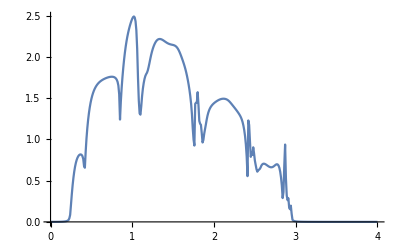

```mathematica
ListPlot[final2,Joined->True]
```

```mathematica
final=(m+n+o+p+q+r)/6
```

{{0.,0.000279629},{0.01,0.000200424},{0.02,0.000149387},{0.03,0.000133496},{0.04,0.000146033},{0.05,0.000189138},{0.06,0.000258025},{0.07,0.000359664},{0.08,0.000494784},{0.09,0.000664615},{0.1,0.000877613},{0.11,0.00113949},{0.12,0.00146275},{0.13,0.00186181},{0.14,0.00235806},{0.15,0.00298164},{0.16,0.00377667},{0.17,0.00481065},{0.18,0.00619142},{0.19,0.00810251},{0.2,0.0108851},{0.21,0.0152623},{0.22,0.0231489},{0.23,0.0428885},{0.24,0.0836227},{0.25,0.193702},{0.26,0.310704},{0.27,0.419038},{0.28,0.510829},{0.29,0.587163},{0.3,0.649205},{0.31,0.698542},{0.32,0.737044},{0.33,0.766521},{0.34,0.788471},{0.35,0.803963},{0.36,0.813574},{0.37,0.817275},{0.38,0.814065},{0.39,0.800791},{0.4,0.767557},{0.41,0.664549},{0.42,0.617735},{0.43,0.838629},{0.44,1.00171},{0.45,1.12798},{0.46,1.22877},{0.47,1.31053},{0.48,1.37752},{0.49,1.43284},{0.5,1.47889},{0.51,1.51754},{0.52,1.55025},{0.53,1.57816},{0.54,1.60216},{0.55,1.62293},{0.56,1.64099},{0.57,1.65676},{0.58,1.67056},{0.59,1.68265},{0.6,1.69327},{0.61,1.70263},{0.62,1.71091},{0.63,1.71829},{0.64,1.72492},{0.65,1.73093},{0.66,1.73642},{0.67,1.74147},{0.68,1.7461},{0.69,1.75034},{0.7,1.75418},{0.71,1.75759},{0.72,1.76051},{0.73,1.76286},{0.74,1.76455},{0.75,1.76542},{0.76,1.7653},{0.77,1.76389},{0.78,1.76082},{0.79,1.75544},{0.8,1.74671},{0.81,1.7327},{0.82,1.70945},{0.83,1.66703},{0.84,1.56948},{0.85,1.28845},{0.86,1.50086},{0.87,1.6523},{0.88,1.7745},{0.89,1.87929},{0.9,1.97115},{0.91,2.05195},{0.92,2.12274},{0.93,2.18444},{0.94,2.23816},{0.95,2.28515},{0.96,2.32659},{0.97,2.36354},{0.98,2.39673},{0.99,2.42649},{1.,2.45239},{1.01,2.47268},{1.02,2.4831},{1.03,2.47447},{1.04,2.42845},{1.05,2.3131},{1.06,2.08303},{1.07,1.7408},{1.08,1.47489},{1.09,1.33062},{1.1,1.31818},{1.11,1.42394},{1.12,1.56183},{1.13,1.65832},{1.14,1.7184},{1.15,1.75557},{1.16,1.77731},{1.17,1.78804},{1.18,1.79674},{1.19,1.81849},{1.2,1.85356},{1.21,1.89582},{1.22,1.94301},{1.23,1.98861},{1.24,2.02934},{1.25,2.06525},{1.26,2.09656},{1.27,2.12352},{1.28,2.14649},{1.29,2.1659},{1.3,2.18212},{1.31,2.19546},{1.32,2.20608},{1.33,2.21403},{1.34,2.21924},{1.35,2.22167},{1.36,2.22132},{1.37,2.21839},{1.38,2.21325},{1.39,2.20641},{1.4,2.19842},{1.41,2.18977},{1.42,2.1809},{1.43,2.17214},{1.44,2.16375},{1.45,2.1559},{1.46,2.14868},{1.47,2.14209},{1.48,2.13602},{1.49,2.1303},{1.5,2.12464},{1.51,2.11874},{1.52,2.11225},{1.53,2.1048},{1.54,2.09597},{1.55,2.08528},{1.56,2.0722},{1.57,2.0563},{1.58,2.03731},{1.59,2.01536},{1.6,1.99091},{1.61,1.96457},{1.62,1.93659},{1.63,1.90658},{1.64,1.8736},{1.65,1.83635},{1.66,1.79353},{1.67,1.74452},{1.68,1.69025},{1.69,1.63202},{1.7,1.5696},{1.71,1.49989},{1.72,1.41431},{1.73,1.2949},{1.74,1.1281},{1.75,0.977163},{1.76,0.909993},{1.77,1.57553},{1.78,1.54166},{1.79,1.58021},{1.8,1.58884},{1.81,1.41851},{1.82,1.08817},{1.83,1.03778},{1.84,0.968118},{1.85,1.01321},{1.86,0.950428},{1.87,1.00661},{1.88,1.08247},{1.89,1.15826},{1.9,1.22207},{1.91,1.27649},{1.92,1.31989},{1.93,1.35162},{1.94,1.37543},{1.95,1.39374},{1.96,1.4082},{1.97,1.41988},{1.98,1.42958},{1.99,1.43783},{2.,1.44504},{2.01,1.4515},{2.02,1.45742},{2.03,1.46294},{2.04,1.46812},{2.05,1.47296},{2.06,1.47742},{2.07,1.48138},{2.08,1.48471},{2.09,1.48725},{2.1,1.48882},{2.11,1.48928},{2.12,1.48853},{2.13,1.48652},{2.14,1.48324},{2.15,1.47868},{2.16,1.47281},{2.17,1.46564},{2.18,1.4573},{2.19,1.44807},{2.2,1.4383},{2.21,1.42831},{2.22,1.41833},{2.23,1.40848},{2.24,1.39878},{2.25,1.38917},{2.26,1.37952},{2.27,1.36962},{2.28,1.3592},{2.29,1.34793},{2.3,1.33553},{2.31,1.32169},{2.32,1.30582},{2.33,1.28649},{2.34,1.26115},{2.35,1.22704},{2.36,1.18189},{2.37,1.12273},{2.38,1.04434},{2.39,0.935499},{2.4,0.782495},{2.41,0.544067},{2.42,1.01912},{2.43,1.17641},{2.44,1.05955},{2.45,0.819149},{2.46,0.815181},{2.47,0.764331},{2.48,0.968416},{2.49,0.901461},{2.5,0.837752},{2.51,0.793034},{2.52,0.679755},{2.53,0.661214},{2.54,0.648449},{2.55,0.64051},{2.56,0.641366},{2.57,0.657515},{2.58,0.67555},{2.59,0.686397},{2.6,0.695711},{2.61,0.699746},{2.62,0.69964},{2.63,0.696437},{2.64,0.691107},{2.65,0.684558},{2.66,0.677633},{2.67,0.671115},{2.68,0.665722},{2.69,0.662096},{2.7,0.660781},{2.71,0.662179},{2.72,0.666473},{2.73,0.673497},{2.74,0.682583},{2.75,0.692433},{2.76,0.70119},{2.77,0.70665},{2.78,0.706169},{2.79,0.696011},{2.8,0.67096},{2.81,0.624952},{2.82,0.551613},{2.83,0.443583},{2.84,0.287652},{2.85,0.342573},{2.86,0.649521},{2.87,1.07387},{2.88,0.705236},{2.89,0.417887},{2.9,0.329121},{2.91,0.173246},{2.92,0.147464},{2.93,0.0481499},{2.94,0.249792},{2.95,0.0426954},{2.96,0.0178654},{2.97,0.013203},{2.98,0.00985427},{2.99,0.00771604},{3.,0.00621021},{3.01,0.0050953},{3.02,0.00424276},{3.03,0.00357523},{3.04,0.0030428},{3.05,0.00261168},{3.06,0.00225816},{3.07,0.00196512},{3.08,0.00171994},{3.09,0.00151309},{3.1,0.00133731},{3.11,0.00118694},{3.12,0.00105755},{3.13,0.000945598},{3.14,0.000848266},{3.15,0.000763258},{3.16,0.000688704},{3.17,0.000623065},{3.18,0.000565067},{3.19,0.00051365},{3.2,0.000467923},{3.21,0.000427138},{3.22,0.000390659},{3.23,0.000357949},{3.24,0.000328545},{3.25,0.000302052},{3.26,0.00027813},{3.27,0.000256483},{3.28,0.000236858},{3.29,0.000219031},{3.3,0.000202809},{3.31,0.000188021},{3.32,0.00017452},{3.33,0.000162173},{3.34,0.000150866},{3.35,0.000140495},{3.36,0.00013097},{3.37,0.000122211},{3.38,0.000114145},{3.39,0.000106708},{3.4,0.0000998439},{3.41,0.0000935007},{3.42,0.0000876324},{3.43,0.0000821978},{3.44,0.0000771597},{3.45,0.0000724844},{3.46,0.0000681417},{3.47,0.0000641041},{3.48,0.0000603468},{3.49,0.0000568474},{3.5,0.0000535853},{3.51,0.0000505419},{3.52,0.0000477004},{3.53,0.0000450452},{3.54,0.0000425623},{3.55,0.0000402388},{3.56,0.0000380629},{3.57,0.0000360238},{3.58,0.0000341117},{3.59,0.0000323174},{3.6,0.0000306325},{3.61,0.0000290495},{3.62,0.0000275613},{3.63,0.0000261613},{3.64,0.0000248453},{3.65,0.0000236091},{3.66,0.0000224441},{3.67,0.0000213458},{3.68,0.0000203104},{3.69,0.0000193331},{3.7,0.00001841},{3.71,0.0000175379},{3.72,0.0000167133},{3.73,0.0000159334},{3.74,0.0000151955},{3.75,0.0000144969},{3.76,0.0000138352},{3.77,0.0000132083},{3.78,0.000012614},{3.79,0.0000120504},{3.8,0.0000115157},{3.81,0.0000110083},{3.82,0.0000105264},{3.83,0.0000100688},{3.84,9.63395×10^-6},{3.85,9.22061×10^-6},{3.86,8.82756×10^-6},{3.87,8.45368×10^-6},{3.88,8.09791×10^-6},{3.89,7.75924×10^-6},{3.9,7.43676×10^-6},{3.91,7.12994×10^-6},{3.92,6.83782×10^-6},{3.93,6.56018×10^-6},{3.94,6.29718×10^-6},{3.95,6.04694×10^-6},{3.96,5.8082×10^-6},{3.97,5.58023×10^-6},{3.98,5.3625×10^-6},{3.99,5.15448×10^-6},{4.,4.95568×10^-6}}

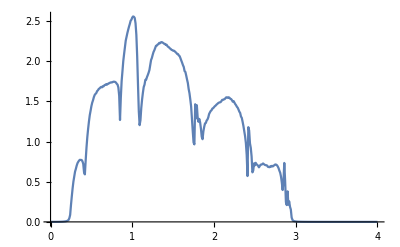

```mathematica
ListPlot[final,Joined->True]
```

```mathematica
Export["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis53.csv",final3]
```

/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis53.csv

```mathematica
Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis53.csv"]
```

{{0.,0.0000303359},{0.01,0.0000293404},{0.02,0.0000268116},{0.03,0.0000214571},{0.04,0.0000210531},{0.05,0.0000296004},{0.06,0.0000434305},{0.07,0.0000687331},{0.08,0.000107825},{0.09,0.000149756},{0.1,0.000205233},{0.11,0.000279147},{0.12,0.000362771},{0.13,0.000474888},{0.14,0.000614332},{0.15,0.000801013},{0.16,0.00104116},{0.17,0.00140854},{0.18,0.00184016},{0.19,0.00255585},{0.2,0.00363732},{0.21,0.00546067},{0.22,0.00920266},{0.23,0.02086},{0.24,0.345503},{0.25,0.637246},{0.26,0.761945},{0.27,0.831783},{0.28,0.871561},{0.29,0.900215},{0.3,0.917242},{0.31,0.930834},{0.32,0.938117},{0.33,0.943668},{0.34,0.946438},{0.35,0.948715},{0.36,0.948426},{0.37,0.945977},{0.38,0.941319},{0.39,0.929487},{0.4,0.907124},{0.41,0.824706},{0.42,1.08103},{0.43,1.46201},{0.44,1.63221},{0.45,1.72621},{0.46,1.78181},{0.47,1.8271},{0.48,1.85479},{0.49,1.87554},{0.5,1.89043},{0.51,1.9024},{0.52,1.91276},{0.53,1.91573},{0.54,1.9244},{0.55,1.92725},{0.56,1.93088},{0.57,1.93369},{0.58,1.93296},{0.59,1.93645},{0.6,1.93723},{0.61,1.93961},{0.62,1.93899},{0.63,1.94077},{0.64,1.93908},{0.65,1.94184},{0.66,1.94032},{0.67,1.94045},{0.68,1.94215},{0.69,1.94327},{0.7,1.94384},{0.71,1.94307},{0.72,1.94378},{0.73,1.94448},{0.74,1.94495},{0.75,1.94363},{0.76,1.94352},{0.77,1.94197},{0.78,1.94},{0.79,1.93707},{0.8,1.9337},{0.81,1.92698},{0.82,1.91585},{0.83,1.89445},{0.84,1.83073},{0.85,1.69738},{0.86,2.21493},{0.87,2.44649},{0.88,2.57734},{0.89,2.66067},{0.9,2.71799},{0.91,2.75545},{0.92,2.77717},{0.93,2.80435},{0.94,2.81996},{0.95,2.83335},{0.96,2.84345},{0.97,2.84802},{0.98,2.86179},{0.99,2.86989},{1.,2.87624},{1.01,2.87588},{1.02,2.83131},{1.03,2.49991},{1.04,1.74584},{1.05,2.37033},{1.06,2.50366},{1.07,2.41415},{1.08,2.33824},{1.09,2.51717},{1.1,2.61993},{1.11,2.68781},{1.12,2.72314},{1.13,2.74939},{1.14,2.76435},{1.15,2.78152},{1.16,2.79322},{1.17,2.80107},{1.18,2.81049},{1.19,2.81409},{1.2,2.82197},{1.21,2.8227},{1.22,2.82738},{1.23,2.83175},{1.24,2.83306},{1.25,2.83193},{1.26,2.83408},{1.27,2.83063},{1.28,2.83309},{1.29,2.83467},{1.3,2.83526},{1.31,2.83348},{1.32,2.83517},{1.33,2.83356},{1.34,2.83249},{1.35,2.83169},{1.36,2.8293},{1.37,2.8295},{1.38,2.82978},{1.39,2.83071},{1.4,2.83147},{1.41,2.83225},{1.42,2.83156},{1.43,2.83216},{1.44,2.83359},{1.45,2.83195},{1.46,2.83209},{1.47,2.83103},{1.48,2.82845},{1.49,2.82971},{1.5,2.82659},{1.51,2.82093},{1.52,2.81933},{1.53,2.81215},{1.54,2.80647},{1.55,2.79487},{1.56,2.78606},{1.57,2.77652},{1.58,2.76333},{1.59,2.75201},{1.6,2.73913},{1.61,2.72387},{1.62,2.72047},{1.63,2.70445},{1.64,2.69286},{1.65,2.6863},{1.66,2.67427},{1.67,2.66774},{1.68,2.65927},{1.69,2.64675},{1.7,2.63422},{1.71,2.61233},{1.72,2.57585},{1.73,2.52025},{1.74,2.44906},{1.75,2.29833},{1.76,1.79769},{1.77,1.1494},{1.78,2.4544},{1.79,2.01411},{1.8,1.59909},{1.81,1.67773},{1.82,1.80147},{1.83,1.8451},{1.84,1.86983},{1.85,1.88412},{1.86,1.89252},{1.87,1.89825},{1.88,1.90052},{1.89,1.9027},{1.9,1.90567},{1.91,1.90649},{1.92,1.90596},{1.93,1.90911},{1.94,1.90781},{1.95,1.91011},{1.96,1.91073},{1.97,1.91208},{1.98,1.91238},{1.99,1.91356},{2.,1.91543},{2.01,1.91705},{2.02,1.91797},{2.03,1.9184},{2.04,1.91997},{2.05,1.91901},{2.06,1.92134},{2.07,1.92001},{2.08,1.92156},{2.09,1.92076},{2.1,1.91996},{2.11,1.91791},{2.12,1.91833},{2.13,1.9157},{2.14,1.91283},{2.15,1.90854},{2.16,1.90891},{2.17,1.90523},{2.18,1.90274},{2.19,1.90084},{2.2,1.89496},{2.21,1.89306},{2.22,1.89182},{2.23,1.89095},{2.24,1.88973},{2.25,1.89226},{2.26,1.88956},{2.27,1.89046},{2.28,1.89001},{2.29,1.89112},{2.3,1.88702},{2.31,1.88244},{2.32,1.87329},{2.33,1.8643},{2.34,1.85207},{2.35,1.83279},{2.36,1.81241},{2.37,1.79048},{2.38,1.76627},{2.39,1.7323},{2.4,1.64944},{2.41,1.27357},{2.42,0.812343},{2.43,1.44208},{2.44,1.23675},{2.45,1.00114},{2.46,0.881926},{2.47,0.927078},{2.48,0.943058},{2.49,0.949436},{2.5,0.955283},{2.51,0.956793},{2.52,0.957444},{2.53,0.957639},{2.54,0.957526},{2.55,0.956048},{2.56,0.954208},{2.57,0.952488},{2.58,0.950609},{2.59,0.94913},{2.6,0.948492},{2.61,0.948082},{2.62,0.94862},{2.63,0.948466},{2.64,0.949917},{2.65,0.950571},{2.66,0.950314},{2.67,0.952612},{2.68,0.954648},{2.69,0.957538},{2.7,0.959829},{2.71,0.960934},{2.72,0.962285},{2.73,0.961082},{2.74,0.957526},{2.75,0.955049},{2.76,0.948232},{2.77,0.939308},{2.78,0.929608},{2.79,0.919351},{2.8,0.909146},{2.81,0.896706},{2.82,0.885788},{2.83,0.862534},{2.84,0.751213},{2.85,0.053209},{2.86,0.267304},{2.87,0.0955861},{2.88,0.0404004},{2.89,0.00821923},{2.9,0.00446633},{2.91,0.00294419},{2.92,0.00216925},{2.93,0.00162724},{2.94,0.00121172},{2.95,0.000968191},{2.96,0.000785073},{2.97,0.000646786},{2.98,0.000560901},{2.99,0.000473577},{3.,0.000386837},{3.01,0.000355171},{3.02,0.00028881},{3.03,0.000250652},{3.04,0.00022034},{3.05,0.000193363},{3.06,0.000178656},{3.07,0.000158706},{3.08,0.000135935},{3.09,0.000126679},{3.1,0.00010922},{3.11,0.0000983587},{3.12,0.0000950849},{3.13,0.0000838001},{3.14,0.0000728335},{3.15,0.0000692535},{3.16,0.0000605079},{3.17,0.0000577922},{3.18,0.0000529485},{3.19,0.0000500366},{3.2,0.0000428017},{3.21,0.0000423899},{3.22,0.0000379569},{3.23,0.0000350609},{3.24,0.0000310782},{3.25,0.0000300436},{3.26,0.000028734},{3.27,0.0000248212},{3.28,0.0000230624},{3.29,0.0000214777},{3.3,0.0000200047},{3.31,0.0000186647},{3.32,0.0000187561},{3.33,0.0000175313},{3.34,0.0000152323},{3.35,0.0000148696},{3.36,0.0000133626},{3.37,0.0000125392},{3.38,0.0000122667},{3.39,0.0000110517},{3.4,0.0000103908},{3.41,9.77647×10^-6},{3.42,9.20493×10^-6},{3.43,8.6927×10^-6},{3.44,8.19782×10^-6},{3.45,7.74544×10^-6},{3.46,7.62993×10^-6},{3.47,7.21622×10^-6},{3.48,6.55637×10^-6},{3.49,6.2151×10^-6},{3.5,6.12602×10^-6},{3.51,5.80688×10^-6},{3.52,5.29156×10^-6},{3.53,5.02639×10^-6},{3.54,5.13392×10^-6},{3.55,4.71242×10^-6},{3.56,4.30606×10^-6},{3.57,4.09789×10^-6},{3.58,3.89848×10^-6},{3.59,3.7077×10^-6},{3.6,3.53047×10^-6},{3.61,3.61706×10^-6},{3.62,3.20731×10^-6},{3.63,3.05575×10^-6},{3.64,2.91453×10^-6},{3.65,2.88704×10^-6},{3.66,2.65448×10^-6},{3.67,2.53475×10^-6},{3.68,2.42276×10^-6},{3.69,2.48531×10^-6},{3.7,2.21312×10^-6},{3.71,2.27116×10^-6},{3.72,2.02448×10^-6},{3.73,2.07831×10^-6},{3.74,1.85444×10^-6},{3.75,1.83886×10^-6},{3.76,1.70009×10^-6},{3.77,1.62978×10^-6},{3.78,1.5621×10^-6},{3.79,1.5497×10^-6},{3.8,1.43638×10^-6},{3.81,1.37738×10^-6},{3.82,1.36742×10^-6},{3.83,1.26879×10^-6},{3.84,1.30484×10^-6},{3.85,1.25297×10^-6},{3.86,1.12457×10^-6},{3.87,1.08069×10^-6},{3.88,1.11122×10^-6},{3.89,9.98417×10^-7},{3.9,1.02709×10^-6},{3.91,9.87819×10^-7},{3.92,9.17447×10^-7},{3.93,8.55767×10^-7},{3.94,8.23587×10^-7},{3.95,7.93319×10^-7},{3.96,7.6387×10^-7},{3.97,7.58687×10^-7},{3.98,7.09155×10^-7},{3.99,7.0432×10^-7},{4.,6.59153×10^-7}}

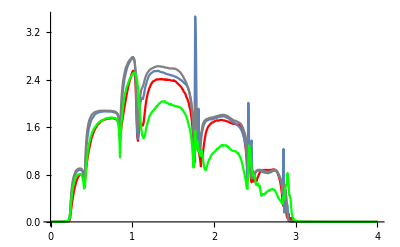

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"]],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"],PlotStyle->Gray],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis310.csv"],PlotStyle->Green],PlotRange->All]
```

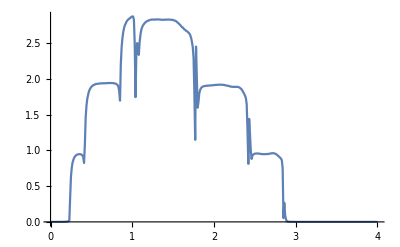

```mathematica
ListPlot[%188,Joined->True]
```

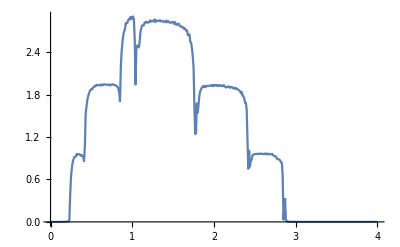
```mathematica
ListPlot[final,Joined->True]
-Graphics-
G[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[{{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ3+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ2+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ3+ω,-t},{0,0,0,0,0,-t,ⅈ δ+ω-ϵ}}]
Gnew[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Inverse[IdentityMatrix[7]-G[ω,δ,t,ϵ,ϵ2,ϵ3].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].G[ω,δ,t,ϵ,ϵ2,ϵ3]
Ilb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[IdentityMatrix[7]-Gnew[ω,δ,t,ϵ,ϵ2,ϵ3].T1[t].SR[ω,δ,t,ϵ].T1[t]].Gnew[ω,δ,t,ϵ,ϵ2,ϵ3];
Irb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Gnew[ω,δ,t,ϵ,ϵ2,ϵ3].T1[t]].SR[ω,δ,t,ϵ];
gddb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
grrb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Irb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Irb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
Gnonlocalb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= SR[ω,δ,t,ϵ].T1[t].Ilb$[ω,δ,t,ϵ,ϵ2,ϵ3];
GNONb$[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= Gnonlocalb$[ω,δ,t,ϵ,ϵ2,ϵ3]-ConjugateTranspose[Gnonlocalb$[ω,δ,t,ϵ,ϵ2,ϵ3]];
trb[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:= If[Abs[Tr[gddb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].grrb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1]-T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3]]]>3,3,Abs[Tr[gddb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].grrb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1]-T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3].T1[1].GNONb$[ω,δ,t,ϵ,ϵ2,ϵ3]]]]
f[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{final[[1;;150]][[;;,1]],(Table[{ω,trb[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- final[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.49}]/150]
ρ3[b_]:=Table[{b,a,f[b,a]},{a,Range[-1,1,0.05]}]
ρ3[0]
{{0,-1.,0.0026296908807774025},{0,-0.95,0.0022794549516705572},{0,-0.9,0.0019236310372092319},{0,-0.85,0.0017442489348258572},{0,-0.8,0.0014585090753985914},{0,-0.75,0.0013524760496679857},{0,-0.7,0.0012274668250561284},{0,-0.6499999999999999,0.0008753107302299807},{0,-0.6,0.000671705833148486},{0,-0.55,0.0006520756864331448},{0,-0.5,0.00046316287569217907},{0,-0.44999999999999996,0.00034652909575010087},{0,-0.3999999999999999,0.0002858594306199369},{0,-0.35,0.0005104213687328427},{0,-0.29999999999999993,0.00035595206505438894},{0,-0.25,0.0003544631179850149},{0,-0.19999999999999996,0.00041845023088064474},{0,-0.1499999999999999,0.0005024211302716524},{0,-0.09999999999999998,0.0005798638004293558},{0,-0.04999999999999993,0.0006291063337924044},{0,0.,0.0006373694415947198},{0,0.050000000000000044,0.0006051027838766944},{0,0.10000000000000009,0.0005433396889855207},{0,0.15000000000000013,0.00046647608294560894},{0,0.20000000000000018,0.0003866732148278415},{0,0.25,0.00031224575082528997},{0,0.30000000000000004,0.0002485099653012634},{0,0.3500000000000001,0.00019910503248029519},{0,0.40000000000000013,0.00016688970760072463},{0,0.4500000000000002,0.0001543437197449361},{0,0.5,0.0001636685804460779},{0,0.55,0.00019676380923426873},{0,0.6000000000000001,0.00025515810380276533},{0,0.6500000000000001,0.00033996768490063224},{0,0.7000000000000002,0.00045187576434947127},{0,0.75,0.0005911363099665516},{0,0.8,0.0007575970327162726},{0,0.8500000000000001,0.0009507359307038894},{0,0.9000000000000001,0.0011697063707837552},{0,0.9500000000000002,0.0014133866256576908},{0,1.,0.001680430691927205}}
rr3=Join[ρ3[-1],ρ3[-9/10],ρ3[-4/5],ρ3[-7/10],ρ3[-3/5],ρ3[-1/2],ρ3[-2/5],ρ3[-3/10],ρ3[-1/5],ρ3[-1/10],ρ3[0],ρ3[1/10],ρ3[1/5],ρ3[3/10],ρ3[2/5],ρ3[1/2],ρ3[3/5],ρ3[7/10],ρ3[4/5],ρ3[9/10],ρ3[1]]
{{-1,-1.,0.002711104145640912},{-1,-0.95,0.002583314975230046},{-1,-0.9,0.0022745154341491177},{-1,-0.85,0.002212425595908854},{-1,-0.8,0.0018476016637077699},{-1,-0.75,0.001822279892712517},{-1,-0.7,0.001745592436104233},{-1,-0.6499999999999999,0.0015802379535794294},{-1,-0.6,0.0015719372142352563},{-1,-0.55,0.0014772833086679625},{-1,-0.5,0.0013066959820135758},{-1,-0.44999999999999996,0.0013957701902950026},{-1,-0.3999999999999999,0.0015036327768480917},{-1,-0.35,0.0016202480914160168},{-1,-0.29999999999999993,0.0017403200471920982},{-1,-0.25,0.001820721359072222},{-1,-0.19999999999999996,0.0018425672988462954},{-1,-0.1499999999999999,0.001537686476762184},{-1,-0.09999999999999998,0.0014664140257564019},{-1,-0.04999999999999993,0.001525770512452944},{-1,0.,0.0016190827781516915},{-1,0.050000000000000044,0.00163277380737494},{-1,0.10000000000000009,0.0016479777511457896},{-1,0.15000000000000013,0.0017280463804142223},{-1,0.20000000000000018,0.0019103652136699231},{-1,0.25,0.002316053527075605},{-1,0.30000000000000004,0.002728902663176024},{-1,0.3500000000000001,0.0029587968559119833},{-1,0.40000000000000013,0.003218001656603736},{-1,0.4500000000000002,0.003501428670034191},{-1,0.5,0.0038053356896613744},{-1,0.55,0.004054296000329998},{-1,0.6000000000000001,0.004025543939753613},{-1,0.6500000000000001,0.004193487649031039},{-1,0.7000000000000002,0.004457240556722017},{-1,0.75,0.0047746448995605656},{-1,0.8,0.005127906759720265},{-1,0.8500000000000001,0.005508108102401826},{-1,0.9000000000000001,0.0059098952554884916},{-1,0.9500000000000002,0.006329478569168207},{-1,1.,0.006758045031357713},{-9/10,-1.,0.002540441838746996},{-9/10,-0.95,0.002211110960414962},{-9/10,-0.9,0.0018783359047987648},{-9/10,-0.85,0.0017746405870995043},{-9/10,-0.8,0.0015321664869187397},{-9/10,-0.75,0.0014120028774413922},{-9/10,-0.7,0.0013057284742279058},{-9/10,-0.6499999999999999,0.0011832787471601105},{-9/10,-0.6,0.0010792850461577132},{-9/10,-0.55,0.000999373788902769},{-9/10,-0.5,0.0009079743085032502},{-9/10,-0.44999999999999996,0.0010444656184762007},{-9/10,-0.3999999999999999,0.0016580471709243731},{-9/10,-0.35,0.0015770197717109168},{-9/10,-0.29999999999999993,0.001013745392886284},{-9/10,-0.25,0.0010127811515575685},{-9/10,-0.19999999999999996,0.0010217338477384681},{-9/10,-0.1499999999999999,0.001065981090085497},{-9/10,-0.09999999999999998,0.0010907579223450035},{-9/10,-0.04999999999999993,0.0011629618628803847},{-9/10,0.,0.0012846570801953185},{-9/10,0.050000000000000044,0.0012992607474046256},{-9/10,0.10000000000000009,0.0013835887303104463},{-9/10,0.15000000000000013,0.001664596116949358},{-9/10,0.20000000000000018,0.0020655526149887015},{-9/10,0.25,0.002213449471078744},{-9/10,0.30000000000000004,0.002398891864992156},{-9/10,0.3500000000000001,0.0026164060302314145},{-9/10,0.40000000000000013,0.002644201625303776},{-9/10,0.4500000000000002,0.002670109676130997},{-9/10,0.5,0.0028494555942899704},{-9/10,0.55,0.0030873812404001253},{-9/10,0.6000000000000001,0.003323185543591019},{-9/10,0.6500000000000001,0.0035957850556361777},{-9/10,0.7000000000000002,0.003894587539684164},{-9/10,0.75,0.004217177461502388},{-9/10,0.8,0.004561813981426988},{-9/10,0.8500000000000001,0.004926539183240102},{-9/10,0.9000000000000001,0.005309433968773756},{-9/10,0.9500000000000002,0.005708550094331948},{-9/10,1.,0.0061055290174205044},{-4/5,-1.,0.0023338276784465504},{-4/5,-0.95,0.0021479524294856093},{-4/5,-0.9,0.0017439302768481385},{-4/5,-0.85,0.0016377579959221632},{-4/5,-0.8,0.0011861421889944066},{-4/5,-0.75,0.0010283922286788523},{-4/5,-0.7,0.0009000619431086497},{-4/5,-0.6499999999999999,0.000889396860180042},{-4/5,-0.6,0.0008405044412765378},{-4/5,-0.55,0.0007634323688585255},{-4/5,-0.5,0.0007510637988725875},{-4/5,-0.44999999999999996,0.0007500049039181094},{-4/5,-0.3999999999999999,0.0007751340347677354},{-4/5,-0.35,0.0006495067605932659},{-4/5,-0.29999999999999993,0.0005568909734350073},{-4/5,-0.25,0.0006288135585500586},{-4/5,-0.19999999999999996,0.0006667560515975687},{-4/5,-0.1499999999999999,0.0007226385591567455},{-4/5,-0.09999999999999998,0.0007980642668421465},{-4/5,-0.04999999999999993,0.0009005560506137809},{-4/5,0.,0.0010527069686674753},{-4/5,0.050000000000000044,0.0012056386644843855},{-4/5,0.10000000000000009,0.0016309206503101307},{-4/5,0.15000000000000013,0.0016726269564329593},{-4/5,0.20000000000000018,0.0017514048888197483},{-4/5,0.25,0.0014890011409115108},{-4/5,0.30000000000000004,0.0014987627829683844},{-4/5,0.3500000000000001,0.0016331422166403714},{-4/5,0.40000000000000013,0.0018278594048360777},{-4/5,0.4500000000000002,0.002056415991778324},{-4/5,0.5,0.0022900732916606033},{-4/5,0.55,0.0025507974489047966},{-4/5,0.6000000000000001,0.0028254399296688167},{-4/5,0.6500000000000001,0.0030871763538931},{-4/5,0.7000000000000002,0.0033756545012149516},{-4/5,0.75,0.0036888370012938478},{-4/5,0.8,0.004022322117318057},{-4/5,0.8500000000000001,0.00436547574518593},{-4/5,0.9000000000000001,0.004723206723466763},{-4/5,0.9500000000000002,0.005081005416726738},{-4/5,1.,0.005459372721405715},{-7/10,-1.,0.0023704569558033453},{-7/10,-0.95,0.002090199961895888},{-7/10,-0.9,0.0016703872076099151},{-7/10,-0.85,0.0015194702830359373},{-7/10,-0.8,0.0010535576334333911},{-7/10,-0.75,0.0008304084021112063},{-7/10,-0.7,0.0006746176138608534},{-7/10,-0.6499999999999999,0.0006221036419581638},{-7/10,-0.6,0.0006012320908126795},{-7/10,-0.55,0.0005246544981764359},{-7/10,-0.5,0.0005372770637306868},{-7/10,-0.44999999999999996,0.0005406032587173595},{-7/10,-0.3999999999999999,0.0006381528769806549},{-7/10,-0.35,0.0005858911525102732},{-7/10,-0.29999999999999993,0.0005808478303520719},{-7/10,-0.25,0.0005812184516832114},{-7/10,-0.19999999999999996,0.0006030411892900315},{-7/10,-0.1499999999999999,0.0006388438705756911},{-7/10,-0.09999999999999998,0.0006960543256619713},{-7/10,-0.04999999999999993,0.0007822124256266147},{-7/10,0.,0.0009981766117078965},{-7/10,0.050000000000000044,0.0010628038034987853},{-7/10,0.10000000000000009,0.0008987200420012239},{-7/10,0.15000000000000013,0.0008402336353133035},{-7/10,0.20000000000000018,0.0008723651257230414},{-7/10,0.25,0.0009678603604080915},{-7/10,0.30000000000000004,0.0011110727903825587},{-7/10,0.3500000000000001,0.001289581222370518},{-7/10,0.40000000000000013,0.0014931485567662842},{-7/10,0.4500000000000002,0.0016894901929311505},{-7/10,0.5,0.0019049368832750313},{-7/10,0.55,0.002143873471936296},{-7/10,0.6000000000000001,0.0024056175442120397},{-7/10,0.6500000000000001,0.0026893456253263078},{-7/10,0.7000000000000002,0.0029575170816492336},{-7/10,0.75,0.0032436034915115765},{-7/10,0.8,0.0035286468169796726},{-7/10,0.8500000000000001,0.003826868990315671},{-7/10,0.9000000000000001,0.004141572990292288},{-7/10,0.9500000000000002,0.004478944944638608},{-7/10,1.,0.0048364616014604025},{-3/5,-1.,0.00235260789932262},{-3/5,-0.95,0.0020640597314176856},{-3/5,-0.9,0.0015858880643562234},{-3/5,-0.85,0.001540993435729844},{-3/5,-0.8,0.0011128088104345785},{-3/5,-0.75,0.0008586612915576187},{-3/5,-0.7,0.0007053377821828594},{-3/5,-0.6499999999999999,0.00048400300925446963},{-3/5,-0.6,0.00033709276079281497},{-3/5,-0.55,0.0003129582827858489},{-3/5,-0.5,0.00030126289037412735},{-3/5,-0.44999999999999996,0.000286227043064681},{-3/5,-0.3999999999999999,0.00028745152687547016},{-3/5,-0.35,0.0002717562942509955},{-3/5,-0.29999999999999993,0.00031477042293209687},{-3/5,-0.25,0.00033883400493406703},{-3/5,-0.19999999999999996,0.00037833357591514187},{-3/5,-0.1499999999999999,0.00042449784207061406},{-3/5,-0.09999999999999998,0.0004898840829049233},{-3/5,-0.04999999999999993,0.0005634997812571755},{-3/5,0.,0.000644606789115516},{-3/5,0.050000000000000044,0.0007391043027505619},{-3/5,0.10000000000000009,0.0006772982711818098},{-3/5,0.15000000000000013,0.0006558822791274639},{-3/5,0.20000000000000018,0.0006831043861262596},{-3/5,0.25,0.000758946520248213},{-3/5,0.30000000000000004,0.0008761762915454525},{-3/5,0.3500000000000001,0.0010242045152636069},{-3/5,0.40000000000000013,0.0011932826270009413},{-3/5,0.4500000000000002,0.0013481528233653655},{-3/5,0.5,0.001526345021047382},{-3/5,0.55,0.0017094147519223296},{-3/5,0.6000000000000001,0.0019104946375287633},{-3/5,0.6500000000000001,0.002141544600545},{-3/5,0.7000000000000002,0.0023997737365731974},{-3/5,0.75,0.0026828998086394773},{-3/5,0.8,0.0029564185139919585},{-3/5,0.8500000000000001,0.00323568189836298},{-3/5,0.9000000000000001,0.0035392536964574976},{-3/5,0.9500000000000002,0.0038652190105713177},{-3/5,1.,0.004211518863509783},{-1/2,-1.,0.002156645211610254},{-1/2,-0.95,0.0018635476605400841},{-1/2,-0.9,0.0014843479985835878},{-1/2,-0.85,0.0014713733333784605},{-1/2,-0.8,0.0010879143414386386},{-1/2,-0.75,0.0007466569203998251},{-1/2,-0.7,0.0007023116301914631},{-1/2,-0.6499999999999999,0.0004967087751148677},{-1/2,-0.6,0.00035221307636771444},{-1/2,-0.55,0.00022489835171968838},{-1/2,-0.5,0.0001649988171110157},{-1/2,-0.44999999999999996,0.0001474677700739302},{-1/2,-0.3999999999999999,0.00019094963364199802},{-1/2,-0.35,0.00023570340093855067},{-1/2,-0.29999999999999993,0.00030085109172418905},{-1/2,-0.25,0.00032420446080197804},{-1/2,-0.19999999999999996,0.00035300231219183835},{-1/2,-0.1499999999999999,0.00037464232470694},{-1/2,-0.09999999999999998,0.0004080130534484584},{-1/2,-0.04999999999999993,0.00045158457875358135},{-1/2,0.,0.0005137833105025324},{-1/2,0.050000000000000044,0.0006077272446922364},{-1/2,0.10000000000000009,0.0005980068448808071},{-1/2,0.15000000000000013,0.0005361992079752193},{-1/2,0.20000000000000018,0.0005133882459140154},{-1/2,0.25,0.00051438920762183},{-1/2,0.30000000000000004,0.0005731398611637379},{-1/2,0.3500000000000001,0.0006714313050796515},{-1/2,0.40000000000000013,0.0007958461444529415},{-1/2,0.4500000000000002,0.0009388059152228901},{-1/2,0.5,0.0010902946360199282},{-1/2,0.55,0.0012620875749627585},{-1/2,0.6000000000000001,0.0014588788318529154},{-1/2,0.6500000000000001,0.0016789486584550223},{-1/2,0.7000000000000002,0.0019133014265761102},{-1/2,0.75,0.0021697375063911275},{-1/2,0.8,0.0024483545831745146},{-1/2,0.8500000000000001,0.00274867795392126},{-1/2,0.9000000000000001,0.003069779753613244},{-1/2,0.9500000000000002,0.0033773149954645734},{-1/2,1.,0.003696825314593746},{-2/5,-1.,0.0023538722337751745},{-2/5,-0.95,0.002106008471189261},{-2/5,-0.9,0.0022534898096246312},{-2/5,-0.85,0.0017682224520068775},{-2/5,-0.8,0.0011692820161619381},{-2/5,-0.75,0.000919359534089862},{-2/5,-0.7,0.0008337276158048295},{-2/5,-0.6499999999999999,0.0006116373806542767},{-2/5,-0.6,0.00035126042228111724},{-2/5,-0.55,0.00036856905287941305},{-2/5,-0.5,0.00019061401671170423},{-2/5,-0.44999999999999996,0.00014415750634916042},{-2/5,-0.3999999999999999,0.0001799300607877201},{-2/5,-0.35,0.00039823429711494893},{-2/5,-0.29999999999999993,0.000318933846298778},{-2/5,-0.25,0.0002568486898171772},{-2/5,-0.19999999999999996,0.00024763478620458895},{-2/5,-0.1499999999999999,0.0002730229966721503},{-2/5,-0.09999999999999998,0.0003027135397237314},{-2/5,-0.04999999999999993,0.0003326688902260132},{-2/5,0.,0.0003708446624446727},{-2/5,0.050000000000000044,0.0004314311870756018},{-2/5,0.10000000000000009,0.0005287403055086911},{-2/5,0.15000000000000013,0.00045025649000892076},{-2/5,0.20000000000000018,0.0003873962793909022},{-2/5,0.25,0.0003730805022760936},{-2/5,0.30000000000000004,0.00039940601855498425},{-2/5,0.3500000000000001,0.0004559916150095907},{-2/5,0.40000000000000013,0.0005349760984705677},{-2/5,0.4500000000000002,0.0006325929610876115},{-2/5,0.5,0.0007483652249596917},{-2/5,0.55,0.0008835779952987484},{-2/5,0.6000000000000001,0.0010400152326192082},{-2/5,0.6500000000000001,0.001219218682028116},{-2/5,0.7000000000000002,0.001422170304652226},{-2/5,0.75,0.0016492264216031829},{-2/5,0.8,0.0019001714671251391},{-2/5,0.8500000000000001,0.0021743145886758933},{-2/5,0.9000000000000001,0.0024705919992125958},{-2/5,0.9500000000000002,0.0027876602116051375},{-2/5,1.,0.0031239758905163353},{-3/10,-1.,0.002661441973971957},{-3/10,-0.95,0.002330335293881769},{-3/10,-0.9,0.0016212507439771645},{-3/10,-0.85,0.0013832089511828692},{-3/10,-0.8,0.0009350743151119465},{-3/10,-0.75,0.0008402915248197977},{-3/10,-0.7,0.0007586640261743327},{-3/10,-0.6499999999999999,0.0005667374422878433},{-3/10,-0.6,0.0003465528950866727},{-3/10,-0.55,0.0004242782000991703},{-3/10,-0.5,0.0002728166410233643},{-3/10,-0.44999999999999996,0.0002663494615211791},{-3/10,-0.3999999999999999,0.00028868822434977953},{-3/10,-0.35,0.00029709275386256145},{-3/10,-0.29999999999999993,0.0002699357379557023},{-3/10,-0.25,0.0002916521768501497},{-3/10,-0.19999999999999996,0.00033074702662099257},{-3/10,-0.1499999999999999,0.0003681971564245421},{-3/10,-0.09999999999999998,0.00039499536157900814},{-3/10,-0.04999999999999993,0.00040911104126653054},{-3/10,0.,0.00041694859829894017},{-3/10,0.050000000000000044,0.0004323702053282149},{-3/10,0.10000000000000009,0.00047099382198863765},{-3/10,0.15000000000000013,0.0005417083866037767},{-3/10,0.20000000000000018,0.0005017028209905936},{-3/10,0.25,0.00042505935457636787},{-3/10,0.30000000000000004,0.0003899656256783181},{-3/10,0.3500000000000001,0.00038933903206846366},{-3/10,0.40000000000000013,0.00041754792592492874},{-3/10,0.4500000000000002,0.0004715915016157387},{-3/10,0.5,0.0005505520864201815},{-3/10,0.55,0.000654632534961612},{-3/10,0.6000000000000001,0.0007843910140338964},{-3/10,0.6500000000000001,0.0009402892243322435},{-3/10,0.7000000000000002,0.001122481372642451},{-3/10,0.75,0.0013307472055376077},{-3/10,0.8,0.0015502933317332345},{-3/10,0.8500000000000001,0.0017919338568518936},{-3/10,0.9000000000000001,0.002057439886165404},{-3/10,0.9500000000000002,0.002345372329154407},{-3/10,1.,0.00265413357858814},{-1/5,-1.,0.0028153769351222913},{-1/5,-0.95,0.00201660356696707},{-1/5,-0.9,0.0016535172021119155},{-1/5,-0.85,0.0014246799374875011},{-1/5,-0.8,0.0010460485472566028},{-1/5,-0.75,0.0009046274222065763},{-1/5,-0.7,0.0007899030130977172},{-1/5,-0.6499999999999999,0.0005495072631153385},{-1/5,-0.6,0.0004012160941229078},{-1/5,-0.55,0.0004604633671490798},{-1/5,-0.5,0.0003124690543211193},{-1/5,-0.44999999999999996,0.00026781600801312265},{-1/5,-0.3999999999999999,0.00019480177364569122},{-1/5,-0.35,0.0003925612874376709},{-1/5,-0.29999999999999993,0.00030733569086130057},{-1/5,-0.25,0.0003533649810474235},{-1/5,-0.19999999999999996,0.00041472814275186166},{-1/5,-0.1499999999999999,0.000463193135197762},{-1/5,-0.09999999999999998,0.0004896870916822891},{-1/5,-0.04999999999999993,0.0004894770964012872},{-1/5,0.,0.0004651613590532941},{-1/5,0.050000000000000044,0.0004285314804053332},{-1/5,0.10000000000000009,0.0003962047614075206},{-1/5,0.15000000000000013,0.00038113888782725924},{-1/5,0.20000000000000018,0.0003873077656665081},{-1/5,0.25,0.00041134384685073303},{-1/5,0.30000000000000004,0.0004317694713513143},{-1/5,0.3500000000000001,0.000364623047437774},{-1/5,0.40000000000000013,0.00033192319505451966},{-1/5,0.4500000000000002,0.0003311473829040195},{-1/5,0.5,0.0003608651591047838},{-1/5,0.55,0.00042038132818706563},{-1/5,0.6000000000000001,0.0005093482914388747},{-1/5,0.6500000000000001,0.0006274815652852632},{-1/5,0.7000000000000002,0.0007743864854342826},{-1/5,0.75,0.0009494687262404524},{-1/5,0.8,0.0011519001235964926},{-1/5,0.8500000000000001,0.0013806186134165035},{-1/5,0.9000000000000001,0.0016343482014690598},{-1/5,0.9500000000000002,0.0019116299319761048},{-1/5,1.,0.0022108580691638504},{-1/10,-1.,0.002495395719901828},{-1/10,-0.95,0.0021028688325253134},{-1/10,-0.9,0.0017680470949979126},{-1/10,-0.85,0.0015246993236951738},{-1/10,-0.8,0.0011883115381994857},{-1/10,-0.75,0.0010248092498972674},{-1/10,-0.7,0.0008870212441319433},{-1/10,-0.6499999999999999,0.0006119068242427822},{-1/10,-0.6,0.0005005074296649565},{-1/10,-0.55,0.0005160880134085179},{-1/10,-0.5,0.00034862590781178454},{-1/10,-0.44999999999999996,0.00028541520714769767},{-1/10,-0.3999999999999999,0.00021903058842544413},{-1/10,-0.35,0.0004600049961255017},{-1/10,-0.29999999999999993,0.00033890523543696265},{-1/10,-0.25,0.0003736459964148222},{-1/10,-0.19999999999999996,0.00045261421754302987},{-1/10,-0.1499999999999999,0.0005309750162161068},{-1/10,-0.09999999999999998,0.0005880497720391454},{-1/10,-0.04999999999999993,0.0006097442401947161},{-1/10,0.,0.0005910740294040663},{-1/10,0.050000000000000044,0.0005394320721339301},{-1/10,0.10000000000000009,0.00047096743949634517},{-1/10,0.15000000000000013,0.00040200769945887153},{-1/10,0.20000000000000018,0.0003430106896643164},{-1/10,0.25,0.0002983048313825135},{-1/10,0.30000000000000004,0.000268942008709972},{-1/10,0.3500000000000001,0.00025529283740680043},{-1/10,0.40000000000000013,0.0002582413371131713},{-1/10,0.4500000000000002,0.0002793287625920091},{-1/10,0.5,0.00032045119451973644},{-1/10,0.55,0.00038352089501250957},{-1/10,0.6000000000000001,0.0004702101215533978},{-1/10,0.6500000000000001,0.0005594280318760483},{-1/10,0.7000000000000002,0.0006652776958765331},{-1/10,0.75,0.0008015020249468218},{-1/10,0.8,0.0009671752527535142},{-1/10,0.8500000000000001,0.0011611567652146703},{-1/10,0.9000000000000001,0.0013821056141020836},{-1/10,0.9500000000000002,0.00162850608832511},{-1/10,1.,0.0018986995816416487},{0,-1.,0.0026296908807774025},{0,-0.95,0.0022794549516705572},{0,-0.9,0.0019236310372092319},{0,-0.85,0.0017442489348258572},{0,-0.8,0.0014585090753985914},{0,-0.75,0.0013524760496679857},{0,-0.7,0.0012274668250561284},{0,-0.6499999999999999,0.0008753107302299807},{0,-0.6,0.000671705833148486},{0,-0.55,0.0006520756864331448},{0,-0.5,0.00046316287569217907},{0,-0.44999999999999996,0.00034652909575010087},{0,-0.3999999999999999,0.0002858594306199369},{0,-0.35,0.0005104213687328427},{0,-0.29999999999999993,0.00035595206505438894},{0,-0.25,0.0003544631179850149},{0,-0.19999999999999996,0.00041845023088064474},{0,-0.1499999999999999,0.0005024211302716524},{0,-0.09999999999999998,0.0005798638004293558},{0,-0.04999999999999993,0.0006291063337924044},{0,0.,0.0006373694415947198},{0,0.050000000000000044,0.0006051027838766944},{0,0.10000000000000009,0.0005433396889855207},{0,0.15000000000000013,0.00046647608294560894},{0,0.20000000000000018,0.0003866732148278415},{0,0.25,0.00031224575082528997},{0,0.30000000000000004,0.0002485099653012634},{0,0.3500000000000001,0.00019910503248029519},{0,0.40000000000000013,0.00016688970760072463},{0,0.4500000000000002,0.0001543437197449361},{0,0.5,0.0001636685804460779},{0,0.55,0.00019676380923426873},{0,0.6000000000000001,0.00025515810380276533},{0,0.6500000000000001,0.00033996768490063224},{0,0.7000000000000002,0.00045187576434947127},{0,0.75,0.0005911363099665516},{0,0.8,0.0007575970327162726},{0,0.8500000000000001,0.0009507359307038894},{0,0.9000000000000001,0.0011697063707837552},{0,0.9500000000000002,0.0014133866256576908},{0,1.,0.001680430691927205},{1/10,-1.,0.0027761328621702633},{1/10,-0.95,0.0023738807244459885},{1/10,-0.9,0.0020864965348122},{1/10,-0.85,0.0020379762250727585},{1/10,-0.8,0.0020587310169058455},{1/10,-0.75,0.001811258981111664},{1/10,-0.7,0.0011261595721763736},{1/10,-0.6499999999999999,0.0008529609842251416},{1/10,-0.6,0.0007138662480997631},{1/10,-0.55,0.000713161294696251},{1/10,-0.5,0.0005598800218965445},{1/10,-0.44999999999999996,0.000417513698346431},{1/10,-0.3999999999999999,0.0004752701464660574},{1/10,-0.35,0.0006483346363168595},{1/10,-0.29999999999999993,0.00043683829707130223},{1/10,-0.25,0.0003663313681136016},{1/10,-0.19999999999999996,0.00037289053473947944},{1/10,-0.1499999999999999,0.00041951621734233774},{1/10,-0.09999999999999998,0.000481892354061882},{1/10,-0.04999999999999993,0.0005365148460456056},{1/10,0.,0.0005654178277522036},{1/10,0.050000000000000044,0.0005612634094250719},{1/10,0.10000000000000009,0.0005268569771248841},{1/10,0.15000000000000013,0.00047064646768144513},{1/10,0.20000000000000018,0.00040231996962548667},{1/10,0.25,0.00033048690704388163},{1/10,0.30000000000000004,0.0002621152500613995},{1/10,0.3500000000000001,0.00020275711540436998},{1/10,0.40000000000000013,0.00015691412605865632},{1/10,0.4500000000000002,0.00012830388624332647},{1/10,0.5,0.00012000333540627842},{1/10,0.55,0.00013451289100730365},{1/10,0.6000000000000001,0.0001737838547620244},{1/10,0.6500000000000001,0.00023924254263411985},{1/10,0.7000000000000002,0.0003318025962634134},{1/10,0.75,0.0004518975396399253},{1/10,0.8,0.000599518985835718},{1/10,0.8500000000000001,0.0007742621436516402},{1/10,0.9000000000000001,0.0009753762513300953},{1/10,0.9500000000000002,0.00120181746069517},{1/10,1.,0.0014523019271783818},{1/5,-1.,0.0031155719126102098},{1/5,-0.95,0.0029327100399475243},{1/5,-0.9,0.0028427541120762856},{1/5,-0.85,0.0026133451517133684},{1/5,-0.8,0.002255556168541851},{1/5,-0.75,0.00147067304105984},{1/5,-0.7,0.0011590573498375034},{1/5,-0.6499999999999999,0.0009519724242949532},{1/5,-0.6,0.0007790321589558319},{1/5,-0.55,0.0007250861463183174},{1/5,-0.5,0.000534124437301857},{1/5,-0.44999999999999996,0.00033365721906803623},{1/5,-0.3999999999999999,0.00036475271677986824},{1/5,-0.35,0.000580579819664068},{1/5,-0.29999999999999993,0.0005011440642331344},{1/5,-0.25,0.00048304221662735417},{1/5,-0.19999999999999996,0.000402238492678755},{1/5,-0.1499999999999999,0.0003783823568830426},{1/5,-0.09999999999999998,0.0003926381666426434},{1/5,-0.04999999999999993,0.00042285723907509106},{1/5,0.,0.0004486023733944483},{1/5,0.050000000000000044,0.000456806963438504},{1/5,0.10000000000000009,0.0004431627443755302},{1/5,0.15000000000000013,0.0004098627446166289},{1/5,0.20000000000000018,0.0003624240648166034},{1/5,0.25,0.00030736366568542503},{1/5,0.30000000000000004,0.0002510187923953856},{1/5,0.3500000000000001,0.00019911803266815467},{1/5,0.40000000000000013,0.00015668866733376107},{1/5,0.4500000000000002,0.00012806852757781835},{1/5,0.5,0.00011693301435558755},{1/5,0.55,0.00012631752175630185},{1/5,0.6000000000000001,0.00015863628230579363},{1/5,0.6500000000000001,0.00021570514030566632},{1/5,0.7000000000000002,0.00029877019281525835},{1/5,0.75,0.0004085526188508675},{1/5,0.8,0.0005452868911204254},{1/5,0.8500000000000001,0.0007087750877692826},{1/5,0.9000000000000001,0.0008984422341675806},{1/5,0.9500000000000002,0.0011133931626591692},{1/5,1.,0.0013524688930716198},{3/10,-1.,0.0039895521345169474},{3/10,-0.95,0.0035795872780443935},{3/10,-0.9,0.003230940609686042},{3/10,-0.85,0.0028719767230970888},{3/10,-0.8,0.002058796245031819},{3/10,-0.75,0.0016851551551910731},{3/10,-0.7,0.001439779463426588},{3/10,-0.6499999999999999,0.001226578729018956},{3/10,-0.6,0.0010160437165918329},{3/10,-0.55,0.0009100403677045788},{3/10,-0.5,0.0006257233292085867},{3/10,-0.44999999999999996,0.00044203431284707415},{3/10,-0.3999999999999999,0.00041341004566509493},{3/10,-0.35,0.0005394909815315658},{3/10,-0.29999999999999993,0.00042195003710310074},{3/10,-0.25,0.00040021836193069373},{3/10,-0.19999999999999996,0.00048159182361716846},{3/10,-0.1499999999999999,0.0003942826520010433},{3/10,-0.09999999999999998,0.00035075038690194076},{3/10,-0.04999999999999993,0.0003413570125825838},{3/10,0.,0.00034570604649105963},{3/10,0.050000000000000044,0.0003483511470075013},{3/10,0.10000000000000009,0.0003408976270065077},{3/10,0.15000000000000013,0.0003210709112871994},{3/10,0.20000000000000018,0.00029057863107610706},{3/10,0.25,0.00025319737771208224},{3/10,0.30000000000000004,0.00021354022592342682},{3/10,0.3500000000000001,0.00017638522590115446},{3/10,0.40000000000000013,0.00014632768809785414},{3/10,0.4500000000000002,0.00012759279580298294},{3/10,0.5,0.00012392734884233546},{3/10,0.55,0.00013853706041324035},{3/10,0.6000000000000001,0.0001740550696520772},{3/10,0.6500000000000001,0.0002325351138125887},{3/10,0.7000000000000002,0.00031546353222505215},{3/10,0.75,0.00042378780267467517},{3/10,0.8,0.0005579550299808343},{3/10,0.8500000000000001,0.0007179672533228102},{3/10,0.9000000000000001,0.0009034289023674392},{3/10,0.9500000000000002,0.001113605710412534},{3/10,1.,0.0013474814730706072},{2/5,-1.,0.004491355580720677},{2/5,-0.95,0.0040695018170856245},{2/5,-0.9,0.0035040938562063513},{2/5,-0.85,0.0028884232658599918},{2/5,-0.8,0.002392034274036894},{2/5,-0.75,0.0020746871343826872},{2/5,-0.7,0.0018179072749044095},{2/5,-0.6499999999999999,0.0015801170824091325},{2/5,-0.6,0.0013332319062422946},{2/5,-0.55,0.0011656122055069957},{2/5,-0.5,0.0008476474229448236},{2/5,-0.44999999999999996,0.0006433436835022612},{2/5,-0.3999999999999999,0.0005551811609964618},{2/5,-0.35,0.0006051677207366477},{2/5,-0.29999999999999993,0.00045287759331736266},{2/5,-0.25,0.0003707615718577256},{2/5,-0.19999999999999996,0.0003906401015624126},{2/5,-0.1499999999999999,0.00043895889352149045},{2/5,-0.09999999999999998,0.0003466919166261867},{2/5,-0.04999999999999993,0.0002985047173590477},{2/5,0.,0.00027587988911427074},{2/5,0.050000000000000044,0.0002636610731552292},{2/5,0.10000000000000009,0.0002520949996460012},{2/5,0.15000000000000013,0.00023656078462276002},{2/5,0.20000000000000018,0.0002161952914496236},{2/5,0.25,0.0001924830551962711},{2/5,0.30000000000000004,0.00016822975772406545},{2/5,0.3500000000000001,0.0001469026187025497},{2/5,0.40000000000000013,0.00013220701269440414},{2/5,0.4500000000000002,0.00012780226901119631},{2/5,0.5,0.00013710542137315417},{2/5,0.55,0.0001631582968364922},{2/5,0.6000000000000001,0.00020854364107420422},{2/5,0.6500000000000001,0.0002753404309592637},{2/5,0.7000000000000002,0.00036510985242254256},{2/5,0.75,0.00047890504814410346},{2/5,0.8,0.000617297691258852},{2/5,0.8500000000000001,0.0007804177599703207},{2/5,0.9000000000000001,0.0009679993693839317},{2/5,0.9500000000000002,0.0011794383650819164},{2/5,1.,0.0014138408118332222},{1/2,-1.,0.004955354150029686},{1/2,-0.95,0.004265270403115202},{1/2,-0.9,0.0036377205831271096},{1/2,-0.85,0.0032555669657465913},{1/2,-0.8,0.002791317447317363},{1/2,-0.75,0.0024579016132683824},{1/2,-0.7,0.002178136020800444},{1/2,-0.6499999999999999,0.0019123781138991795},{1/2,-0.6,0.0016274754604228136},{1/2,-0.55,0.001373896192182556},{1/2,-0.5,0.0010947582297721958},{1/2,-0.44999999999999996,0.0008682216083706905},{1/2,-0.3999999999999999,0.0007305844452936033},{1/2,-0.35,0.0007224206879408338},{1/2,-0.29999999999999993,0.0005458592800544754},{1/2,-0.25,0.000417895949157945},{1/2,-0.19999999999999996,0.0003875838483615544},{1/2,-0.1499999999999999,0.0004262116020498987},{1/2,-0.09999999999999998,0.000374842509668782},{1/2,-0.04999999999999993,0.0002942001820564012},{1/2,0.,0.0002456149040211681},{1/2,0.050000000000000044,0.00021558354137266966},{1/2,0.10000000000000009,0.00019462787303797132},{1/2,0.15000000000000013,0.00017732048582920915},{1/2,0.20000000000000018,0.00016139635303137034},{1/2,0.25,0.0001467721749050831},{1/2,0.30000000000000004,0.0001347890096199641},{1/2,0.3500000000000001,0.00012767684962071248},{1/2,0.40000000000000013,0.00012816139841860674},{1/2,0.4500000000000002,0.00013916226906445935},{1/2,0.5,0.00016356058497585886},{1/2,0.55,0.0002040267559910253},{1/2,0.6000000000000001,0.00026290066847688885},{1/2,0.6500000000000001,0.0003421165002479386},{1/2,0.7000000000000002,0.00044316391297777926},{1/2,0.75,0.0005670781467653702},{1/2,0.8,0.0007144520398529662},{1/2,0.8500000000000001,0.000885463905280202},{1/2,0.9000000000000001,0.0010799157508348675},{1/2,0.9500000000000002,0.0012972786651738177},{1/2,1.,0.0015367399980063705},{3/5,-1.,0.005082146776666856},{3/5,-0.95,0.004429062941612544},{3/5,-0.9,0.0039637064464200554},{3/5,-0.85,0.003621335362282842},{3/5,-0.8,0.0031903574379256736},{3/5,-0.75,0.002877753682729811},{3/5,-0.7,0.0025745969921840747},{3/5,-0.6499999999999999,0.002280008428374425},{3/5,-0.6,0.001916622217265445},{3/5,-0.55,0.0016459845574382835},{3/5,-0.5,0.0013641724793179003},{3/5,-0.44999999999999996,0.0011056383076043078},{3/5,-0.3999999999999999,0.0009298559016633472},{3/5,-0.35,0.000878103921943552},{3/5,-0.29999999999999993,0.0006853676416655425},{3/5,-0.25,0.0005224319184261547},{3/5,-0.19999999999999996,0.0004514160174316095},{3/5,-0.1499999999999999,0.00044671143707428635},{3/5,-0.09999999999999998,0.0004378068196772552},{3/5,-0.04999999999999993,0.0003306809517701365},{3/5,0.,0.0002588566239913338},{3/5,0.050000000000000044,0.0002108872083797237},{3/5,0.10000000000000009,0.000178309613403051},{3/5,0.15000000000000013,0.00015574783440732017},{3/5,0.20000000000000018,0.00014032689892698355},{3/5,0.25,0.00013101479265862376},{3/5,0.30000000000000004,0.00012809669588953338},{3/5,0.3500000000000001,0.00013278958037338926},{3/5,0.40000000000000013,0.00014692532586598243},{3/5,0.4500000000000002,0.0001726770998346291},{3/5,0.5,0.00021232696368262888},{3/5,0.55,0.00026808031173131575},{3/5,0.6000000000000001,0.0003419277110964703},{3/5,0.6500000000000001,0.0004355506638325274},{3/5,0.7000000000000002,0.0005502649524906619},{3/5,0.75,0.0006869948132573722},{3/5,0.8,0.000846271166406142},{3/5,0.8500000000000001,0.0010282480443125133},{3/5,0.9000000000000001,0.0012327319250424237},{3/5,0.9500000000000002,0.001459219390401899},{3/5,1.,0.0017069392188313582},{7/10,-1.,0.005340902333678683},{7/10,-0.95,0.004823537169370871},{7/10,-0.9,0.004388941329729013},{7/10,-0.85,0.004037336234507569},{7/10,-0.8,0.003589556749450778},{7/10,-0.75,0.003250526966935939},{7/10,-0.7,0.0029580094783155223},{7/10,-0.6499999999999999,0.002642928868362323},{7/10,-0.6,0.0022455614947674823},{7/10,-0.55,0.001962107523202915},{7/10,-0.5,0.001648563471180005},{7/10,-0.44999999999999996,0.001364038814596957},{7/10,-0.3999999999999999,0.0011582143082380543},{7/10,-0.35,0.001071996085527714},{7/10,-0.29999999999999993,0.000867208518451775},{7/10,-0.25,0.0006759603493170009},{7/10,-0.19999999999999996,0.0005708631392122192},{7/10,-0.1499999999999999,0.0005288852641692734},{7/10,-0.09999999999999998,0.0005345095029828557},{7/10,-0.04999999999999993,0.00040953665376920723},{7/10,0.,0.00031723023363781086},{7/10,0.050000000000000044,0.0002522896216638345},{7/10,0.10000000000000009,0.0002074750406520993},{7/10,0.15000000000000013,0.00017787266377467507},{7/10,0.20000000000000018,0.0001604745274765462},{7/10,0.25,0.00015372561777667916},{7/10,0.30000000000000004,0.00015719227959836343},{7/10,0.3500000000000001,0.00017131889214373554},{7/10,0.40000000000000013,0.0001971889669628429},{7/10,0.4500000000000002,0.00023629980692028575},{7/10,0.5,0.0002903509320480373},{7/10,0.55,0.00036106341640757835},{7/10,0.6000000000000001,0.0004500369416743743},{7/10,0.6500000000000001,0.0005586462231629835},{7/10,0.7000000000000002,0.0006879734596303466},{7/10,0.75,0.000838771478707517},{7/10,0.8,0.0010114515074973601},{7/10,0.8500000000000001,0.0012060900032087177},{7/10,0.9000000000000001,0.0014224493762218637},{7/10,0.9500000000000002,0.0016600083648410067},{7/10,1.,0.0019179983862827482},{4/5,-1.,0.005775440641177676},{4/5,-0.95,0.005278145652693375},{4/5,-0.9,0.004841019311037877},{4/5,-0.85,0.00448055578821036},{4/5,-0.8,0.0040205332669352506},{4/5,-0.75,0.0036575326407761017},{4/5,-0.7,0.0033074935002116628},{4/5,-0.6499999999999999,0.002966907833003732},{4/5,-0.6,0.0025993615930774466},{4/5,-0.55,0.0022813989291667735},{4/5,-0.5,0.0019528492378124783},{4/5,-0.44999999999999996,0.00164834700048978},{4/5,-0.3999999999999999,0.0014174983475117228},{4/5,-0.35,0.001302208035399377},{4/5,-0.29999999999999993,0.0010871919486539657},{4/5,-0.25,0.0008718364488216695},{4/5,-0.19999999999999996,0.0007374375039912817},{4/5,-0.1499999999999999,0.0006631167483711484},{4/5,-0.09999999999999998,0.000635902872479207},{4/5,-0.04999999999999993,0.0005298276618905532},{4/5,0.,0.00041952996122326095},{4/5,0.050000000000000044,0.00033901445340678836},{4/5,0.10000000000000009,0.00028223613395071424},{4/5,0.15000000000000013,0.0002448967844537903},{4/5,0.20000000000000018,0.00022410624985060766},{4/5,0.25,0.00021806739784817857},{4/5,0.30000000000000004,0.00022588539412631828},{4/5,0.3500000000000001,0.00024742964163666477},{4/5,0.40000000000000013,0.0002831801974971964},{4/5,0.4500000000000002,0.00033405773374615587},{4/5,0.5,0.00040123433352594014},{4/5,0.55,0.0004859689905350747},{4/5,0.6000000000000001,0.0005894691111017435},{4/5,0.6500000000000001,0.0007127857324967016},{4/5,0.7000000000000002,0.0008567408050881232},{4/5,0.75,0.0010218833746599113},{4/5,0.8,0.0012084699767565491},{4/5,0.8500000000000001,0.0014164642135913027},{4/5,0.9000000000000001,0.0016455506269831069},{4/5,0.9500000000000002,0.0018951587456643162},{4/5,1.,0.0021644936666135833},{9/10,-1.,0.006260173834145201},{9/10,-0.95,0.005758873567941107},{9/10,-0.9,0.005306693659937635},{9/10,-0.85,0.00492370479957776},{9/10,-0.8,0.004432752383678007},{9/10,-0.75,0.004018567027927508},{9/10,-0.7,0.0036445211158198086},{9/10,-0.6499999999999999,0.003290300356606396},{9/10,-0.6,0.0029087773846794085},{9/10,-0.55,0.002616951772721147},{9/10,-0.5,0.0022790677865842405},{9/10,-0.44999999999999996,0.0019569607147948316},{9/10,-0.3999999999999999,0.0017043455169539728},{9/10,-0.35,0.0015635166966044233},{9/10,-0.29999999999999993,0.0013392683969271522},{9/10,-0.25,0.0011029017974120141},{9/10,-0.19999999999999996,0.0009430194251529847},{9/10,-0.1499999999999999,0.0008405488488590633},{9/10,-0.09999999999999998,0.0007845412791404087},{9/10,-0.04999999999999993,0.0006880663831238748},{9/10,0.,0.0005620422961224307},{9/10,0.050000000000000044,0.0004675320670941539},{9/10,0.10000000000000009,0.00039956591680944623},{9/10,0.15000000000000013,0.00035448744484268326},{9/10,0.20000000000000018,0.0003296487199635306},{9/10,0.25,0.00032318145493612883},{9/10,0.30000000000000004,0.0003339047990571016},{9/10,0.3500000000000001,0.00036127514831168106},{9/10,0.40000000000000013,0.0004053029763067777},{9/10,0.4500000000000002,0.0004664247713394535},{9/10,0.5,0.0005453512952769134},{9/10,0.55,0.0006429235256951387},{9/10,0.6000000000000001,0.0007599788766796219},{9/10,0.6500000000000001,0.000897251133257116},{9/10,0.7000000000000002,0.0010552970175168451},{9/10,0.75,0.0012344494799602058},{9/10,0.8,0.0014347934118468918},{9/10,0.8500000000000001,0.001656159790209909},{9/10,0.9000000000000001,0.0018981341936342158},{9/10,0.9500000000000002,0.0021600757457910487},{9/10,1.,0.0024411429519696462},{1,-1.,0.0067546077845385185},{1,-0.95,0.006237257794404878},{1,-0.9,0.005759169317140911},{1,-0.85,0.005341652554957443},{1,-0.8,0.0048243478118541435},{1,-0.75,0.004398106228462047},{1,-0.7,0.004011326671323362},{1,-0.6499999999999999,0.003644772625033969},{1,-0.6,0.0032477318086654105},{1,-0.55,0.002945489281582521},{1,-0.5,0.0026222658624105357},{1,-0.44999999999999996,0.0022844438357065297},{1,-0.3999999999999999,0.00201252140015428},{1,-0.35,0.0018488976198644497},{1,-0.29999999999999993,0.001616297828310836},{1,-0.25,0.0013615609798550122},{1,-0.19999999999999996,0.0011795057481990253},{1,-0.1499999999999999,0.0010525877465810834},{1,-0.09999999999999998,0.0009714786923909392},{1,-0.04999999999999993,0.0008789739636732249},{1,0.,0.0007393220837741674},{1,0.050000000000000044,0.000632466990017585},{1,0.10000000000000009,0.000554372052481335},{1,0.15000000000000013,0.0005019905032235518},{1,0.20000000000000018,0.00047296807741592164},{1,0.25,0.0004654665351662774},{1,0.30000000000000004,0.0004781402156298198},{1,0.3500000000000001,0.0005101526868493372},{1,0.40000000000000013,0.0005611497039080084},{1,0.4500000000000002,0.0006311741920589022},{1,0.5,0.0007205459154459928},{1,0.55,0.0008297330297726062},{1,0.6000000000000001,0.0009592349163449066},{1,0.6500000000000001,0.001109489124456306},{1,0.7000000000000002,0.0012807966072730969},{1,0.75,0.0014732753984696345},{1,0.8,0.0016868339461503991},{1,0.8500000000000001,0.001921162103301175},{1,0.9000000000000001,0.0021757356665676087},{1,0.9500000000000002,0.002449831051415099},{1,1.,0.0027425471551528954}}
{Min/@Transpose[rr3]}[[1,3]]
0.00011693301435558755
Extract[Transpose[rr3],{{1,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]},{2,Position[Transpose[rr3],{Min/@Transpose[rr3]}[[1,3]]][[1,2]]}}]
{1/5,0.5}
```

```mathematica
imp11[ω_,ϵ1_,μ1_]:= Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp12[ω_,ϵ1_,μ2_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp13[ω_,ϵ1_,μ3_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp14[ω_,ϵ1_,μ4_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp15[ω_,ϵ1_,μ5_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp16[ω_,ϵ1_,μ6_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp17[ω_,ϵ1_,μ7_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp18[ω_,ϵ1_,μ8_]:=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];θ[ω_,ϵ1_,μ1_,μ2_,μ3_,μ4_,μ5_,μ6_,μ7_,μ8_]:=θ[ω,ϵ1,μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl111:=Inverse[IdentityMatrix[7]-imp11[ω,ϵ1,μ1].T1[1].SL[ω,0.001,1,0].T1[1]].imp11[ω,ϵ1,μ1];
Sl112:=Inverse[IdentityMatrix[7]-imp12[ω,ϵ1,μ2].T2[1].Sl111.T2[1]].imp12[ω,ϵ1,μ2];
Sl113:=Inverse[IdentityMatrix[7]-imp13[ω,ϵ1,μ3].T1[1].Sl112.T1[1]].imp13[ω,ϵ1,μ3];
Sl114:=Inverse[IdentityMatrix[7]-imp14[ω,ϵ1,μ4].T2[1].Sl113.T2[1]].imp14[ω,ϵ1,μ4];
Sl115:=Inverse[IdentityMatrix[7]-imp15[ω,ϵ1,μ5].T1[1].Sl114.T1[1]].imp15[ω,ϵ1,μ5];
Sl116:=Inverse[IdentityMatrix[7]-imp16[ω,ϵ1,μ6].T2[1].Sl115.T2[1]].imp16[ω,ϵ1,μ6];
Sl117:=Inverse[IdentityMatrix[7]-imp17[ω,ϵ1,μ7].T1[1].Sl116.T1[1]].imp17[ω,ϵ1,μ7];
Sl118:=Inverse[IdentityMatrix[7]-imp18[ω,ϵ1,μ8].T2[1].Sl117.T2[1]].imp18[ω,ϵ1,μ8];
Il11:=Inverse[IdentityMatrix[7]-Sl118.T1[1].SR[ω,0.001,1,0].T1[1]].Sl118;
Ir11:=Inverse[IdentityMatrix[7]-SR[ω,0.001,1,0].T1[1].Sl118.T1[1]].SR[ω,0.001,1,0];
gdd11:= Il11-ConjugateTranspose[Il11];
grr11:= Ir11-ConjugateTranspose[Ir11];
Gnonlocal11:= SR[ω,0.001,1,0].T1[1].Il11;
GNON11:= Gnonlocal11-ConjugateTranspose[Gnonlocal11];
Abs[Tr[gdd11.T1[1].grr11.T1[1]-T1[1].GNON11.T1[1].GNON11]]]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m2[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,0.84}]/84]}}
```

{{1,0.00180235},{2,0.00289607},{3,0.00180862},{4,0.00196538},{5,0.00145044},{6,0.00097855},{7,0.00368428},{8,0.0011805},{9.,0.00134059},{10,0.0018632},{11,0.000936895},{12,0.00213742},{13,0.00404556},{14,0.000993879},{15,0.00228386},{16,0.00364624},{17,0.00177946},{18,0.00131806},{19,0.00181037},{20,0.00161932},{21,0.0029052},{22,0.00312729},{23,0.00140952},{24,0.00213857},{25,0.0013283},{26,0.00256949},{27,0.00160909},{28,0.00282368},{29,0.00338006},{30,0.00172238},{31,0.00162091},{32,0.00147029},{33,0.00231475},{34,0.00275447},{35,0.00296678},{36,0.00135529},{37,0.00174205},{38,0.00195484},{39,0.00276248},{40,0.00191701},{41,0.001757},{42,0.00150713},{43,0.00150843},{44,0.00129041},{45,0.00269668},{46,0.00100401},{47,0.0016059},{48,0.00103315}}

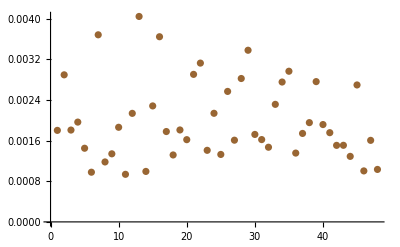

```mathematica
ListPlot[%178,Joined->False,PlotStyle->Brown]
```

```mathematica
{{2,m2[[51,2]]},{3,m3[[51,2]]},{4,m4[[51,2]]},{5,m5[[51,2]]},{6,m6[[51,2]]},{7,m7[[51,2]]},{8,m8[[51,2]]},{9,n1[[51,2]]},{10,n2[[51,2]]},{11,n3[[51,2]]},{12,n4[[51,2]]},{13,n5[[51,2]]},{14,n6[[51,2]]},{15,n7[[51,2]]},{16,n8[[51,2]]},{17,o1[[51,2]]},{18,o2[[51,2]]},{19,o3[[51,2]]},{20,o4[[51,2]]},{21,o5[[51,2]]},{22,o6[[51,2]]},{23,o7[[51,2]]},{24,o8[[51,2]]},{25,p1[[51,2]]},{26,p2[[51,2]]},{27,p3[[51,2]]},{28,p4[[51,2]]},{29,p5[[51,2]]},{30,p6[[51,2]]},{31,p7[[51,2]]},{32,p8[[51,2]]},{33,q1[[51,2]]},{34,q2[[51,2]]},{35,q3[[51,2]]},{36,q4[[51,2]]},{37,q5[[51,2]]},{38,q6[[51,2]]},{39,q7[[51,2]]},{40,q8[[51,2]]},{41,r1[[51,2]]},{42,r2[[51,2]]},{43,r3[[51,2]]},{44,r4[[51,2]]},{45,r5[[51,2]]},{46,r6[[51,2]]},{47,r7[[51,2]]},{48,r8[[51,2]]}}
```

{{2,1.62482},{3,1.23926},{4,1.23495},{5,0.997981},{6,1.22465},{7,1.36246},{8,1.46368},{9,1.45932},{10,1.64548},{11,1.50932},{12,1.58479},{13,1.28427},{14,1.4191},{15,1.48754},{16,1.67734},{17,1.80276},{18,1.42104},{19,1.83359},{20,1.59259},{21,1.80564},{22,1.4865},{23,1.63414},{24,1.55125},{25,1.66891},{26,1.49962},{27,1.39566},{28,1.75733},{29,1.46371},{30,1.57141},{31,1.80145},{32,1.43703},{33,0.842081},{34,1.41374},{35,1.63525},{36,1.49229},{37,1.38851},{38,1.40683},{39,1.52807},{40,1.3793},{41,0.893978},{42,1.71309},{43,1.30947},{44,1.33723},{45,1.89199},{46,1.51308},{47,1.68636},{48,1.31117}}

```mathematica
{Max[{Min/@%392}],Min[{Min/@%392}],final[[51,2]]}
```

{1.89199,0.842081,1.47889}

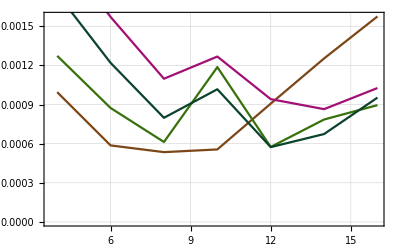

```mathematica
Show[ListLinePlot[{{4,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(n7[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(p2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q8[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]-  Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(q1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]]
```

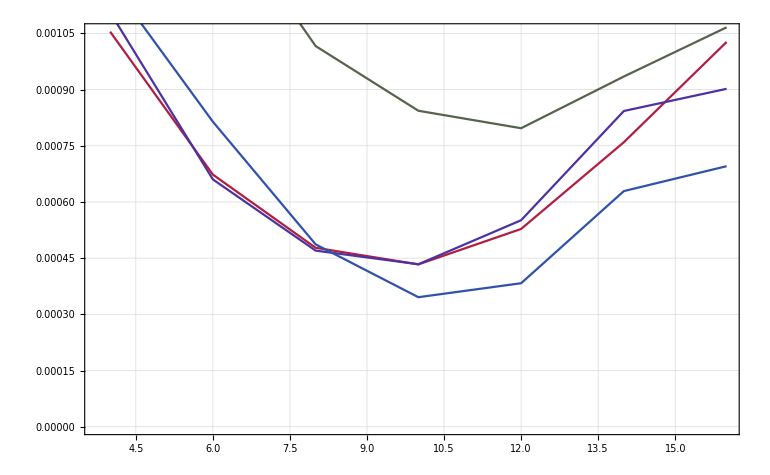

```mathematica
Show[ListLinePlot[{{4,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(m2[[1;;400,2]]- Import["2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(m2[[1;;400,2]]-  Import["3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(m2[[1;;400,2]]-  Import["4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(m2[[1;;400,2]]- Import["5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(m2[[1;;400,2]]- Import["6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(m2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m2[[1;;400]][[;;,1]],(m2[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]-  Import["3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]-  Import["4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m3[[1;;400]][[;;,1]],(m8[[1;;400,2]]- Import["2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]-  Import["3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]-  Import["4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m3[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[{{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["2imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/200]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]-  Import["3imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]-  Import["4imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["5imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["6imp5.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m4[[1;;400,2]]- Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1.99}]/199]}},PlotTheme->"Detailed",PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]]]]
```

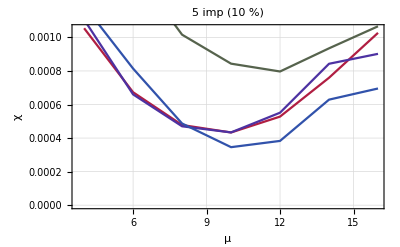

```mathematica
Show[%69,FrameLabel->{{HoldForm[χ],None},{HoldForm[μ],None}},PlotLabel->HoldForm[5 imp (10 %)],LabelStyle->{GrayLevel[0]}]
```

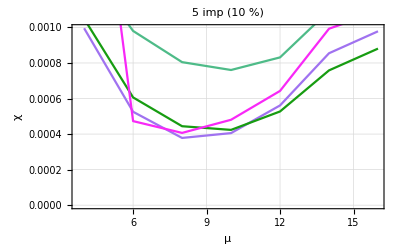

```mathematica
Show[%41,FrameLabel->{{HoldForm[χ],None},{HoldForm[μ],None}},PlotLabel->HoldForm[5 imp (10 %)],LabelStyle->{GrayLevel[0]}]
```

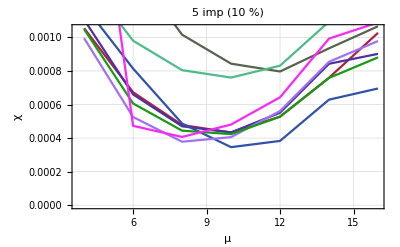

```mathematica
Show[%70,%42]
```